# Gametic selection, sex-ratio bias, and transitions between sex-determining systems

## Michael F Scott, Matthew M Osmond, Sarah P Otto

Notes: 
1) The notation in this notebook differs slightly from the text: here we do not use male and female symbols or sub- and super-scripts. 
2) Throughout we mainly refer to an ancestral XY sex-determination system. By consistently flipping male and female labels, this is equivalent to an ancestral ZW system (noting that the heterogametic sex described in this notebook as XY would refer to heterogametic ZW females).

## General

Assumptions used to simplify the results:

```mathematica
simpcond=Reduce[{0<MAA,0<MAa,0<Maa,0<FAA,0<FAa,0<Faa,0<wAf,0<waf,0<wAm,0<wam,0<αm<1,0<αf<1,0≤Rm≤1/2,0≤Rf≤1/2}];
```

## Recursion equations

### Haploid competition

We start with haploid competition in each sex separately (e.g., pollen competition for eggs). We assume that the allele at an autosomal locus A determines competitive ability, with relative fitnesses wAf and waf in females and wAm and wam in males (in the text this is, e.g., w_A^female). Let the frequency of each gamete from each sex before selection be denoted by four letters, the first being the allele at the ancestral SDR (X or Y), the second being the allele at the selected locus (A or a), the third being the allele at the novel SDR (M or m), and the fourth indicating which sex the gamete came from (m or f). E.g., XAMf is the frequency of the X-A-M genotype among eggs (in the text this is x_1^female). Let the frequencies after haploid selection end in an s, e.g., XAMfs. We then have

```mathematica
(*mean fitness of female gametes*)
wbarHapFemale=(wAf XAMf+waf XaMf+wAf XAmf+waf Xamf)+(wAf YAMf+waf YaMf+wAf YAmf+waf Yamf);

(*non-mutant eggs*)
XAMfs=wAf XAMf/wbarHapFemale;
XaMfs=waf XaMf/wbarHapFemale;
YAMfs=wAf YAMf/wbarHapFemale;
YaMfs=waf YaMf/wbarHapFemale;

(*mutant eggs*)
XAmfs=wAf XAmf/wbarHapFemale;
Xamfs=waf Xamf/wbarHapFemale;
YAmfs=wAf YAmf/wbarHapFemale;
Yamfs=waf Yamf/wbarHapFemale;

(*mean fitness of male gametes*)
wbarHapMale=(wAm XAMm+wam XaMm+wAm XAmm+wam Xamm)+(wAm YAMm+wam YaMm+wAm YAmm+wam Yamm);

(*non-mutant male gametes*)
XAMms=wAm XAMm/wbarHapMale;
XaMms=wam XaMm/wbarHapMale;
YAMms= wAm YAMm/wbarHapMale;
YaMms= wam YaMm/wbarHapMale;

(*mutant male gametes*)
XAmms=wAm XAmm/wbarHapMale;
Xamms=wam Xamm/wbarHapMale;
YAmms= wAm YAmm/wbarHapMale;
Yamms= wam Yamm/wbarHapMale;
```

Check that frequencies sum to one in each sex after haploid selection:

```mathematica
1==XAMms+XaMms+YAMms+YaMms+XAmms+Xamms+YAmms+Yamms//Factor (*male gametes*)
1==XAMfs+XaMfs+XAmfs+Xamfs+YAMfs+YaMfs+YAmfs+Yamfs//Factor (*eggs*)
```

True

True

### Random mating

Let the probability that a zygote develops into a female be denoted with k followed by four letters: the first two indicating the ancestral SDR genotype, and the second two denoting the novel SDR genotype. For example, kXYMm is the probabiliy that a zygote with XY at the ancestral SDR and Mm at the novel SDR develops into a female. Let the frequency of zygotes be denoted by the two gamete genotypes followed by the sex, e.g., XAMYamfemale is the frequency of zygotes that are female and composed of X-A-M and Y-a-M gametes (it does not matter which came from which parent, i.e., XAM could come from the mother or father). Then, after random mating the frequencies of the diploid genotypes are

```mathematica
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXXMM (XAMfs XAMms);
XAMXaMfemale=kXXMM(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXXMM(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXXMM)(XAMfs XAMms);
XAMXaMmale=(1-kXXMM)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXXMM)(XaMfs XaMms);

(*XM-YM females*)
XAMYAMfemale=kXYMM(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXYMM(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXYMM(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXYMM(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXYMM)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXYMM)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXYMM)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXYMM)(XaMfs YaMms+YaMfs XaMms);

(*YM-YM females*)
YAMYAMfemale=kYYMM(YAMfs YAMms);
YAMYaMfemale=kYYMM(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYYMM(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYYMM)(YAMfs YAMms);
YAMYaMmale=(1-kYYMM)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYYMM)(YaMfs YaMms);

(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kXXMm (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kXXMm(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kXXMm(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kXXMm(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kXXMm) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kXXMm)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kXXMm)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kXXMm)(Xamfs XaMms+XaMfs Xamms);

(*Xm-YM females*)
XAmYAMfemale=kXYMm(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kXYMm(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kXYMm(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kXYMm(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kXYMm)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kXYMm)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kXYMm)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kXYMm)(Xamfs YaMms+YaMfs Xamms);

(*XM-Ym females*)
XAMYAmfemale=kXYMm(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kXYMm(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kXYMm(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kXYMm(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kXYMm)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kXYMm)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kXYMm)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kXYMm)(XaMfs Yamms+Yamfs XaMms);

(*Ym-YM females*)
YAmYAMfemale=kYYMm(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kYYMm(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kYYMm(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kYYMm(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kYYMm)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kYYMm)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kYYMm)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kYYMm)(Yamfs YaMms+YaMfs Yamms);

(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kXXmm(XAmfs XAmms);
XAmXamfemale=kXXmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kXXmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kXXmm)(XAmfs XAmms);
XAmXammale=(1-kXXmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kXXmm)(Xamfs Xamms);

(*Xm-Ym females*)
XAmYAmfemale=kXYmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kXYmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kXYmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kXYmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kXYmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kXYmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kXYmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kXYmm)(Xamfs Yamms+Yamfs Xamms);

(*Ym-Ym females*)
YAmYAmfemale=kYYmm(YAmfs YAmms);
YAmYamfemale=kYYmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kYYmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kYYmm)(YAmfs YAmms);
YAmYammale=(1-kYYmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kYYmm)(Yamfs Yamms);
```

Check that they sum to one

```mathematica
1==XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMXAMmale+XAMXaMmale+XaMXaMmale+
XAMYAMmale+XAMYaMmale+XaMYAMmale+XaMYaMmale+
XAMYAMfemale+XAMYaMfemale+XaMYAMfemale+XaMYaMfemale+
YAMYAMmale+YAMYaMmale+YaMYaMmale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmXAMmale+XAmXaMmale+XAMXammale+XamXaMmale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAmYAMmale+XAmYaMmale+XamYAMmale+XamYaMmale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
XAMYAmmale+XAMYammale+XaMYAmmale+XaMYammale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
YAmYAMmale+YAmYaMmale+YamYAMmale+YamYaMmale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmXAmmale+XAmXammale+XamXammale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
XAmYAmmale+XAmYammale+XamYAmmale+XamYammale+
YAmYAmfemale+YAmYamfemale+YamYamfemale+
YAmYAmmale+YAmYammale+YamYammale//Factor
```

True

### Diploid selection

We next model selection in diploids, which can differ among the sexes. Let FAA, FAa, and Faa be the relative fitnesses of females homozygous for allele A, heterozygous, or homozygous for allele a at the autosomal locus. Similarly we use MAA, MAa, and Maa in males. Frequencies after selection in diploids are indicated by appending an s to the name

```mathematica
(*mean male fitness*)
wbarM=
MAA XAMXAMmale+MAa XAMXaMmale+Maa XaMXaMmale+
MAA XAMYAMmale+MAa (XAMYaMmale+XaMYAMmale)+Maa XaMYaMmale+
MAA YAMYAMmale+MAa YAMYaMmale+Maa YaMYaMmale+
MAA XAmXAMmale+MAa (XAmXaMmale+XAMXammale)+Maa XamXaMmale+
MAA XAmYAMmale+MAa (XAmYaMmale+XamYAMmale)+Maa XamYaMmale+
MAA XAMYAmmale+MAa(XAMYammale+XaMYAmmale)+Maa XaMYammale+
MAA YAmYAMmale+MAa (YAmYaMmale+YamYAMmale)+Maa YamYaMmale+
MAA XAmXAmmale+MAa XAmXammale+Maa XamXammale+
MAA XAmYAmmale+MAa (XAmYammale+XamYAmmale)+Maa XamYammale+
MAA YAmYAmmale+MAa YAmYammale+Maa YamYammale;

XAMXAMmales=MAA XAMXAMmale/wbarM;
XAMXaMmales=MAa XAMXaMmale/wbarM;
XaMXaMmales=Maa XaMXaMmale/wbarM;

XAMYAMmales=MAA XAMYAMmale/wbarM;
XAMYaMmales=MAa XAMYaMmale/wbarM;
XaMYAMmales=MAa XaMYAMmale/wbarM;
XaMYaMmales=Maa XaMYaMmale/wbarM;

YAMYAMmales=MAA YAMYAMmale/wbarM;
YAMYaMmales=MAa YAMYaMmale/wbarM;
YaMYaMmales=Maa YaMYaMmale/wbarM;

XAmXAMmales=MAA XAmXAMmale/wbarM;
XAmXaMmales=MAa XAmXaMmale/wbarM;
XAMXammales=MAa XAMXammale/wbarM;
XamXaMmales=Maa XamXaMmale/wbarM;

XAmYAMmales=MAA XAmYAMmale/wbarM;
XAmYaMmales=MAa XAmYaMmale/wbarM;
XamYAMmales=MAa XamYAMmale/wbarM;
XamYaMmales=Maa XamYaMmale/wbarM;

XAMYAmmales=MAA XAMYAmmale/wbarM;
XAMYammales=MAa XAMYammale/wbarM;
XaMYAmmales=MAa XaMYAmmale/wbarM;
XaMYammales=Maa XaMYammale/wbarM;

YAmYAMmales=MAA YAmYAMmale/wbarM;
YAmYaMmales=MAa YAmYaMmale/wbarM;
YamYAMmales=MAa YamYAMmale/wbarM;
YamYaMmales=Maa YamYaMmale/wbarM;

XAmXAmmales=MAA XAmXAmmale/wbarM;
XAmXammales=MAa XAmXammale/wbarM;
XamXammales=Maa XamXammale/wbarM;

XAmYAmmales=MAA XAmYAmmale/wbarM;
XAmYammales=MAa XAmYammale/wbarM;
XamYAmmales=MAa XamYAmmale/wbarM;
XamYammales=Maa XamYammale/wbarM;

YAmYAmmales=MAA YAmYAmmale/wbarM;
YAmYammales=MAa YAmYammale/wbarM;
YamYammales=Maa YamYammale/wbarM;
```

Frequency of males after diploid selection should sum to 1

```mathematica
1==XAMXAMmales+XAMXaMmales+XaMXaMmales+
XAMYAMmales+XAMYaMmales+XaMYAMmales+XaMYaMmales+
YAMYAMmales+YAMYaMmales+YaMYaMmales+
XAmXAMmales+XAmXaMmales+XAMXammales+XamXaMmales+
XAmYAMmales+XAmYaMmales+XamYAMmales+XamYaMmales+
XAMYAmmales+XAMYammales+XaMYAmmales+XaMYammales+
YAmYAMmales+YAmYaMmales+YamYAMmales+YamYaMmales+
XAmXAmmales+XAmXammales+XamXammales+
XAmYAmmales+XAmYammales+XamYAmmales+XamYammales+
YAmYAmmales+YAmYammales+YamYammales//Factor
```

True

```mathematica
(*mean female fitness*)
wbarF=FAA XAMXAMfemale+FAa XAMXaMfemale+Faa XaMXaMfemale+
FAA XAMYAMfemale+FAa (XAMYaMfemale+XaMYAMfemale)+Faa XaMYaMfemale+
FAA YAMYAMfemale+FAa YAMYaMfemale+Faa YaMYaMfemale+
FAA XAmXAMfemale+FAa XAmXaMfemale+FAa XAMXamfemale+Faa XamXaMfemale+
FAA XAmYAMfemale+FAa XAmYaMfemale+FAa XamYAMfemale+Faa XamYaMfemale+
FAA XAMYAmfemale+FAa XAMYamfemale+FAa XaMYAmfemale+Faa XaMYamfemale+
FAA YAmYAMfemale+FAa YAmYaMfemale+FAa YamYAMfemale+Faa YamYaMfemale+
FAA XAmXAmfemale+FAa XAmXamfemale+Faa XamXamfemale+
FAA XAmYAmfemale+FAa XAmYamfemale+FAa XamYAmfemale+Faa XamYamfemale+
FAA YAmYAmfemale+FAa YAmYamfemale+Faa YamYamfemale;

XAMXAMfemales=FAA XAMXAMfemale/wbarF;
XAMXaMfemales=FAa XAMXaMfemale/wbarF;
XaMXaMfemales=Faa XaMXaMfemale/wbarF;

XAMYAMfemales=FAA XAMYAMfemale/wbarF;
XAMYaMfemales=FAa XAMYaMfemale/wbarF;
XaMYAMfemales=FAa XaMYAMfemale/wbarF;
XaMYaMfemales=Faa XaMYaMfemale/wbarF;

YAMYAMfemales=FAA YAMYAMfemale/wbarF;
YAMYaMfemales=FAa YAMYaMfemale/wbarF;
YaMYaMfemales=Faa YaMYaMfemale/wbarF;

XAmXAMfemales=FAA XAmXAMfemale/wbarF;
XAmXaMfemales=FAa XAmXaMfemale/wbarF;
XAMXamfemales=FAa XAMXamfemale/wbarF;
XamXaMfemales=Faa XamXaMfemale/wbarF;

XAmYAMfemales=FAA XAmYAMfemale/wbarF;
XAmYaMfemales=FAa XAmYaMfemale/wbarF;
XamYAMfemales=FAa XamYAMfemale/wbarF;
XamYaMfemales=Faa XamYaMfemale/wbarF;

XAMYAmfemales=FAA XAMYAmfemale/wbarF;
XAMYamfemales=FAa XAMYamfemale/wbarF;
XaMYAmfemales=FAa XaMYAmfemale/wbarF;
XaMYamfemales=Faa XaMYamfemale/wbarF;

YAmYAMfemales=FAA YAmYAMfemale/wbarF;
YAmYaMfemales=FAa YAmYaMfemale/wbarF;
YamYAMfemales=FAa YamYAMfemale/wbarF;
YamYaMfemales=Faa YamYaMfemale/wbarF;

XAmXAmfemales=FAA XAmXAmfemale/wbarF;
XAmXamfemales=FAa XAmXamfemale/wbarF;
XamXamfemales=Faa XamXamfemale/wbarF;

XAmYAmfemales=FAA XAmYAmfemale/wbarF;
XAmYamfemales=FAa XAmYamfemale/wbarF;
XamYAmfemales=FAa XamYAmfemale/wbarF;
XamYamfemales=Faa XamYamfemale/wbarF;

YAmYAmfemales=FAA YAmYAmfemale/wbarF;
YAmYamfemales=FAa YAmYamfemale/wbarF;
YamYamfemales=Faa YamYamfemale/wbarF;
```

Frequency of females after diplod selection should sum to 1

```mathematica
1==XAMXAMfemales+XAMXaMfemales+XaMXaMfemales+
XAMYAMfemales+XAMYaMfemales+XaMYAMfemales+XaMYaMfemales+
YAMYAMfemales+YAMYaMfemales+YaMYaMfemales+
XAmXAMfemales+XAmXaMfemales+XAMXamfemales+XamXaMfemales+
XAmYAMfemales+XAmYaMfemales+XamYAMfemales+XamYaMfemales+
XAMYAmfemales+XAMYamfemales+XaMYAmfemales+XaMYamfemales+
YAmYAMfemales+YAmYaMfemales+YamYAMfemales+YamYaMfemales+
XAmXAmfemales+XAmXamfemales+XamXamfemales+
XAmYAmfemales+XAmYamfemales+XamYAmfemales+XamYamfemales+
YAmYAmfemales+YAmYamfemales+YamYamfemales//Factor
```

True

### Meiosis

Translate zygote frequencies into notation in the main text to give recursion equations:

a) first two letters refer to the ancestral SDR locus genotype (now lower case, e.g., xy)
b) then two numbers ij give A and M locus genotype where 1=AM, 2=aM, 3=Am, 4=am
c) then m or f indicate male or female
d) then s indicates that these are frequencies after selection

e.g., xy41ms is the frequency of zygotes that are male and composed of gametes X-a-m and Y-A-M. 
When i and j are interchangable (in YY and XX individuals) the lowest number is given first.

```mathematica
xx11ms=XAMXAMmales;
xx12ms=XAMXaMmales;
xx22ms=XaMXaMmales;

xx13ms=XAmXAMmales;
xx23ms=XAmXaMmales;
xx14ms=XAMXammales;
xx24ms=XamXaMmales;

xx33ms=XAmXAmmales;
xx34ms=XAmXammales;
xx44ms=XamXammales;

xy11ms=XAMYAMmales;
xy12ms=XAMYaMmales;
xy21ms=XaMYAMmales;
xy22ms=XaMYaMmales;

xy31ms=XAmYAMmales;
xy32ms=XAmYaMmales;
xy41ms=XamYAMmales;
xy42ms=XamYaMmales;

xy13ms=XAMYAmmales;
xy14ms=XAMYammales;
xy23ms=XaMYAmmales;
xy24ms=XaMYammales;

xy33ms=XAmYAmmales;
xy34ms=XAmYammales;
xy43ms=XamYAmmales;
xy44ms=XamYammales;

yy11ms=YAMYAMmales;
yy12ms=YAMYaMmales;
yy22ms=YaMYaMmales;

yy13ms=YAmYAMmales;
yy23ms=YAmYaMmales;
yy14ms=YamYAMmales;
yy24ms=YamYaMmales;

yy33ms=YAmYAmmales;
yy34ms=YAmYammales;
yy44ms=YamYammales;
```

```mathematica
xx11fs=XAMXAMfemales;
xx12fs=XAMXaMfemales;
xx22fs=XaMXaMfemales;

xx13fs=XAmXAMfemales;
xx23fs=XAmXaMfemales;
xx14fs=XAMXamfemales;
xx24fs=XamXaMfemales;

xx33fs=XAmXAmfemales;
xx34fs=XAmXamfemales;
xx44fs=XamXamfemales;

xy11fs=XAMYAMfemales;
xy12fs=XAMYaMfemales;
xy21fs=XaMYAMfemales;
xy22fs=XaMYaMfemales;

xy31fs=XAmYAMfemales;
xy32fs=XAmYaMfemales;
xy41fs=XamYAMfemales;
xy42fs=XamYaMfemales;

xy13fs=XAMYAmfemales;
xy14fs=XAMYamfemales;
xy23fs=XaMYAmfemales;
xy24fs=XaMYamfemales;

xy33fs=XAmYAmfemales;
xy34fs=XAmYamfemales;
xy43fs=XamYAmfemales;
xy44fs=XamYamfemales;

yy11fs=YAMYAMfemales;
yy12fs=YAMYaMfemales;
yy22fs=YaMYaMfemales;

yy13fs=YAmYAMfemales;
yy23fs=YAmYaMfemales;
yy14fs=YamYAMfemales;
yy24fs=YamYaMfemales;

yy33fs=YAmYAmfemales;
yy34fs=YAmYamfemales;
yy44fs=YamYamfemales;
```

Let the probability of recombination (an odd number of crossover events) between the ancestral SDR and the selected locus be r. Let the probability of recombination between the selected locus and the novel SDR be R. And let the probability of recombination between the ancestral and novel SDRs be ρ.

Let the probability that a heterozygote at the selected locus passes down an A depend on sex, αf or αm. E.g., when αf=1/2 there is no meiotic drive in females.

The next generation frequencies in female gametes are then

```mathematica
(*X bearing ovules*)
nextXAMf=xx11fs+xx13fs/2+(xx12fs+xx14fs*(1-R)+xx23fs*R)αf+
xy11fs/2+(xy12fs(1-r)+xy21fs (r))αf+
(xy13fs(1-ρ)+xy31fs (ρ))/2+
xy14fs *αf+
(xy14fs (-(R+r+ρ))+ 
xy41fs(r+ρ-R)+
xy23fs(R+r-ρ)+
xy32fs(R+ρ-r))αf/2;

nextXaMf=xx22fs+xx24fs/2+(xx12fs+xx23fs*(1-R)+xx14fs*R)(1-αf)+
xy22fs/2+(xy12fs(r)+xy21fs(1-r))(1-αf)+
(xy24fs (1-ρ)+xy42fs (ρ))/2+
xy23fs*(1-αf)+
(xy14fs(R+r-ρ)+
xy41fs(R+ρ-r)+
xy23fs(-(R+r+ρ))+
xy32fs (r+ρ-R))(1-αf)/2;

nextXAmf=xx33fs+xx13fs/2+(xx23fs*(1-R)+R*xx14fs+xx34fs)αf+
xy33fs/2+(xy34fs(1-r)+xy43fs(r))αf+
(xy13fs(ρ)+xy31fs(1-ρ))/2+
xy32fs *αf+
(xy14fs(R+ρ-r)+
xy41fs(R+r-ρ)+
xy23fs(r+ρ-R)+
xy32fs (-(R+r+ρ)))αf/2;

nextXamf=xx44fs+xx24fs/2+(xx14fs*(1-R)+xx23fs*R+xx34fs)(1-αf)+
xy44fs/2+(xy34fs(r)+xy43fs(1-r))(1-αf)+
(xy24fs(ρ)+xy42fs(1-ρ))/2+
xy41fs*(1-αf)+
(xy14fs(r+ρ-R)+
xy41fs(-(R+r+ρ))+
xy23fs(R+ρ-r)+
xy32fs(R+r-ρ))(1-αf)/2;

(*Y bearing ovules*)
nextYAMf=yy11fs+yy13fs/2+(yy12fs+yy14fs*(1-R)+yy23fs*R)αf+
xy11fs/2+(xy12fs(r)+xy21fs (1-r))(αf)+
(xy13fs(ρ)+xy31fs (1-ρ))/2+
xy41fs*αf+
(xy14fs (r+ρ-R)+
 xy41fs(-(R+r+ρ))+
xy23fs(R+ρ-r)+
xy32fs(R+r-ρ))αf/2;

nextYaMf =yy22fs+yy24fs/2+(yy12fs+yy23fs*(1-R)+yy14fs*R)(1-αf)+
xy22fs/2+(xy12fs(1-r)+xy21fs(r))(1-αf)+
(xy24fs (ρ)+xy42fs (1-ρ))/2+
xy32fs*(1-αf)+
(xy14fs(R+ρ-r)+
xy41fs(R+r-ρ)+
xy23fs(r+ρ-R)+
xy32fs (-(R+r+ρ)))(1-αf)/2;

nextYAmf =yy33fs+yy13fs/2+(yy23fs*(1-R)+R*yy14fs+yy34fs)αf+
xy33fs/2+(xy34fs(r)+xy43fs(1-r))(αf)+
(xy13fs(1-ρ)+xy31fs(ρ))/2+
xy23fs*αf+
(xy14fs(R+r-ρ)+
xy41fs(R+ρ-r)+
xy23fs(-(R+r+ρ))+
xy32fs (r+ρ-R))αf/2;

nextYamf=yy44fs+yy24fs/2+(yy14fs*(1-R)+yy23fs*R+yy34fs)(1-αf)+
xy44fs/2+(xy34fs(1-r)+xy43fs(r))(1-αf)+
(xy24fs(1-ρ)+xy42fs(ρ))/2+
xy14fs*(1-αf)+
(xy14fs(-(R+r+ρ))+
xy41fs(r+ρ-R)+
xy23fs(R+r-ρ)+
xy32fs(R+ρ-r))(1-αf)/2;
```

```mathematica
Factor[nextXAMf+nextXaMf+nextXAmf+nextXamf+nextYAMf+nextYaMf+nextYAmf+nextYamf]
```

1

And the next generation frequencies in male gametes are

```mathematica
(*X bearing pollen*)
nextXAMm=xx11ms+xx13ms/2+(xx12ms+xx14ms*(1-R)+xx23ms*R)αm+
xy11ms/2+(xy12ms(1-r)+xy21ms (r))αm+
(xy13ms(1-ρ)+xy31ms (ρ))/2+
xy14ms *αm+
(xy14ms (-(R+r+ρ))+ 
xy41ms(r+ρ-R)+
xy23ms(R+r-ρ)+
xy32ms(R+ρ-r))αm/2;

nextXaMm =xx22ms+xx24ms/2+(xx12ms+xx23ms*(1-R)+xx14ms*R)(1-αm)+
xy22ms/2+(xy12ms(r)+xy21ms(1-r))(1-αm)+
(xy24ms (1-ρ)+xy42ms (ρ))/2+
xy23ms*(1-αm)+
(xy14ms(R+r-ρ)+
xy41ms(R+ρ-r)+
xy23ms(-(R+r+ρ))+
xy32ms (r+ρ-R))(1-αm)/2;

nextXAmm =xx33ms+xx13ms/2+(xx23ms*(1-R)+R*xx14ms+xx34ms)αm+
xy33ms/2+(xy34ms(1-r)+xy43ms(r))αm+
(xy13ms(ρ)+xy31ms(1-ρ))/2+
xy32ms *αm+
(xy14ms(R+ρ-r)+
xy41ms(R+r-ρ)+
xy23ms(r+ρ-R)+
xy32ms (-(R+r+ρ)))αm/2;

nextXamm=xx44ms+xx24ms/2+(xx14ms*(1-R)+xx23ms*R+xx34ms)(1-αm)+
xy44ms/2+(xy34ms(r)+xy43ms(1-r))(1-αm)+
(xy24ms(ρ)+xy42ms(1-ρ))/2+
xy41ms*(1-αm)+
(xy14ms(r+ρ-R)+
xy41ms(-(R+r+ρ))+
xy23ms(R+ρ-r)+
xy32ms(R+r-ρ))(1-αm)/2;

(*Y bearing pollen*)
nextYAMm=yy11ms+yy13ms/2+(yy12ms+yy14ms*(1-R)+yy23ms*R)αm+
xy11ms/2+(xy12ms(r)+xy21ms (1-r))(αm)+
(xy13ms(ρ)+xy31ms (1-ρ))/2+
xy41ms*αm+
(xy14ms (r+ρ-R)+
 xy41ms(-(R+r+ρ))+
xy23ms(R+ρ-r)+
xy32ms(R+r-ρ))αm/2;

nextYaMm =yy22ms+yy24ms/2+(yy12ms+yy23ms*(1-R)+yy14ms*R)(1-αm)+
xy22ms/2+(xy12ms(1-r)+xy21ms(r))(1-αm)+
(xy24ms (ρ)+xy42ms (1-ρ))/2+
xy32ms*(1-αm)+
(xy14ms(R+ρ-r)+
xy41ms(R+r-ρ)+
xy23ms(r+ρ-R)+
xy32ms (-(R+r+ρ)))(1-αm)/2;

nextYAmm=yy33ms+yy13ms/2+(yy23ms*(1-R)+R*yy14ms+yy34ms)αm+
xy33ms/2+(xy34ms(r)+xy43ms(1-r))(αm)+
(xy13ms(1-ρ)+xy31ms(ρ))/2+
xy23ms*αm+
(xy14ms(R+r-ρ)+
xy41ms(R+ρ-r)+
xy23ms(-(R+r+ρ))+
xy32ms (r+ρ-R))αm/2;

nextYamm=yy44ms+yy24ms/2+(yy14ms*(1-R)+yy23ms*R+yy34ms)(1-αm)+
xy44ms/2+(xy34ms(1-r)+xy43ms(r))(1-αm)+
(xy24ms(1-ρ)+xy42ms(ρ))/2+
xy14ms*(1-αm)+
(xy14ms(-(R+r+ρ))+
xy41ms(r+ρ-R)+
xy23ms(R+r-ρ)+
xy32ms(R+ρ-r))(1-αm)/2;
```

```mathematica
Factor[nextXAMm+nextXaMm+nextXAmm+nextXamm+nextYAMm+nextYaMm+nextYAmm+nextYamm]
```

1

Let the probability a zygote develops as a female be completely determined by the ancestral SDR when a zygote has no m alleles (XX females and XY and YY males) and be k whenever a zygote has at least on m allele:

```mathematica
SUBS={
kXXMM->1,
kXYMM->0,
kYYMM->0,
kXXMm->k,
kXYMm->k,
kYYMm->k,
kXXmm->k,
kXYmm->k,
kYYmm->k
};
```

## Resident equilibria and stability

### General

We first explore the resident equilibria, where the m allele is absent and sex is only determined by the ancestral sex-determining locus. In this case there no Y alleles in gametes from females and no M alleles in gametes from any sex, leaving us with 6 equations.

```mathematica
{nextXAMm,nextXaMm,nextXAmm,nextXamm,nextYAMm,nextYaMm,nextYAmm,nextYamm,nextXAMf,nextXaMf,nextXAmf,nextXamf,nextYAMf,nextYaMf,nextYAmf,nextYamf}/.XAmm->0/.Xamm->0/.YAmm->0/.Yamm->0/.XAmf->0/.Xamf->0/.YAmf->0/.Yamf->0/.YAMf->0/.YaMf->0/.SUBS//Simplify
```

{(MAA wAf wAm XAMf YAMm+2 MAa (-(-1+r) wAf wam XAMf YaMm+r waf wAm XaMf YAMm) αm)/(2 (Maa waf wam XaMf YaMm+MAa wAf wam XAMf YaMm+MAa waf wAm XaMf YAMm+MAA wAf wAm XAMf YAMm)),(Maa waf wam XaMf YaMm-2 MAa (r wAf wam XAMf YaMm+waf wAm XaMf YAMm-r waf wAm XaMf YAMm) (-1+αm))/(2 (Maa waf wam XaMf YaMm+MAa wAf wam XAMf YaMm+MAa waf wAm XaMf YAMm+MAA wAf wAm XAMf YAMm)),0,0,(MAA wAf wAm XAMf YAMm+2 MAa (r wAf wam XAMf YaMm+waf wAm XaMf YAMm-r waf wAm XaMf YAMm) αm)/(2 (Maa waf wam XaMf YaMm+MAa wAf wam XAMf YaMm+MAa waf wAm XaMf YAMm+MAA wAf wAm XAMf YAMm)),(Maa waf wam XaMf YaMm+2 MAa ((-1+r) wAf wam XAMf YaMm-r waf wAm XaMf YAMm) (-1+αm))/(2 (Maa waf wam XaMf YaMm+MAa wAf wam XAMf YaMm+MAa waf wAm XaMf YAMm+MAA wAf wAm XAMf YAMm)),0,0,(FAA wAf wAm XAMf XAMm+FAa wAf wam XAMf XaMm αf+FAa waf wAm XaMf XAMm αf)/(Faa waf wam XaMf XaMm+FAa wAf wam XAMf XaMm+FAa waf wAm XaMf XAMm+FAA wAf wAm XAMf XAMm),(Faa waf wam XaMf XaMm-FAa (wAf wam XAMf XaMm+waf wAm XaMf XAMm) (-1+αf))/(Faa waf wam XaMf XaMm+FAa wAf wam XAMf XaMm+FAa waf wAm XaMf XAMm+FAA wAf wAm XAMf XAMm),0,0,0,0,0,0}

Letting pXf be the frequency of A in non-mutant female gametes, pXm be the frequency of A in in non-mutant male gametes with an X allele, pYm be the frequency of A in in non-mutant female gametes with a Y allele, and q be the frequency of Y alleles in male gametes

```mathematica
subequil={
XAMf->pXf,
XaMf->(1-pXf),
YAMf->0,
YaMf->0,
XAMm->pXm(1-q),
XaMm->(1-pXm)(1-q),
YAMm->pYm*q,
YaMm->(1-pYm)*q,
XAmf->0,
Xamf->0,
XAmm->0,
Xamm->0,
YAmm->0,
Yamm->0,
YAmf->0,
Yamf->0
};
```

this system of six equations reduces to four (because the two female gamete frequencies must sum to one, as must the 4 male gamete frequencies).

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following four equations are zero

```mathematica
differenceEqs={
nextXAMf-XAMf,
nextXAMm-XAMm,
nextYAMm-YAMm,
nextYAMm+nextYaMm-(YAMm+YaMm)
}/.SUBS/.subequil;
```

The first equation is zero when

```mathematica
sub1=Flatten[Solve[differenceEqs[[3]]==0,pXf]]//Factor
```

{pXf→(2 pYm waf (-Maa q wam+Maa pYm q wam-MAa pYm q wAm+MAa wAm αm-MAa r wAm αm))/(-2 Maa pYm q waf wam+2 Maa pYm^2 q waf wam+2 MAa pYm q wAf wam-2 MAa pYm^2 q wAf wam-2 MAa pYm^2 q waf wAm-MAA pYm wAf wAm+2 MAA pYm^2 q wAf wAm-2 MAa r wAf wam αm+2 MAa pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pYm r waf wAm αm)}

The second equation is zero when

```mathematica
sub2=Flatten[Solve[Factor[differenceEqs[[2]]/.sub1]==0,pXm]]//Factor
```

{pXm→-(pYm (-Maa MAA pYm q wam wAm+Maa MAA pYm^2 q wam wAm-MAa MAA pYm^2 q wAm^2-2 Maa MAa q wam^2 αm+4 Maa MAa pYm q wam^2 αm-2 Maa MAa pYm^2 q wam^2 αm+2 Maa MAa q r wam^2 αm-4 Maa MAa pYm q r wam^2 αm+2 Maa MAa pYm^2 q r wam^2 αm-2 MAa^2 pYm q wam wAm αm+2 MAa^2 pYm^2 q wam wAm αm+4 MAa^2 pYm q r wam wAm αm-4 MAa^2 pYm^2 q r wam wAm αm+MAa MAA pYm wAm^2 αm-2 MAa MAA pYm r wAm^2 αm+2 MAa MAA pYm^2 q r wAm^2 αm+2 MAa^2 wam wAm αm^2-2 MAa^2 pYm wam wAm αm^2-4 MAa^2 r wam wAm αm^2+4 MAa^2 pYm r wam wAm αm^2))/((-1+q) (-Maa MAA pYm wam wAm+Maa MAA pYm^2 wam wAm-MAa MAA pYm^2 wAm^2-2 Maa MAa r wam^2 αm+4 Maa MAa pYm r wam^2 αm-2 Maa MAa pYm^2 r wam^2 αm+2 MAa^2 pYm wam wAm αm-2 MAa^2 pYm^2 wam wAm αm-4 MAa^2 pYm r wam wAm αm+4 MAa^2 pYm^2 r wam wAm αm+2 MAa MAA pYm^2 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm))}

The fourth equation is zero when

```mathematica
sub3=Flatten[Solve[Factor[differenceEqs[[4]]/.sub1/.sub2]==0,q]]//Factor
```

{q→-(Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+2 MAa MAA pYm^2 r wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2)/(2 (Maa MAa pYm wam^2-2 Maa MAa pYm^2 wam^2+Maa MAa pYm^3 wam^2-2 Maa MAa pYm r wam^2+4 Maa MAa pYm^2 r wam^2-2 Maa MAa pYm^3 r wam^2-Maa MAA pYm wam wAm+2 MAa^2 pYm^2 wam wAm+Maa MAA pYm^2 wam wAm-2 MAa^2 pYm^3 wam wAm-4 MAa^2 pYm^2 r wam wAm+4 MAa^2 pYm^3 r wam wAm-MAa MAA pYm^2 wAm^2+MAa MAA pYm^3 wAm^2-2 MAa MAA pYm^3 r wAm^2-2 Maa MAa pYm wam^2 αm+4 Maa MAa pYm^2 wam^2 αm-2 Maa MAa pYm^3 wam^2 αm-2 Maa MAa r wam^2 αm+8 Maa MAa pYm r wam^2 αm-10 Maa MAa pYm^2 r wam^2 αm+4 Maa MAa pYm^3 r wam^2 αm+2 MAa^2 pYm wam wAm αm-6 MAa^2 pYm^2 wam wAm αm+4 MAa^2 pYm^3 wam wAm αm-4 MAa^2 pYm r wam wAm αm+12 MAa^2 pYm^2 r wam wAm αm-8 MAa^2 pYm^3 r wam wAm αm+2 MAa MAA pYm^2 wAm^2 αm-2 MAa MAA pYm^3 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa MAA pYm^3 r wAm^2 αm))}

Leaving us with an equation for pYm only

```mathematica
equilsol=Numerator[Factor[differenceEqs[[1]]/.sub1/.sub2/.sub3]];
```

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The internal stability matrix (i.e., the Jacobian for the residents) is

```mathematica
eqs={nextXAMf,nextXAMm/(nextXAMm+nextXaMm),nextYAMm/(nextYAMm+nextYaMm),nextYAMm+nextYaMm}/.SUBS/.subequil;
matIntFull=Transpose[{
D[eqs,pXf],
D[eqs,pXm],
D[eqs,pYm],
D[eqs,freqYm]
}]/.SUBS/.subequil//Factor;
```

The last column of matIntFull is full of zeros, corresponding to an eigenvalue of zero and indicating that the sex ratio in the system equilibrates immediately:

```mathematica
Transpose[matIntFull][[4]]
```

{0,0,0,0}

As a consequence, we drop the last row and column in matIntFull:

```mathematica
matIntFull=Table[matIntFull[[i,j]],{i,1,3},{j,1,3}];
```

The characteristic polynomial is

```mathematica
charpolyIntFull=Det[matIntFull-IdentityMatrix[3]*λ];
```

We will explore the equilibria for two special cases, tight linkage and weak selection.

### Tight linkage

#### Equilibria

Here we look at the case where there is tight linkage between the ancestral sex-determining locus and the selected locus.

When there is complete linkage, r=0 (ie the selected locus is in the ancestral sex-determining region), the equilibrium frquency of A on Y gametes in males is

```mathematica
equilsol/.r->0//Factor;
equilsol2=Solve[%==0,pYm]//Simplify
```

{{pYm→0},{pYm→0},{pYm→0},{pYm→1},{pYm→1},{pYm→1},{pYm→(wam (Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))}}

First, consider cases where pYm=0.

With allele a fixed on Y (pYm=0), then {pXf, pXm, q} equal:

```mathematica
Solve[(differenceEqs/.r->0/.pYm->0//Factor)=={0,0,0,0},{pXf,pXm,q}]//Simplify
```

{{pXf→0,pXm→0,q→1/2},{pXf→1,pXm→1,q→1-αm},{pXf→(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),pXm→-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),q→(FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm)))}}

The last of these has a polymorphism on the X chromosome; we’ll call this equilA0 (“0” because this is the leading order term in r...we could take additional order terms to get the linear approximation in r, etc.).

```mathematica
equilA0={pXf->(pXf/.%[[3]]),pXm->(pXm/.%[[3]]),pYm->0,q-> (q/.%[[3]])}
```

{pXf→(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),pXm→-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),pYm→0,q→(FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm)))}

The second of these is also polymorphic (Y fixed on a and X fixed on A), which we'll call equilB0.

```mathematica
equilB0={pXf->(pXf/.%%[[2]]),pXm->(pXm/.%%[[2]]),pYm->0,q->(q/.%%[[2]])}
```

{pXf→1,pXm→1,pYm→0,q→1-αm}

Next, consider cases where pYm=1.

With allele A fixed on Y (pYm=0), then {pXf, pXm, q} equal:

```mathematica
Solve[(differenceEqs/.r->0/.pYm->1//Factor)=={0,0,0,0},{pXf,pXm,q}]//Simplify
```

{{pXf→0,pXm→0,q→αm},{pXf→1,pXm→1,q→1/2},{pXf→(waf (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm)),pXm→(MAA (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)),q→(2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm))/(2 (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))))}}

The last of these has a polymorphism on the X chromosome; we’ll call this equilAp0 (“p” for prime -- the alternate allele is fixed on the Y).

```mathematica
equilAp0={pXf->(pXf/.%[[3]]),pXm->(pXm/.%[[3]]),pYm->1,q->(q/.%[[3]])}
```

{pXf→(waf (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm)),pXm→(MAA (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)),pYm→1,q→(2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm))/(2 (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))))}

The first of these is also polymorphic (Y fixed on A and X fixed on a), which we'll call equilBp0.

```mathematica
equilBp0={pXf->(pXf/.%%[[1]]),pXm->(pXm/.%%[[1]]),pYm->1,q->(q/.%%[[1]])}
```

{pXf→0,pXm→0,pYm→1,q→αm}

Finally, we have the equilibrium with a polymorphism on the Y (which will turn out not to be stable)

```mathematica
Factor[{pXf,pXm,pYm,q}/.sub1/.sub2/.sub3/.r->0]/.Last[equilsol2]//Simplify;
equilC0={pXf->%[[1]],pXm->%[[2]],pYm->%[[3]],q->%[[4]]}
```

{pXf→(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm)),pXm→(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm)))),pYm→(wam (Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),q→(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))/(2 (Faa waf wam (Maa wam-MAa wAm) (MAA wAm+2 MAa wam (-1+αm))+FAA wAf wAm (MAa wam-MAA wAm) (-Maa wam+2 MAa wAm αm)-FAa (Maa wam^2-MAA wAm^2) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))}

We’ll call this equilC0.

We can define four terms to convert these leading order equilibria into the form found in the main text

```mathematica
trysub={
ϕ->(1+αDf)wAf FAa(wam Maa+(1+αDm)wAm MAa)/2-wam waf Maa Faa,
ψ->(1-αDf)waf FAa(wam Maa+(1+αDm)wAm MAa)/2-(1+αDm)wAm wAf MAa FAA,
ϕp->(1-αDf)waf FAa(wAm MAA+(1-αDm)wam MAa)/2-wAm wAf MAA FAA,
ψp->(1+αDf)wAf FAa(wAm MAA+(1-αDm)wam MAa)/2-(1-αDm)wam waf MAa Faa
};
(q/.equilA0/.αm->(αDm+1)/2/.αf->(αDf+1)/2)-(1-αDm (MAa ϕ)/(MAa ϕ+Maa ψ))/2/.trysub//Factor//Simplify
(pXf/.equilA0/.αm->(αDm+1)/2/.αf->(αDf+1)/2)-((waf ϕ)/(waf ϕ+ wAf ψ)/.trysub)//Factor
(pXm/.equilA0/.αm->(αDm+1)/2/.αf->(αDf+1)/2)-(((1+αDm)MAa ϕ)/((1+αDm)MAa ϕ+Maa ψ)/.trysub)//Factor
(q/.equilAp0/.αm->(αDm+1)/2/.αf->(αDf+1)/2)-(1+αDm (MAa ϕp)/(MAa ϕp+MAA ψp))/2/.trysub//Factor//Simplify
(pXf/.equilAp0/.αm->(αDm+1)/2/.αf->(αDf+1)/2)-(1-(wAf ϕp)/(wAf ϕp+ waf ψp)/.trysub)//Factor
(pXm/.equilAp0/.αm->(αDm+1)/2/.αf->(αDf+1)/2)-(1-((1-αDm)MAa ϕp)/((1-αDm)MAa ϕp+MAA ψp)/.trysub)//Factor
```

0

0

0

«3 more identical outputs»

When there is no haploid selection these reduce to the equilibria in Otto 2014 JEB 27:1431 (where diploid fitness is relative to heterozygotes, and equilB and equilBp are switched)

```mathematica
({q,pYm,pXm,pXf}/.equilA0/.αm->1/2/.αf->1/2/.waf->1/.wAf->1/.wAm->1/.wam->1/.MAa->1/.FAa->1)=={1/2,0,(1+Maa-2Faa Maa)/((1+Maa)^2-2(Faa+FAA)Maa),(1+Maa-2Faa  Maa)/(2(1+Maa-FAA-Faa Maa))}//Simplify
({q,pYm,pXm,pXf}/.equilAp0/.αm->1/2/.αf->1/2/.waf->1/.wAf->1/.wAm->1/.wam->1/.MAa->1/.FAa->1)=={1/2,1,(MAA+MAA^2-2Faa MAA)/((1+MAA)^2-2(Faa+FAA)MAA),(1+MAA-2Faa)/(2(1+MAA-Faa-FAA MAA))}//Simplify
({q,pYm,pXm,pXf}/.equilB0/.αm->1/2/.αf->1/2/.waf->1/.wAf->1/.wAm->1/.wam->1)=={1/2,0,1,1}//Simplify
({q,pYm,pXm,pXf}/.equilBp0/.αm->1/2/.αf->1/2/.waf->1/.wAf->1/.wAm->1/.wam->1)=={1/2,1,0,0}//Simplify
({q,pYm,pXm,pXf}/.equilC0/.αm->1/2/.αf->1/2/.waf->1/.wAf->1/.wAm->1/.wam->1/.MAa->1/.FAa->1)=={1/2,(2FAA(1-Maa)-2Faa Maa(1-MAA)-(1+Maa)(MAA-Maa))/((MAA-Maa)^2+2(Faa+FAA)(1-MAA)(1-Maa)),((1-Maa)(2Faa(1-MAA)+MAA-Maa))/((MAA-Maa)^2+2(Faa+FAA)(1-MAA)(1-Maa)),(1-Maa)/(2-Maa-MAA)}//Simplify
```

True

True

True

«2 more identical outputs»

#### Characteristic polynomial

The characteristic polynomial with r = 0 is

```mathematica
charpolyIntFullr0=charpolyIntFull/.r->0;
```

We consider only equilibria A, B (i.e., with a fixed on Y), and C.  The conditions required for equilibria A’ and B’ can be obtained by interchanging the alleles, A and a.

#### Stability of equilA (r ~ 0)

The three allele frequencies at this equilibrium are

```mathematica
eq1=Factor[pXf/.equilA0]
```

(waf (Faa Maa waf wam-FAa Maa wAf wam αf-2 FAa MAa wAf wAm αf αm))/(Faa Maa waf^2 wam-FAa Maa waf wAf wam-2 FAa MAa waf wAf wAm αm+2 FAA MAa wAf^2 wAm αm)

```mathematica
eq2=Factor[pXm/.equilA0]
```

(2 MAa αm (-Faa Maa waf wam+FAa Maa wAf wam αf+2 FAa MAa wAf wAm αf αm))/(FAa Maa^2 waf wam-FAa Maa^2 waf wam αf-2 Faa Maa MAa waf wam αm+2 FAa Maa MAa waf wAm αm-2 FAA Maa MAa wAf wAm αm+2 FAa Maa MAa wAf wam αf αm-2 FAa Maa MAa waf wAm αf αm+4 FAa MAa^2 wAf wAm αf αm^2)

```mathematica
eq3=Factor[pYm/.equilA0]
```

0

Therefore each of the following terms must be positive for the equilibrium to be valid:

```mathematica
{{eq1,1-eq1},{eq2,1-eq2}}//Simplify
```

{{(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),(wAf (2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm)))},{-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),(Maa (2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))}}

Notice that the numerators are common in sign for {eq1,1-eq1} and {eq2,1-eq2}.  Thus, either the numerators and denominators must be both positive or both negative, the equilibrium will not be valid otherwise.  That is, we must have either:

Condition 1:	(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam) > Faa and (FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)> FAA

or

Condition 2:	(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam) < Faa and (FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)< FAA

```mathematica
Reduce[{0<eq1<1,0<eq2<1,simpcond},{FAA,Faa}]//Factor
```

(0≤Rf≤1/2&&MAA>0&&0≤Rm≤1/2&&wAf>0&&0<αm<1&&waf>0&&Maa>0&&MAa>0&&0<αf<1&&wam>0&&wAm>0&&FAa>0&&0<FAA<-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&0<Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))||(0≤Rf≤1/2&&MAA>0&&0≤Rm≤1/2&&wAf>0&&0<αm<1&&waf>0&&Maa>0&&MAa>0&&0<αf<1&&wam>0&&wAm>0&&FAa>0&&FAA>-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa>(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))

That is, equilA0 is valid if:

```mathematica
validcondA=((FAA<(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))||(FAA>(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa>(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam)));
```

Making a set of substitutions that might help simplify factors below:

```mathematica
subA1=(Solve[eq1==pXf,MAa]//Flatten)
```

{MAa→(Maa waf wam (-Faa waf+Faa pXf waf-FAa pXf wAf+FAa wAf αf))/(2 wAf wAm (FAa pXf waf-FAA pXf wAf-FAa waf αf) αm)}

```mathematica
subA2=Solve[(eq2-pXm/.subA1)==0,FAa]//Flatten
```

{FAa→((-pXf+pXf^2) (-Faa waf wam+Faa pXm waf wam+FAA pXm wAf wAm))/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (pXf-αf))}

```mathematica
subA2b=Solve[(eq2-pXm/.subA1)==0,αf]//Flatten
```

{αf→(pXf (-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm+FAA pXm wAf wAm-FAA pXf pXm wAf wAm))/(FAa (-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm))}

The equilibrium A is stable if the three eigenvalues of the stability matrix are all less than one in magnitude. We are guaranteed that the eigenvalues are real and that the largest of the eigenvalues is non-negative by the Perron-Frobenius theorem, given that the stability matrix is non-negative.

 The characteristic polynomial is

```mathematica
charpolyIntFullr0/.equilA0//Factor
```

((-Faa Maa MAA waf wam wAm+FAa Maa MAA wAf wam wAm αf+2 FAa Maa MAa waf wam wAm αm-2 FAa Maa MAa waf wam wAm αf αm+2 FAa MAa MAA wAf wAm^2 αf αm+4 FAa MAa^2 waf wAm^2 αm^2-4 FAA MAa^2 wAf wAm^2 αm^2-4 FAa MAa^2 waf wAm^2 αf αm^2-FAa Maa^2 waf wam^2 λ+2 Faa Maa MAa waf wam^2 λ+FAa Maa^2 waf wam^2 αf λ-2 FAa Maa MAa wAf wam^2 αf λ-2 Faa Maa MAa waf wam^2 αm λ-2 FAa Maa MAa waf wam wAm αm λ+2 FAA Maa MAa wAf wam wAm αm λ+2 FAa Maa MAa wAf wam^2 αf αm λ+2 FAa Maa MAa waf wam wAm αf αm λ-4 FAa MAa^2 wAf wam wAm αf αm λ+4 FAa MAa^2 wAf wam wAm αf αm^2 λ) (-2 Faa FAa Maa MAa waf^2 wam wAm αm+2 Faa FAA Maa MAa waf wAf wam wAm αm+2 Faa FAa Maa MAa waf^2 wam wAm αf αm-2 FAa FAA Maa MAa wAf^2 wam wAm αf αm-Faa FAa Maa^2 waf^2 wam^2 λ+Faa FAa Maa^2 waf^2 wam^2 αf λ+2 Faa FAA Maa MAa waf wAf wam wAm αm λ-4 FAa FAA MAa^2 wAf^2 wAm^2 αf αm^2 λ+FAa^2 Maa^2 waf wAf wam^2 αf λ^2-FAa^2 Maa^2 waf wAf wam^2 αf^2 λ^2-2 Faa FAA Maa MAa waf wAf wam wAm αm λ^2+4 FAa^2 Maa MAa waf wAf wam wAm αf αm λ^2-4 FAa^2 Maa MAa waf wAf wam wAm αf^2 αm λ^2+4 FAa^2 MAa^2 waf wAf wAm^2 αf αm^2 λ^2-4 FAa^2 MAa^2 waf wAf wAm^2 αf^2 αm^2 λ^2))/(waf wAf wam (-FAa Maa^2 waf wam+2 Faa Maa MAa waf wam+FAa Maa^2 waf wam αf-2 FAa Maa MAa wAf wam αf-2 Faa Maa MAa waf wam αm-2 FAa Maa MAa waf wAm αm+2 FAA Maa MAa wAf wAm αm+2 FAa Maa MAa wAf wam αf αm+2 FAa Maa MAa waf wAm αf αm-4 FAa MAa^2 wAf wAm αf αm+4 FAa MAa^2 wAf wAm αf αm^2) (-FAa^2 Maa^2 wam^2 αf+FAa^2 Maa^2 wam^2 αf^2+2 Faa FAA Maa MAa wam wAm αm-4 FAa^2 Maa MAa wam wAm αf αm+4 FAa^2 Maa MAa wam wAm αf^2 αm-4 FAa^2 MAa^2 wAm^2 αf αm^2+4 FAa^2 MAa^2 wAm^2 αf^2 αm^2))

The first eigenvalue is

```mathematica
Numerator[Factor[charpolyIntFull/.r->0/.equilA0]][[1]]//Simplify;
eigenA1=λ/.(Solve[%==0,λ]//Simplify//Flatten)
```

(wAm (Faa Maa MAA waf wam+4 FAA MAa^2 wAf wAm αm^2+FAa (Maa wam+2 MAa wAm αm) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(wam (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm)))

This first eigenvalue is consistent with stability if the following is positive:

```mathematica
Collect[1-eigenA1/.subA1/.subA2,MAA,Factor]
```

(MAA pXf (-1+pXm) wAf wAm αm)/(Maa (-1+pXf) waf wam (-pXm-αm+2 pXm αm))-(pXf pXm wAf wam+pXf wAf wam αm-2 pXf pXm wAf wam αm-pXm waf wAm αm+pXf pXm waf wAm αm)/(pXf wAf wam (-pXm-αm+2 pXm αm))

which we write more clearly as:

```mathematica
-(MAA (1-pXm) pXf wAf wAm αm)/(Maa (1-pXf) waf wam (pXm(1-αm)+αm(1-pXm)))+(pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm(1-pXf) waf wAm αm)/(pXf wAf wam (pXm(1-αm)+αm(1-pXm)));
%-%%//FullSimplify
```

0

The first term is never positive, so we require that MAA be sufficiently small, MAA<(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm), which itself requires that the second term is positive (i.e., we must have pXf wAf wam (pX1(1-αm)+αm(1-pX1))-pX1 (1-pXf) waf wAm αm>0 for there to be any parameter set in which MAA can be positive and less than this quantity):

```mathematica
Solve[%%==0,MAA]//Simplify
```

{{MAA→(Maa (-1+pXf) waf (-pXm waf wAm αm+pXf (wAf wam αm+pXm (wAf wam-2 wAf wam αm+waf wAm αm))))/(pXf^2 (-1+pXm) wAf^2 wAm αm)}}

The last two eigenvalues are more readily interpreted by analysing the quadratic portion of the characteristic polynomial (with leading +λ^2 term):

```mathematica
Table[matIntFull[[i,j]],{i,1,2},{j,1,2}]/.r->0/.equilA0//Factor;
charpolyA=Det[%-λ IdentityMatrix[2]]//Factor;
```

Stability requires that the slope at λ=1 is positive and that the intercept at λ=1 is positive, otherwise one or both of these two eigenvalues will be greater than one:

```mathematica
slopeA=D[charpolyA,λ]/.λ->1/.subA1/.subA2//Factor
```

(-Faa pXf^2 waf wAf wam^2+2 Faa pXf^2 pXm waf wAf wam^2-Faa pXf^2 pXm^2 waf wAf wam^2+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+FAA pXf pXm^2 waf wAf wAm^2-FAA pXf^2 pXm^2 waf wAf wAm^2-Faa pXf waf wAf wam^2 αf+2 Faa pXf^2 waf wAf wam^2 αf+2 Faa pXf pXm waf wAf wam^2 αf-4 Faa pXf^2 pXm waf wAf wam^2 αf-Faa pXf pXm^2 waf wAf wam^2 αf+2 Faa pXf^2 pXm^2 waf wAf wam^2 αf-2 Faa pXm waf^2 wam wAm αf+4 Faa pXf pXm waf^2 wam wAm αf-2 Faa pXf^2 pXm waf^2 wam wAm αf+2 Faa pXm^2 waf^2 wam wAm αf-4 Faa pXf pXm^2 waf^2 wam wAm αf+2 Faa pXf^2 pXm^2 waf^2 wam wAm αf-2 FAA pXf^2 pXm wAf^2 wam wAm αf+2 FAA pXf^2 pXm^2 wAf^2 wam wAm αf+FAA pXm^2 waf wAf wAm^2 αf-3 FAA pXf pXm^2 waf wAf wAm^2 αf+2 FAA pXf^2 pXm^2 waf wAf wAm^2 αf)/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (-FAA pXf pXm wAf wAm+Faa waf wam αf-Faa pXf waf wam αf-Faa pXm waf wam αf+Faa pXf pXm waf wam αf+FAA pXf pXm wAf wAm αf))

```mathematica
slopeA2=D[charpolyA,λ]/.λ->1/.subA1/.subA2b//Factor
```

(Faa pXf waf wAf wam^2-2 Faa pXf^2 waf wAf wam^2-2 Faa pXf pXm waf wAf wam^2+4 Faa pXf^2 pXm waf wAf wam^2+Faa pXf pXm^2 waf wAf wam^2-2 Faa pXf^2 pXm^2 waf wAf wam^2+2 FAa pXf^2 wAf^2 wam^2-4 FAa pXf^2 pXm wAf^2 wam^2+2 FAa pXf^2 pXm^2 wAf^2 wam^2+2 Faa pXm waf^2 wam wAm-4 Faa pXf pXm waf^2 wam wAm+2 Faa pXf^2 pXm waf^2 wam wAm-2 Faa pXm^2 waf^2 wam wAm+4 Faa pXf pXm^2 waf^2 wam wAm-2 Faa pXf^2 pXm^2 waf^2 wam wAm+4 FAa pXf pXm waf wAf wam wAm-4 FAa pXf^2 pXm waf wAf wam wAm-4 FAa pXf pXm^2 waf wAf wam wAm+4 FAa pXf^2 pXm^2 waf wAf wam wAm+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+2 FAa pXm^2 waf^2 wAm^2-4 FAa pXf pXm^2 waf^2 wAm^2+2 FAa pXf^2 pXm^2 waf^2 wAm^2-FAA pXm^2 waf wAf wAm^2+3 FAA pXf pXm^2 waf wAf wAm^2-2 FAA pXf^2 pXm^2 waf wAf wAm^2)/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm-FAA pXf pXm wAf wAm))

```mathematica
interceptA=charpolyA/.λ->1/.subA1/.subA2//Factor
```

(Faa pXf waf wam-Faa pXf pXm waf wam-Faa pXf waf wam αf+Faa pXf pXm waf wam αf-FAA pXm wAf wAm αf+FAA pXf pXm wAf wAm αf)/(-FAA pXf pXm wAf wAm+Faa waf wam αf-Faa pXf waf wam αf-Faa pXm waf wam αf+Faa pXf pXm waf wam αf+FAA pXf pXm wAf wAm αf)

The intercept is easier to interpret using subA2b:

```mathematica
interceptA2=charpolyA/.λ->1/.subA1/.subA2b//Factor
```

(Faa pXf waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm+FAA pXm wAf wAm-FAA pXf pXm wAf wAm)/(-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm-FAA pXf pXm wAf wAm)

Using Collect, this can be written as:

```mathematica
(-Faa pXf (1-pXm)waf wam-FAA (1-pXf) pXm wAf wAm+FAa (pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm))/(Faa (1-pXf) (1-pXm)waf wam+FAA pXf pXm wAf wAm+FAa (pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm));
Factor[interceptA2/%]
```

1

The denominator is always positive, so we require the numerator to be positive for stability, that is, FAa must be large enough for the intercept at λ=1 to be positive, FAa>(Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm).

Note that the fraction can be interpretted further in light of the validity conditions:

```mathematica
validcondA
```

(FAA<(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))||(FAA>(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa>(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))

Under the first of these conditions (equivalent to overdominance), (Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) will be less than

```mathematica
((FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam) pXf (1-pXm)waf wam+(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm) (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm)/.subA1/.subA2b//Factor
```

FAa

which makes it guaranteed that FAa>(Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) (i.e., the validity conditions in the overdominance-like case ensure intercept condition for stability is satisfied). 

Under the second of these conditions (equivalent to underdominance), however, (Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) will be greater than FAa by the same calculations, making it impossible to satisfy the intercept condition for stability.

We conclude that only under the first validity conditions (equivalent to overdominance) is stability and validity of the equilibrium  possible.  Furthermore, under the first validity conditions, we are guaranteed that the intercept is positive at λ=1.

To complete the proof, we show below that the slope at λ=1 provides no further conditions on stability:

```mathematica
slopeA2//Factor
```

(Faa pXf waf wAf wam^2-2 Faa pXf^2 waf wAf wam^2-2 Faa pXf pXm waf wAf wam^2+4 Faa pXf^2 pXm waf wAf wam^2+Faa pXf pXm^2 waf wAf wam^2-2 Faa pXf^2 pXm^2 waf wAf wam^2+2 FAa pXf^2 wAf^2 wam^2-4 FAa pXf^2 pXm wAf^2 wam^2+2 FAa pXf^2 pXm^2 wAf^2 wam^2+2 Faa pXm waf^2 wam wAm-4 Faa pXf pXm waf^2 wam wAm+2 Faa pXf^2 pXm waf^2 wam wAm-2 Faa pXm^2 waf^2 wam wAm+4 Faa pXf pXm^2 waf^2 wam wAm-2 Faa pXf^2 pXm^2 waf^2 wam wAm+4 FAa pXf pXm waf wAf wam wAm-4 FAa pXf^2 pXm waf wAf wam wAm-4 FAa pXf pXm^2 waf wAf wam wAm+4 FAa pXf^2 pXm^2 waf wAf wam wAm+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+2 FAa pXm^2 waf^2 wAm^2-4 FAa pXf pXm^2 waf^2 wAm^2+2 FAa pXf^2 pXm^2 waf^2 wAm^2-FAA pXm^2 waf wAf wAm^2+3 FAA pXf pXm^2 waf wAf wAm^2-2 FAA pXf^2 pXm^2 waf wAf wAm^2)/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm-FAA pXf pXm wAf wAm))

The proof we use involves rewriting the above in terms of the intercept, shown above to be positive:

```mathematica
subtry=Solve[int==interceptA2,FAa]//Flatten
```

{FAa→(Faa int waf wam+Faa pXf waf wam-Faa int pXf waf wam-Faa int pXm waf wam-Faa pXf pXm waf wam+Faa int pXf pXm waf wam+FAA pXm wAf wAm-FAA pXf pXm wAf wAm+FAA int pXf pXm wAf wAm)/((-1+int) (-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm))}

Multiplying slopeA2 by a positive quantity to get rid of the denominator:

```mathematica
slopeA2*((pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) (Faa waf wam (1-pXf)(1-pXm)+FAA wAf wAm pXf pXm+FAa ( wAf wam pXf(1-pXm)+ waf wAm(1-pXf)pXm)))//Factor
```

Faa pXf waf wAf wam^2-2 Faa pXf^2 waf wAf wam^2-2 Faa pXf pXm waf wAf wam^2+4 Faa pXf^2 pXm waf wAf wam^2+Faa pXf pXm^2 waf wAf wam^2-2 Faa pXf^2 pXm^2 waf wAf wam^2+2 FAa pXf^2 wAf^2 wam^2-4 FAa pXf^2 pXm wAf^2 wam^2+2 FAa pXf^2 pXm^2 wAf^2 wam^2+2 Faa pXm waf^2 wam wAm-4 Faa pXf pXm waf^2 wam wAm+2 Faa pXf^2 pXm waf^2 wam wAm-2 Faa pXm^2 waf^2 wam wAm+4 Faa pXf pXm^2 waf^2 wam wAm-2 Faa pXf^2 pXm^2 waf^2 wam wAm+4 FAa pXf pXm waf wAf wam wAm-4 FAa pXf^2 pXm waf wAf wam wAm-4 FAa pXf pXm^2 waf wAf wam wAm+4 FAa pXf^2 pXm^2 waf wAf wam wAm+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+2 FAa pXm^2 waf^2 wAm^2-4 FAa pXf pXm^2 waf^2 wAm^2+2 FAa pXf^2 pXm^2 waf^2 wAm^2-FAA pXm^2 waf wAf wAm^2+3 FAA pXf pXm^2 waf wAf wAm^2-2 FAA pXf^2 pXm^2 waf wAf wAm^2

```mathematica
Collect[Factor[% (1-int)/.subtry],{int,Faa,FAa,FAA},Factor]
```

-FAA pXm wAf wAm (-2 pXf wAf wam+2 pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm)+Faa (-1+pXm) waf wam (-pXf wAf wam+pXf pXm wAf wam-2 pXm waf wAm+2 pXf pXm waf wAm)+int (Faa pXf (-1+pXm)^2 waf wAf wam^2-FAA (-1+pXf) pXm^2 waf wAf wAm^2)

Below, we show that (1-int) is also positive (that is, the intercept at λ=1 is never greater than +1), the remaining quantity can be written as the following:

```mathematica
Faa waf wam (1-pXm) (pXf(1-pXm)wAf wam+2 pXm(1-pXf)waf wAm)+FAA wAf wAm pXm  (2 pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm)+int (Faa pXf (1-pXm)^2 waf wAf wam^2+FAA (1-pXf) pXm^2 waf wAf wAm^2);
%%-%//Factor
```

0

If the intercept is negative, we already know that the system is unstable (above proof).  If the intercept is positive, then the slope will also be positive because all of the terms in the above are positive and so is (1-int), shown next:

```mathematica
Factor[1-interceptA2]
```

-(-Faa waf wam+Faa pXm waf wam-FAA pXm wAf wAm)/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)

Using Collect, this can be written as the strictly positive quantity:

```mathematica
(Faa waf wam(1-pXm)+FAA wAf wAm pXm)/(Faa waf wam (1-pXf)(1-pXm)+FAA wAf wAm pXf pXm+FAa ( wAf wam pXf(1-pXm)+ waf wAm(1-pXf)pXm));
Factor[(1-interceptA2)-%]
```

0

Hence the slope at λ=1 is positive, assuming that the intercept at λ=1 is positive, and adds no further constraint on the stability conditions.

Putting together the constraints on all of the eigenvalues, as well as the validity conditions, the conditions required for validity and stability are:

```mathematica
stabcondA=Simplify[Reduce[{MAA<(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm),validcondA[[1]],simpcond,0<pXf<1,0<pXm<1}]]
```

0≤Rf≤1/2&&0≤Rm≤1/2&&0<αm<1&&0<pXm<1&&0<pXf<1&&wAm>0&&wam>0&&wAf>0&&0<waf<-(pXf wAf wam (pXm+αm-2 pXm αm))/((-1+pXf) pXm wAm αm)&&MAA>0&&Maa>(MAA pXf^2 (-1+pXm) wAf^2 wAm αm)/((-1+pXf) waf (-pXm waf wAm αm+pXf (wAf wam αm+pXm (wAf wam-2 wAf wam αm+waf wAm αm))))&&0<αf<1&&MAa>0&&FAA>0&&FAa>-(2 FAA MAa wAf wAm αm)/(waf (-1+αf) (Maa wam+2 MAa wAm αm))&&0<Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam)

We can regain the validity and stability conditions from Otto (2014):
	Condition for validity and stability:	(1+Maa)/(2Maa) > Faa and (1+Maa)/2> FAA and 1-((1-Maa) ((1+Maa)/2-FAA))/(Maa ((1+Maa)/(2Maa)-Faa))>MAA.
 by reducing the model to that one (wAf=waf=wAm=wam=1, αm=αf=1/2, FAa=MAa=1):

```mathematica
validcondA[[1]]/.{wAf->1,waf->1, wAm->1, wam->1,αf->1/2,αm->1/2,FAa->1,MAa->1}
```

FAA<(1+Maa)/2&&Faa<(1+Maa)/(2 Maa)

```mathematica
(MAA-(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm))/(MAa((MAa-Maa)/Maa(1/2(Maa/MAa+1)-FAA/FAa)/(1/2(MAa/Maa+1)-Faa/FAa)+(MAA-MAa)/MAa))/.equilA0/.{wAf->1,waf->1, wAm->1, wam->1,αf->1/2,αm->1/2}//Factor
```

1

We cannot have underdominance in marginal fitness in females (including ovule selection):

```mathematica
Reduce[{stabcondA,FAA wAf>FAa waf,Faa waf>FAa wAf}]
```

False

With haploid selection we need

```mathematica
-(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm)+MAA<0/.equilA0//Simplify;
%/.Faa->(Faa/.Solve[ϕ==αf wAf FAa(wam Maa+2αm wAm MAa)-wam waf Maa Faa,Faa])//Simplify;
%/.FAA->(FAA/.Solve[ψ==(1-αf)waf FAa(wam Maa+2αm wAm MAa)-2αm wAm wAf MAa FAA,FAA])//Simplify
```

{{-wAm ϕ (MAA wAm ϕ-Maa wam ψ+2 MAa (wam (-1+αm) ϕ+wAm αm ψ))}}>0

Note that ϕ>0 whenever the equilibrium is valid and stable

```mathematica
Reduce[{αf wAf FAa(wam Maa+2αm wAm MAa)-wam waf Maa Faa>0,simpcond},Faa]//Factor
```

MAA>0&&0≤Rf≤1/2&&FAA>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&Maa>0&&MAa>0&&wAf>0&&waf>0&&FAa>0&&0<Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam)

```mathematica
validcondA[[1,2]]
```

Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam)

(as is ψ)

```mathematica
Reduce[{(1-αf)waf FAa(wam Maa+2αm wAm MAa)-2αm wAm wAf MAa FAA>0,simpcond},FAA]//Factor
```

MAA>0&&0≤Rf≤1/2&&Faa>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&Maa>0&&MAa>0&&wAf>0&&waf>0&&FAa>0&&0<FAA<-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)

```mathematica
validcondA[[1,1]]
```

FAA<(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)

We therefore need only

```mathematica
(MAA wAm ϕ-Maa wam ψ+2 MAa (wam (-1+αm) ϕ+wAm αm ψ))<0;
Collect[%,{wAm,wam}]
```

wam (2 MAa (-1+αm) ϕ-Maa ψ)+wAm (MAA ϕ+2 MAa αm ψ)<0

which is the same as γ_(A)>0 as stated in the main text.

This is the same as ensuring the marginal fitness of Y-a is greater than the marginal fitness of Y-A, as stated in the main text,

```mathematica
(wam(pXf(1-αDm)wAf MAa+(1-pXf)waf Maa))/(wAm(pXf wAf MAA+(1-pXf)waf (1+αDm)MAa))>1/.equilA0/.αDm->2αm-1/.αDf->2αf-1//Simplify;
0>wAm(pXf wAf MAA+(1-pXf)waf (1+αDm)MAa)-wam(pXf(1-αDm)wAf MAa+(1-pXf)waf Maa)/.equilA0/.αDm->2αm-1/.αDf->2αf-1//Simplify;
%/.Faa->(Faa/.Solve[ϕ==αf wAf FAa(wam Maa+2αm wAm MAa)-wam waf Maa Faa,Faa])//Simplify;
%/.FAA->(FAA/.Solve[ψ==(1-αf)waf FAa(wam Maa+2αm wAm MAa)-2αm wAm wAf MAa FAA,FAA])//Simplify
```

{{waf wAf (waf ϕ+wAf ψ) (MAA wAm ϕ-Maa wam ψ+2 MAa (wam (-1+αm) ϕ+wAm αm ψ))}}<0

#### Stability of equilB (r ~ 0)

The eigenvalues are

```mathematica
eigenB=Solve[0==charpolyIntFullr0/.equilB0,λ]//Simplify
```

{{λ→(MAA wAm)/(2 MAa wam-2 MAa wam αm)},{λ→-(FAa MAa waf wAm (-1+αf) αm+√(FAa MAa waf wAm (-1+αf) αm (-2 FAA Maa wAf wam+FAa MAa waf wAm (-1+αf) αm)))/(2 FAA MAa wAf wAm αm)},{λ→(-FAa MAa waf wAm (-1+αf) αm+√(FAa MAa waf wAm (-1+αf) αm (-2 FAA Maa wAf wam+FAa MAa waf wAm (-1+αf) αm)))/(2 FAA MAa wAf wAm αm)}}

as can be seen from the Jacobian

```mathematica
matIntFull/.r->0/.equilB0//Factor;
%//MatrixForm
```

(-(FAa waf (-1+αf))/(FAA wAf) | -(FAa wam (-1+αf))/(FAA wAm) | 0
(Maa waf)/(2 MAa wAf αm) | 0 | 0
0 | 0 | -(MAA wAm)/(2 MAa wam (-1+αm)))

I.e., one eigenvalue is (MAA wAm)/(2 MAa wam (1-αm)) and the other two are the roots of a 2x2.

Equilibrium B is locally stable when all eigenvalues are less than one in magnitude.  We are guaranteed that the eigenvalues are real and that the largest of the eigenvalues is non-negative by the Perron-Frobenius theorem, given that the stability matrix is non-negative.

The last two eigenvalues are more readily interpreted by analysing the quadratic portion of the characteristic polynomial (with leading +λ^2 term):

```mathematica
charpolyB=Collect[Det[Table[matIntFull[[i,j]]/.r->0/.equilB0,{i,1,2},{j,1,2}]-λ*IdentityMatrix[2]],λ,Factor]
```

(FAa Maa waf wam (-1+αf))/(2 FAA MAa wAf wAm αm)+(FAa waf (-1+αf) λ)/(FAA wAf)+λ^2

Stability requires that the slope at λ=1 is positive and that the intercept at λ=1 is positive, otherwise one or both of these two eigenvalues will be greater than one:

```mathematica
slopeB=D[charpolyB,λ]/.λ->1//Factor
```

(-FAa waf+2 FAA wAf+FAa waf αf)/(FAA wAf)

```mathematica
interceptB=charpolyB/.λ->1//Factor
```

(-FAa Maa waf wam+FAa Maa waf wam αf-2 FAa MAa waf wAm αm+2 FAA MAa wAf wAm αm+2 FAa MAa waf wAm αf αm)/(2 FAA MAa wAf wAm αm)

slopeB is strictly greater than interceptB, so both will be positive if interceptB is positive:

```mathematica
slopeB-interceptB//Factor
```

(FAa Maa waf wam-FAa Maa waf wam αf+2 FAA MAa wAf wAm αm)/(2 FAA MAa wAf wAm αm)

Thus, for equilibrium B to be stable, we must have (MAA wAm)/(2 MAa wam (1-αm))< 1 and FAA>(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm):

```mathematica
stabcondB=Reduce[{(MAA wAm)/(2 MAa wam (1-αm))<1,interceptB>0,simpcond},{MAa,Maa,FAA}]//Factor
```

0≤Rf≤1/2&&Faa>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&wAf>0&&waf>0&&MAA>0&&FAa>0&&MAa>-(MAA wAm)/(2 wam (-1+αm))&&Maa>0&&FAA>-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)

That the first eigenvalue is less than one is the same as saying γ_(B)>0, or that the marginal fitness of Y-a is greater than the marginal fitness of Y-A, as stated in the main text

```mathematica
(wam(pXf(1-αDm)wAf MAa+(1-pXf)waf Maa))/(wAm(pXf wAf MAA+(1-pXf)waf (1+αDm)MAa))>1/.equilB0/.αDm->2αm-1/.αDf->2αf-1//Simplify;
0>wAm(pXf wAf MAA+(1-pXf)waf (1+αDm)MAa)-wam(pXf(1-αDm)wAf MAa+(1-pXf)waf Maa)/.equilB0/.αDm->2αm-1/.αDf->2αf-1//Simplify;
%/.Faa->(Faa/.Solve[ϕ==αf wAf FAa(wam Maa+2αm wAm MAa)-wam waf Maa Faa,Faa])//Simplify;
%/.FAA->(FAA/.Solve[ψ==(1-αf)waf FAa(wam Maa+2αm wAm MAa)-2αm wAm wAf MAa FAA,FAA])//Simplify
```

wAf (MAA wAm+2 MAa wam (-1+αm))<0

Also notice that ψ must be negative for equilB to be valid and stable

```mathematica
Reduce[{(1-αf)waf FAa(wam Maa+2αm wAm MAa)-2αm wAm wAf MAa FAA<0,simpcond},FAA]//Factor
```

MAA>0&&0≤Rf≤1/2&&Faa>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&Maa>0&&MAa>0&&wAf>0&&waf>0&&FAa>0&&FAA>-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)

```mathematica
Reduce[{interceptB>0,simpcond},FAA]//Factor
```

MAA>0&&0≤Rf≤1/2&&Faa>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&Maa>0&&MAa>0&&wAf>0&&waf>0&&FAa>0&&FAA>-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)

#### Stability of equilC (r ~ 0)

The three allele frequencies at this equilibrium are

```mathematica
eq1=pXf/.equilC0//Simplify
```

(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm))

```mathematica
eq2=pXm/.equilC0//Simplify
```

(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm))))

```mathematica
eq3=pYm/.equilC0//Simplify
```

(wam (Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))

For pXf to lie between 0 and 1 requires that:

	pXf = (waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm))> 0
	
	1-pXf = (wAf (MAA wAm+2 MAa wam (-1+αm)))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm))> 0

so that either the numerators and denominators are both positive (without haploid selection, requires overdominance in males) or both negative (without haploid selection, requires underdominance in males).  Thus the equilibrium will not be valid if (MAA wAm)/(2 wam (1-αm)) > MAa > (Maa wam)/(2 wAm αm) or if (MAA wAm)/(2 wam (1-αm)) < MAa < (Maa wam)/(2 wAm αm).

Evaluating the characteristic polynomial at λ = 1 (if this is negative, we know the leading eigenvalue is greater than one because the leading term of the characteristic polynomial is λ^3 and so it must eventually cross the horizontal axis at some λ>1):

```mathematica
stab=Factor[Det[IdentityMatrix[3]-matIntFull]/.r->0/.equilC0]
```

((-2 MAa wam+MAA wAm+2 MAa wam αm) (Maa wam-2 MAa wAm αm) (2 FAa Maa MAa waf wam^2-4 Faa MAa^2 waf wam^2+FAa Maa MAA waf wam wAm+2 Faa MAa MAA waf wam wAm-FAA Maa MAA wAf wam wAm-2 FAa Maa MAa waf wam^2 αf+4 FAa MAa^2 wAf wam^2 αf-FAa Maa MAA waf wam wAm αf-FAa MAA^2 wAf wAm^2 αf-2 FAa Maa MAa waf wam^2 αm+8 Faa MAa^2 waf wam^2 αm-4 FAa MAa^2 waf wam wAm αm-2 Faa MAa MAA waf wam wAm αm-2 FAa MAa MAA waf wAm^2 αm+2 FAA MAa MAA wAf wAm^2 αm+2 FAa Maa MAa waf wam^2 αf αm-8 FAa MAa^2 wAf wam^2 αf αm+4 FAa MAa^2 waf wam wAm αf αm+2 FAa MAa MAA waf wAm^2 αf αm-4 Faa MAa^2 waf wam^2 αm^2+4 FAa MAa^2 waf wam wAm αm^2+4 FAa MAa^2 wAf wam^2 αf αm^2-4 FAa MAa^2 waf wam wAm αf αm^2) (-FAa Maa^2 waf wam^2+2 Faa Maa MAa waf wam^2-Faa Maa MAA waf wam wAm+FAa Maa^2 waf wam^2 αf-2 FAa Maa MAa wAf wam^2 αf+FAa Maa MAA wAf wam wAm αf-2 Faa Maa MAa waf wam^2 αm+2 FAA Maa MAa wAf wam wAm αm+2 FAa Maa MAa wAf wam^2 αf αm-4 FAa MAa^2 wAf wam wAm αf αm+2 FAa MAa MAA wAf wAm^2 αf αm+4 FAa MAa^2 waf wAm^2 αm^2-4 FAA MAa^2 wAf wAm^2 αm^2+4 FAa MAa^2 wAf wam wAm αf αm^2-4 FAa MAa^2 waf wAm^2 αf αm^2))/(waf wAf wam^2 wAm^2 (Maa MAA-4 MAa^2 αm+4 MAa^2 αm^2)^2 (-FAa FAA Maa^2 wam^2+2 Faa FAA Maa MAa wam^2-Faa FAA Maa MAA wam wAm+FAa FAA Maa^2 wam^2 αf-4 Faa FAa MAa^2 wam^2 αf+4 Faa FAa MAa MAA wam wAm αf-Faa FAa MAA^2 wAm^2 αf-2 Faa FAA Maa MAa wam^2 αm+4 FAa FAA Maa MAa wam wAm αm-4 Faa FAA MAa^2 wam wAm αm+2 Faa FAA MAa MAA wAm^2 αm+8 Faa FAa MAa^2 wam^2 αf αm-4 FAa FAA Maa MAa wam wAm αf αm-4 Faa FAa MAa MAA wam wAm αf αm+4 Faa FAA MAa^2 wam wAm αm^2-4 FAa FAA MAa^2 wAm^2 αm^2-4 Faa FAa MAa^2 wam^2 αf αm^2+4 FAa FAA MAa^2 wAm^2 αf αm^2))

Making a set of substitutions that might help simplify factors below:

```mathematica
subC1=(Solve[eq1==pXf,MAa]//Flatten)
```

{MAa→(-Maa waf wam+Maa pXf waf wam+MAA pXf wAf wAm)/(2 (pXf wAf wam-pXf wAf wam αm-waf wAm αm+pXf waf wAm αm))}

```mathematica
subC2=Solve[(eq2-pXm/.subC1)==0,FAA]//Flatten
```

{FAA→1/((-pXf+pXf^2) pXm wAf wAm)(-Faa pXf waf wam+Faa pXf^2 waf wam+Faa pXf pXm waf wam-Faa pXf^2 pXm waf wam-FAa pXf^2 wAf wam+FAa pXf^2 pXm wAf wam-FAa pXf pXm waf wAm+FAa pXf^2 pXm waf wAm+FAa pXf wAf wam αf-FAa pXf pXm wAf wam αf+FAa pXm waf wAm αf-FAa pXf pXm waf wAm αf)}

```mathematica
subC3=Solve[(eq3-pYm/.subC1/.subC2//Factor)==0,MAA]//Flatten
```

{MAA→(Maa (-1+pXf) waf wam (-pXf pXm wAf wam+pXf pXm pYm wAf wam+pXm pYm waf wAm-pXf pXm pYm waf wAm-pXf wAf wam αm+2 pXf pXm wAf wam αm+pXf pYm wAf wam αm-2 pXf pXm pYm wAf wam αm+pXm waf wAm αm-pXf pXm waf wAm αm-2 pXm pYm waf wAm αm+2 pXf pXm pYm waf wAm αm))/(pXf wAf wAm (pXf pYm wAf wam-pXf pXm pYm wAf wam-pXm pYm waf wAm+pXf pXm pYm waf wAm+pXf wAf wam αm-pXf pXm wAf wam αm-2 pXf pYm wAf wam αm+2 pXf pXm pYm wAf wam αm-pYm waf wAm αm+pXf pYm waf wAm αm+2 pXm pYm waf wAm αm-2 pXf pXm pYm waf wAm αm))}

With these substitutions, the sign of stab reduces to:

```mathematica
stab/.subC1/.subC2/.subC3//Factor;
Collect[Factor[%/((1-pYm) pYm wam (pXf (1-pXm) wAf wam-pXm (1-pXf) waf wAm)^2 /(pXm (pXf (1-pYm) wAf wam-pYm (1-pXf) waf wAm)^2 (Faa (1-pXf) (1-pXm) waf wam+FAa (pXf (1-pXm)wAf wam+pXm (1-pXf)waf wAm )(1-αf))))],{Faa,FAa,FAA},Factor]
```

Faa (-1+pXf) waf-FAa wAf (pXf-αf)

If (pXf-αf) is positive, then stab is strictly negative and the leading eigenvalue must be greater than one.

The case where (pXf-αf) is negative is better handled by repeating the above but with a different subC2 (replacing for Faa instead):

```mathematica
subC2b=Solve[(eq2-pXm/.subC1)==0,Faa]//Flatten
```

{Faa→(-FAa pXf^2 wAf wam+FAa pXf^2 pXm wAf wam-FAa pXf pXm waf wAm+FAa pXf^2 pXm waf wAm+FAA pXf pXm wAf wAm-FAA pXf^2 pXm wAf wAm+FAa pXf wAf wam αf-FAa pXf pXm wAf wam αf+FAa pXm waf wAm αf-FAa pXf pXm waf wAm αf)/((-pXf+pXf^2) (-1+pXm) waf wam)}

```mathematica
subC3b=Solve[(eq3-pYm/.subC1/.subC2b//Factor)==0,MAA]//Flatten
```

{MAA→(Maa (-1+pXf) waf wam (-pXf pXm wAf wam+pXf pXm pYm wAf wam+pXm pYm waf wAm-pXf pXm pYm waf wAm-pXf wAf wam αm+2 pXf pXm wAf wam αm+pXf pYm wAf wam αm-2 pXf pXm pYm wAf wam αm+pXm waf wAm αm-pXf pXm waf wAm αm-2 pXm pYm waf wAm αm+2 pXf pXm pYm waf wAm αm))/(pXf wAf wAm (pXf pYm wAf wam-pXf pXm pYm wAf wam-pXm pYm waf wAm+pXf pXm pYm waf wAm+pXf wAf wam αm-pXf pXm wAf wam αm-2 pXf pYm wAf wam αm+2 pXf pXm pYm wAf wam αm-pYm waf wAm αm+pXf pYm waf wAm αm+2 pXm pYm waf wAm αm-2 pXf pXm pYm waf wAm αm))}

```mathematica
stab/.subC1/.subC2b/.subC3b//Factor;
Collect[Factor[%/((1-pYm) pYm wAm (pXf (1-pXm) wAf wam-pXm (1-pXf) waf wAm)^2 /((1-pXm) (pXf (1-pYm) wAf wam-pYm (1-pXf) waf wAm)^2 (FAA pXf pXm wAf wAm+FAa (pXf (1-pXm)wAf wam+pXm (1-pXf)waf wAm )αf)))],{Faa,FAa,FAA},Factor]
```

-FAA pXf wAf+FAa waf (pXf-αf)

Hence, if (pXf-αf) is negative, stab is also negative, and therefore the leading eigenvalue must be greater than one.

We conclude that in no case can equilC0 represent a stable equilibrium.

### Weak selection

#### Assumptions

In this section we will assume weak selection in both haploids and diploids

```mathematica
weaksel={
MAA->1+sAm ϵ,
MAa->1+hAm sAm ϵ,
Maa->1,
FAA->1+sAf ϵ,
FAa->1+hAf sAf ϵ,
Faa->1,
wAf->1+tf ϵ,
waf->1,
wAm->1+tm ϵ,
wam->1,
αm->1/2+α1m ϵ,
αf->1/2+α1f ϵ
};
```

All selection terms are of order ϵ. We will solve for genotype frequencies using a Taylor Series. First, we write the genotype frequencies as a series of terms, each proportional to increasing orders of ϵ (only necessary to go to ϵ^2 here), which we will then solve for.

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ+pXf2*ϵ^2,
pXm->pXm0+pXm1 ϵ+pXm2*ϵ^2,
pYm->pYm0+pYm1 ϵ+pYm2*ϵ^2,
q->q+q1 ϵ+q2*ϵ^2
};
```

#### Stability

Instead of examining when the non-trivial equilibrium (A polymorphic) is stable we will look for when the trivial equilibria (loss or fixation of A) are unstable.

When A is fixed the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt1=charpolyIntFull/.pXm->1/.pXf->1/.pYm->1/.q->1/2;
Normal[Series[charpolyInt1/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Factor//Flatten
```

{λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

and λ=1 is the leading eigenvalue.

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt1/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1fix=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (-sAf+hAf sAf-sAm+hAm sAm-tf-tm-2 α1f-2 α1m)}

And so the fixation of A is unstable when this expression is positive.

When A is lost the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt0=charpolyIntFull/.pXm->0/.pXf->0/.pYm->0/.q->1/2;
Normal[Series[charpolyInt0/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt0/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1loss=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (hAf sAf+hAm sAm+tf+tm+2 α1f+2 α1m)}

And so the loss of A is unstable when this expression is positive.

Combining the two results, the protected polymorphism (non-trivial equilibrium) requires that

```mathematica
stabconds={(δλ1/.δλ1fix)>0,(δλ1/.δλ1loss)>0};
%/.α1f->αDf/2/.α1m->αDm/2
```

{1/2 (-sAf+hAf sAf-sAm+hAm sAm-tf-tm-αDf-αDm)>0,1/2 (hAf sAf+hAm sAm+tf+tm+αDf+αDm)>0}

#### Equilibria

Without selection the recursions for the change in the frequencies are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.frequenciessub,{ϵ,0,0}]]
```

{1/2 (-pXf0+pXm0),1/2 (pXf0-2 pXm0+2 pXm0 q-pXf0 r+pYm0 r),1/2 (pYm0-2 pYm0 q+pXf0 r-pYm0 r),1/2 (1-2 q)}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pYm0,pXm0,q}]
```

{{pYm0→pXf0,pXm0→pXf0,q→1/2}}

That is, to leading order (O(1)), there is no difference in A allele frequency between gamete types (pYm0=pXm0=pXf0) and 50% of male gametes are Y-bearing (q=1/2). We call the leading order frequency of A alleles pA.

At the next order we have

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pXf0->pA//Flatten
```

{1/2 (-pXf1+pXm1+2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf+pA tf-pA^2 tf+pA tm-pA^2 tm+4 pA α1f-4 pA^2 α1f) ϵ,1/2 (pXf1-pXm1+2 pA q1-pXf1 r+pYm1 r+hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA tf-pA^2 tf-pA r tf+pA^2 r tf+pA r tm-pA^2 r tm+2 pA α1m-2 pA^2 α1m) ϵ,1/2 (-2 pA q1+pXf1 r-pYm1 r+hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA r tf-pA^2 r tf+pA tm-pA^2 tm-pA r tm+pA^2 r tm+2 pA α1m-2 pA^2 α1m) ϵ,-q1 ϵ}

And we can solve for the first order difference in the frequency of A on Xs in males vs females, dpAXmXf , and on Ys in males vs Xs in females, dpAYmXf

```mathematica
realsol=Solve[differenceEqs1==0/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{dpAXmXf,dpAYmXf,pA,q1}]//Factor
```

{{dpAXmXf→0,dpAYmXf→0,pA→0,q1→0},{dpAXmXf→0,dpAYmXf→0,pA→1,q1→0},{dpAXmXf→((-sAf+hAf sAf-sAm+hAm sAm-tf-tm-2 α1f-2 α1m) (hAf sAf+hAm sAm+tf+tm+2 α1f+2 α1m) (2 hAf sAf sAm-2 hAm sAf sAm-sAf tf+2 hAf sAf tf+sAm tf-2 hAm sAm tf-sAf tm+2 hAf sAf tm+sAm tm-2 hAm sAm tm+4 sAm α1f-8 hAm sAm α1f-4 sAf α1m+8 hAf sAf α1m))/(-sAf+2 hAf sAf-sAm+2 hAm sAm)^3,dpAYmXf→((-sAf+hAf sAf-sAm+hAm sAm-tf-tm-2 α1f-2 α1m) (hAf sAf+hAm sAm+tf+tm+2 α1f+2 α1m) (hAf sAf sAm-hAm sAf sAm-r sAf tf+2 hAf r sAf tf+sAm tf-2 hAm sAm tf-r sAm tf+2 hAm r sAm tf-sAf tm+2 hAf sAf tm+r sAf tm-2 hAf r sAf tm+r sAm tm-2 hAm r sAm tm+2 sAm α1f-4 hAm sAm α1f-2 sAf α1m+4 hAf sAf α1m))/(r (-sAf+2 hAf sAf-sAm+2 hAm sAm)^3),pA→(hAf sAf+hAm sAm+tf+tm+2 α1f+2 α1m)/(-sAf+2 hAf sAf-sAm+2 hAm sAm),q1→0}}

Alternatively we could look at the difference in the frequency of A on Xs in males vs females, dpAXmXf , and on Ys in males vs Xs in males, dpAYmXm

```mathematica
realsol2=Solve[differenceEqs1==0/.pXf1->dpAXfXm+pXm1/.pYm1->dpAYmXm+pXm1,{dpAXfXm,dpAYmXm,pA,q1}]//Factor;
```

Given that there is a polymorphs at the selected locus, the zeroth order frequency of A on all backgrounds, pA, can be written

```mathematica
pA/.realsol[[3]]/.α1f->αDf/2/.α1m->αDm/2
```

(hAf sAf+hAm sAm+tf+tm+αDf+αDm)/(-sAf+2 hAf sAf-sAm+2 hAm sAm)

The first order differences can be re-written in a more readable form using the following terms

```mathematica
trysub3={Df->(pA sAf+(1-pA)hAf sAf)-(pA hAf sAf+(1-pA)),Dm->(pA sAm+(1-pA)hAm sAm)-(pA hAm sAm+(1-pA)),VA->pA(1-pA),αDm->2α1m,αDf->2α1f};
```

The difference in frequency of A between Xs in males and Xs in females is then

```mathematica
VA(Dm-Df+αDm-αDf)/.trysub3;
(%==dpAXmXf)/.realsol[[3]]//Simplify
```

True

The difference in frequency of A between Ys in males and Xs in females is then

```mathematica
VA(Dm-Df+αDm-αDf+(1-2r)(tm-tf))/(2r)/.trysub3;
(%==dpAYmXf)/.realsol[[3]]//Simplify
```

True

And the difference in frequency of A between Ys in males and Xs in males is then

```mathematica
VA(Dm-Df+αDm-αDf+tm-tf)(1-2r)/(2r)/.trysub3;
(%==dpAYmXm)/.realsol2[[3]]//Simplify
```

True

To get the frequency of Y bearing male gametes we need to go to the next order of selection (takes a minute)

```mathematica
differenceEqs2freqY=Collect[Normal[Series[differenceEqs[[4]]/.weaksel/.frequenciessub/.sol0/.pXf0->pA/.pXm1->(dpAXmXf+pXf1)/.pYm1->dpAYmXf+pXf1/.realsol[[3]],{ϵ,0,2}]],ϵ,Factor]//Flatten;
```

And we can solve for the leading order Y bias in males

```mathematica
freqYm2sol=Solve[differenceEqs2freqY==0,{q2}]//Flatten//Simplify;
```

which is simply α1m times the difference in frequency of A between Y-bearing and X-bearing male gametes

```mathematica
α1m dpAYmXm ==q2/.freqYm2sol/.realsol2[[3]]//Factor
```

True

Finally, van Doorn and Kirkpatrick 2007 (SOM, page 6) give the first order frequency of pA as

```mathematica
vDK07=(hAf sAf+hAm sAm)/((-1+2 hAf) sAf+(-1+2 hAm) sAm);
```

And when there is no haploid selection or drive our result reduces to theirs

```mathematica
(pA/.realsol[[3]]/.tf->0/.tm->0/.α1f->0/.α1m->0)==vDK07//FullSimplify
```

True

## Invasion

#### Helpful substitutions

The following replaces terms used to stand in for the mean fitnesses with their formulae:

```mathematica
reverse={meandipM->wbarDipMale,meandipF->wbarDipFemale,ζ->freqMale,meanhapM->wbarHapMale,meanhapF->wbarHapFemale}/.SUBS/.subequil//Simplify;
```

The following removes haploid selection:

```mathematica
nohap={wam->1,wAm->1,waf->1,wAf->1,αm->1/2,αf->1/2};
```

### General

#### Characteristic polynomial

The Jacobian for the mutants is

```mathematica
eqsmut={nextXAmf,nextXamf,nextYAmf,nextYamf,nextXAmm,nextXamm,nextYAmm,nextYamm}/.SUBS;
matExtFull=Transpose[{D[eqsmut,XAmf],D[eqsmut,Xamf],D[eqsmut,YAmf],D[eqsmut,Yamf],D[eqsmut,XAmm],D[eqsmut,Xamm],D[eqsmut,YAmm],D[eqsmut,Yamm]}]/.subequil//Factor;
```

Giving characteristic polynomial

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[8]*λ];
```

Note that for a neo-W invading an XY system, the Jacobian is not in block triangular form:

```mathematica
PossibleZeroQ[matExtFull/.k->1]/.True->0/.False->1//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

But it is for a neo-Y

```mathematica
PossibleZeroQ[matExtFull/.k->0]/.True->0/.False->1//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 0 | 1 | 1
1 | 1 | 1 | 1 | 0 | 0 | 1 | 1)

#### The relevant quadratic

Let us instead track the sum of the mutant-selected allele haplotypes across X and Y backgrounds in each sex, XAm+YAm (call this S), as well as the difference, Xam-Yam (call this D):

```mathematica
subsumdif=Flatten[Solve[{SAmf==YAmf+XAmf,Samf==Yamf+Xamf,DAmf==XAmf-YAmf,Damf==Xamf-Yamf,
SAmm==YAmm+XAmm,Samm==Yamm+Xamm,DAmm==XAmm-YAmm,Damm==Xamm-Yamm},{XAmf,Xamf,YAmf,Yamf,XAmm,Xamm,YAmm,Yamm}]]
```

{XAmf→(DAmf+SAmf)/2,Xamf→(Damf+Samf)/2,YAmf→-DAmf/2+SAmf/2,Yamf→-Damf/2+Samf/2,XAmm→(DAmm+SAmm)/2,Xamm→(Damm+Samm)/2,YAmm→-DAmm/2+SAmm/2,Yamm→-Damm/2+Samm/2}

This is just a translation of variables with no loss of information.

Calculating the Jacobian matrix for this new set of variables:

```mathematica
eqsmutNEW={nextXAmf+nextYAmf,nextXamf+nextYamf,nextXAmf-nextYAmf,nextXamf-nextYamf,nextXAmm+nextYAmm,nextXamm+nextYamm,nextXAmm-nextYAmm,nextXamm-nextYamm}/.SUBS/.subsumdif;
matExtFullNEW=Transpose[{D[eqsmutNEW,SAmf],D[eqsmutNEW,Samf],D[eqsmutNEW,DAmf],D[eqsmutNEW,Damf],D[eqsmutNEW,SAmm],D[eqsmutNEW,Samm],D[eqsmutNEW,DAmm],D[eqsmutNEW,Damm]}]/.subequil/.{SAmf->0,Samf->0,DAmf->0,Damf->0,SAmm->0,Samm->0,DAmm->0,Damm->0}//Factor;
```

The advantage of this new variable system is that it now has a block (2x2) by (2x2) by (4x4) form for a neo-W into a neo-Y system (a “1” in the following means there is a potential non-zero entry):

```mathematica
PossibleZeroQ[matExtFullNEW/.k->1]/.True->0/.False->1//MatrixForm
```

(1 | 1 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

The 2x2 in the top left describes the dynamics of the sum total frequencies of the neo-W-A and neo-W-a in females, summed over the old-X and old-Y backgrounds. The 2x2 below and right of it describes the dynamics of the difference between old-X and old-Y backgrounds in the frequencies of the neo-W-A and neo-W-a types in females.

The same thing goes for a neo-Y invading an XY system.

```mathematica
PossibleZeroQ[matExtFullNEW/.k->0]/.True->0/.False->1//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 0 | 0 | 1 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1)

Now the bottom right 2x2 describes the dynamics of the difference between old-X and old-Y backgrounds in the frequencies of the neo-Y-A and neo-Y-a types in males. The 2x2 above and to the left it describes the sum total frequencies of the neo-Y-A and neo-Y-a in males, summed over the old-X and old-Y backgrounds.

Now, the difference cannot grow faster than the sum because the new mutant type is assumed rare and cannot become negative in frequency.  So at the very worst, the difference might increase until one of the old-X or old-Y types becomes exceedingly rare, but at that point the difference and the sum would have to grow at the same rate.  Consequently, the behaviour of the system is determined by the behaviour of the sum. We can therefore look only at the eigenvalues emerging from the 2x2 Jacobian describing the changes in the summed frequencies over X and Y backgrounds of the m-A and m-a haplotypes in the sex that m makes.

The relevant part of the characteristic polynomial for a neo-W is thus

```mathematica
{nextXAmf+nextYAmf,nextXamf+nextYamf}/.SUBS/.subsumdif;
Transpose[{D[%,SAmf],D[%,Samf]}]/.subequil/.{SAmf->0,Samf->0,DAmf->0,Damf->0,SAmm->0,Samm->0,DAmm->0,Damm->0}//Factor;
charpolyα1=Collect[Det[%-IdentityMatrix[2]*λ/.k->1],λ,Simplify]
```

-(waf wAf (Faa (1+pXm (-1+q)-pYm q) wam (FAA (pXm (-1+q)-pYm q) wAm+2 FAa (1+pXm (-1+q)-pYm q) (-1+R) wam αf)+2 FAa (pXm (-1+q)-pYm q) wAm (-1+αf) (-FAA (pXm (-1+q)-pYm q) (-1+R) wAm+2 FAa (1+pXm (-1+q)-pYm q) (-1+2 R) wam αf)))/(4 (-1+q)^2 (Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))^2)+((Faa (1+pXm (-1+q)-pYm q) waf wam+FAA (pXm-pXm q+pYm q) wAf wAm-2 FAa (-1+R) (wAf wam αf+pXm (-1+q) (waf wAm (-1+αf)+wAf wam αf)-pYm q (waf wAm (-1+αf)+wAf wam αf))) λ)/(2 (-1+q) (Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm))))+λ^2

And the relevant part of the characteristic polynomial for a neo-W is thus

```mathematica
{nextXAmm+nextYAmm,nextXamm+nextYamm}/.SUBS/.subsumdif;
Transpose[{D[%,SAmm],D[%,Samm]}]/.subequil/.{SAmf->0,Samf->0,DAmf->0,Damf->0,SAmm->0,Samm->0,DAmm->0,Damm->0}//Factor;
charpolyα0=Collect[Det[%-IdentityMatrix[2]*λ/.k->0],λ,Simplify]
```

(wam wAm (-Maa (-1+pXf) waf (MAA pXf wAf+2 MAa (-1+pXf) (-1+R) waf αm)+2 MAa pXf wAf (-1+αm) (MAA pXf (-1+R) wAf+2 MAa (-1+pXf+2 R-2 pXf R) waf αm)))/(4 q^2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))^2)+((Maa (-1+pXf) waf wam-MAA pXf wAf wAm-2 MAa (-1+R) (-waf wAm αm+pXf (wAf wam (-1+αm)+waf wAm αm))) λ)/(2 q (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))+λ^2

#### Mean fitness

Among the zygotes, the frequency of diploid females is (1-ζ):

```mathematica
freqFemale=XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+(XAMYaMfemale+XaMYAMfemale)+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS/.subequil//Factor
```

((-1+q) (-wam+pXm wam-pXm wAm))/(wam-pXm wam+pXm q wam-pYm q wam+pXm wAm-pXm q wAm+pYm q wAm)

The frequency of diploid male zygotes is then ζ, as given in Table S.2:

```mathematica
freqMale=XAMXAMmale+XAMXaMmale+XaMXaMmale+
XAMYAMmale+(XAMYaMmale+XaMYAMmale)+XaMYaMmale+
YAMYAMmale+YAMYaMmale+YaMYaMmale+
XAmXAMmale+XAmXaMmale+XAMXammale+XamXaMmale+
XAmYAMmale+XAmYaMmale+XamYAMmale+XamYaMmale+
XAMYAmmale+XAMYammale+XaMYAmmale+XaMYammale+
YAmYAMmale+YAmYaMmale+YamYAMmale+YamYaMmale+
XAmXAmmale+XAmXammale+XamXammale+
XAmYAmmale+XAmYammale+XamYAmmale+XamYammale+
YAmYAmmale+YAmYammale+YamYammale/.SUBS/.subequil//Factor
```

(q (-wam+pYm wam-pYm wAm))/(-wam+pXm wam-pXm q wam+pYm q wam-pXm wAm+pXm q wAm-pYm q wAm)

As a check the frequency of females and males sum to one:

```mathematica
freqFemale+freqMale//Factor
```

1

The mean fitness of a diploid female can be written by considering the chance that the female inherited “A” from the mother and either “A” or “a” from the father (first row) or “a” from the mother and either “A” or “a” from the father (second row), conditioning on the fact that an X must have been inherited from the dad (i.e., dividing by the frequency of female zygotes):

```mathematica
wbarDipFemale=pXf(FAA wAf/wbarHapFemale ((pXm(1-q) wAm/wbarHapMale)/freqFemale)+FAa wAf/wbarHapFemale (((1-pXm)(1-q) wam/wbarHapMale)/freqFemale))+
(1-pXf)(FAa waf/wbarHapFemale ((pXm(1-q) wAm/wbarHapMale)/freqFemale)+Faa waf/wbarHapFemale (((1-pXm)(1-q) wam/wbarHapMale)/freqFemale))/.SUBS/.subequil//Simplify
```

(Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))/(((-1+pXf) waf-pXf wAf) ((-1+pXm) wam-pXm wAm))

Similarly, the mean fitness of a diploid male can be written as:

```mathematica
wbarDipMale=pXf(MAA wAf/wbarHapFemale ((pYm q wAm/wbarHapMale)/freqMale)+MAa wAf/wbarHapFemale (((1-pYm)q wam/wbarHapMale)/freqMale))+(1-pXf)(MAa waf/wbarHapFemale ((pYm q wAm/wbarHapMale)/freqMale)+Maa waf/wbarHapFemale (((1-pYm)q wam/wbarHapMale)/freqMale))/.SUBS/.subequil//Simplify
```

(Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))/(((-1+pXf) waf-pXf wAf) ((-1+pYm) wam-pYm wAm))

Note that if we define mean haploid fitnesses of X and Y bearing male gametes

```mathematica
wbarHapMaleX=(1-q) ((1-pXm) wam+pXm wAm);
wbarHapMaleY=q ((1-pYm) wam+pYm wAm);
```

then

```mathematica
freqFemale wbarHapMale==wbarHapMaleX/.SUBS/.subequil//Simplify
```

True

```mathematica
freqMale wbarHapMale==wbarHapMaleY/.SUBS/.subequil//Simplify
```

True

#### neo-Y characteristic polynomial

As shown above, the relevant part of the characteristic polynomial for a masculinizing mutant is

```mathematica
charpolyα0
```

(wam wAm (-Maa (-1+pXf) waf (MAA pXf wAf+2 MAa (-1+pXf) (-1+R) waf αm)+2 MAa pXf wAf (-1+αm) (MAA pXf (-1+R) wAf+2 MAa (-1+pXf+2 R-2 pXf R) waf αm)))/(4 q^2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))^2)+((Maa (-1+pXf) waf wam-MAA pXf wAf wAm-2 MAa (-1+R) (-waf wAm αm+pXf (wAf wam (-1+αm)+waf wAm αm))) λ)/(2 q (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))+λ^2

The coefficients of the relevant quadratic, λ^2+bλ+c=0, are then:

```mathematica
acoef0=Coefficient[charpolyα0,λ^2];
bcoef0=Coefficient[charpolyα0,λ]/acoef0;
ccoef0=(charpolyα0-acoef0 λ^2-acoef0 bcoef0 λ)/acoef0;
```

The b coefficient is

```mathematica
bcoef0*((wbarDipMale freqMale  wbarHapMale wbarHapFemale)/(meandipM ζ meanhapM meanhapF))/.SUBS/.subequil//Simplify
```

(Maa (-1+pXf) waf wam-MAA pXf wAf wAm-2 MAa (-1+R) (-waf wAm αm+pXf (wAf wam (-1+αm)+waf wAm αm)))/(2 meandipM meanhapF meanhapM ζ)

The c coefficient is

```mathematica
ccoef0*((wbarDipMale freqMale  wbarHapMale wbarHapFemale)/(meandipM ζ meanhapM meanhapF))^2/.SUBS/.subequil//Simplify
```

-(wam wAm (Maa (-1+pXf) waf (MAA pXf wAf+2 MAa (-1+pXf) (-1+R) waf αm)+2 MAa pXf wAf (-1+αm) (-MAA pXf (-1+R) wAf+2 MAa (-1+pXf) (-1+2 R) waf αm)))/(4 meandipM^2 meanhapF^2 meanhapM^2 ζ^2)

With no recombination the eigenvalues are

```mathematica
noreceigens0=(λ/.Solve[0==charpolyα0/.R->0,λ])*((wbarDipMale freqMale  wbarHapMale wbarHapFemale)/(meandipM ζ meanhapM meanhapF))/.SUBS/.subequil//Factor//Simplify
```

{-(wam (Maa (-1+pXf) waf+2 MAa pXf wAf (-1+αm)))/(2 meandipM meanhapF meanhapM ζ),(wAm (MAA pXf wAf-2 MAa (-1+pXf) waf αm))/(2 meandipM meanhapF meanhapM ζ)}

Define the no recombination eigenvalues

```mathematica
λmA0=noreceigens0[[2]]
λma0=noreceigens0[[1]]
```

(wAm (MAA pXf wAf-2 MAa (-1+pXf) waf αm))/(2 meandipM meanhapF meanhapM ζ)

-(wam (Maa (-1+pXf) waf+2 MAa pXf wAf (-1+αm)))/(2 meandipM meanhapF meanhapM ζ)

and the rate at which recombination occurs

```mathematica
χmA0=R MAa Coefficient[noreceigens0[[2]],MAa]
χma0=R MAa Coefficient[noreceigens0[[1]],MAa]
```

-(MAa (-1+pXf) R waf wAm αm)/(meandipM meanhapF meanhapM ζ)

-(MAa pXf R wAf wam (-1+αm))/(meandipM meanhapF meanhapM ζ)

The b coefficient can then be written as

```mathematica
-(λmA0+λma0)+(χmA0+χma0);

%-bcoef0*((wbarDipMale freqMale  wbarHapMale wbarHapFemale)/(meandipM ζ meanhapM meanhapF))/.SUBS/.subequil//Simplify
```

0

and the c coefficient can be written as

```mathematica
(λmA0-χmA0)(λma0-χma0)-(χmA0 χma0);

%-ccoef0*((wbarDipMale freqMale  wbarHapMale wbarHapFemale)/(meandipM ζ meanhapM meanhapF))^2/.SUBS/.subequil//Simplify
```

0

#### neo-W characteristic polynomial

As shown above, the relevant part of the characteristic polynomial for a feminizing mutant is

```mathematica
charpolyα1
```

-(waf wAf (Faa (1+pXm (-1+q)-pYm q) wam (FAA (pXm (-1+q)-pYm q) wAm+2 FAa (1+pXm (-1+q)-pYm q) (-1+R) wam αf)+2 FAa (pXm (-1+q)-pYm q) wAm (-1+αf) (-FAA (pXm (-1+q)-pYm q) (-1+R) wAm+2 FAa (1+pXm (-1+q)-pYm q) (-1+2 R) wam αf)))/(4 (-1+q)^2 (Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))^2)+((Faa (1+pXm (-1+q)-pYm q) waf wam+FAA (pXm-pXm q+pYm q) wAf wAm-2 FAa (-1+R) (wAf wam αf+pXm (-1+q) (waf wAm (-1+αf)+wAf wam αf)-pYm q (waf wAm (-1+αf)+wAf wam αf))) λ)/(2 (-1+q) (Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm))))+λ^2

```mathematica
acoef1=Coefficient[charpolyα1,λ^2];
bcoef1=Coefficient[charpolyα1,λ]/acoef1;
ccoef1=(charpolyα1-acoef1 λ^2-acoef1 bcoef1 λ)/acoef1;
```

The b coefficient is

```mathematica
bcoef1*((wbarDipFemale freqFemale  wbarHapMale wbarHapFemale)/(meandipF (1-ζ) meanhapM meanhapF))/.SUBS/.subequil//Simplify
```

(Faa (1+pXm (-1+q)-pYm q) waf wam+FAA (pXm-pXm q+pYm q) wAf wAm-2 FAa (-1+R) (wAf wam αf+pXm (-1+q) (waf wAm (-1+αf)+wAf wam αf)-pYm q (waf wAm (-1+αf)+wAf wam αf)))/(2 meandipF meanhapF meanhapM (-1+ζ))

The c coefficient is

```mathematica
ccoef1*((wbarDipFemale freqFemale  wbarHapMale wbarHapFemale)/(meandipF (1-ζ) meanhapM meanhapF))^2/.SUBS/.subequil//Simplify
```

-(waf wAf (Faa (1+pXm (-1+q)-pYm q) wam (FAA (pXm (-1+q)-pYm q) wAm+2 FAa (1+pXm (-1+q)-pYm q) (-1+R) wam αf)+2 FAa (pXm (-1+q)-pYm q) wAm (-1+αf) (-FAA (pXm (-1+q)-pYm q) (-1+R) wAm+2 FAa (1+pXm (-1+q)-pYm q) (-1+2 R) wam αf)))/(4 meandipF^2 meanhapF^2 meanhapM^2 (-1+ζ)^2)

The no recombination eigenvalues are (this takes a couple minutes)

```mathematica
noreceigens1=(λ/.Solve[0==charpolyα1/.R->0,λ])*((wbarDipFemale freqFemale  wbarHapMale wbarHapFemale)/(meandipF (1-ζ) meanhapM meanhapF))/.SUBS/.subequil/.pXm->(pAveM-q pYm)/(1-q)//Factor//Simplify
```

{(FAA pAveM wAf wAm+2 FAa wAf wam αf-2 FAa pAveM wAf wam αf)/(2 meandipF meanhapF meanhapM-2 meandipF meanhapF meanhapM ζ),(waf (Faa (-1+pAveM) wam+2 FAa pAveM wAm (-1+αf)))/(2 meandipF meanhapF meanhapM (-1+ζ))}

Define the no recombination eigenvalues

```mathematica
λmA1=noreceigens1[[1]]
λma1=noreceigens1[[2]]
```

(FAA pAveM wAf wAm+2 FAa wAf wam αf-2 FAa pAveM wAf wam αf)/(2 meandipF meanhapF meanhapM-2 meandipF meanhapF meanhapM ζ)

(waf (Faa (-1+pAveM) wam+2 FAa pAveM wAm (-1+αf)))/(2 meandipF meanhapF meanhapM (-1+ζ))

and the rate at which recombination occurs

```mathematica
χmA1=R FAa Coefficient[noreceigens1[[1]],FAa]
χma1=R FAa Coefficient[noreceigens1[[2]],FAa]
```

(FAa R (2 wAf wam αf-2 pAveM wAf wam αf))/(2 meandipF meanhapF meanhapM-2 meandipF meanhapF meanhapM ζ)

(FAa pAveM R waf wAm (-1+αf))/(meandipF meanhapF meanhapM (-1+ζ))

The b coefficient can then be written as

```mathematica
-(λmA1+λma1)+(χmA1+χma1);

%-bcoef1*((wbarDipFemale freqFemale  wbarHapMale wbarHapFemale)/(meandipF (1-ζ) meanhapM meanhapF))/.SUBS/.subequil/.pXm->(pAveM-q pYm)/(1-q)//Simplify
```

0

and the c coefficient can be written as

```mathematica
(λmA1-χmA1)(λma1-χma1)-(χmA1 χma1)//Simplify;

%-ccoef1*((wbarDipFemale freqFemale  wbarHapMale wbarHapFemale)/(meandipF (1-ζ) meanhapM meanhapF))^2/.SUBS/.subequil/.pXm->(pAveM-q pYm)/(1-q)//Simplify
```

0

#### Invasion conditions

```mathematica
Clear[λmA,λma]
```

To recap, with either a neo-Y or a neo-W, invasion is determined by the solution to the quadratic f(λ)=λ^2+b λ +c = 0, where 
	b = - (λmA - χmA) - (λma - χma)  
	c = (λmA - χmA) (λma - χma) - χmA χma.  
When R=0, both χmA = χma = 0, and the two solutions for λ are λmA and λma.  We call these the “haplotype-only growth rates”, as they indicate how rapidly the haplotypes would spread if recombination never altered the background of the neo-SD.

In this section, we show for R>0 that:
	* Lemma 1: invasion always becomes more difficult as R rises.
	* Lemma 2: invasion is always prohibited if both λmA<1 and λma<1.
	* Lemma 3: invasion is guaranteed for any R if both λmA>1 and λma>1.  In particular, invasion of a neo-SD on a different chromosome (R = 1/2) will occur in this case.
	* Lemma 4: invasion becomes more difficult as R rises if only one of λmA and λma is greater than one, requiring that equation (1) in the paper be satisfied.

Preliminaries: We are guaranteed to have both roots of f(λ) be greater than one if the slope at λ = 1 is negative, i.e.,  if f^l(1) = 2 + b < 0, or  equivalently when -b/2=((λmA - χmA) + (λma - χma))/2 >1. This is because the Perron-Frobenius theorem for a stability matrix without negative entries guarantees that the leading eigenvalue is positive and real and we know f(λ) is concave up. Thus, if the quadratic has a negative slope at λ=1 then it will cross zero and cross back at some λ>1. In words, the neo-SD is guaranteed to spread when the haplotype-only growth rate minus its loss due to recombination averaged for the mA and ma haplotypes is greater than 1. We will see that this condition is a bit stronger than we really need, because it does not consider the fact that recombination also creates mutant haplotypes.

When - b/2 < 1, then we will still have one λ>1 when f(1) = 1 + b + c < 0. Again, the leading eigenvalue must be real and postitive and f(λ) is concave up, so if it is negative at λ=1 it must cross zero at some λ>1. This condition can be rearranged to give equation (1)

	(λmA-1) (λma-1) < χma (λmA-1)+χmA (λma-1)

```mathematica
(λmA-1) (λma-1)-(χma (λmA-1)+χmA (λma-1));

%-(1+b+c)/.b->-((λmA - χmA) + (λma - χma)) /.c->(λmA-χmA) (λma-χma)-χmA χma//Factor
```

0

Furthermore, the leading eigenvalue, λ_L, is bounded between λmA and λma, given that the quadratic has opposite signs when evaluated at these two values:

```mathematica
λ^2+b λ +c/.b->-((λmA - χmA) + (λma - χma)) /.c->(λmA-χmA) (λma-χma)-χmA χma;
%/.λ->λmA//Factor
%/.λ->λma//Factor
```

(-λma+λmA) χmA

-(λma-λmA) χmA

when R = 0, the χ terms are zero and the larger of λma and λmA is the leading eigenvalue.

Proof of Lemma 1: We next prove that the leading eigenvalue always declines as R increases.  First we note that both χma and χmA are proportional to R and we make this explicit in the quadratic f(λ):

```mathematica
λ[R]^2+b λ[R]+c/.b->-((λmA - χmA) + (λma - χma)) /.c->(λmA-χmA) (λma-χma)-χmA χma/.χmA->Subscript[f, A]* R/.χma->Subscript[f, a] * R
```

-R^2 f_a f_A+(λma-R f_a) (λmA-R f_A)+(-λma-λmA+R f_a+R f_A) λ[R]+λ[R]^2

Solving for dλ/dR and returning to the χ terms:

```mathematica
Solve[D[%,R]==0,λ'[R] ]/.Subscript[f, A]->χmA/R/.Subscript[f, a]->χma/R/.λ[R]->λ//Flatten//Simplify
```

{λ'[R]→(λmA χma+λma χmA-λ (χma+χmA))/(R (2 λ-λma-λmA+χma+χmA))}

This can be written as:

- (χma+χmA)/(R slope)(λ_L-(λmA χma+λma χmA)/(χma+χmA))

where “slope” = (2 λ_L+b) is the slope of the quadratic, (df(λ))/dλ, evaluated at the leading eigenvalue λ_L, which must be positive (because f(λ) is concave up and we’re asking about the right-most root).  Hence the first fraction is positive.

Furthermore, the second fraction must be positive, since the leading eigenvalue is strictly above (λmA χma+λma χmA)/(χma+χmA).  This is because f((λmA χma+λma χmA)/(χma+χmA))is strictly negative and so the leading eigenvalue must occur at a higher value of λ:

```mathematica
λ^2+b λ +c/.b->-((λmA - χmA) + (λma - χma)) /.c->(λmA-χmA) (λma-χma)-χmA χma;
%/.λ->(λmA χma+λma χmA)/(χma+χmA)//Factor
```

-((λma-λmA)^2 χma χmA)/(χma+χmA)^2

We conclude that the leading eigenvalue must fall as R increases.

Corollary of Lemma 1:  The non-leading eigenvalue will also decline as R increase, because “slope” is then negative and the term, (λ_N-(λmA χma+λma χmA)/(χma+χmA)), will also be negative (because the non-leading eigenvalue must fall below (λmA χma+λma χmA)/(χma+χmA) is the quadratic is negative at that point).

Proof of Lemma 2: When both the haplotype-only growth rates (λmA and λma) are less than 1, then -b/2=((λmA - χmA) + (λma - χma))/2 must be less than one (recall that the χ terms are positive) and 1 + b + c cannot be negative because (λmA - 1) (λma - 1) < χma (λmA - 1) + χmA (λma - 1) is false (left hand side is positive while right hand side is negative).  Thus, the neo-SD never invades when neither haplotype can grow in the absence of recombination (R=0).  

Check:  Can invasion occur?

```mathematica
Simplify[Reduce[
{(λmA-χmA+λma-χma)/2>1(* Slope condition met: f'(1)< 0 *)
||χma (λmA-1)+χmA (λma-1)>(λmA-1) (λma-1)(* or intercept condition met: f(1)>0*) }],
{λmA<1,λma<1,0<χmA,0<χma}]
```

False

Proof of Lemma 3: When both the haplotype-only growth rates (λmA and λma) are greater than 1, we consider two sub-cases:

Case 1: Both haplotype-only growth rates are so large that the average of (λmA - χmA) and (λma - χma) is also greater than one.  Then we are guaranteed that both roots of f(λ) are greater than one regardless of R since -b/2=((λmA - χmA) + (λma - χma))/2 >1.
Case 2: If, however, -b/2<1, then invasion will still occur if both λmA and λma are greater than one.  This is because the intercept can be written as:

-[(λmA-1) (2+b)+(λmA-1)^2+(λma-λmA) χmA]

and equivalently as:

-[(λma-1) (2+b)+(λma-1)^2+(λmA-λma) χma]

Thus, if λma ≥ λmA, we choose the first way to write the intercept, which is clearly negative (all terms in square brackets are positive given that both λmA and λma are greater than one and -b/2<1).  If if λmA ≥ λma, we choose the second way to write the intercept, which is also clearly negative.  Either way, invasion is guaranteed regardless of R.

```mathematica
-((λmA-1) (2+b)+(λmA-1)^2+(λma-λmA) χmA);
%-(1+b+c)/.b->-((λmA - χmA) + (λma - χma)) /.c->(λmA-χmA) (λma-χma)-χmA χma//Factor
```

0

```mathematica
-((λma-1) (2+b)+(λma-1)^2+(λmA-λma) χma);
%-(1+b+c)/.b->-((λmA - χmA) + (λma - χma)) /.c->(λmA-χmA) (λma-χma)-χmA χma//Factor
```

0

Check:  Can invasion occur?

```mathematica
Simplify[Reduce[
{(λmA-χmA+λma-χma)/2>1(* Slope condition met: f'(1)< 0 *)
||χma (λmA-1)+χmA (λma-1)>(λmA-1) (λma-1)(* or intercept condition met: f(1)>0*) }],
{λmA>1,λma>1,0<χmA,0<χma}]
```

True

Proof of Lemma 4: When only one of the haplotype-only growth rates (λmA and λma) is greater than 1, we first note that stability is determined solely by the intercept of f(λ) at λ = 1, because the slope at λ = 1 is immaterial.  This is because Lemma 1 and its corollary imply that both roots of f(λ) decline as R rises.  Thus, if only one root is greater than 1 at R = 0 and if both roots decline with R, then we can never have both roots greater than one.  With only one root possibly greater than 1, this root will be greater than one if and only if f(1) is negative. 

Thus, when only one of λmA and λma is greater than one, invasion will occur according to the intercept condition:

	(λmA-1) (λma-1) < χma (λmA-1)+χmA (λma-1) 	
	
		[dividing both sides by (λmA-1) (λma-1) and switching the inequality because this is negative]:
	
	1 > χma/(λma-1)+χmA/(λmA-1)

which is equation (1).  One of the terms on the right is positive and one negative.  Because the χ are both positive and proportional to R, the condition is always satisfied when R = 0 (right-hand side is zero). 

In words, we need the amount of recombination off the growing background, weighted by the growth rate of the growing haplotype, to be small enough relative to the amount of recombination off the shrinking haplotype, weighted by its rate of decline. 

Check:  Can invasion occur if equation (1) is satisfied?

```mathematica
Simplify[Reduce[
{(λmA-χmA+λma-χma)/2>1(* Slope condition met: f'(1)< 0 *)
||χma (λmA-1)+χmA (λma-1)>(λmA-1) (λma-1)(* or intercept condition met: f(1)>0*) }],
{λmA>1,λma<1,0<χmA,0<χma,1>χma/(λma-1)+χmA/(λmA-1)}]
```

True

### Tight linkage

#### neo-Y equilA (r ~ 0)

From the above conditions, invasion requires that at least one of the no recombination eigenvalues is greater than one

```mathematica
{λmA0,λma0}/.reverse/.equilA0//Simplify
```

{(wAm (Faa Maa MAA waf wam+4 FAA MAa^2 wAf wAm αm^2+FAa (Maa wam+2 MAa wAm αm) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(wam (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))),1}

The first of these can be written as (1-factor) where factor is positive under the stability condition, demonstrating that a neo-Y cannot invade a system that already has tight linkage:

```mathematica
(1-(((Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm)-MAA) wAm wAf αm pXf(1-pXm))/(Maa (1-pXf) waf wam (pXm(1-αm)+αm(1-pXm))));
(%%[[1]])-%/.subA1/.subA2//Factor
```

0

Confirming that invasion is not possible:

```mathematica
Reduce[{((λmA0>1||λma0>1)/.reverse/.equilA0//Simplify)&&(stabcondA/.equilA0)}]
```

False

#### neo-Y equilB (r ~ 0)

From the above conditions, invasion requires that at least one of the no recombination eigenvalues is greater than one

```mathematica
{λmA0,λma0}/.reverse/.equilB0//Simplify
```

{(MAA wAm)/(2 MAa wam-2 MAa wam αm),1}

This equilibrium is internally stable only if (MAA wAm)/(2 MAa wam (1-αm))< 1, so a neo-Y can be neutral at best and will not invade.

Confirming:

This is not possible given the stability conditions for equilB

```mathematica
Reduce[{((λmA0>1||λma0>1)/.reverse/.equilB0//Simplify)&&stabcondB}]
```

False

#### neo-W equilA (r ~ 0)

The four terms that define the characteristic polynomial are

```mathematica
{λmA1,λma1,χmA1,χma1}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0//Simplify
```

{(Faa FAA Maa MAa waf wam wAm αm+2 FAa^2 wam αf (Maa waf (-1+αf)+MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+FAa MAa αf (-2 Faa Maa waf wam^2 (-1+αm)+FAA wAf wAm αm (3 Maa wam-2 MAa wAm αm)))/(waf (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)),(-Faa^2 Maa MAa waf wam^2 (-1+αm)+2 FAa^2 MAa wAf wAm (-1+αf) αf αm (Maa wam+2 MAa wAm αm)+Faa wam (2 FAA Maa MAa wAf wAm αm+FAa (Maa^2 waf wam (-1+αf)+Maa MAa wAf wam αf (-1+αm)+2 MAa^2 wAf wAm αf (-1+αm) αm)))/(wAf (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)),(2 FAa R wam αf (FAa (Maa waf (-1+αf)+MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+Maa MAa (-Faa waf wam (-1+αm)+2 FAA wAf wAm αm)))/(waf (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)),(2 FAa MAa R wAm (-1+αf) αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(wAf (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2))}

As shown in the equilibria section above, we can write equilA as

```mathematica
equilA0simp={q->(1-αDm (MAa ϕ)/(MAa ϕ+Maa ψ))/2,pXf->(waf ϕ)/(waf ϕ+ wAf ψ),pXm->((1+αDm)MAa ϕ)/((1+αDm)MAa ϕ+Maa ψ),pYm->0};
```

Define 3 new terms a,b,c

```mathematica
trysub2={(waf ϕ+wAf ψ)-> a,(MAa (-1+αDm) ϕ-2 Maa ψ)->-c,FAA MAa wAm (1+αDm) ϕ^2+ψ (FAa (Maa wam+MAa wAm (1+αDm)) ϕ+Faa Maa wam ψ)->b};
trysub2back={a->(waf ϕ+wAf ψ),c->-(MAa (-1+αDm) ϕ-2 Maa ψ),b->FAA MAa wAm (1+αDm) ϕ^2+ψ (FAa (Maa wam+MAa wAm (1+αDm)) ϕ+Faa Maa wam ψ)};
```

Our four terms are then

```mathematica
equilA0terms=Simplify[{λmA1,λma1,χmA1,χma1}/.αm->(αDm+1)/2/.αf->(αDf+1)/2/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0simp]/.trysub2
```

{(a (c FAa wam (1+αDf)+FAA MAa wAm (1+αDm) ϕ))/(2 b waf),-(a (-c Faa wam+FAa MAa wAm (-1+αDf) (1+αDm) ϕ))/(2 b wAf),(a c FAa R wam (1+αDf))/(2 b waf),-(a FAa MAa R wAm (-1+αDf) (1+αDm) ϕ)/(2 b wAf)}

where

```mathematica
(freqMale==(wam(c- Maa ψ))/(wam c+wAm MAa(1+αDm)ϕ))/.equilA0simp/.trysub2back//Simplify
(freqFemale==(wam Maa ψ+wAm MAa(1+αDm)ϕ)/(wam c+wAm MAa(1+αDm)ϕ))/.equilA0simp/.trysub2back//Simplify
(1/(2freqFemale)==(wam c+wAm MAa(1+αDm)ϕ)/(2(wam Maa ψ+wAm MAa(1+αDm)ϕ)))/.equilA0simp/.trysub2back//Simplify
```

True

True

True

In the absence of haploid selection the terms are

```mathematica
equilA0termsNoHap=equilA0terms/.trysub2back(*/.trysub*)/.αDm->2αm-1/.αDf->2αf-1/.nohap//Simplify
```

{((ϕ+ψ) (FAa MAa ϕ+FAA MAa ϕ+2 FAa Maa ψ))/(2 (FAA MAa ϕ^2+ψ (FAa (Maa+MAa) ϕ+Faa Maa ψ))),((ϕ+ψ) (Faa MAa ϕ+FAa MAa ϕ+2 Faa Maa ψ))/(2 (FAA MAa ϕ^2+ψ (FAa (Maa+MAa) ϕ+Faa Maa ψ))),(FAa R (ϕ+ψ) (MAa ϕ+2 Maa ψ))/(2 (FAA MAa ϕ^2+ψ (FAa (Maa+MAa) ϕ+Faa Maa ψ))),(FAa MAa R ϕ (ϕ+ψ))/(2 (FAA MAa ϕ^2+ψ (FAa (Maa+MAa) ϕ+Faa Maa ψ)))}

Interpretation:

A neo-W carrying the A allele would have mean representation in the pool of female gametes (accounting for meiotic drive) of:  
[Note that this is summed over all gametes donated by males because the W is assumed dominant and always produces females]

```mathematica
(FAA wAf/wbarHapFemale pXm(1-q) wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pXm)(1-q) wam/wbarHapMale+FAA wAf/wbarHapFemale pYm q wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pYm)q wam/wbarHapMale)/.SUBS/.subequil//Factor
```

(wAf (-FAA pXm wAm+FAA pXm q wAm-FAA pYm q wAm-2 FAa wam αf+2 FAa pXm wam αf-2 FAa pXm q wam αf+2 FAa pYm q wam αf))/((waf-pXf waf+pXf wAf) (-wam+pXm wam-pXm q wam+pYm q wam-pXm wAm+pXm q wAm-pYm q wAm))

This divided by the mean fitness of the wildtype M bearing females (meanF) divided by 2*freqfemale gives the no recombination eigenvalue associated with A:

```mathematica
(%/wbarDipFemale)/(2 freqfemale)/.SUBS/.subequil//Factor;

%-λmA1/.freqfemale->1-ζ/.SUBS/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0//Factor
```

0

The 2 freqfemale in the denominator describes a sex ratio advantage of being in the rarer sex.

A neo-W carrying the a allele would have mean representation in the pool of female gametes (accounting for meiotic drive) of:

```mathematica
((1-αf)/(1/2)FAa waf/wbarHapFemale (pXm(1-q) wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pXm)(1-q) wam/wbarHapMale)+(1-αf)/(1/2)FAa waf/wbarHapFemale (pYm q wAm/wbarHapMale)+Faa waf/wbarHapFemale ((1-pYm)q wam/wbarHapMale))/.SUBS/.subequil//Factor
```

-(waf (Faa wam-Faa pXm wam+Faa pXm q wam-Faa pYm q wam+2 FAa pXm wAm-2 FAa pXm q wAm+2 FAa pYm q wAm-2 FAa pXm wAm αf+2 FAa pXm q wAm αf-2 FAa pYm q wAm αf))/((-waf+pXf waf-pXf wAf) (wam-pXm wam+pXm q wam-pYm q wam+pXm wAm-pXm q wAm+pYm q wAm))

This divided by the mean fitness of the wildtype M bearing females (meanF) divided by 2*freqfemale gives the no recombination eigenvalue associated with a:

```mathematica
(%/wbarDipFemale)/(2 freqfemale)//Factor;

%-λma1/.freqfemale->1-ζ/.SUBS/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0//Factor
```

0

It is difficult for the neo-W to spread with only sexually antagonistic selection because the neo-W often makes daughters with the Y-a haplotype, increasing the flow of “a” alleles (that are fixed on the Y and in that sense male-beneficial) into the daughters.  But if (fitness[W-a]/meandipF)/(2 freqfemale)>1 or if (fitness[W-A]/meandipF)/(2 freqfemale)>1  then invasion is possible.

R near 0:

Consequently, when R = 0 (the χ terms absent), the neo-W-A haplotype spreads when the following is greater than 0

```mathematica
Collect[Numerator[equilA0termsNoHap[[1]]]-Denominator[equilA0termsNoHap[[1]]],{Maa,MAa},Simplify]
```

(FAa-FAA) MAa ϕ (ϕ-ψ)+2 (-Faa+FAa) Maa ψ^2

where ϕ>0 and ψ>0 for equilA to be valid and stable and ϕ-ψ in the absence of haploid selection is

```mathematica
ϕ-ψ/.trysub/.αDm->2αm-1/.αDf->2αf-1/.nohap
```

-Faa Maa+FAA MAa

Thus the neo-W-A haplotype can spread from equilA when sufficiently tightly linked under purely sexually antagonistic selection, e.g.,

```mathematica
Reduce[{stabcondA,equilA0termsNoHap[[1]]>1,Faa<FAa<FAA,MAA<MAa<Maa}/.trysub/.equilA0/.αDm->2αm-1/.αDf->2αf-1/.nohap]
```

0≤Rf≤1/2&&0≤Rm≤1/2&&MAa>0&&Maa>MAa&&FAA>0&&(((2 FAA MAa)/(Maa+MAa)<FAa<(3 FAA Maa MAa-FAA MAa^2)/(Maa^2+Maa MAa)&&(FAa^2 Maa^2+FAa^2 Maa MAa-3 FAa FAA Maa MAa+FAa FAA MAa^2)/(2 FAa Maa MAa-2 FAA Maa MAa)<Faa<(FAa Maa+FAa MAa)/(2 Maa)&&0<MAA<MAa)||((3 FAA Maa MAa-FAA MAa^2)/(Maa^2+Maa MAa)≤FAa<FAA&&0<Faa<(FAa Maa+FAa MAa)/(2 Maa)&&0<MAA<MAa))

for example

```mathematica
Reduce[{stabcondA,validcondA,equilA0termsNoHap[[1]]>1,Faa<FAa<FAA,MAA<MAa<Maa}/.trysub/.equilA0/.αDm->2αm-1/.αDf->2αf-1/.nohap/.Faa->9/10/.FAa->1/.FAA->11/10/.MAA->9/10/.MAa->1/.Rf->0/.Rm->0]//N
```

1.21362<Maa<1.25

Similarly, the neo-W-a haplotype thus spreads when the following is greater than 0

```mathematica
Collect[Numerator[equilA0termsNoHap[[2]]]-Denominator[equilA0termsNoHap[[2]]],{ϕ},Simplify]
```

(Faa+FAa-2 FAA) MAa ϕ^2+(Faa-FAa) (2 Maa+MAa) ϕ ψ

but this is not possible with purely sexually antagonistic selection

```mathematica
Reduce[{stabcondA,equilA0termsNoHap[[2]]>1,Faa<FAa<FAA,MAA<MAa<Maa}/.trysub/.equilA0/.αDm->2αm-1/.αDf->2αf-1/.nohap]
```

False

Other forms of selection allow the neo-W to invade an internally stable equilibrium, even without haploid selection:

```mathematica
Simplify[Reduce[{stabcondA,((λmA1>1)||(λma1>1))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0
/.nohap/.Rm->0/.Rf->0]]
```

FAa>0&&MAa>0&&0<MAA&&MAA<(2 (Faa Maa+FAA (Maa-MAa)) MAa-FAa Maa (Maa+MAa))/(2 Faa Maa-FAa (Maa+MAa))&&((0<Faa&&0<FAA&&((Maa==MAa&&FAa+(FAa Maa)/MAa>2 FAA&&2 Faa<FAa+(FAa Maa)/MAa)||(Maa>MAa&&Faa<(FAa (Maa+MAa))/(2 Maa)&&FAA+(FAa Maa (-2 Faa MAa+FAa (Maa+MAa)))/(MAa (2 Faa Maa+FAa (-3 Maa+MAa)))<0)))||(Maa<MAa&&((Faa>0&&FAA>0&&FAa+(FAa Maa)/MAa>2 FAA&&0<Maa&&2 Faa≤FAa+(FAa Maa)/MAa)||(Maa>0&&2 Faa Maa<FAa (Maa+MAa)&&2 FAA MAa<FAa (Maa+MAa)&&2 (Faa+FAA) Maa MAa<2 FAA MAa^2+FAa Maa (Maa+MAa)&&FAa (Maa+MAa)<2 Faa MAa))))

such as heterozygote advantage in males with directional selection in females:

```mathematica
Simplify[Reduce[{stabcondA,λmA1>1,(((0<FAA<FAa<Faa)&&(Maa<MAa>MAA>0)))}
/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0/.nohap/.Rm->0/.Rf->0]]
Simplify[Reduce[{stabcondA,λma1>1,(((0<FAA<FAa<Faa)&&(Maa<MAa>MAA>0)))}
/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0/.nohap/.Rm->0/.Rf->0]]
```

MAa>0&&0<Maa<MAa&&FAA>0&&(2 FAA MAa)/(Maa+MAa)<FAa<(FAA MAa)/Maa&&FAa<Faa<(FAa (FAA MAa (-3 Maa+MAa)+FAa Maa (Maa+MAa)))/(2 (FAa-FAA) Maa MAa)&&0<MAA<(2 (Faa Maa+FAA (Maa-MAa)) MAa-FAa Maa (Maa+MAa))/(2 Faa Maa-FAa (Maa+MAa))

MAa>0&&Maa>0&&FAa>0&&Faa>0&&MAA>0&&Maa<MAa&&FAa<Faa&&2 Faa Maa<FAa (Maa+MAa)&&2 (Faa+FAA) Maa MAa<2 FAA MAa^2+FAa Maa (Maa+MAa)&&2 FAA MAa<FAa (Maa+MAa)&&2 (FAA (Maa-MAa) MAa+Faa Maa (MAa-MAA))<FAa (Maa+MAa) (Maa-MAA)

e.g., in the blue region of figure 2d in Otto 2014 JEB (p 1436)

```mathematica
Reduce[{%}/.Faa->1.05/.FAa->1/.FAA->0.6/.MAa->1/.MAA->0.5/.Maa->0.5]//N
```

True

Underdominance in females with directional selection in males does not work (it does for equilB, see next section):

```mathematica
Simplify[Reduce[{stabcondA,λmA1>1,(((FAA>FAa<Faa>0)&&((0<Maa<MAa<MAA)||(Maa>MAa>MAA>0))))}
/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0/.nohap/.Rm->0/.Rf->0]]
Simplify[Reduce[{stabcondA,λma1>1,(((FAA>FAa<Faa>0)&&((0<Maa<MAa<MAA)||(Maa>MAa>MAA>0))))}
/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0/.nohap/.Rm->0/.Rf->0]]
```

False

False

Heterozygote advantage in females with directional selection in males also works (only λmA1 can be greater than 1):

```mathematica
Simplify[Reduce[{stabcondA,λmA1>1,(((FAA<FAa>Faa>0)&&((0<Maa<MAa<MAA)||(Maa>MAa>MAA>0))))}
/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0/.nohap/.Rm->0/.Rf->0]]
Simplify[Reduce[{stabcondA,λma1>1,(((FAA<FAa>Faa>0)&&((0<Maa<MAa<MAA)||(Maa>MAa>MAA>0))))}
/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0/.nohap/.Rm->0/.Rf->0]]
```

MAa>0&&Maa>MAa&&FAA>0&&FAa>FAA&&Faa>0&&2 Faa<FAa+(FAa MAa)/Maa&&MAA>0&&MAa>MAA

False

Haploid selection increases the types of selection in the diploid phase that are consistent with neo-W invasion, including sexual antagonism in diploids:

```mathematica
(*Including meiotic drive in males*)
Simplify[Reduce[{stabcondA,((λmA1>1)||(λma1>1)),(((FAA>FAa>Faa>0)&&(Maa>MAa>MAA>0))||((0<FAA<FAa<Faa)&&(0<Maa<MAa<MAA)))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.αm->4/10/.Rm->0/.Rf->0]]
```

FAa>0&&MAa>0&&((0<Faa&&0<MAA&&Faa<1/10 FAa (5+(4 MAa)/Maa)&&FAa<FAA&&MAA<MAa&&((FAa (4+(5 Maa)/MAa)>8 FAA&&MAa<Maa&&5 Maa≤8 MAa)||(5 Maa>8 MAa&&FAA+(FAa (-60 Faa Maa MAa+FAa (25 Maa^2+30 Maa MAa+8 MAa^2)))/(4 MAa (10 Faa Maa-15 FAa Maa+4 FAa MAa))<0)))||(Faa>0&&Maa>0&&MAA>0&&FAa<Faa&&5 Maa<4 MAa&&10 Faa Maa<5 FAa Maa+4 FAa MAa&&MAa<MAA&&8 FAA MAa<5 FAa Maa+4 FAa MAa&&2 MAa (5 Faa Maa+20 FAA Maa+6 FAa MAa)<32 FAA MAa^2+5 FAa Maa (5 Maa+MAa)&&8 FAA (5 Maa-4 MAa) MAa+10 Faa Maa (6 MAa-5 MAA)<FAa (5 Maa+4 MAa) (5 Maa+2 MAa-5 MAA)))

```mathematica
(*Including meiotic drive in females*)
Simplify[Reduce[{stabcondA,((λmA1>1)||(λma1>1)),(((FAA>FAa>Faa>0)&&(Maa>MAa>MAA>0))||((0<FAA<FAa<Faa)&&(0<Maa<MAa<MAA)))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.αm->4/10/.Rm->0/.Rf->0]]
```

FAa>0&&MAa>0&&((0<Faa&&0<MAA&&Faa<1/10 FAa (5+(4 MAa)/Maa)&&FAa<FAA&&MAA<MAa&&((FAa (4+(5 Maa)/MAa)>8 FAA&&MAa<Maa&&5 Maa≤8 MAa)||(5 Maa>8 MAa&&FAA+(FAa (-60 Faa Maa MAa+FAa (25 Maa^2+30 Maa MAa+8 MAa^2)))/(4 MAa (10 Faa Maa-15 FAa Maa+4 FAa MAa))<0)))||(Faa>0&&Maa>0&&MAA>0&&FAa<Faa&&5 Maa<4 MAa&&10 Faa Maa<5 FAa Maa+4 FAa MAa&&MAa<MAA&&8 FAA MAa<5 FAa Maa+4 FAa MAa&&2 MAa (5 Faa Maa+20 FAA Maa+6 FAa MAa)<32 FAA MAa^2+5 FAa Maa (5 Maa+MAa)&&8 FAA (5 Maa-4 MAa) MAa+10 Faa Maa (6 MAa-5 MAA)<FAa (5 Maa+4 MAa) (5 Maa+2 MAa-5 MAA)))

and directional selection in diploids (ploidally antagonistic selection):

```mathematica
(*Including meiotic drive in males*)
Simplify[Reduce[{stabcondA,((λmA1>1)||(λma1>1)),(((0<FAA<FAa<Faa)&&(Maa>MAa>MAA>0))||((FAA>FAa>Faa>0)&&(0<Maa<MAa<MAA)))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0
/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.αm->4/10/.Rm->0/.Rf->0]]
```

MAa>0&&(4 MAa)/5<Maa<MAa&&FAa>0&&0<Faa<1/10 FAa (5+(4 MAa)/Maa)&&FAa<FAA&&FAa (4+(5 Maa)/MAa)>8 FAA&&MAa<MAA<(4 MAa (-15 Faa Maa-10 FAA Maa+8 FAA MAa)+FAa (25 Maa^2+30 Maa MAa+8 MAa^2))/(-50 Faa Maa+5 FAa (5 Maa+4 MAa))

```mathematica
(*Including meiotic drive in females*)
Simplify[Reduce[{stabcondA,((λmA1>1)||(λma1>1)),(((0<FAA<FAa<Faa)&&(Maa>MAa>MAA>0))||((FAA>FAa>Faa>0)&&(0<Maa<MAa<MAA)))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0
/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->6/10/.αm->1/2/.Rm->0/.Rf->0]]
```

MAa>0&&MAa<Maa<(3 MAa)/2&&FAa>0&&FAa<Faa<(3 FAa (Maa+MAa))/(5 Maa)&&0<FAA<(2 FAa (Maa+MAa))/(5 MAa)&&0<MAA<MAa

R near 1/2:

Because sexually antagonistic selection can allow invasion at R = 0, with λmA>1 (but λma<1), we have to check condition (1) to determine if an unlinked neo-W can invade.  At the end of this section, we prove:
	Lemma 5: An unlinked neo-W (R=1/2) cannot invade a system with sexually antagonistic selection if selection is directional in each sex.

Unlinked neo-Ws can invade in several other cases, however.  We know that if both λmA and λma are greater than one, then invasion will occur for all R (as the leading eigenvalue is bounded between these two values, see “Invasion Conditions”).  Scanning the above requirements, we can thus conclude that it is possible for unlinked neo-W chromosomes to invade with:
	* heterozygote advantage in males with directional selection in females (no haploid selection)
	
Various forms of haploid selection are also consistent with both λmA and λma being greater than one (ensuring unlinked neo-W can invade).  For example, meiotic drive for the Y linked allele in males skews the sex ratio towards males, allowing a neo-W chromosome to invade (which balances the sex ratio).  Meiotic drive in females can also work, if balanced by the right type of diploid selection.

Haploid selection coupled for example with sexual antagonism in diploids:

```mathematica
(*Including meiotic drive in males*)
Simplify[Reduce[{stabcondA,((λmA1>1)&&(λma1>1)),(((FAA>FAa>Faa>0)&&(Maa>MAa>MAA>0))||((0<FAA<FAa<Faa)&&(0<Maa<MAa<MAA)))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0
/.wam->1/.wAm->1/.waf->1/.wAf->1/.αm->4/10/.αf->1/2/.Rm->1/2/.Rf->1/2]]
```

FAa>0&&MAa>0&&((Maa>MAa&&FAa (4+(5 Maa)/MAa)>8 FAA&&3 MAa+√57 √(MAa^2)>10 Maa&&0<MAA&&Faa<1/10 FAa (5+(4 MAa)/Maa)&&FAa<FAA&&(5 FAa Maa)/(6 MAa)<Faa&&MAA<MAa)||(Maa>0&&MAA>0&&FAa<Faa&&5 Maa<4 MAa&&10 Faa Maa<5 FAa Maa+4 FAa MAa&&MAa<MAA&&8 FAA MAa<5 FAa Maa+4 FAa MAa&&2 MAa (5 Faa Maa+20 FAA Maa+6 FAa MAa)<32 FAA MAa^2+5 FAa Maa (5 Maa+MAa)&&8 FAA (5 Maa-4 MAa) MAa+10 Faa Maa (6 MAa-5 MAA)<FAa (5 Maa+4 MAa) (5 Maa+2 MAa-5 MAA)))

but not if there is only meiotic drive in females 
[NOT SHOWN GENERALLY, ALSO TRIED αf→1/10, 4/10, 49/100, 51/100, 6/10, 9/10]:

```mathematica
(*Including meiotic drive in females*)
Simplify[Reduce[{stabcondA,((λmA1>1)&&(λma1>1)),(((FAA>FAa>Faa>0)&&(Maa>MAa>MAA>0))||((0<FAA<FAa<Faa)&&(0<Maa<MAa<MAA)))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0
/.wam->1/.wAm->1/.waf->1/.wAf->1/.αm->1/2/.αf->4/10/.Rm->0/.Rf->0]]
```

False

Haploid selection (in either sex) also favors the spread of unlinked neo-W with directional selection in diploids (ploidally antagonistic selection):

```mathematica
(*Including meiotic drive in males*)
Simplify[Reduce[{stabcondA,((λmA1>1)&&(λma1>1)),(((0<FAA<FAa<Faa)&&(Maa>MAa>MAA>0))||((FAA>FAa>Faa>0)&&(0<Maa<MAa<MAA)))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0
/.wam->1/.wAm->1/.waf->1/.wAf->1/.αm->4/10/.αf->1/2/.Rm->0/.Rf->0]]
```

MAa>0&&Maa>0&&FAa>0&&FAA>0&&MAA>0&&4 MAa<5 Maa&&Maa<MAa&&5 FAa Maa<6 Faa MAa&&10 Faa Maa<5 FAa Maa+4 FAa MAa&&FAa<FAA&&8 FAA MAa<5 FAa Maa+4 FAa MAa&&MAa<MAA&&8 FAA (5 Maa-4 MAa) MAa+10 Faa Maa (6 MAa-5 MAA)<FAa (5 Maa+4 MAa) (5 Maa+2 MAa-5 MAA)

```mathematica
(*Including meiotic drive in females*)
Simplify[Reduce[{stabcondA,((λmA1>1)&&(λma1>1)),(((0<FAA<FAa<Faa)&&(Maa>MAa>MAA>0))||((FAA>FAa>Faa>0)&&(0<Maa<MAa<MAA)))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0
/.wam->1/.wAm->1/.waf->1/.wAf->1/.αm->1/2/.αf->6/10/.Rm->0/.Rf->0]]
```

FAa>0&&MAa>0&&0<FAA<(2 FAa (Maa+MAa))/(5 MAa)&&0<MAA<MAa&&Faa<(3 FAa (Maa+MAa))/(5 Maa)&&((FAa<Faa&&MAa<Maa&&4 Maa≤5 MAa)||(4 Maa>5 MAa&&3 MAa+√57 √(MAa^2)>8 Maa&&(4 FAa Maa)/(5 MAa)<Faa))

Proof of Lemma 5: An unlinked neo-W (R=1/2) cannot invade a system with sexually antagonistic selection if selection is directional in each sex.

In the “Invasion Condition” section, we showed that a neo-W will invade if and only if the intercept of the primary quadratic is negative:

```mathematica
(1+b+c)/.b->-((λmA - χmA) + (λma - χma)) /.c->(λmA-χmA) (λma-χma)-χmA χma//Factor
```

1-λma-λmA+λma λmA+χma-λmA χma+χmA-λma χmA

Without haploid selection, this becomes:

```mathematica
interceptA=(1+b+c)/.b->-((λmA1 - χmA1) + (λma1 - χma1)) /.c->(λmA1-χmA1) (λma1-χma1)-χmA1 χma1/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0/.nohap/.R->1/2//Factor
```

-((Faa FAa-2 Faa FAA+FAa FAA) MAa (-2 Faa Maa+FAa Maa+FAa MAa) (-2 FAa Maa^2+2 Faa Maa MAa-FAa Maa MAa+FAa MAa^2))/(2 (FAa^2 Maa^2+2 FAa^2 Maa MAa-4 Faa FAA Maa MAa+FAa^2 MAa^2)^2)

In the following, we will use the equilibrium’s validity and stability conditions to define the following two positive terms (see stabcondA without haploid selection):

```mathematica
pos1=(FAa (Maa+MAa))/(2 MAa)-FAA;
pos2=(FAa (Maa+MAa))/(2 Maa)-Faa;
```

```mathematica
Simplify[Reduce[{stabcondA,((0<FAA<FAa<Faa)&&(0<Maa<MAa<MAA))}/.equilA0/.nohap],{Rf==1/2,Rm==1/2}]
Simplify[Reduce[{stabcondA,((FAA>FAa>Faa>0)&&(Maa>MAa>MAA>0))}/.equilA0/.nohap],{Rf==1/2,Rm==1/2}]
```

False

MAa>0&&Maa>MAa&&FAA>0&&FAa>(2 FAA MAa)/(Maa+MAa)&&FAa<FAA&&Faa>0&&2 Faa<FAa+(FAa MAa)/Maa&&MAA>0&&MAa>MAA

With pure sexually antagonistic selection with directional selection in each sex, we must also have (FAa Maa-Faa MAa) and (Maa-MAa) positive at this equilibrium (which requires that “a” is favored in males and “A”  in females).

Consequently, the intercept can be written as a strictly positive quantity when R = 1/2, and invasion of an unlinked neo-W is not possible with pure sexually antagonistic selection:

```mathematica
((2Maa MAa pos2(2 Maa (FAa Maa-Faa MAa)+FAa (Maa-MAa) MAa)(2 MAa/(Maa+MAa) Faa pos1+ 2 Maa/(Maa+MAa) FAA pos2))/(2 (FAa^2 Maa^2+2 FAa^2 Maa MAa-4 Faa FAA Maa MAa+FAa^2 MAa^2)^2));

%/interceptA//Factor
```

1

Corollary of Lemma 5: An unlinked neo-W (R=1/2) cannot invade a system if selection is overdominant in females only and directional in males.

Each of the above terms is also positive with overdominance only in females and directional selection in males (recall that male selection must favor “a” to explain its fixation on the Y), so that again (FAa Maa-Faa MAa) and (Maa-MAa) must both be positive.

```mathematica
Simplify[Reduce[{stabcondA,(2 Maa (FAa Maa-Faa MAa)+FAa (Maa-MAa) MAa)<0,λmA1>1,(((FAA<FAa>Faa>0)&&((0<Maa<MAa<MAA)||(Maa>MAa>MAA>0))))}
/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0/.nohap/.Rm->0/.Rf->0]]
```

False

A neo-W can spread with only overdominance in males, however, and directional selection in females:

```mathematica
Simplify[Reduce[{stabcondA,(2 Maa (FAa Maa-Faa MAa)+FAa (Maa-MAa) MAa)<0,λmA1>1,(((MAA<MAa>Maa>0)&&((0<Faa<FAa<FAA)||(Faa>FAa>FAA>0))))}
/.reverse/.pAveM->q pYm+(1-q)pXm/.equilA0/.nohap/.Rm->0/.Rf->0]]
```

MAa>0&&0<Maa<MAa&&FAa>0&&FAa<Faa<(FAa (Maa+MAa))/(2 Maa)&&-(FAa Maa (-2 Faa MAa+FAa (Maa+MAa)))/(MAa (2 Faa Maa+FAa (-3 Maa+MAa)))<FAA<(FAa (Maa+MAa))/(2 MAa)&&0<MAA<(2 (Faa Maa+FAA (Maa-MAa)) MAa-FAa Maa (Maa+MAa))/(2 Faa Maa-FAa (Maa+MAa))

#### neo-W equilB (r ~ 0)

The four terms that define the characteristic polynomial are

```mathematica
{λmA1,λma1,χmA1,χma1}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0//Factor
```

{-(-2 FAa wam αf-FAA wAm αm+2 FAa wam αf αm)/(2 FAA wAm αm),-(waf (-Faa wam+Faa wam αm-2 FAa wAm αm+2 FAa wAm αf αm))/(2 FAA wAf wAm αm),-(FAa R wam αf (-1+αm))/(FAA wAm αm),-(FAa R waf (-1+αf))/(FAA wAf)}

```mathematica
charpolyextB=λ^2+b λ +c/.b->-((λmA - χmA) + (λma - χma)) /.c->(λmA-χmA) (λma-χma)-χmA χma/.{λmA->λmA1,χmA->χmA1,λma->λma1,χma->χma1}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0//Factor;
```

In the following, we will use the following to help interpret the results:

DEFINING A FEW TERMS TO INTERPRET THE ABOVE:

With A fixed in females and a in males (equilB0), the mean fitness in haploids is:

```mathematica
wbarHapFemale/.SUBS/.subequil/.equilB0//Factor
```

wAf

```mathematica
wbarHapMale/.SUBS/.subequil/.equilB0//Factor
```

wam-wam αm+wAm αm

The mean fitness in females times the frequency of females (i.e., the normalizing term in the recursions) is:

```mathematica
wbarF/.SUBS/.subequil/.equilB0//Factor
```

(FAA wAm αm)/(wam-wam αm+wAm αm)

The frequency of diploid females is:

```mathematica
freqFemale/.SUBS/.subequil/.equilB0//Factor
```

(wAm αm)/(wam-wam αm+wAm αm)

The mean fitness of diploid females:

```mathematica
wbarDipFemale/.equilB0//Factor
```

FAA

R near 0:

If the neo-W is also closely linked (R near 0 but potentially R>r), the quadratic factors give the two eigenvalues, λmA1 and λma1

```mathematica
charpolyextB/.R->0/.equilB0//Factor
```

1/(4 FAA^2 wAf wAm^2 αm^2)(-2 FAa wam αf-FAA wAm αm+2 FAa wam αf αm+2 FAA wAm αm λ) (-Faa waf wam+Faa waf wam αm-2 FAa waf wAm αm+2 FAa waf wAm αf αm+2 FAA wAf wAm αm λ)

```mathematica
λ/.Solve[%==0,λ]//Factor
(*%-{λmA1,λma1}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0//Factor//Simplify*)
```

{(2 FAa wam αf+FAA wAm αm-2 FAa wam αf αm)/(2 FAA wAm αm),-(waf (-Faa wam+Faa wam αm-2 FAa wAm αm+2 FAa wAm αf αm))/(2 FAA wAf wAm αm)}

Interpretation of the λmA and λma terms:

A neo-W carrying the A allele would have mean representation in the pool of female gametes (accounting for meiotic drive) of:  
[Note that this is summed over all gametes donated by males because the W is assumed dominant and always produces females.]

```mathematica
(FAA wAf/wbarHapFemale pXm(1-q) wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pXm)(1-q) wam/wbarHapMale+FAA wAf/wbarHapFemale pYm q wAm/wbarHapMale+αf/(1/2)FAa wAf/wbarHapFemale (1-pYm)q wam/wbarHapMale)/.SUBS/.subequil/.equilB0//Factor
```

(-2 FAa wam αf-FAA wAm αm+2 FAa wam αf αm)/(-wam+wam αm-wAm αm)

This divided by the mean fitness of the wildtype M bearing females (wbarDipFemale=FAA) divided by 2*freqfemale gives the no recombination eigenvalue for allele A:

```mathematica
(%/wbarDipFemale)/(2 freqfemale)/.SUBS/.subequil/.equilB0//Factor;

%-λmA1/.freqfemale->freqFemale/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0//Factor
```

0

The 2 freqfemale in the denominator describes a sex ratio advantage of being in the rarer sex.  If the combination of meiotic drive and pollen selection in males causes females to be rare, then the neo-W will gain an advantage.

A neo-W carrying the a allele would have mean representation in the pool of female gametes (accounting for meiotic drive) of:

```mathematica
((1-αf)/(1/2)FAa waf/wbarHapFemale pXm(1-q) wAm/wbarHapMale+Faa waf/wbarHapFemale (1-pXm)(1-q) wam/wbarHapMale+(1-αf)/(1/2)FAa waf/wbarHapFemale pYm q wAm/wbarHapMale+Faa waf/wbarHapFemale (1-pYm)q wam/wbarHapMale)/.SUBS/.subequil/.equilB0//Factor
```

(waf (-Faa wam+Faa wam αm-2 FAa wAm αm+2 FAa wAm αf αm))/(wAf (-wam+wam αm-wAm αm))

This divided by the mean fitness of the wildtype M bearing females (wbarDipFemale=FAA) divided by 2*freqfemale gives the no recombination eigenvalue for allele a:

```mathematica
(%/wbarDipFemale)/(2 freqfemale)/.SUBS/.subequil/.equilB0//Factor;

%-λma1/.freqfemale->freqFemale/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0//Factor
```

0

A neo-W arriving into the system can invade under some conditions:

In the absence of haploid selection, invasion occurs if female fitness is higher with the “a” allele, despite that allele being fixed in males:

```mathematica
{λmA1,λma1}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0/.nohap//Simplify
```

{(FAa+FAA)/(2 FAA),(Faa+FAa)/(2 FAA)}

This is impossible with purely sexually antagonistic selection, where “a” is directionally favored in males (Y-a is fixed) and “A” is directionally favored in females.  Essentially, the X is already as specialized as possible for the female beneficial allele (X-A is fixed), and the neo-W often makes daughters with the Y-a haplotype, increasing the flow of “a” alleles into the daughters, which reduces fitness of those daughters.  

If selection doesn’t uniformly favor “A” in females, however, the neo-W can spread at this equilibium if FAa>FAA (from λmA) or if Faa/2+FAa/2>FAA (from λma).  If FAa>FAA, the implication is that “a” is favored in females despite “A” being fixed on the X, which must require that “X-A” is sufficiently favored in males to drive the frequency of “X-A” to one (specifically, from the stability conditions, we must have MAa/((Maa+MAa)/2)>FAa/FAA).

Even if FAa<FAA, the neo-W can spread alongside the “a” allele if there is sufficiently strong underdominance in females with Faa>FAa, such that Faa/2+FAa/2>FAA.  In this case, “a” is not favored in females near the equilibrium where females are AA (comparing Aa to AA genotypes) and yet the neo-W with “a” can spread because it produces female aa individuals at a high rate by capturing Y-a haplotypes and Faa is high enough.

Confirming that sexually antagonistic selection alone does not work:

```mathematica
Simplify[Reduce[{stabcondB,((λmA1>1)||(λma1>1)),(((FAA>FAa>Faa>0)&&(Maa>MAa>MAA>0))||((0<FAA<FAa<Faa)&&(0<Maa<MAa<MAA)))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0/.nohap/.Rm->0/.Rf->0]]
```

False

Other forms of selection allow the neo-W to invade an internally stable equilibrium, even without haploid selection:

```mathematica
Simplify[Reduce[{stabcondB,((λmA1>1)||(λma1>1))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0/.nohap/.Rm->0/.Rf->0]]
```

FAA>0&&MAa>MAA&&MAA>0&&Maa>0&&(2 FAA MAa)/FAa>Maa+MAa&&((Faa+FAa>2 FAA&&0<FAa≤FAA)||(Faa>0&&FAA<FAa<2 FAA))

such as heterozygote advantage in males with directional selection in females:

```mathematica
Simplify[Reduce[{stabcondB,λmA1>1,(((0<FAA<FAa<Faa)&&(Maa<MAa>MAA>0)))}
/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0/.nohap/.Rm->0/.Rf->0]]
Simplify[Reduce[{stabcondB,λma1>1,(((0<FAA<FAa<Faa)&&(Maa<MAa>MAA>0)))}
/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0/.nohap/.Rm->0/.Rf->0]]
```

MAa>0&&0<Maa<MAa&&FAA>0&&FAA<FAa<(2 FAA MAa)/(Maa+MAa)&&0<MAA<MAa&&Faa>FAa

FAA>0&&FAA<FAa<2 FAA&&MAa>0&&Maa>0&&(2 FAA MAa)/FAa>Maa+MAa&&Faa>FAa&&0<MAA<MAa

or underdominance in females with directional selection in males:

```mathematica
Simplify[Reduce[{stabcondB,λmA1>1,(((FAA>FAa<Faa>0)&&((0<Maa<MAa<MAA)||(Maa>MAa>MAA>0))))}
/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0/.nohap/.Rm->0/.Rf->0]]
Simplify[Reduce[{stabcondB,λma1>1,(((FAA>FAa<Faa>0)&&((0<Maa<MAa<MAA)||(Maa>MAa>MAA>0))))}
/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0/.nohap/.Rm->0/.Rf->0]]
```

False

FAA>0&&0<FAa<FAA&&MAa>0&&Maa>MAa&&(2 FAA MAa)/FAa>Maa+MAa&&Faa+FAa>2 FAA&&0<MAA<MAa

but not heterozygote advantage in females with directional selection in males (which works for equilibrium A considered above):

```mathematica
Simplify[Reduce[{stabcondB,λmA1>1,(((FAA<FAa>Faa>0)&&((0<Maa<MAa<MAA)||(Maa>MAa>MAA>0))))}
/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0/.nohap/.Rm->0/.Rf->0]]
Simplify[Reduce[{stabcondB,λma1>1,(((FAA<FAa>Faa>0)&&((0<Maa<MAa<MAA)||(Maa>MAa>MAA>0))))}
/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0/.nohap/.Rm->0/.Rf->0]]
```

False

False

Haploid selection also increases the types of selection in the diploid phase that are consistent with neo-W invasion, including sexual antagonism in diploids:

```mathematica
(*Including meiotic drive in males*)
Simplify[Reduce[{stabcondB,((λmA1>1)||(λma1>1)),(((FAA>FAa>Faa>0)&&(Maa>MAa>MAA>0))||((0<FAA<FAa<Faa)&&(0<Maa<MAa<MAA)))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0
/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.Rm->0/.Rf->0]]
```

FAA>0&&MAA>0&&Maa<2 (-1+(2 FAA)/FAa) MAa αm&&((Faa>FAa&&0<Maa&&0<αm&&FAa<2 FAA&&FAA<FAa&&MAa<MAA&&MAA/(2-2 αm)<MAa&&2 αm<1)||(Faa>0&&FAa>0&&Faa<FAa&&FAa<FAA&&MAa<Maa&&MAA<MAa&&(FAa+FAA) αm<FAa&&FAa+2 FAa αm<4 FAA αm))

```mathematica
(*Including meiotic drive in females*)
Simplify[Reduce[{stabcondB,((λmA1>1)||(λma1>1)),(((FAA>FAa>Faa>0)&&(Maa>MAa>MAA>0))||((0<FAA<FAa<Faa)&&(0<Maa<MAa<MAA)))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0
/.wam->1/.wAm->1/.waf->1/.wAf->1/.αm->1/2/.Rm->0/.Rf->0]]
```

FAA>0&&FAa>0&&MAa>0&&Maa>0&&Faa>0&&MAA>0&&FAA<2 FAa&&FAa<FAA&&FAA<2 FAa αf&&αf<1&&MAa<Maa&&FAA MAa+FAa (Maa+MAa) (-1+αf)>0&&Faa<FAa&&MAA<MAa

and even directional selection in diploids (ploidally antagonistic selection):

```mathematica
(*Including meiotic drive in males*)
Simplify[Reduce[{stabcondB,((λmA1>1)||(λma1>1)),(((0<FAA<FAa<Faa)&&(Maa>MAa>MAA>0))||((FAA>FAa>Faa>0)&&(0<Maa<MAa<MAA)))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0
/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.Rm->0/.Rf->0]]
```

FAA>0&&MAA>0&&((0<Faa&&0<FAa&&0<Maa&&Faa<FAa&&FAa<FAA&&MAa<MAA&&MAA/(2-2 αm)<MAa&&((0<αm&&Maa<2 (-1+(2 FAA)/FAa) MAa αm&&FAa/(2 FAa-4 FAA)+αm≤0)||(FAa/(2 FAa-4 FAA)+αm>0&&Maa<MAa&&αm<FAa/(FAa+FAA))))||(Faa>((FAa-2 FAA) αm)/(-1+αm)&&MAa>MAA/(2-2 αm)&&3 FAa<4 FAA&&FAa/(2 FAa-4 FAA)+αm>0&&FAA<FAa&&Maa<2 (-1+(2 FAA)/FAa) MAa αm&&MAa<Maa&&αm<1))

```mathematica
(*Including meiotic drive in females*)
Simplify[Reduce[{stabcondB,((λmA1>1)||(λma1>1)),(((0<FAA<FAa<Faa)&&(Maa>MAa>MAA>0))||((FAA>FAa>Faa>0)&&(0<Maa<MAa<MAA)))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0
/.wam->1/.wAm->1/.waf->1/.wAf->1/.αm->1/2/.Rm->0/.Rf->0]]
```

FAA>0&&FAa>FAA&&FAA/FAa+2 αf>2&&αf<1&&MAa>0&&MAa<Maa<-(MAa (FAA+FAa (-1+αf)))/(FAa (-1+αf))&&Faa>FAa&&0<MAA<MAa

R near 1/2:

Recalling that the eigenvalues must decrease with increasing R (see “Invasion Conditions”), we know that sexually antagonistic selection alone (with opposing directional selection in the two sexes) will not allow the spread of a neo-W at equilibrium B under any linkage conditions because both λmA and λma are less than one.

We also know that if both λmA and λma are greater than one, then invasion will occur for all R (as the leading eigenvalue is bounded between these two values, see “Invasion Conditions”).  Scanning the above requirements, we can thus conclude that it is possible for unlinked neo-W chromosomes to invade with:
	* heterozygote advantage in males with directional selection in females (no haploid selection)
	
Various forms of haploid selection are also consistent with both λmA and λma being greater than one (ensuring unlinked neo-W can invade).  For example, meiotic drive for the Y linked allele in males skews the sex ratio towards males, allowing a neo-W chromosome to invade (which balances the sex ratio).  Meiotic drive in females can also work, if balanced by the right type of diploid selection.

Even if only one of λmA or λma is greater than one, invasion is still possible with R = 1/2, as explored in the Figures. We focus here on examining the easier cases where both λmA and λma can be shown to be >1, which guarantees unlinked neo-Ws can spread.

Haploid selection coupled for example with sexual antagonism in diploids:

```mathematica
(*Including meiotic drive in males*)
Simplify[Reduce[{stabcondB,((λmA1>1)&&(λma1>1)),(((FAA>FAa>Faa>0)&&(Maa>MAa>MAA>0))||((0<FAA<FAa<Faa)&&(0<Maa<MAa<MAA)))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0
/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.Rm->1/2/.Rf->1/2]]
```

FAA>0&&MAA>0&&Maa<2 (-1+(2 FAA)/FAa) MAa αm&&((MAa>MAA&&0<FAa&&Faa<FAa&&FAa<FAA&&FAa/(2 FAa-4 FAA)+αm>0&&MAa<Maa&&2 FAA^2 αm<FAa FAA&&((FAa-2 FAA) αm)/(-1+αm)<Faa)||(Faa>FAa&&0<Maa&&0<αm&&FAa<2 FAA&&FAA<FAa&&MAa<MAA&&MAA/(2-2 αm)<MAa&&2 αm<1))

but not if there is only meiotic drive in females:

```mathematica
(*Including meiotic drive in females*)
Simplify[Reduce[{stabcondB,((λmA1>1)&&(λma1>1)),(((FAA>FAa>Faa>0)&&(Maa>MAa>MAA>0))||((0<FAA<FAa<Faa)&&(0<Maa<MAa<MAA)))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0
/.wam->1/.wAm->1/.waf->1/.wAf->1/.αm->1/2/.Rm->1/2/.Rf->1/2]]
```

False

Haploid selection (in either sex) also favors the spread of unlinking neo-W with directional selection in diploids (ploidally antagonistic selection):

```mathematica
(*Including meiotic drive in males*)
Simplify[Reduce[{stabcondB,((λmA1>1)&&(λma1>1)),(((0<FAA<FAa<Faa)&&(Maa>MAa>MAA>0))||((FAA>FAa>Faa>0)&&(0<Maa<MAa<MAA)))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0
/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.Rm->1/2/.Rf->1/2]]
```

FAA>0&&MAA>0&&0<FAa<FAA&&MAA/(2-2 αm)<MAa<MAA&&((FAa-2 FAA) αm)/(-1+αm)<Faa<FAa&&((Maa>0&&Maa<MAa&&FAa/(2 FAa-4 FAA)+αm>0&&FAa/FAA>2 αm)||(0<Maa<2 (-1+(2 FAA)/FAa) MAa αm&&0<αm≤-FAa/(2 FAa-4 FAA)))

```mathematica
(*Including meiotic drive in females*)
Simplify[Reduce[{stabcondB,((λmA1>1)&&(λma1>1)),(((0<FAA<FAa<Faa)&&(Maa>MAa>MAA>0))||((FAA>FAa>Faa>0)&&(0<Maa<MAa<MAA)))}/.reverse/.pAveM->q pYm+(1-q)pXm/.equilB0
/.wam->1/.wAm->1/.waf->1/.wAf->1/.αm->1/2/.Rm->1/2/.Rf->1/2]]
```

FAA>0&&MAa>0&&0<MAA&&FAa (FAA MAa+FAa (Maa+MAa) (-1+αf)) (-1+αf)<0&&MAa<Maa&&MAA<MAa&&((2 FAa<3 FAA&&FAA<FAa&&((Faa>2 (FAA+FAa (-1+αf))&&FAA/FAa+αf>3/2&&αf<1)||(Faa>FAa&&FAA/FAa+2 αf>2&&FAA/FAa+αf≤3/2)))||(FAa<2 FAA&&3 FAA≤2 FAa&&((Faa>2 (FAA+FAa (-1+αf))&&FAA/FAa+αf≥3/2&&αf<1)||(Faa>FAa&&FAA/FAa+2 αf>2&&FAA/FAa+αf<3/2)))||(FAa≥2 FAA&&αf<1&&Faa>FAa&&FAA/FAa+2 αf>2))

An example where a tightly linked XY can be invaded by an unlinked neo-W with ploidally antagonistic selection:

```mathematica
tryFAA=1.1;
tryFAa=1;
tryFaa=0.9;
tryMAA=1.1;
tryMAa=1;
tryMaa=0.9;
trywAf=1;
trywaf=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryR=1/2;
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wam->trywam,αf->tryαf,αm->tryαm,R->tryR,Rm->tryR,Rf->tryR};
Reduce[{λ==1.1,charpolyextB==0,simpcond}/.subpar]
```

(wAm==0.258014||wAm==0.688166)&&λ==1.1

An example where a tightly linked XY can be invaded by an unlinked neo-W with overdominant selection in males (no haploid selection):

```mathematica
tryFAa=1;
tryFaa=1.1;
tryMAA=0.8;
tryMAa=1;
tryMaa=0.8;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryR=1/2;
subpar={FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm,R->tryR,Rm->tryR,Rf->tryR};
Reduce[{λ==1.1,charpolyextB==0,simpcond,FAA<1,Faa>1}/.subpar]
```

(FAA==0.227273||FAA==0.916667)&&λ==1.1

An example where a tightly linked XY can be invaded by an unlinked neo-W with sexually antagonistic selection and haploid selection:

```mathematica
tryFAA=1.1;
tryFAa=1;
tryFaa=0.98;
tryMAA=0.8;
tryMAa=1;
tryMaa=1.01;
trywAf=1;
trywaf=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryR=1/2;
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wam->trywam,αf->tryαf,αm->tryαm,R->tryR,Rm->tryR,Rf->tryR};
Reduce[{λ==1.1,charpolyextB==0,interceptB<0,simpcond}/.subpar]
```

(wAm==0.268933||wAm==0.718914)&&λ==1.1

### Weak selection

(This section runs slow, so the inputs have been commented out and the main product pasted as “lambda2diffsExplicit”)

Solving for the eigenvalues with no selection gives

```mathematica
(*Normal[Series[charpolyExt/.weaksel/.q->1/2+q1*ϵ,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten*)
```

So on the zeroth order the leading eigenvalue is λ=1.

On the first order the eiganvalue is

```mathematica
(*Normal[Series[charpolyExt/.weaksel/.λ->1+δλ*ϵ/.frequenciessub/.sol0/.pXf0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ];
Collect[(δλ/.%)/((1-pA) pA /VA),α1,Simplify]*)
```

which at equilibrium is zero (because at first order there is no Y bias in male gametes, q1=0)

```mathematica
(*%/.realsol[[3]]*)
```

On second order we have

```mathematica
(*Normal[Series[charpolyExt/.weaksel/.λ->1+δλ2*ϵ^2/.frequenciessub/.q1->0/.sol0/.pXf0->pA/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
lambda2diffs=Collect[δλ2/.%,{dpAXmXf,dpAYmXf},Simplify]*)
```

```mathematica
lambda2diffs={-1/2 dpAXmXf k (2 hAf (-1+k) (-1+2 pA) sAf-2 hAm sAm+2 hAm k sAm-2 (-1+k) pA (sAf-sAm+2 hAm sAm)-k tf+k tm)+dpAYmXf (hAf k^2 (1-2 pA) sAf+1/2 (2 hAm (-1+2 pA) sAm+k^2 (-2 hAm sAm+2 pA (sAf-sAm+2 hAm sAm)+tf-tm)-2 (pA sAm+tm)+4 k (pA sAm+hAm (sAm-2 pA sAm)+tm)))+1/R(2 (-1+2 k) q2 R-(-1+pA) pA (hAf^2 k^2 (1-2 pA)^2 sAf^2+hAm^2 sAm^2+2 hAm pA sAm^2-4 hAm^2 pA sAm^2+pA^2 sAm^2-4 hAm pA^2 sAm^2+4 hAm^2 pA^2 sAm^2+hAm R sAm tf+pA R sAm tf-2 hAm pA R sAm tf+2 hAm sAm tm+2 pA sAm tm-4 hAm pA sAm tm-hAm R sAm tm-pA R sAm tm+2 hAm pA R sAm tm+R tf tm+tm^2-R tm^2+4 hAm sAm α1m+4 pA sAm α1m-8 hAm pA sAm α1m-4 hAm R sAm α1m-4 pA R sAm α1m+8 hAm pA R sAm α1m+4 tm α1m-4 R tm α1m+4 α1m^2-8 R α1m^2+k^2 (hAm^2 sAm^2+pA^2 (sAf+(-1+2 hAm) sAm)^2+tf^2-2 R tf^2-2 tf tm+4 R tf tm+tm^2-2 R tm^2+4 tf α1f-6 R tf α1f-4 tm α1f+6 R tm α1f+4 α1f^2-8 R α1f^2+hAm sAm ((-2+3 R) tf+(2-3 R) tm+4 (-1+R) (α1f-α1m))-4 tf α1m+6 R tf α1m+4 tm α1m-6 R tm α1m-8 α1f α1m+16 R α1f α1m+4 α1m^2-8 R α1m^2-pA (sAf+(-1+2 hAm) sAm) (2 hAm sAm+(-2+3 R) tf+2 tm-3 R tm-4 α1f+4 R α1f+4 α1m-4 R α1m))-hAf k (-1+2 pA) sAf (2 (pA sAm+hAm (sAm-2 pA sAm)+R tf+tm-R tm+2 α1m-2 R α1m)+k (-2 hAm sAm+2 pA (sAf-sAm+2 hAm sAm)+2 tf-3 R tf-2 tm+3 R tm+4 α1f-4 R α1f-4 α1m+4 R α1m))+k (2 pA^2 (sAf-sAm) sAm-2 hAm^2 (1-2 pA)^2 sAm^2+R tf^2+2 tf tm-4 R tf tm-2 tm^2+3 R tm^2+2 R tf α1f+4 tm α1f-6 R tm α1f+4 tf α1m-6 R tf α1m-8 tm α1m+10 R tm α1m+8 α1f α1m-16 R α1f α1m-8 α1m^2+16 R α1m^2+2 pA (R (sAf (tf-tm-2 α1m)-2 sAm (tf-tm+α1f-2 α1m))+sAm (tf-2 tm+2 α1f-4 α1m)+sAf (tm+2 α1m))-2 hAm (-1+2 pA) sAm (pA (sAf-2 sAm)+tf-2 R tf+2 (-1+R) (tm-α1f+2 α1m)))))};
```

Then we can put in all the differences

```mathematica
lambda2diffsExplicit=lambda2diffs/.realsol[[3]]/.freqYm2sol//Simplify
```

{-((hAf^3 sAf^3 (sAm+2 tm+4 α1m)-hAf^2 sAf^2 (-(-1+2 hAm) sAm (sAm-tf+2 tm-2 α1f+4 α1m)+sAf (sAm+hAm sAm+3 tm+6 α1m))-hAf sAf (2 sAm^2 tf+sAm tf^2+sAm^2 tm+4 sAm tf tm+2 tf^2 tm+3 sAm tm^2+4 tf tm^2+2 tm^3+4 sAm^2 α1f+4 sAm tf α1f+8 sAm tm α1f+8 tf tm α1f+8 tm^2 α1f+4 sAm α1f^2+8 tm α1f^2+2 sAm^2 α1m+8 sAm tf α1m+4 tf^2 α1m+12 sAm tm α1m+16 tf tm α1m+12 tm^2 α1m+16 sAm α1f α1m+16 tf α1f α1m+32 tm α1f α1m+16 α1f^2 α1m+12 sAm α1m^2+16 tf α1m^2+24 tm α1m^2+32 α1f α1m^2+16 α1m^3-sAf^2 (tm+2 α1m)-hAm^2 sAm^2 (-2 sAf+sAm-4 tf+2 tm-8 α1f+4 α1m)+hAm sAm (-sAf^2-2 sAf (tf-2 tm+2 α1f-4 α1m)+sAm (sAm-4 tf+2 tm-8 α1f+4 α1m))+2 sAf (sAm (tf+2 α1f)+(tm+2 α1m) (tf+tm+2 (α1f+α1m))))-(hAm sAm+tf+tm+2 α1f+2 α1m) (hAm^2 sAm^2 (sAf+2 tf+4 α1f)-sAf^2 (tm+2 α1m)+sAm (tf+2 α1f) (sAm+tf+tm+2 α1f+2 α1m)+sAf (sAm (tf-tm+2 α1f-2 α1m)-(tm+2 α1m) (tf+tm+2 (α1f+α1m)))-hAm sAm (sAf^2+sAf (sAm+3 tf+6 α1f)+(tf+2 α1f) (3 sAm+2 (tf+tm+2 (α1f+α1m)))))) (-k^2 R sAf tf+2 k^2 r R sAf tf-2 r sAm tf+8 k r sAm tf-8 k^2 r sAm tf+2 R sAm tf-4 k R sAm tf+3 k^2 R sAm tf-8 k r R sAm tf+10 k^2 r R sAm tf+2 r sAf tm-8 k r sAf tm+8 k^2 r sAf tm-2 R sAf tm+4 k R sAf tm-3 k^2 R sAf tm+8 k r R sAf tm-10 k^2 r R sAf tm+k^2 R sAm tm-2 k^2 r R sAm tm-4 k^2 R sAf α1f+8 k^2 r R sAf α1f-4 r sAm α1f+16 k r sAm α1f-16 k^2 r sAm α1f+4 R sAm α1f-8 k R sAm α1f+4 k^2 R sAm α1f-16 k r R sAm α1f+24 k^2 r R sAm α1f+4 r sAf α1m-16 k r sAf α1m+16 k^2 r sAf α1m-4 R sAf α1m+8 k R sAf α1m-4 k^2 R sAf α1m+16 k r R sAf α1m-24 k^2 r R sAf α1m+4 k^2 R sAm α1m-8 k^2 r R sAm α1m+2 hAf sAf (R ((1-2 k+2 k^2) sAm+2 (tm+2 α1m)-4 k (tm+2 α1m)+k^2 (tf+3 tm+4 (α1f+α1m)))+r ((-1-4 k (-1+R)+4 k^2 (-1+R)) sAm-2 (tm+2 α1m+4 k (-1+R) (tm+2 α1m)+k^2 (R (tf-5 tm+4 α1f-12 α1m)+4 (tm+2 α1m)))))-2 hAm sAm (R ((1-2 k+2 k^2) sAf+(2-4 k+3 k^2) tf+k^2 tm+4 α1f-8 k α1f+4 k^2 α1f+4 k^2 α1m)+r ((-1-4 k (-1+R)+4 k^2 (-1+R)) sAf+2 ((-1-4 k (-1+R)+k^2 (-4+5 R)) tf-2 α1f-8 k (-1+R) α1f-k^2 (8 α1f+R (tm-12 α1f+4 α1m)))))))/(2 r R (sAf-2 hAf sAf+sAm-2 hAm sAm)^4)}

For any k we can write this as

```mathematica
(1-2k)^2/4 VA SA^2(r-R)/(r R)+(k dpAYmXm)/2(k(2αDm-2αDf+tm-tf)-2(1-k)SA)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]];
{0}==%-lambda2diffsExplicit//Factor
```

True

For a neo-Y this reduces to

```mathematica
1/4 VA SA^2(r-R)/(r R)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]];
{0}==%-lambda2diffsExplicit/.k->0//Factor
```

True

And for a neo-W this reduces to

```mathematica
1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]];
{0}==%-lambda2diffsExplicit/.k->1//Factor
```

True

When r=1/2 the neo-W case reduces to the neo-Y case as

```mathematica
dpAYmXm/.realsol2[[3]]/.r->1/2
```

0

Now consider only R=1/2 and r<1/2 (a new sex chromosome arises).

When the only haploid selection is male drive a neo-W can invade only when the following is positive

```mathematica
1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]]/.hAf->hAm/.hAm->hA/.R->1/2/.tf->0/.tm->0/.α1f->0//Simplify
```

-(4 (-1+2 r) sAf sAm ((-1+hA) sAf+(-1+hA) sAm-2 α1m) α1m^2 (hA (sAf+sAm)+2 α1m))/((1-2 hA)^2 r (sAf+sAm)^4)

The denominator is always positive. The two selection terms in parentheses in the numerator are positive when there is a stable polymorphism

```mathematica
stabconds/.hAf->hAm/.hAm->hA/.R->1/2/.tf->0/.tm->0/.α1f->0//Simplify
```

{(-1+hA) (sAf+sAm)>2 α1m,hA (sAf+sAm)+2 α1m>0}

Thus we need sAf sAm > 0 for a neo-W to invade when the only haploid selection is male drive.

When the only haploid selection is female drive a neo-W can invade only when the following is positive

```mathematica
1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]]/.hAf->hAm/.hAm->hA/.R->1/2/.tf->0/.tm->0/.α1m->0//Simplify
```

-(4 (-1+2 r) sAf sAm ((-1+hA) sAf+(-1+hA) sAm-2 α1f) α1f^2 (hA (sAf+sAm)+2 α1f))/((1-2 hA)^2 r (sAf+sAm)^4)

The denominator is always positive. The two selection terms in parentheses in the numerator are positive when there is a stable polymorphism

```mathematica
stabconds/.hAf->hAm/.hAm->hA/.R->1/2/.tf->0/.tm->0/.α1m->0//Simplify
```

{(-1+hA) (sAf+sAm)>2 α1f,hA (sAf+sAm)+2 α1f>0}

Thus we need sAf sAm > 0 for a neo-W to invade when the only haploid selection is female drive.

When the only haploid selection is male gamete competition a neo-W can invade only when the following is positive

```mathematica
1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]]/.hAf->hAm/.hAm->hA/.tf->0/.α1m->0/.α1f->0//Simplify
```

-(sAf (R (sAf-sAm)+2 r ((-1+R) sAf+R sAm)) ((-1+hA) sAf+(-1+hA) sAm-tm) tm^2 (hA (sAf+sAm)+tm))/(2 (1-2 hA)^2 r R (sAf+sAm)^4)

The denominator is always positive. The two selection terms in parentheses in the numerator are positive when there is a stable polymorphism

```mathematica
stabconds/.hAf->hAm/.hAm->hA/.R->1/2/.tf->0/.α1m->0/.α1f->0//Simplify
```

{(-1+hA) (sAf+sAm)>tm,hA (sAf+sAm)+tm>0}

Thus we need sAf (sAf - sAm) < 0 for a neo-W to invade when the only haploid selection is male gamete competition.

When the only haploid selection is female gamete competition a neo-W can invade only when the following is positive

```mathematica
1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]]/.hAf->hAm/.hAm->hA/.R->1/2/.tm->0/.α1m->0/.α1f->0//Simplify
```

-((-1+2 r) (sAf-sAm) sAm ((-1+hA) sAf+(-1+hA) sAm-tf) tf^2 (hA (sAf+sAm)+tf))/(2 (1-2 hA)^2 r (sAf+sAm)^4)

The denominator is always positive. The two selection terms in parentheses in the numerator are positive when there is a stable polymorphism

```mathematica
stabconds/.hAf->hAm/.hAm->hA/.R->1/2/.tm->0/.α1m->0/.α1f->0//Simplify
```

{(-1+hA) (sAf+sAm)>tf,hA (sAf+sAm)+tf>0}

Thus we need (sAf-sAm) sAm > 0 for a neo-W to invade when the only haploid selection is male gamete competition.

Notice that the invasion fitness of a neo-W into a XY system is the same as a neo-Y into a ZW system (at least up to order ϵ^2)

```mathematica
1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]];
1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]]/.sAf->temp/.sAm->sAf/.temp->sAm/.hAf->temp/.hAm->hAf/.temp->hAm/.tf->temp/.tm->tf/.temp->tm/.α1m->temp/.α1f->α1m/.temp->α1f;
%==%%//Simplify
```

True

Finally, note that the k=1/2 invasion fitness can be written as a function of the neo-Y and neo-W invasion fitnesses evaluated at R=1/2

```mathematica
1/2(((1/4 VA SA^2(r-R)/(r R)/.R->1/2)+(1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.R->1/2))/2)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]];
{0}==%-lambda2diffsExplicit/.k->1/2//Simplify
```

True

and this is the same regardless of whether the ancestral SD system is XY or ZW

```mathematica
1/2(((1/4 VA SA^2(r-R)/(r R)/.R->1/2)+(1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.R->1/2))/2)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]];
1/2(((1/4 VA SA^2(r-R)/(r R)/.R->1/2)+(1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.R->1/2))/2)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]]/.sAf->temp/.sAm->sAf/.temp->sAm/.hAf->temp/.hAm->hAf/.temp->hAm/.tf->temp/.tm->tf/.temp->tm/.α1m->temp/.α1f->α1m/.temp->α1f;
%==%%//Simplify
```

True

# Figures

## Plotting parameters

Where to save plots

```mathematica
SetDirectory[NotebookDirectory[]]; (*sets current directory to be location of this file*)
plotdir="Plots/";(*directory to save figures in*)
```

Remove lines from region plots when saving

```mathematica
rasterTrick[plot_]:=Show[plot,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]
```

Universal aesthetics

```mathematica
lwd=0.006;(*line thickness as fraction of plot width*)
letpos = {0.05,0.95}; (*relative location of panel letter*)
ylabpos={-0.14,0.5};  (*relative location of y axis label*)
ylabposregion={-0.1,0.5};(*for region plots*)
inches=72;
xsize=5inches; (*width of panel*)
aspectratio=1/Sqrt[2]; (*aspect ratio of panel*)
ticksize={0,0.01}; (*size of tick marks*)
pad={{50,20},{40,20}};  (*white space around plot {{left,right},{bottom,top}}*)
padregion={{40,10},{40,30}};  (*white space around region plot {{left,right},{bottom,top}}*)
```

Basic plot style (λ vs cM plots)

```mathematica
Clear[plotstyle]
plotstyle[xmin_,xmax_,xtickmin_,xtickmax_,xint_,ymin_,ymax_,ytickmin_,ytickmax_,yint_]:={
PlotRange->{{xmin,xmax},{ymin,ymax}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xtickmin,xtickmax,xint}],Table[{y,y,ticksize},{y,ytickmin,ytickmax,yint}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->pad,
PlotRangeClipping->False
}
```

Log-linear plot style (λ vs R plots)

```mathematica
Clear[loglinearplotstyle]
loglinearplotstyle[xmin_,xmax_,xmarks_,ymin_,ymax_,ytickmin_,ytickmax_,yint_,recrate_]:={
PlotRange->{Log@{xmin,xmax},{ymin,ymax}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{Table[{y,y,ticksize},{y,ytickmin,ytickmax,yint}],None},{Append[Table[{Log@x,x,ticksize},{x,xmarks}],{Log@recrate,"r",ticksize}],None}},
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->Directive[Black,Thickness[lwd]],
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->pad
}
```

Log-linear inset plot style (frequency dynamics)

```mathematica
Clear[insetloglinearplotstyle]
insetloglinearplotstyle[xmin_,xmax_,xmarks_,ymin_,ymax_,ytickmin_,ytickmax_,yint_]:={
PlotRange->{Log@{xmin,xmax},{ymin,ymax}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
Frame->{{True,False},{True,False}},
FrameTicks->{{Table[{y,y,ticksize},{y,ytickmin,ytickmax,yint}],None},{Table[{Log@x,x,ticksize},{x,xmarks}],None}},
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->Directive[Black,Thickness[lwd]],
BaseStyle->{FontFamily->"Helvetica",FontSize->8},
ImagePadding->pad
}
```

Region plot style (where neo-W invades)

```mathematica
Clear[regionplotstyle]
regionplotstyle[xmin_,xmax_,xtickmin_,xtickmax_,xint_,ymin_,ymax_,ytickmin_,ytickmax_,yint_]:={
PlotRange->{{xmin,xmax},{ymin,ymax}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xtickmin,xtickmax,xint}],Table[{y,y,ticksize},{y,ytickmin,ytickmax,yint}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->padregion,
PlotRangeClipping->False
}
```

## Useful functions

### Haldane’s mapping function

Haldane’s (1919) mapping function: probability of an odd number of crossovers between positions y and z (for y and z sufficiently far apart; Eq 3), where y and z are measured in centiMorgans

```mathematica
pcross[y_,z_]:=(1-Exp[-2*√((y-z)^2)/100])/2//N
```

Recombination probabilities (no interference)

```mathematica
setr[x_,a_,m_]:=
If[
x<m<a||a<m<x,
pcross[x,m](1-pcross[m,a])+(1-pcross[x,m])pcross[m,a],
pcross[x,a]
]
```

```mathematica
setR[x_,a_,m_]:=
If[
a<x<m||m<x<a,
pcross[a,x](1-pcross[x,m])+(1-pcross[a,x])pcross[x,m],
pcross[a,m]
]
```

```mathematica
setρ[x_,a_,m_]:=
If[
x<a<m||m<a<x,
pcross[x,a](1-pcross[a,m])+(1-pcross[x,a])pcross[a,m],
pcross[x,m]
]
```

### XY resident equilibrium and stability

Resident equilibria

```mathematica
(*differenceEqs//Simplify*)
```

```mathematica
Clear[equilXY]
equilXY[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=equilXY[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]={pXf,pXm,pYm,q}/.NSolve[{(Faa pXf (-1+pXf+pXm-pXf pXm) waf wam-FAA (-1+pXf) pXf pXm wAf wAm+FAa (-pXm waf wAm+pXf ((-1+pXm) wAf wam+pXm waf wAm)) (pXf-αf))/(Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm))),(2 Maa (-1+pXf) pXm (-1+pYm) (-1+q) waf wam+MAA pXf pYm (1+2 pXm (-1+q)) wAf wAm-2 MAa (pYm waf wAm (pXm-pXm q-r αm)+pXf (pXm (-1+q) ((-1+pYm) wAf wam+pYm waf wAm)+((-1+pYm+r-pYm r) wAf wam+pYm r waf wAm) αm)))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))),(-2 Maa (-1+pXf) (-1+pYm) pYm q waf wam+MAA pXf pYm (1-2 pYm q) wAf wAm+2 MAa (pYm waf wAm (-pYm q+αm-r αm)+pXf (pYm^2 q (wAf wam+waf wAm)+r wAf wam αm-pYm (q wAf wam+r wAf wam αm+waf wAm αm-r waf wAm αm))))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))),(-Maa (-1+pXf) (-1+pYm) (-1+2 q) waf wam+MAA pXf pYm (1-2 q) wAf wAm+2 MAa (pYm waf wAm (-q+r+αm-2 r αm)+pXf ((-1+pYm) wAf wam (-1+q+r+αm-2 r αm)+pYm waf wAm (q-αm+r (-1+2 αm)))))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))}=={0,0,0,0},{pXf,pXm,pYm,q}]
```

Eigenvalues of internal stability matrix

```mathematica
(*matIntFull//Simplify*)
```

```mathematica
Clear[internstabXY];
internstabXY[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,pXf_,pXm_,pYm_,q_]:=internstabXY[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,pXf,pXm,pYm,q]=Eigenvalues[{{(waf wAf (-FAa FAA pXm^2 wAm^2 (-1+αf)-Faa (-1+pXm) wam (FAA pXm wAm-FAa (-1+pXm) wam αf)))/(Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))^2,(wam wAm (-FAa FAA pXf^2 wAf^2 (-1+αf)-Faa (-1+pXf) waf (FAA pXf wAf-FAa (-1+pXf) waf αf)))/(Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))^2,0},{-(waf wAf (Maa (-1+pYm) wam (MAA pYm wAm+2 MAa (-1+pYm) (-1+r) wam αm)+2 MAa pYm wAm (-1+αm) (-MAA pYm (-1+r) wAm+2 MAa (-1+pYm) (-1+2 r) wam αm)))/(Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+2 MAa (pYm waf wAm (1-αm+r (-1+2 αm))+pXf (wAf wam αm+r ((-1+pYm) wAf wam-pYm waf wAm) (-1+2 αm)+pYm (waf wAm (-1+αm)-wAf wam αm))))^2,0,(wam wAm (-Maa (-1+pXf) waf (MAA pXf wAf-2 MAa (-1+pXf) r waf αm)+2 MAa pXf wAf (-1+αm) (-MAA pXf r wAf+2 MAa (-1+pXf) (-1+2 r) waf αm)))/(Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+2 MAa (pYm waf wAm (1-αm+r (-1+2 αm))+pXf (wAf wam αm+r ((-1+pYm) wAf wam-pYm waf wAm) (-1+2 αm)+pYm (waf wAm (-1+αm)-wAf wam αm))))^2},{(waf wAf (-Maa (-1+pYm) wam (MAA pYm wAm-2 MAa (-1+pYm) r wam αm)+2 MAa pYm wAm (-1+αm) (-MAA pYm r wAm+2 MAa (-1+pYm) (-1+2 r) wam αm)))/(Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm-2 MAa (pYm waf wAm (-αm+r (-1+2 αm))+pXf (pYm waf wAm (r+αm-2 r αm)+(-1+pYm) wAf wam (1-r-αm+2 r αm))))^2,0,-(wam wAm (Maa (-1+pXf) waf (MAA pXf wAf+2 MAa (-1+pXf) (-1+r) waf αm)+2 MAa pXf wAf (-1+αm) (-MAA pXf (-1+r) wAf+2 MAa (-1+pXf) (-1+2 r) waf αm)))/(Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm-2 MAa (pYm waf wAm (-αm+r (-1+2 αm))+pXf (pYm waf wAm (r+αm-2 r αm)+(-1+pYm) wAf wam (1-r-αm+2 r αm))))^2}}]
```

The following uses this cutoff to avoid numerical problems

```mathematica
cutoff=10^(-12);
```

Restricting answers to cases of polymorphic equilibria that are internally stable

```mathematica
Clear[sieveXY]
sieveXY[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=sieveXY[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]=Block[{},For[i=1; write={},i≤(max=Length[eq=equilXY[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]]),i++,
If[Length[test=Cases[eq[[i]],x_/;((-cutoff≤Re[x]≤1+cutoff)&&Abs[Im[x]]<cutoff)]]==4&&(Chop[eq[[i]]]≠{0,0,0,})&&(Chop[eq[[i]]-{1,1,1,1}]≠{0,0,0,})&&
(Max[Abs[internstabXY[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,eq[[i,1]],eq[[i,2]],eq[[i,3]],eq[[i,4]]]]]<1),write=Append[write,eq[[i]]]]];
Sort[write]
]
```

### Invasion of neo-W into XY

Invasion fitness (external stability)

```mathematica
(*charpolyk1//Simplify*)
```

```mathematica
Clear[invasionplotXY]
invasionplotXY[tryFAA_,tryFAa_,tryFaa_,tryMAA_,tryMAa_,tryMaa_,trywAf_,trywaf_,trywAm_,trywam_,tryαf_,tryαm_,tryr_,tryR_,tryρ_]:=
Block[{valideq,temp,pXf,pXm,pYf,pYm,q,subs,r,R,ρ},
valideq=sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr];
If[Length[valideq]==1,
temp=Flatten[valideq];
pXf=temp[[1]];
pXm=temp[[2]];
pYf=0;
pYm=temp[[3]];
q=temp[[4]];
subs={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf-> tryαf,αm-> tryαm};
r=tryr;
R=tryR;
ρ=tryρ;
Max[λ/.NSolve[0==(λ^4 (2 Faa^2 (-1+pXf) (-1+pXm) (-1+q) waf^2 wam^2 λ (1-pYm q-2 λ+2 pXf λ+2 q λ-2 pXf q λ+pXm (-1+q) (1+2 (-1+pXf) λ))-Faa waf wam (FAA wAf wAm (pYm q (-1+pYm q+2 (-1+pXf) (-1+q) λ)-pXm^2 (-1+q)^2 (-1+2 λ+8 (-1+pXf) pXf λ^2)+pXm (-1+q) (1+2 pYm q (-1+λ)-2 (1+(-1+pXf) q) λ+8 (-1+pXf) pXf (-1+q) λ^2))+2 FAa (wAf wam ((1+pXm (-1+q)-pYm q) (-1+R) αf (1-pYm q-2 λ+2 pXf λ+2 q λ-2 pXf q λ+pXm (-1+q) (1+2 (-1+pXf) λ))+pXf (-1+pXm) (-1+q) λ (1-pYm q-4 λ+4 pXf λ+4 q λ-4 pXf q λ+pXm (-1+q) (1+4 (-1+pXf) λ)))+(-1+pXf) (-1+q) waf wAm λ (2 pYm q (-1+R) (-1+αf)+pXm^2 (-1+q) (3+2 R (-1+αf)-2 αf-4 λ+4 pXf λ)+pXm (3+2 R (-1+αf)-2 αf-4 λ+4 pXf λ+q (pYm (-3+2 R+2 αf-2 R αf)+2 (-1+R+αf-R αf+2 λ-2 pXf λ))))))+2 (FAA^2 pXf pXm (-1+q) wAf^2 wAm^2 λ (pYm q+pXm (-1+q) (-1+2 pXf λ))-FAa FAA wAf wAm (pYm q (pYm q waf wAm (-1+R+αf-R αf)-pXf (-1+q) wAf wam λ)+pXm^2 (-1+q)^2 (pXf wAf wam λ (-1+2 (-1+R) αf+4 pXf λ)+waf wAm (-1+αf+λ+pXf λ-2 pXf αf λ-4 pXf λ^2+4 pXf^2 λ^2+R (-1+αf) (-1+2 pXf λ)))-pXm (-1+q) (pXf wAf wam λ (1+2 αf-2 R αf-4 pXf λ+q (-1+4 pXf λ))+pYm q (pXf wAf wam (-1+2 (-1+R) αf) λ+waf wAm (-2+2 αf+λ+pXf λ-2 pXf αf λ+2 R (-1+αf) (-1+pXf λ)))))+2 FAa^2 (wAf wam (pYm^2 q^2 waf wAm αf (-1-2 R (-1+αf)+αf)+pXf (-1+q) wAf wam λ (αf-R αf+pXf (-1+q) λ)+pYm q (pXf (-1+q) (-1+R) wAf wam αf λ+waf wAm (-1+αf) ((-1+2 R) αf+pXf (-1+q) (-1+R) λ)))+pXm^2 (-1+q)^2 (pXf wAf^2 wam^2 λ ((-1+R) αf+pXf λ)+(-1+pXf) waf^2 wAm^2 λ (1+R (-1+αf)-αf-λ+pXf λ)+waf wAf wam wAm ((1-2 R) αf^2+pXf λ (1-R+2 (-1+pXf) λ)+αf (-1+λ-2 pXf λ+R (2+(-1+2 pXf) λ))))-pXm (-1+q) ((-1+pXf) pYm q (-1+R) waf^2 wAm^2 (-1+αf) λ+pXf wAf^2 wam^2 λ ((-2+q+pYm q) (-1+R) αf+2 pXf (-1+q) λ)+waf wAf wam wAm (-(-1+2 pYm q) (-1+2 R) αf^2+pXf λ (-1+R+2 λ-2 pXf λ+q (1+pYm-R-pYm R-2 λ+2 pXf λ))+αf (1-λ+2 pXf λ-pXf q λ+R (-2+λ-2 pXf λ+pXf q λ)+pYm q (-2+λ-2 pXf λ+R (4-λ+2 pXf λ)))))))) (2 Faa^2 (-1+pXf) (-1+pXm) (-1+q) waf^2 wam^2 λ (1-2 λ+2 pXf λ+2 q λ-2 pXf q λ+pXm (-1+q) (1+2 (-1+pXf) λ-ρ)+pYm q (-1+ρ)-ρ)+2 FAA^2 pXf pXm (-1+q) wAf^2 wAm^2 λ (-pYm q (-1+ρ)+pXm (-1+q) (-1+2 pXf λ+ρ))-FAa FAA wAf wAm (pYm q (-1+ρ) (2 pXf (-1+q) wAf wam λ+pYm q waf wAm (-1+αf) (-2+r+R+ρ))+pXm^2 (-1+q)^2 (2 pXf wAf wam λ (-1+4 pXf λ+ρ+αf (-2+r+R+ρ))+waf wAm (-2+2 αf+2 λ+2 pXf λ-4 pXf αf λ-8 pXf λ^2+8 pXf^2 λ^2+3 ρ-3 αf ρ-2 λ ρ+2 pXf αf λ ρ-ρ^2+αf ρ^2+r (-1+αf) (-1+2 pXf λ+ρ)+R (-1+αf) (-1+2 pXf λ+ρ)))-2 pXm (-1+q) (pXf wAf wam λ (1-4 pXf λ-ρ-αf (-2+r+R+ρ)+q (-1+4 pXf λ+ρ))+pYm q (pXf wAf wam λ (-1+ρ+αf (-2+r+R+ρ))+waf wAm (-2+2 αf+λ+pXf λ-2 pXf αf λ+3 ρ-3 αf ρ-λ ρ+pXf αf λ ρ-ρ^2+αf ρ^2+r (-1+αf) (-1+pXf λ+ρ)+R (-1+αf) (-1+pXf λ+ρ)))))+2 FAa^2 (pXm^2 (-1+q)^2 ((-1+pXf) waf^2 wAm^2 λ (2+r (-1+αf)+R (-1+αf)-2 αf-2 λ+2 pXf λ-ρ+αf ρ)+pXf wAf^2 wam^2 λ (2 pXf λ+αf (-2+r+R+ρ))+waf wAf wam wAm (pXf λ (2-r-R-4 λ+4 pXf λ-ρ)+2 (-1+r+R) αf^2 (-1+ρ)+αf (-2+2 λ-4 pXf λ+R (2-λ+2 pXf λ-2 ρ)+r (2+(-1+2 pXf) λ-2 ρ)+2 ρ-λ ρ+2 pXf λ ρ)))+wAf wam (2 pYm^2 q^2 (-1+r+R) waf wAm (-1+αf) αf (-1+ρ)-pXf (-1+q) wAf wam λ (-2 pXf (-1+q) λ+αf (-2+r+R+ρ))+pYm q (pXf (-1+q) wAf wam αf λ (-2+r+R+ρ)-waf wAm (-1+αf) (2 (-1+r+R) αf (-1+ρ)-pXf (-1+q) λ (-2+r+R+ρ))))-pXm (-1+q) ((-1+pXf) pYm q waf^2 wAm^2 (-1+αf) λ (-2+r+R+ρ)+pXf wAf^2 wam^2 λ (4 pXf (-1+q) λ+(-2+q+pYm q) αf (-2+r+R+ρ))+waf wAf wam wAm (2 (-1+2 pYm q) (-1+r+R) αf^2 (-1+ρ)+αf (2-2 R-2 λ+4 pXf λ-2 pXf q λ+R λ-2 pXf R λ+pXf q R λ-2 ρ+2 R ρ+λ ρ-2 pXf λ ρ+pXf q λ ρ+r (-2+λ-2 pXf λ+pXf q λ+2 ρ)+pYm q (-4+2 λ-4 pXf λ+R (4-λ+2 pXf λ-4 ρ)+r (4+(-1+2 pXf) λ-4 ρ)+4 ρ-λ ρ+2 pXf λ ρ))+pXf λ (-2+r+R+4 λ-4 pXf λ+ρ-q (-2+r+R+4 λ-4 pXf λ+ρ+pYm (-2+r+R+ρ))))))+Faa waf wam (FAA wAf wAm (pXm^2 (-1+q)^2 (8 (-1+pXf) pXf λ^2-2 λ (-1+ρ)-(-1+ρ)^2)-pYm q (1+2 (-1+pXf+q-pXf q) λ+pYm q (-1+ρ)-ρ) (-1+ρ)+pXm (-1+q) (-8 (-1+pXf) pXf (-1+q) λ^2-2 (1+(-1+pXf) q) λ (-1+ρ)-(-1+ρ)^2+2 pYm q (-1+ρ) (-1+λ+ρ)))+FAa (wAf wam (-2 pXf (-1+pXm) (-1+q) λ (1-4 λ+4 pXf λ+4 q λ-4 pXf q λ+pXm (-1+q) (1+4 (-1+pXf) λ-ρ)+pYm q (-1+ρ)-ρ)+(1+pXm (-1+q)-pYm q) αf (-2+r+R+ρ) (-1+2 λ-2 pXf λ-2 q λ+2 pXf q λ-pXm (-1+q) (1+2 (-1+pXf) λ-ρ)+ρ+pYm (q-q ρ)))-2 (-1+pXf) (-1+q) waf wAm λ (pYm q (-1+αf) (-2+r+R+ρ)+pXm^2 (-1+q) (3+r (-1+αf)+R (-1+αf)-2 αf-4 λ+4 pXf λ-2 ρ+αf ρ)-pXm (-3+r+R+2 αf-r αf-R αf+4 λ-4 pXf λ+2 ρ-αf ρ+q (2-R+r (-1+αf)-2 αf+R αf-4 λ+4 pXf λ-ρ+αf ρ+pYm (3+r (-1+αf)+R (-1+αf)-2 αf-2 ρ+αf ρ))))))))/(16 (-1+q)^4 (Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))^4)/.subs,λ]]-1
]
]
```

### Invasion of neo-W into XY (allows two equilibria)

```mathematica
Clear[invasionplotXY2]
invasionplotXY2[{tryFAA_,tryFAa_,tryFaa_,tryMAA_,tryMAa_,tryMaa_,tryFA_,tryFa_,tryMA_,tryMa_,tryFdA_,tryMdA_,tryr_,tryR_,tryρ_},{pXf_,pXm_,pYm_,q_}]:=
Block[{subs,r,R,ρ},
subs={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->tryFA,waf->tryFa,wAm->tryMA,wam->tryMa,αf-> tryFdA,αm-> tryMdA};
r=tryr;
R=tryR;
ρ=tryρ;
Max[λ/.NSolve[0==0==(λ^4 (2 Faa^2 (-1+pXf) (-1+pXm) (-1+q) waf^2 wam^2 λ (1-pYm q-2 λ+2 pXf λ+2 q λ-2 pXf q λ+pXm (-1+q) (1+2 (-1+pXf) λ))-Faa waf wam (FAA wAf wAm (pYm q (-1+pYm q+2 (-1+pXf) (-1+q) λ)-pXm^2 (-1+q)^2 (-1+2 λ+8 (-1+pXf) pXf λ^2)+pXm (-1+q) (1+2 pYm q (-1+λ)-2 (1+(-1+pXf) q) λ+8 (-1+pXf) pXf (-1+q) λ^2))+2 FAa (wAf wam ((1+pXm (-1+q)-pYm q) (-1+R) αf (1-pYm q-2 λ+2 pXf λ+2 q λ-2 pXf q λ+pXm (-1+q) (1+2 (-1+pXf) λ))+pXf (-1+pXm) (-1+q) λ (1-pYm q-4 λ+4 pXf λ+4 q λ-4 pXf q λ+pXm (-1+q) (1+4 (-1+pXf) λ)))+(-1+pXf) (-1+q) waf wAm λ (2 pYm q (-1+R) (-1+αf)+pXm^2 (-1+q) (3+2 R (-1+αf)-2 αf-4 λ+4 pXf λ)+pXm (3+2 R (-1+αf)-2 αf-4 λ+4 pXf λ+q (pYm (-3+2 R+2 αf-2 R αf)+2 (-1+R+αf-R αf+2 λ-2 pXf λ))))))+2 (FAA^2 pXf pXm (-1+q) wAf^2 wAm^2 λ (pYm q+pXm (-1+q) (-1+2 pXf λ))-FAa FAA wAf wAm (pYm q (pYm q waf wAm (-1+R+αf-R αf)-pXf (-1+q) wAf wam λ)+pXm^2 (-1+q)^2 (pXf wAf wam λ (-1+2 (-1+R) αf+4 pXf λ)+waf wAm (-1+αf+λ+pXf λ-2 pXf αf λ-4 pXf λ^2+4 pXf^2 λ^2+R (-1+αf) (-1+2 pXf λ)))-pXm (-1+q) (pXf wAf wam λ (1+2 αf-2 R αf-4 pXf λ+q (-1+4 pXf λ))+pYm q (pXf wAf wam (-1+2 (-1+R) αf) λ+waf wAm (-2+2 αf+λ+pXf λ-2 pXf αf λ+2 R (-1+αf) (-1+pXf λ)))))+2 FAa^2 (wAf wam (pYm^2 q^2 waf wAm αf (-1-2 R (-1+αf)+αf)+pXf (-1+q) wAf wam λ (αf-R αf+pXf (-1+q) λ)+pYm q (pXf (-1+q) (-1+R) wAf wam αf λ+waf wAm (-1+αf) ((-1+2 R) αf+pXf (-1+q) (-1+R) λ)))+pXm^2 (-1+q)^2 (pXf wAf^2 wam^2 λ ((-1+R) αf+pXf λ)+(-1+pXf) waf^2 wAm^2 λ (1+R (-1+αf)-αf-λ+pXf λ)+waf wAf wam wAm ((1-2 R) αf^2+pXf λ (1-R+2 (-1+pXf) λ)+αf (-1+λ-2 pXf λ+R (2+(-1+2 pXf) λ))))-pXm (-1+q) ((-1+pXf) pYm q (-1+R) waf^2 wAm^2 (-1+αf) λ+pXf wAf^2 wam^2 λ ((-2+q+pYm q) (-1+R) αf+2 pXf (-1+q) λ)+waf wAf wam wAm (-(-1+2 pYm q) (-1+2 R) αf^2+pXf λ (-1+R+2 λ-2 pXf λ+q (1+pYm-R-pYm R-2 λ+2 pXf λ))+αf (1-λ+2 pXf λ-pXf q λ+R (-2+λ-2 pXf λ+pXf q λ)+pYm q (-2+λ-2 pXf λ+R (4-λ+2 pXf λ)))))))) (2 Faa^2 (-1+pXf) (-1+pXm) (-1+q) waf^2 wam^2 λ (1-2 λ+2 pXf λ+2 q λ-2 pXf q λ+pXm (-1+q) (1+2 (-1+pXf) λ-ρ)+pYm q (-1+ρ)-ρ)+2 FAA^2 pXf pXm (-1+q) wAf^2 wAm^2 λ (-pYm q (-1+ρ)+pXm (-1+q) (-1+2 pXf λ+ρ))-FAa FAA wAf wAm (pYm q (-1+ρ) (2 pXf (-1+q) wAf wam λ+pYm q waf wAm (-1+αf) (-2+r+R+ρ))+pXm^2 (-1+q)^2 (2 pXf wAf wam λ (-1+4 pXf λ+ρ+αf (-2+r+R+ρ))+waf wAm (-2+2 αf+2 λ+2 pXf λ-4 pXf αf λ-8 pXf λ^2+8 pXf^2 λ^2+3 ρ-3 αf ρ-2 λ ρ+2 pXf αf λ ρ-ρ^2+αf ρ^2+r (-1+αf) (-1+2 pXf λ+ρ)+R (-1+αf) (-1+2 pXf λ+ρ)))-2 pXm (-1+q) (pXf wAf wam λ (1-4 pXf λ-ρ-αf (-2+r+R+ρ)+q (-1+4 pXf λ+ρ))+pYm q (pXf wAf wam λ (-1+ρ+αf (-2+r+R+ρ))+waf wAm (-2+2 αf+λ+pXf λ-2 pXf αf λ+3 ρ-3 αf ρ-λ ρ+pXf αf λ ρ-ρ^2+αf ρ^2+r (-1+αf) (-1+pXf λ+ρ)+R (-1+αf) (-1+pXf λ+ρ)))))+2 FAa^2 (pXm^2 (-1+q)^2 ((-1+pXf) waf^2 wAm^2 λ (2+r (-1+αf)+R (-1+αf)-2 αf-2 λ+2 pXf λ-ρ+αf ρ)+pXf wAf^2 wam^2 λ (2 pXf λ+αf (-2+r+R+ρ))+waf wAf wam wAm (pXf λ (2-r-R-4 λ+4 pXf λ-ρ)+2 (-1+r+R) αf^2 (-1+ρ)+αf (-2+2 λ-4 pXf λ+R (2-λ+2 pXf λ-2 ρ)+r (2+(-1+2 pXf) λ-2 ρ)+2 ρ-λ ρ+2 pXf λ ρ)))+wAf wam (2 pYm^2 q^2 (-1+r+R) waf wAm (-1+αf) αf (-1+ρ)-pXf (-1+q) wAf wam λ (-2 pXf (-1+q) λ+αf (-2+r+R+ρ))+pYm q (pXf (-1+q) wAf wam αf λ (-2+r+R+ρ)-waf wAm (-1+αf) (2 (-1+r+R) αf (-1+ρ)-pXf (-1+q) λ (-2+r+R+ρ))))-pXm (-1+q) ((-1+pXf) pYm q waf^2 wAm^2 (-1+αf) λ (-2+r+R+ρ)+pXf wAf^2 wam^2 λ (4 pXf (-1+q) λ+(-2+q+pYm q) αf (-2+r+R+ρ))+waf wAf wam wAm (2 (-1+2 pYm q) (-1+r+R) αf^2 (-1+ρ)+αf (2-2 R-2 λ+4 pXf λ-2 pXf q λ+R λ-2 pXf R λ+pXf q R λ-2 ρ+2 R ρ+λ ρ-2 pXf λ ρ+pXf q λ ρ+r (-2+λ-2 pXf λ+pXf q λ+2 ρ)+pYm q (-4+2 λ-4 pXf λ+R (4-λ+2 pXf λ-4 ρ)+r (4+(-1+2 pXf) λ-4 ρ)+4 ρ-λ ρ+2 pXf λ ρ))+pXf λ (-2+r+R+4 λ-4 pXf λ+ρ-q (-2+r+R+4 λ-4 pXf λ+ρ+pYm (-2+r+R+ρ))))))+Faa waf wam (FAA wAf wAm (pXm^2 (-1+q)^2 (8 (-1+pXf) pXf λ^2-2 λ (-1+ρ)-(-1+ρ)^2)-pYm q (1+2 (-1+pXf+q-pXf q) λ+pYm q (-1+ρ)-ρ) (-1+ρ)+pXm (-1+q) (-8 (-1+pXf) pXf (-1+q) λ^2-2 (1+(-1+pXf) q) λ (-1+ρ)-(-1+ρ)^2+2 pYm q (-1+ρ) (-1+λ+ρ)))+FAa (wAf wam (-2 pXf (-1+pXm) (-1+q) λ (1-4 λ+4 pXf λ+4 q λ-4 pXf q λ+pXm (-1+q) (1+4 (-1+pXf) λ-ρ)+pYm q (-1+ρ)-ρ)+(1+pXm (-1+q)-pYm q) αf (-2+r+R+ρ) (-1+2 λ-2 pXf λ-2 q λ+2 pXf q λ-pXm (-1+q) (1+2 (-1+pXf) λ-ρ)+ρ+pYm (q-q ρ)))-2 (-1+pXf) (-1+q) waf wAm λ (pYm q (-1+αf) (-2+r+R+ρ)+pXm^2 (-1+q) (3+r (-1+αf)+R (-1+αf)-2 αf-4 λ+4 pXf λ-2 ρ+αf ρ)-pXm (-3+r+R+2 αf-r αf-R αf+4 λ-4 pXf λ+2 ρ-αf ρ+q (2-R+r (-1+αf)-2 αf+R αf-4 λ+4 pXf λ-ρ+αf ρ+pYm (3+r (-1+αf)+R (-1+αf)-2 αf-2 ρ+αf ρ))))))))/(16 (-1+q)^4 (Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))^4)/.subs,λ]]-1
]
```

### Recursions

Code to convert allele frequencies (from the equilibrium calculations) into haplotype frequencies, as needed for the simulations:
[Assumes that all haplotypes convert from M to m at a small rate, pm.  This will cause imbalanced sex ratios at first, so ignore the first few generations, as it reequilibrates.]

```mathematica
Clear[startgen]
startgen[{pXf_,pXm_,pYm_,q_},pm_]:=
startgen[{pXf,pXm,pYm,q},pm]=
{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}/.{
XAMf->pXf(1-pm),
XaMf->(1-pXf)(1-pm),
YAMf->0(1-pm),
YaMf->0(1-pm),
XAMm->(1-q) pXm(1-pm),
XaMm->(1-q) (1-pXm)(1-pm),
YAMm->q pYm(1-pm),
YaMm->q (1-pYm)(1-pm),
XAmf->pXf(pm),
Xamf->(1-pXf)(pm),
YAmf->0(pm),
Yamf->0(pm),
XAmm->(1-q) pXm(pm),
Xamm->(1-q) (1-pXm)(pm),
YAmm->q pYm(pm),
Yamm->q (1-pYm)(pm)
}
```

Recursion for haplotype frequencies

```mathematica
Clear[generation];
generation[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,ρ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=generation[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,ρ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
Block[
{
kXXMM=1,
kXYMM=0,
kYYMM=0,
kXXMm=k,
kXYMm=k,
kYYMm=k,
kXXmm=k,
kXYmm=k,
kYYmm=k
},

(*HAPLOID COMPETITION*)

(*mean fitness of female gametes*)
wbarHapFemale=(wAf XAMf+waf XaMf+wAf XAmf+waf Xamf)+(wAf YAMf+waf YaMf+wAf YAmf+waf Yamf);

(*non-mutant eggs*)
XAMfs=wAf XAMf/wbarHapFemale;
XaMfs=waf XaMf/wbarHapFemale;
YAMfs=wAf YAMf/wbarHapFemale;
YaMfs=waf YaMf/wbarHapFemale;

(*mutant eggs*)
XAmfs=wAf XAmf/wbarHapFemale;
Xamfs=waf Xamf/wbarHapFemale;
YAmfs=wAf YAmf/wbarHapFemale;
Yamfs=waf Yamf/wbarHapFemale;

(*mean fitness of male gametes*)
wbarHapMale=(wAm XAMm+wam XaMm+wAm XAmm+wam Xamm)+(wAm YAMm+wam YaMm+wAm YAmm+wam Yamm);

(*non-mutant male gametes*)
XAMms=wAm XAMm/wbarHapMale;
XaMms=wam XaMm/wbarHapMale;
YAMms= wAm YAMm/wbarHapMale;
YaMms= wam YaMm/wbarHapMale;

(*mutant male gametes*)
XAmms=wAm XAmm/wbarHapMale;
Xamms=wam Xamm/wbarHapMale;
YAmms= wAm YAmm/wbarHapMale;
Yamms= wam Yamm/wbarHapMale;

(*RANDOM MATING*)

(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXXMM (XAMfs XAMms);
XAMXaMfemale=kXXMM(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXXMM(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXXMM)(XAMfs XAMms);
XAMXaMmale=(1-kXXMM)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXXMM)(XaMfs XaMms);

(*XM-YM females*)
XAMYAMfemale=kXYMM(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXYMM(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXYMM(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXYMM(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXYMM)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXYMM)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXYMM)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXYMM)(XaMfs YaMms+YaMfs XaMms);

(*YM-YM females*)
YAMYAMfemale=kYYMM(YAMfs YAMms);
YAMYaMfemale=kYYMM(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYYMM(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYYMM)(YAMfs YAMms);
YAMYaMmale=(1-kYYMM)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYYMM)(YaMfs YaMms);

(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kXXMm (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kXXMm(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kXXMm(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kXXMm(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kXXMm) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kXXMm)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kXXMm)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kXXMm)(Xamfs XaMms+XaMfs Xamms);

(*Xm-YM females*)
XAmYAMfemale=kXYMm(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kXYMm(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kXYMm(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kXYMm(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kXYMm)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kXYMm)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kXYMm)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kXYMm)(Xamfs YaMms+YaMfs Xamms);

(*XM-Ym females*)
XAMYAmfemale=kXYMm(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kXYMm(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kXYMm(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kXYMm(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kXYMm)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kXYMm)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kXYMm)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kXYMm)(XaMfs Yamms+Yamfs XaMms);

(*Ym-YM females*)
YAmYAMfemale=kYYMm(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kYYMm(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kYYMm(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kYYMm(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kYYMm)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kYYMm)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kYYMm)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kYYMm)(Yamfs YaMms+YaMfs Yamms);

(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kXXmm(XAmfs XAmms);
XAmXamfemale=kXXmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kXXmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kXXmm)(XAmfs XAmms);
XAmXammale=(1-kXXmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kXXmm)(Xamfs Xamms);

(*Xm-Ym females*)
XAmYAmfemale=kXYmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kXYmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kXYmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kXYmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kXYmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kXYmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kXYmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kXYmm)(Xamfs Yamms+Yamfs Xamms);

(*Ym-Ym females*)
YAmYAmfemale=kYYmm(YAmfs YAmms);
YAmYamfemale=kYYmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kYYmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kYYmm)(YAmfs YAmms);
YAmYammale=(1-kYYmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kYYmm)(Yamfs Yamms);

(*DIPLOID SELECTION*)

(*mean male fitness*)
wbarM=
MAA XAMXAMmale+MAa XAMXaMmale+Maa XaMXaMmale+
MAA XAMYAMmale+MAa (XAMYaMmale+XaMYAMmale)+Maa XaMYaMmale+
MAA YAMYAMmale+MAa YAMYaMmale+Maa YaMYaMmale+
MAA XAmXAMmale+MAa (XAmXaMmale+XAMXammale)+Maa XamXaMmale+
MAA XAmYAMmale+MAa (XAmYaMmale+XamYAMmale)+Maa XamYaMmale+
MAA XAMYAmmale+MAa(XAMYammale+XaMYAmmale)+Maa XaMYammale+
MAA YAmYAMmale+MAa (YAmYaMmale+YamYAMmale)+Maa YamYaMmale+
MAA XAmXAmmale+MAa XAmXammale+Maa XamXammale+
MAA XAmYAmmale+MAa (XAmYammale+XamYAmmale)+Maa XamYammale+
MAA YAmYAmmale+MAa YAmYammale+Maa YamYammale;

XAMXAMmales=MAA XAMXAMmale/wbarM;
XAMXaMmales=MAa XAMXaMmale/wbarM;
XaMXaMmales=Maa XaMXaMmale/wbarM;

XAMYAMmales=MAA XAMYAMmale/wbarM;
XAMYaMmales=MAa XAMYaMmale/wbarM;
XaMYAMmales=MAa XaMYAMmale/wbarM;
XaMYaMmales=Maa XaMYaMmale/wbarM;

YAMYAMmales=MAA YAMYAMmale/wbarM;
YAMYaMmales=MAa YAMYaMmale/wbarM;
YaMYaMmales=Maa YaMYaMmale/wbarM;

XAmXAMmales=MAA XAmXAMmale/wbarM;
XAmXaMmales=MAa XAmXaMmale/wbarM;
XAMXammales=MAa XAMXammale/wbarM;
XamXaMmales=Maa XamXaMmale/wbarM;

XAmYAMmales=MAA XAmYAMmale/wbarM;
XAmYaMmales=MAa XAmYaMmale/wbarM;
XamYAMmales=MAa XamYAMmale/wbarM;
XamYaMmales=Maa XamYaMmale/wbarM;

XAMYAmmales=MAA XAMYAmmale/wbarM;
XAMYammales=MAa XAMYammale/wbarM;
XaMYAmmales=MAa XaMYAmmale/wbarM;
XaMYammales=Maa XaMYammale/wbarM;

YAmYAMmales=MAA YAmYAMmale/wbarM;
YAmYaMmales=MAa YAmYaMmale/wbarM;
YamYAMmales=MAa YamYAMmale/wbarM;
YamYaMmales=Maa YamYaMmale/wbarM;

XAmXAmmales=MAA XAmXAmmale/wbarM;
XAmXammales=MAa XAmXammale/wbarM;
XamXammales=Maa XamXammale/wbarM;

XAmYAmmales=MAA XAmYAmmale/wbarM;
XAmYammales=MAa XAmYammale/wbarM;
XamYAmmales=MAa XamYAmmale/wbarM;
XamYammales=Maa XamYammale/wbarM;

YAmYAmmales=MAA YAmYAmmale/wbarM;
YAmYammales=MAa YAmYammale/wbarM;
YamYammales=Maa YamYammale/wbarM;

(*mean female fitness*)
wbarF=FAA XAMXAMfemale+FAa XAMXaMfemale+Faa XaMXaMfemale+
FAA XAMYAMfemale+FAa (XAMYaMfemale+XaMYAMfemale)+Faa XaMYaMfemale+
FAA YAMYAMfemale+FAa YAMYaMfemale+Faa YaMYaMfemale+
FAA XAmXAMfemale+FAa XAmXaMfemale+FAa XAMXamfemale+Faa XamXaMfemale+
FAA XAmYAMfemale+FAa XAmYaMfemale+FAa XamYAMfemale+Faa XamYaMfemale+
FAA XAMYAmfemale+FAa XAMYamfemale+FAa XaMYAmfemale+Faa XaMYamfemale+
FAA YAmYAMfemale+FAa YAmYaMfemale+FAa YamYAMfemale+Faa YamYaMfemale+
FAA XAmXAmfemale+FAa XAmXamfemale+Faa XamXamfemale+
FAA XAmYAmfemale+FAa XAmYamfemale+FAa XamYAmfemale+Faa XamYamfemale+
FAA YAmYAmfemale+FAa YAmYamfemale+Faa YamYamfemale;

XAMXAMfemales=FAA XAMXAMfemale/wbarF;
XAMXaMfemales=FAa XAMXaMfemale/wbarF;
XaMXaMfemales=Faa XaMXaMfemale/wbarF;

XAMYAMfemales=FAA XAMYAMfemale/wbarF;
XAMYaMfemales=FAa XAMYaMfemale/wbarF;
XaMYAMfemales=FAa XaMYAMfemale/wbarF;
XaMYaMfemales=Faa XaMYaMfemale/wbarF;

YAMYAMfemales=FAA YAMYAMfemale/wbarF;
YAMYaMfemales=FAa YAMYaMfemale/wbarF;
YaMYaMfemales=Faa YaMYaMfemale/wbarF;

XAmXAMfemales=FAA XAmXAMfemale/wbarF;
XAmXaMfemales=FAa XAmXaMfemale/wbarF;
XAMXamfemales=FAa XAMXamfemale/wbarF;
XamXaMfemales=Faa XamXaMfemale/wbarF;

XAmYAMfemales=FAA XAmYAMfemale/wbarF;
XAmYaMfemales=FAa XAmYaMfemale/wbarF;
XamYAMfemales=FAa XamYAMfemale/wbarF;
XamYaMfemales=Faa XamYaMfemale/wbarF;

XAMYAmfemales=FAA XAMYAmfemale/wbarF;
XAMYamfemales=FAa XAMYamfemale/wbarF;
XaMYAmfemales=FAa XaMYAmfemale/wbarF;
XaMYamfemales=Faa XaMYamfemale/wbarF;

YAmYAMfemales=FAA YAmYAMfemale/wbarF;
YAmYaMfemales=FAa YAmYaMfemale/wbarF;
YamYAMfemales=FAa YamYAMfemale/wbarF;
YamYaMfemales=Faa YamYaMfemale/wbarF;

XAmXAmfemales=FAA XAmXAmfemale/wbarF;
XAmXamfemales=FAa XAmXamfemale/wbarF;
XamXamfemales=Faa XamXamfemale/wbarF;

XAmYAmfemales=FAA XAmYAmfemale/wbarF;
XAmYamfemales=FAa XAmYamfemale/wbarF;
XamYAmfemales=FAa XamYAmfemale/wbarF;
XamYamfemales=Faa XamYamfemale/wbarF;

YAmYAmfemales=FAA YAmYAmfemale/wbarF;
YAmYamfemales=FAa YAmYamfemale/wbarF;
YamYamfemales=Faa YamYamfemale/wbarF;

(*MEIOSIS*)

xx11ms=XAMXAMmales;
xx12ms=XAMXaMmales;
xx22ms=XaMXaMmales;

xx13ms=XAmXAMmales;
xx23ms=XAmXaMmales;
xx14ms=XAMXammales;
xx24ms=XamXaMmales;

xx33ms=XAmXAmmales;
xx34ms=XAmXammales;
xx44ms=XamXammales;

xy11ms=XAMYAMmales;
xy12ms=XAMYaMmales;
xy21ms=XaMYAMmales;
xy22ms=XaMYaMmales;

xy31ms=XAmYAMmales;
xy32ms=XAmYaMmales;
xy41ms=XamYAMmales;
xy42ms=XamYaMmales;

xy13ms=XAMYAmmales;
xy14ms=XAMYammales;
xy23ms=XaMYAmmales;
xy24ms=XaMYammales;

xy33ms=XAmYAmmales;
xy34ms=XAmYammales;
xy43ms=XamYAmmales;
xy44ms=XamYammales;

yy11ms=YAMYAMmales;
yy12ms=YAMYaMmales;
yy22ms=YaMYaMmales;

yy13ms=YAmYAMmales;
yy23ms=YAmYaMmales;
yy14ms=YamYAMmales;
yy24ms=YamYaMmales;

yy33ms=YAmYAmmales;
yy34ms=YAmYammales;
yy44ms=YamYammales;

xx11fs=XAMXAMfemales;
xx12fs=XAMXaMfemales;
xx22fs=XaMXaMfemales;

xx13fs=XAmXAMfemales;
xx23fs=XAmXaMfemales;
xx14fs=XAMXamfemales;
xx24fs=XamXaMfemales;

xx33fs=XAmXAmfemales;
xx34fs=XAmXamfemales;
xx44fs=XamXamfemales;

xy11fs=XAMYAMfemales;
xy12fs=XAMYaMfemales;
xy21fs=XaMYAMfemales;
xy22fs=XaMYaMfemales;

xy31fs=XAmYAMfemales;
xy32fs=XAmYaMfemales;
xy41fs=XamYAMfemales;
xy42fs=XamYaMfemales;

xy13fs=XAMYAmfemales;
xy14fs=XAMYamfemales;
xy23fs=XaMYAmfemales;
xy24fs=XaMYamfemales;

xy33fs=XAmYAmfemales;
xy34fs=XAmYamfemales;
xy43fs=XamYAmfemales;
xy44fs=XamYamfemales;

yy11fs=YAMYAMfemales;
yy12fs=YAMYaMfemales;
yy22fs=YaMYaMfemales;

yy13fs=YAmYAMfemales;
yy23fs=YAmYaMfemales;
yy14fs=YamYAMfemales;
yy24fs=YamYaMfemales;

yy33fs=YAmYAmfemales;
yy34fs=YAmYamfemales;
yy44fs=YamYamfemales;

(*X bearing ovules*)
nextXAMf=xx11fs+xx13fs/2+(xx12fs+xx14fs*(1-R)+xx23fs*R)αf+
xy11fs/2+(xy12fs(1-r)+xy21fs (r))αf+
(xy13fs(1-ρ)+xy31fs (ρ))/2+
xy14fs *αf+
(xy14fs (-(R+r+ρ))+ 
xy41fs(r+ρ-R)+
xy23fs(R+r-ρ)+
xy32fs(R+ρ-r))αf/2;

nextXaMf=xx22fs+xx24fs/2+(xx12fs+xx23fs*(1-R)+xx14fs*R)(1-αf)+
xy22fs/2+(xy12fs(r)+xy21fs(1-r))(1-αf)+
(xy24fs (1-ρ)+xy42fs (ρ))/2+
xy23fs*(1-αf)+
(xy14fs(R+r-ρ)+
xy41fs(R+ρ-r)+
xy23fs(-(R+r+ρ))+
xy32fs (r+ρ-R))(1-αf)/2;

nextXAmf=xx33fs+xx13fs/2+(xx23fs*(1-R)+R*xx14fs+xx34fs)αf+
xy33fs/2+(xy34fs(1-r)+xy43fs(r))αf+
(xy13fs(ρ)+xy31fs(1-ρ))/2+
xy32fs *αf+
(xy14fs(R+ρ-r)+
xy41fs(R+r-ρ)+
xy23fs(r+ρ-R)+
xy32fs (-(R+r+ρ)))αf/2;

nextXamf=xx44fs+xx24fs/2+(xx14fs*(1-R)+xx23fs*R+xx34fs)(1-αf)+
xy44fs/2+(xy34fs(r)+xy43fs(1-r))(1-αf)+
(xy24fs(ρ)+xy42fs(1-ρ))/2+
xy41fs*(1-αf)+
(xy14fs(r+ρ-R)+
xy41fs(-(R+r+ρ))+
xy23fs(R+ρ-r)+
xy32fs(R+r-ρ))(1-αf)/2;

(*Y bearing ovules*)
nextYAMf=yy11fs+yy13fs/2+(yy12fs+yy14fs*(1-R)+yy23fs*R)αf+
xy11fs/2+(xy12fs(r)+xy21fs (1-r))(αf)+
(xy13fs(ρ)+xy31fs (1-ρ))/2+
xy41fs*αf+
(xy14fs (r+ρ-R)+
 xy41fs(-(R+r+ρ))+
xy23fs(R+ρ-r)+
xy32fs(R+r-ρ))αf/2;

nextYaMf =yy22fs+yy24fs/2+(yy12fs+yy23fs*(1-R)+yy14fs*R)(1-αf)+
xy22fs/2+(xy12fs(1-r)+xy21fs(r))(1-αf)+
(xy24fs (ρ)+xy42fs (1-ρ))/2+
xy32fs*(1-αf)+
(xy14fs(R+ρ-r)+
xy41fs(R+r-ρ)+
xy23fs(r+ρ-R)+
xy32fs (-(R+r+ρ)))(1-αf)/2;

nextYAmf =yy33fs+yy13fs/2+(yy23fs*(1-R)+R*yy14fs+yy34fs)αf+
xy33fs/2+(xy34fs(r)+xy43fs(1-r))(αf)+
(xy13fs(1-ρ)+xy31fs(ρ))/2+
xy23fs*αf+
(xy14fs(R+r-ρ)+
xy41fs(R+ρ-r)+
xy23fs(-(R+r+ρ))+
xy32fs (r+ρ-R))αf/2;

nextYamf=yy44fs+yy24fs/2+(yy14fs*(1-R)+yy23fs*R+yy34fs)(1-αf)+
xy44fs/2+(xy34fs(1-r)+xy43fs(r))(1-αf)+
(xy24fs(1-ρ)+xy42fs(ρ))/2+
xy14fs*(1-αf)+
(xy14fs(-(R+r+ρ))+
xy41fs(r+ρ-R)+
xy23fs(R+r-ρ)+
xy32fs(R+ρ-r))(1-αf)/2;

(*X bearing pollen*)
nextXAMm=xx11ms+xx13ms/2+(xx12ms+xx14ms*(1-R)+xx23ms*R)αm+
xy11ms/2+(xy12ms(1-r)+xy21ms (r))αm+
(xy13ms(1-ρ)+xy31ms (ρ))/2+
xy14ms *αm+
(xy14ms (-(R+r+ρ))+ 
xy41ms(r+ρ-R)+
xy23ms(R+r-ρ)+
xy32ms(R+ρ-r))αm/2;

nextXaMm =xx22ms+xx24ms/2+(xx12ms+xx23ms*(1-R)+xx14ms*R)(1-αm)+
xy22ms/2+(xy12ms(r)+xy21ms(1-r))(1-αm)+
(xy24ms (1-ρ)+xy42ms (ρ))/2+
xy23ms*(1-αm)+
(xy14ms(R+r-ρ)+
xy41ms(R+ρ-r)+
xy23ms(-(R+r+ρ))+
xy32ms (r+ρ-R))(1-αm)/2;

nextXAmm =xx33ms+xx13ms/2+(xx23ms*(1-R)+R*xx14ms+xx34ms)αm+
xy33ms/2+(xy34ms(1-r)+xy43ms(r))αm+
(xy13ms(ρ)+xy31ms(1-ρ))/2+
xy32ms *αm+
(xy14ms(R+ρ-r)+
xy41ms(R+r-ρ)+
xy23ms(r+ρ-R)+
xy32ms (-(R+r+ρ)))αm/2;

nextXamm=xx44ms+xx24ms/2+(xx14ms*(1-R)+xx23ms*R+xx34ms)(1-αm)+
xy44ms/2+(xy34ms(r)+xy43ms(1-r))(1-αm)+
(xy24ms(ρ)+xy42ms(1-ρ))/2+
xy41ms*(1-αm)+
(xy14ms(r+ρ-R)+
xy41ms(-(R+r+ρ))+
xy23ms(R+ρ-r)+
xy32ms(R+r-ρ))(1-αm)/2;

(*Y bearing pollen*)
nextYAMm=yy11ms+yy13ms/2+(yy12ms+yy14ms*(1-R)+yy23ms*R)αm+
xy11ms/2+(xy12ms(r)+xy21ms (1-r))(αm)+
(xy13ms(ρ)+xy31ms (1-ρ))/2+
xy41ms*αm+
(xy14ms (r+ρ-R)+
 xy41ms(-(R+r+ρ))+
xy23ms(R+ρ-r)+
xy32ms(R+r-ρ))αm/2;

nextYaMm =yy22ms+yy24ms/2+(yy12ms+yy23ms*(1-R)+yy14ms*R)(1-αm)+
xy22ms/2+(xy12ms(1-r)+xy21ms(r))(1-αm)+
(xy24ms (ρ)+xy42ms (1-ρ))/2+
xy32ms*(1-αm)+
(xy14ms(R+ρ-r)+
xy41ms(R+r-ρ)+
xy23ms(r+ρ-R)+
xy32ms (-(R+r+ρ)))(1-αm)/2;

nextYAmm=yy33ms+yy13ms/2+(yy23ms*(1-R)+R*yy14ms+yy34ms)αm+
xy33ms/2+(xy34ms(r)+xy43ms(1-r))(αm)+
(xy13ms(1-ρ)+xy31ms(ρ))/2+
xy23ms*αm+
(xy14ms(R+r-ρ)+
xy41ms(R+ρ-r)+
xy23ms(-(R+r+ρ))+
xy32ms (r+ρ-R))αm/2;

nextYamm=yy44ms+yy24ms/2+(yy14ms*(1-R)+yy23ms*R+yy34ms)(1-αm)+
xy44ms/2+(xy34ms(1-r)+xy43ms(r))(1-αm)+
(xy24ms(1-ρ)+xy42ms(ρ))/2+
xy14ms*(1-αm)+
(xy14ms(-(R+r+ρ))+
xy41ms(r+ρ-R)+
xy23ms(R+r-ρ)+
xy32ms(R+ρ-r))(1-αm)/2;

{nextXAMf,nextXaMf,nextXAmf,nextXamf,nextYAMf,nextYaMf,nextYAmf,nextYamf,nextXAMm,nextXaMm,nextXAmm,nextXamm,nextYAMm,nextYaMm,nextYAmm,nextYamm}
]
```

### Sex ratio

Fraction males among zygotes

```mathematica
(*fraction female*)
(*XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+XAMYaMfemale+XaMYAMfemale+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS//Factor*)
```

```mathematica
Clear[sexratio]
sexratio[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,ρ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=sexratio[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,ρ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
1-(k waf wam Xamf Xamm+k waf wam XaMf Xamm+k wAf wam XAmf Xamm+k wAf wam XAMf Xamm+k waf wam Xamf XaMm+waf wam XaMf XaMm+k wAf wam XAmf XaMm+wAf wam XAMf XaMm+k waf wAm Xamf XAmm+k waf wAm XaMf XAmm+k wAf wAm XAmf XAmm+k wAf wAm XAMf XAmm+k waf wAm Xamf XAMm+waf wAm XaMf XAMm+k wAf wAm XAmf XAMm+wAf wAm XAMf XAMm+k waf wam Xamm Yamf+k waf wam XaMm Yamf+k waf wAm XAmm Yamf+k waf wAm XAMm Yamf+k waf wam Xamm YaMf+k waf wAm XAmm YaMf+k wAf wam Xamm YAmf+k wAf wam XaMm YAmf+k wAf wAm XAmm YAmf+k wAf wAm XAMm YAmf+k wAf wam Xamm YAMf+k wAf wAm XAmm YAMf+k waf wam Xamf Yamm+k waf wam XaMf Yamm+k wAf wam XAmf Yamm+k wAf wam XAMf Yamm+k waf wam Yamf Yamm+k waf wam YaMf Yamm+k wAf wam YAmf Yamm+k wAf wam YAMf Yamm+k waf wam Xamf YaMm+k wAf wam XAmf YaMm+k waf wam Yamf YaMm+k wAf wam YAmf YaMm+k waf wAm Xamf YAmm+k waf wAm XaMf YAmm+k wAf wAm XAmf YAmm+k wAf wAm XAMf YAmm+k waf wAm Yamf YAmm+k waf wAm YaMf YAmm+k wAf wAm YAmf YAmm+k wAf wAm YAMf YAmm+k waf wAm Xamf YAMm+k wAf wAm XAmf YAMm+k waf wAm Yamf YAMm+k wAf wAm YAmf YAMm)/((waf Xamf+waf XaMf+wAf XAmf+wAf XAMf+waf Yamf+waf YaMf+wAf YAmf+wAf YAMf) (wam Xamm+wam XaMm+wAm XAmm+wAm XAMm+wam Yamm+wam YaMm+wAm YAmm+wAm YAMm));
```

## Figure 2 - neo-W invasion with sexual antagonism for loose and tight linkage

### Panel A - neo-W invasion fitness as function of selected locus location, with loose linkage

#### Parameters

```mathematica
(*selection parameters*)
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;

(*position of X and M loci*)
x=-50;
m=50;

(*x limits*)
xmin=-100;
xmax=100;
xtickmin=-100;
xtickmax=100;
xint = 50;

(*y limits*)
ymin=-0.075;
ymax=0.15;
ytickmin=-0.1;
ytickmax=0.1;
yint = 0.1;

(*number of data points*)
npoints=72;
```

#### Plot

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

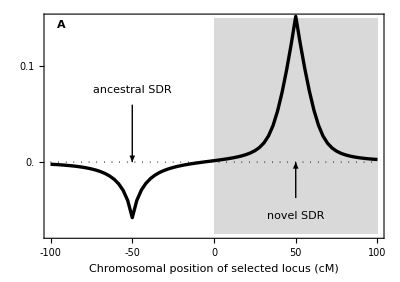

```mathematica
Clear[a]
positionplotA=
Show[

(*region of tighter linkage*)
RegionPlot[
x>0,
{x,xmin,xmax},
{y,ymin,ymax},
PlotStyle->LightGray,
BoundaryStyle->None,
AxesOrigin->{xmin,ymin},
Frame->{True,True,False,False}
],

(*neo-W into XY*)
ListPlot[
Table[
{
a,
invasionplotXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,setr[x,a,m],setR[x,a,m],setρ[x,a,m]]
},
{a,xmin,xmax,(xmax-xmin)/npoints}
],
Joined->True,
PlotRange->All,
PlotStyle->Directive[Black,Thickness[lwd]],
AxesOrigin->{xmin,ymin},
Frame->{True,True,False,False}
],

Plot[0,{x,xmin,xmax},PlotStyle->{Black, Dotted}],

FrameLabel->{"Chromosomal position of selected locus (cM)",""},
Epilog->{
Text[Style["A",Bold],Scaled@letpos],
Rotate[Text["Invasion fitness (λ_W'^(XY)-1)",Scaled@ylabpos],90 Degree],
Text["ancestral SDR",{x,ymax*0.5}],
Text["novel SDR",{m,ymin*0.75}],
Arrow[{{x,ymax*0.4},{x,0}}],
Arrow[{{m,ymin*0.5},{m,0}}]
},

plotstyle[xmin,xmax,xtickmin,xtickmax,xint,ymin,ymax,ytickmin,ytickmax,yint]
 
]
```

### Panel B - neo-W invasion fitness as function of selected locus location, with tighter linkage

#### Parameters

```mathematica
(*position of X and M loci*)
x=-5;
m=5;

(*x limits*)
xmin=-10;
xmax=10;
xtickmin=-10;
xtickmax=10;
xint = 5;
```

#### Plot

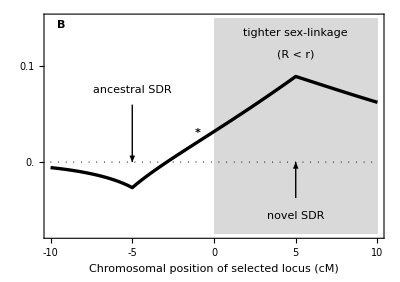

```mathematica
Clear[a]
positionplotB=
Show[

(*region of tighter linkage*)
RegionPlot[
x>0,
{x,xmin,xmax},
{y,ymin,ymax},
PlotStyle->LightGray,
BoundaryStyle->None,
AxesOrigin->{xmin,ymin},
Frame->{True,True,False,False}
],

(*neo-W into XY*)
ListPlot[
Table[
{
a,
invasionplotXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,setr[x,a,m],setR[x,a,m],setρ[x,a,m]]
},
{a,xmin,xmax,(xmax-xmin)/npoints}
],
Joined->True,
PlotRange->All,
PlotStyle->Directive[Black,Thickness[lwd]],
AxesOrigin->{xmin,ymin},
Frame->{True,True,False,False}
],

Plot[0,{x,xmin,xmax},PlotStyle->{Black, Dotted}],

FrameLabel->{"Chromosomal position of selected locus (cM)",""},
Epilog->{
Text[Style["B",Bold],Scaled@letpos],
Text["tighter sex-linkage",{m,ymax*0.9}],
Text["(R < r)",{m,ymax*0.75}],
Text["ancestral SDR",{x,ymax*0.5}],
Text["novel SDR",{m,ymin*0.75}],
Arrow[{{x,ymax*0.4},{x,0}}],
Arrow[{{m,ymin*0.5},{m,0}}],
Text[Style["*",Bold],{-1,0.03}]
},

plotstyle[xmin,xmax,xtickmin,xtickmax,xint,ymin,ymax,ytickmin,ytickmax,yint]

]
```

### Panel C - neo-W invasion fitness as function of recombination with selected locus, with inset of neo-W temporal dynamics

#### Parameters

Collect selection parameters used above

```mathematica
subpar={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

Set recombination rates

```mathematica
tryr=0.005;
tryRs={0.001,0.02,0.1,0.5};
```

```mathematica
(*x limits*)
xmin=0.0008;
xmax=0.5;
xmarks=tryRs;
```

#### Main plot

```mathematica
tab=Table[
equil=sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2+(-(λmA1 +λma1)+(χmA1+χma1))λ +(λmA1-χmA1)( λma1-χma1)-χmA1 χma1/.reverse/.pAveM->(1-q)pXm+q pYm/.subpar/.R->0.5^b/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],q->equil[[4]]})==0,λ],{b,10,1,-1/2}];
eigen1=Transpose[Join[{Table[0.5^b,{b,10,1,-1/2}]},{Transpose[tab][[1]]-1}]];
eigen2=Transpose[Join[{Table[0.5^b,{b,10,1,-1/2}]},{Transpose[tab][[2]]-1}]];
```

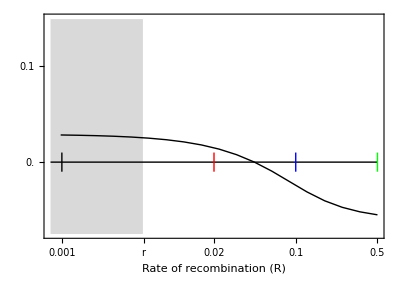

```mathematica
temp=Show[

(*region of tighter linkage*)
ListLogLinearPlot[{{xmin,ymax},{tryr,ymax}},Joined->True,PlotStyle->{White,Thin},Filling->ymin,FillingStyle->LightGray,PlotRange->{{xmin,xmax},{ymin,ymax}}],
ListLogLinearPlot[{{tryr,ymax},{tryr,ymin}},Joined->True,PlotStyle->{White,Thin}],

(*neo-W invasion fitness*)
Show[
ListLogLinearPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->All]
],

(*0 line*)
ListLogLinearPlot[{{xmin,0},{xmax,0}},Joined->True,PlotStyle->{Black}],

(*mark recombination rates used in inset*)
ListLogLinearPlot[{{0.001,-0.01},{0.001,0.01}},Joined->True,PlotStyle->{Black,Thick}],
ListLogLinearPlot[{{0.02,-0.01},{0.02,0.01}},Joined->True,PlotStyle->{Red,Thick}],
ListLogLinearPlot[{{0.1,-0.01},{0.1,0.01}},Joined->True,PlotStyle->{Blue,Thick}],
ListLogLinearPlot[{{0.5,-0.01},{0.5,0.01}},Joined->True,PlotStyle->{Green,Thick}],

FrameLabel->{"Rate of recombination (R)",""},

loglinearplotstyle[xmin,xmax,xmarks,ymin,ymax,ytickmin,ytickmax,yint,tryr]
]
```

Make sure we get the same answer with the full characteristic polynomial

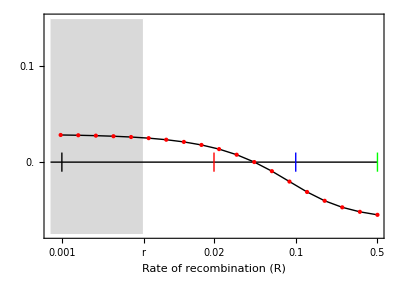

```mathematica
plot2=ListLogLinearPlot[Table[{0.5^b,invasionplotXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,0.5^b,tryr(1-0.5^b)+0.5^b(1-tryr)]},{b,10,1,-1/2}],PlotStyle->{Red},PlotRange->{{xmin,xmax},{ymin,ymax}}];
Show[temp,plot2]
```

#### Inset parameters

```mathematica
trypm=0.01;(*initial mutant frequency*)
tryk=1;(*neo-W*)
startplot=5;(*start plotting at this generation*)
endtime=5000;(*number of generations to simulate*)
modvec={0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0}; (*use to get freq of neo-W amongst females from recursion simulation output*)
```

#### Inset

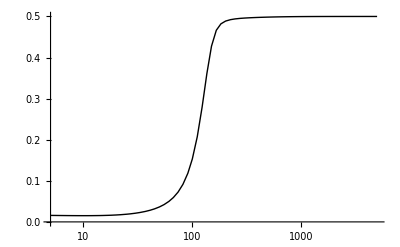

```mathematica
tryR=tryRs[[1]];
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Black=ListLogLinearPlot[MODtab1Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Black}]
```

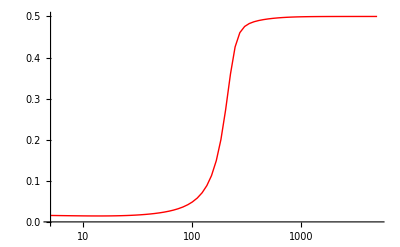

```mathematica
tryR=tryRs[[2]];
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Red=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Red=ListLogLinearPlot[MODtab1Red,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Red}]
```

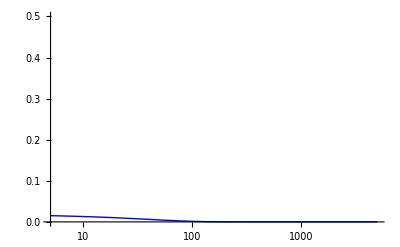

```mathematica
tryR=tryRs[[3]];
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Blue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Blue=ListLogLinearPlot[MODtab1Blue,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Blue}]
```

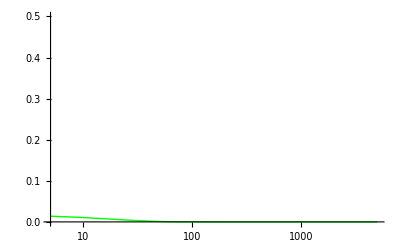

```mathematica
tryR=tryRs[[4]];
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Green=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Green=ListLogLinearPlot[MODtab1Green,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Green}]
```

#### Main plot + inset

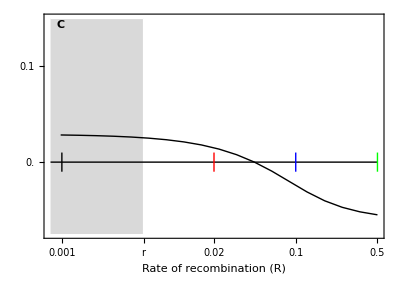

```mathematica
tempcomb=
Show[
temp,

Epilog->{
Inset[
Show[
MOD1Black,MOD1Red,MOD1Blue,MOD1Green,
FrameLabel->{"Generation","neo-W frequency"},
insetloglinearplotstyle[startplot,endtime,{10,100,1000},0,0.5,0,0.5,0.5]
],
{-0,0.15},{Right,Top},{3.6,3.6*Sqrt[2]}
],
Text[Style["C",Bold],Scaled@letpos]
}

]
```

### All panels

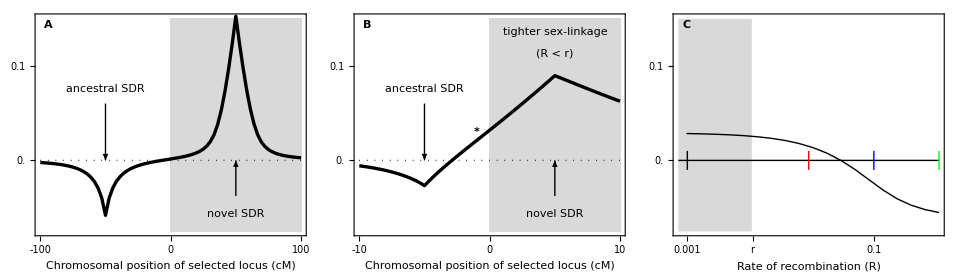

```mathematica
GraphicsRow[
{positionplotA,positionplotB,tempcomb},
Spacings->-45
]

Export[plotdir<>"PositionPlot_SexAntagTighter.eps",%//rasterTrick];
```

## Figure 3 - region plot of neo-W haplotype invasion with tight linkage and no haploid selection

### Plotting parameters

```mathematica
xmin=0;
xmax=1.5;
xtickmin=0;
xtickmax=1;
xint=1;
ymin=xmin;
ymax=xmax;
ytickmin=xtickmin;
ytickmax=xtickmax;
yint=xint;
```

### Panel A - A favoured in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
Faa->0.85,
FAA->1.05
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

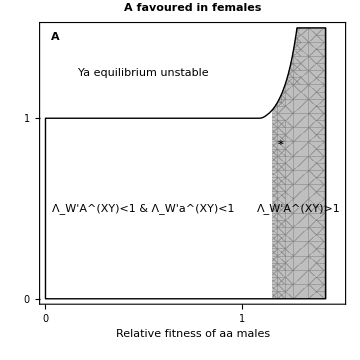

```mathematica
plotA=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

FrameLabel->{"Relative fitness of aa males",""},
Epilog->{
Text[Style["A",Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)>1"],{1.29,0.5}],
Text[Style["Λ_W'A^(XY)<1 & Λ_W'a^(XY)<1"],{0.5,0.5}],
Text[Style["Ya equilibrium unstable"],{0.5,1.25}],
Text[Style["*",Bold],{1.2,0.85}],
Rotate[Text[Style["Relative fitness of AA males"],Scaled@ylabposregion],90 Degree],
Text[Style["A favoured in females",Bold],Scaled@{0.5,1.05}]
},

regionplotstyle[xmin,xmax,xtickmin,xtickmax,xint,ymin,ymax,ytickmin,ytickmax,yint]
]
```

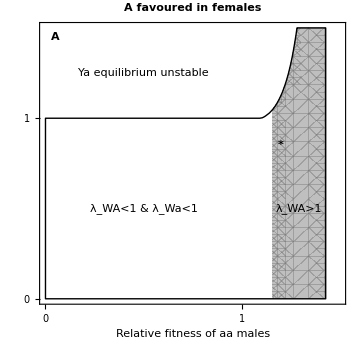

-Graphics-

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

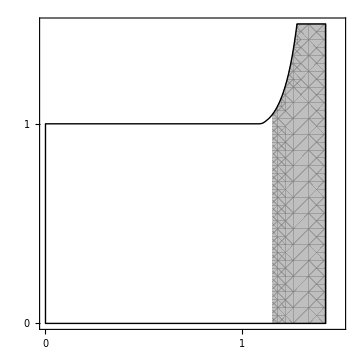

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

regionplotstyle[xmin,xmax,xtickmin,xtickmax,xint,ymin,ymax,ytickmin,ytickmax,yint]

]
```

### Panel B - a favoured in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
Faa->1.05,
FAA->0.85
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyExt/.k->1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyExt/.k->1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

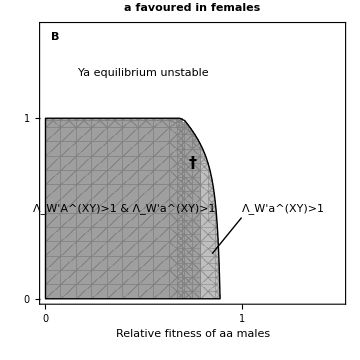

```mathematica
plotB=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

Graphics[{Thick,Black,Line[{{0.85,0.25},{1,0.45}}]}],

FrameLabel->{"Relative fitness of aa males",""},
Epilog->{
Text[Style["B",Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'a^(XY)>1"],{1,0.5},{-1,0}],
Text[Style["Λ_W'A^(XY)>1 & Λ_W'a^(XY)>1"],{0.4,0.5}],
Text[Style["Ya equilibrium unstable"],{0.5,1.25}],
Text[Style["†",16,Bold],{0.75,0.75}],
Text[Style["a favoured in females",Bold],Scaled@{0.5,1.05}]
},

regionplotstyle[xmin,xmax,xtickmin,xtickmax,xint,ymin,ymax,ytickmin,ytickmax,yint]

]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

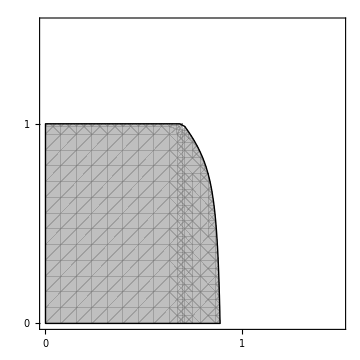

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

regionplotstyle[xmin,xmax,xtickmin,xtickmax,xint,ymin,ymax,ytickmin,ytickmax,yint]

]
```

### Panel C - overdominance in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
Faa->0.6,
FAA->0.6
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyExt/.k->1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyExt/.k->1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

#### Plots

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

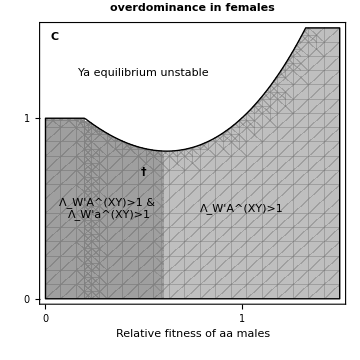

```mathematica
plotC=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

FrameLabel->{"Relative fitness of aa males",""},
Epilog->{
Text[Style["C",Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)>1"],{1,0.5}],
Text[Style["Λ_W'A^(XY)>1 & 
Λ_W'a^(XY)>1"],{0.325,0.5}],
Text[Style["Ya equilibrium unstable"],{0.5,1.25}],
Text[Style["†",Bold],{0.5,0.7}],
Text[Style["overdominance in females",Bold],Scaled@{0.5,1.05}]
},

regionplotstyle[xmin,xmax,xtickmin,xtickmax,xint,ymin,ymax,ytickmin,ytickmax,yint]

]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

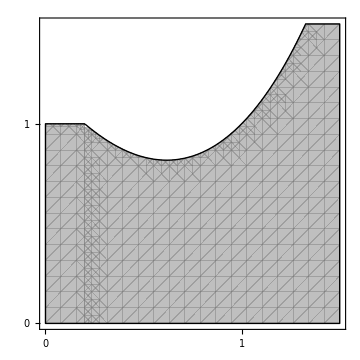

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

regionplotstyle[xmin,xmax,xtickmin,xtickmax,xint,ymin,ymax,ytickmin,ytickmax,yint]

]
```

### All panels

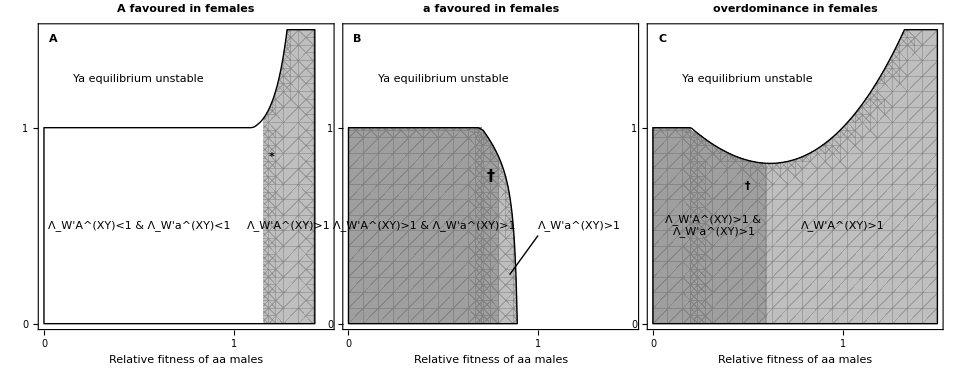

```mathematica
GraphicsRow[
{plotA,plotB,plotC},
Spacings->-45
]

Export[plotdir<>"Region_plot_combined.eps",%//rasterTrick];
```

## Figure 4 - plot of neo-W invasion fitness as function of selected locus location, with haploid selection

### Plotting parameters

```mathematica
Pad={{40,20},{50,30}};  (*space around plot*)
xplotmin=-50;
xplotmax=50;
xplotinterval=25;
yplotmin=-0.04;
yplotmax=0.07;
yplotinterval=0.02;
npoints=20;
ylabpos={-0.1,0.5};  (*relative location of y axis label position*)
```

### Panel A - meiotic drive in males

#### Parameters

```mathematica
x=-25;
m=25;

trysAf=0.1;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.1;
tryt=0;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
trywAm=1+tryt;
trywam=1;
trywAf=1;
trywaf=1;
tryαm=0.45;
tryαf=0.5;
```

#### Plot

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

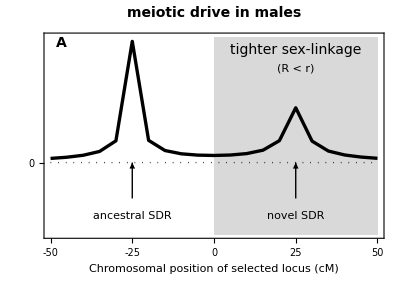

```mathematica
plotA=
Show[

(*region of tighter linkage*)
RegionPlot[x>0,{x,xplotmin,xplotmax},{y,yplotmin,yplotmax},
PlotStyle->{LightGray},
BoundaryStyle->None,
Frame->{True,True,False,False}
],

(*neo-W into XY*)
ListPlot[Table[{a,invasionplotXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,setr[x,a,m],setR[x,a,m],setρ[x,a,m]]},{a,xplotmin,xplotmax,(xplotmax-xplotmin)/npoints}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Black,Thickness[lwd]]
],

Plot[0,{x,xplotmin,xplotmax},PlotStyle->{Black, Dotted}],

PlotRange->{{xplotmin,xplotmax},{yplotmin,yplotmax}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,0,0,0}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Chromosomal position of selected locus (cM)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@letpos],
Rotate[Text[Style["Invasion fitness (λ_W'^(XY)-1)",14],Scaled@ylabpos],90 Degree],
Text[Style["tighter sex-linkage",14],{25,yplotmax*0.9}],
Text["(R < r)",{25,yplotmax*0.75}],
Text[Style["meiotic drive in males",14,Bold],(*{xplotmax,yplotmin*0.75}*)Scaled@{0.5,1.1},{0,0}],
Text["ancestral SDR",{-25,yplotmin*0.75}],
Text["novel SDR",{25,yplotmin*0.75}],
Arrow[{{-25,yplotmin*0.5},{-25,0}}],
Arrow[{{25,yplotmin*0.5},{25,0}}]
},
PlotRangeClipping->False

]
```

### Panel B - haploid competition in males

#### Parameters

```mathematica
x=-25;
m=25;

trysAf=0.05;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
trywAm=1+tryt;
trywam=1;
trywAf=1;
trywaf=1;
tryαm=0.5;
tryαf=0.5;
```

#### Plot

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

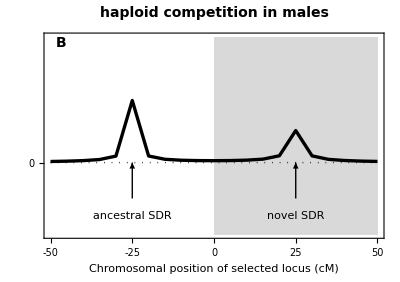

```mathematica
plotB=
Show[

(*region of tighter linkage*)
RegionPlot[x>0,{x,xplotmin,xplotmax},{y,yplotmin,yplotmax},
PlotStyle->{LightGray},
BoundaryStyle->None,
Frame->{True,True,False,False}
],

(*neo-W into XY*)
ListPlot[Table[{a,invasionplotXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,setr[x,a,m],setR[x,a,m],setρ[x,a,m]]},{a,xplotmin,xplotmax,(xplotmax-xplotmin)/npoints}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Black,Thickness[lwd]]
],

Plot[0,{x,xplotmin,xplotmax},PlotStyle->{Black, Dotted}],

PlotRange->{{xplotmin,xplotmax},{yplotmin,yplotmax}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,0,0,0}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Chromosomal position of selected locus (cM)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@letpos],
(*Rotate[Text[Style["Invasion fitness (λ-1)",14],Scaled@ylabpos],90 Degree],*)
Text[Style["haploid competition in males",14,Bold],(*{xplotmax,yplotmin*0.75}*)Scaled@{0.5,1.1},{0,0}],
Text["ancestral SDR",{-25,yplotmin*0.75}],
Text["novel SDR",{25,yplotmin*0.75}],
Arrow[{{-25,yplotmin*0.5},{-25,0}}],
Arrow[{{25,yplotmin*0.5},{25,0}}]
},
PlotRangeClipping->False

]
```

### All panels

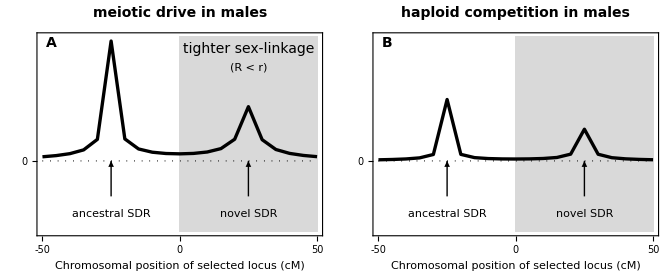

```mathematica
GraphicsRow[
{plotA,plotB},
Spacings->-30
]

Export[plotdir<>"PositionPlot.eps",%//rasterTrick];
```

## Figure 5 - sex ratio is not a good predictor of neo-SD invasion

### Parameters

#### Plotting parameters

```mathematica
yplotmin=-0.075;
yplotmax=0.15;
yplotinterval=0.02;
```

```mathematica
Pad={{50,20},{40,30}};  (*space around plot*)
letpos={.05,.93};  (*relative location of letter, eg A, in figure*)
ylabpos={-0.175,0.5};  (*relative location of y axis label position*)

inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xsize=5inches;
aspectratio=1/Sqrt[2];
```

#### Extra parameters

```mathematica
modvec={0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0};
```

```mathematica
loglinearplotINVoptions={Frame->{{True,False},{True,False}}, 
PlotRangeClipping->False,
ImagePadding->Pad,
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{5,5,{0,0.01}},{10,10,{0,0.01}},{100,100,{0,0.01}},{1000,1000,{0,0.01}}},Table[{y,y,ticksize},{y,0,0.5,0.25}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
Axes->True};
```

```mathematica
loglinearplotINVSRoptions={Frame->{{True,False},{True,False}}, 
PlotRangeClipping->False,
ImagePadding->Pad,
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{5,5,{0,0.01}},{10,10,{0,0.01}},{50,50,{0,0.01}},{100,100,{0,0.01}},{500,500,{0,0.01}},{1000,1000,{0,0.01}}},Table[{y,y,ticksize},{y,0.4,0.6,0.1}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
Axes->True};
```

```mathematica
startplot=5;
endtime=1000;
tryR=0;
trypm=0.01;
tryk=1;
```

### Panel A - neo-W invading XY

#### Parameters

```mathematica
trys=0.2;
tryh=0.7;
tryαDm=-0.1;
tryFAA=1+trys ;
tryFAa=1+trys tryh;
tryFaa=1;
tryMAA=1+trys;
tryMAa=1+trys tryh;
tryMaa=1;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5+tryαDm;
tryr=0.02;
subpar1={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

#### Plots

```mathematica
tryR=0.001;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODBlack=ListLogLinearPlot[MODtab2Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Black},loglinearplotINVoptions];
SRtabBlack=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRBlack=ListLogLinearPlot[SRtabBlack,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Black,Thick},loglinearplotINVSRoptions];
```

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabRed=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODRed=ListLogLinearPlot[MODtabRed,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Red},loglinearplotINVoptions];
SRtabRed=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRRed=ListLogLinearPlot[SRtabRed,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Red,Thick},loglinearplotINVSRoptions];
```

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabBlue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODBlue=ListLogLinearPlot[MODtabBlue,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Blue},loglinearplotINVoptions];
SRtabBlue=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRBlue=ListLogLinearPlot[SRtabBlue,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Blue,Thick},loglinearplotINVSRoptions];
```

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabGreen=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODGreen=ListLogLinearPlot[MODtabGreen,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Green},loglinearplotINVoptions];
SRtabGreen=Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRGreen=ListLogLinearPlot[SRtabGreen,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Green,Thick},loglinearplotINVSRoptions];
```

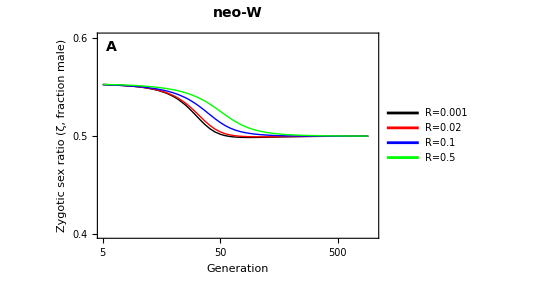

```mathematica
plotA=Legended[Show[SRBlack,SRRed,SRBlue,SRGreen,
ImagePadding->Pad,
FrameLabel->{{Style["Zygotic sex ratio (ζ, fraction male)",FontSize->14],""},{Style["Generation",FontSize->14],""}},
Epilog->{Inset[Show[MODBlack,MODRed,MODBlue,MODGreen,(*ImageSize->150,*)BaseStyle->{TextStyle->Bold,FontFamily->"Helvetica",FontSize->8},
FrameLabel->{{Style["neo-W frequency",FontSize->8],""},{Style["",FontSize->14],""}}],Scaled@{1,-0.14},{Right,Bottom},{3,3*Sqrt[2]}],
Text[Style["A",14,Bold],Scaled@letpos],
Text[Style["neo-W",Bold,14],Scaled@{0.5,1.1}]}],
Placed[
LineLegend[
{Directive[Thickness[0.1],Black],
Directive[Thickness[0.1],Red],
Directive[Thickness[0.1],Blue],
Directive[Thickness[0.1],Green]
},
{Style["R=0.001",14],
Style["R=0.02",14],
Style["R=0.1",14],
Style["R=0.5",14]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
Scaled@{0.825,0.85}
]
]
```

### Panel B - neo-Y invading ZW

#### Parameters

Here we are going to adjust the fitness parameters only to change definition of sex.
Also have to adjust sex ratio to 1-sexratio because it gives the frequency of the ancestrally heterozygous sex.

```mathematica
trys=0.2;
tryh=0.7;
tryαDm=-0.1;
tryFAA=1+trys ;
tryFAa=1+trys tryh;
tryFaa=1;
tryMAA=1+trys;
tryMAa=1+trys tryh;
tryMaa=1;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5+tryαDm;
tryαm=0.5;
tryr=0.02;
subpar1={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

#### Plots

```mathematica
tryR=0.001;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODBlack=ListLogLinearPlot[MODtab2Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.6}},PlotStyle->{Black},loglinearplotINVoptions];
SRtabBlack=Table[{Round[Exp[exptime]],1-sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRBlack=ListLogLinearPlot[SRtabBlack,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Black,Thick},loglinearplotINVSRoptions];
```

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabRed=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODRed=ListLogLinearPlot[MODtabRed,Joined->True,PlotRange->{{startplot,endtime},{0,0.6}},PlotStyle->{Red},loglinearplotINVoptions];
SRtabRed=Table[{Round[Exp[exptime]],1-sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRRed=ListLogLinearPlot[SRtabRed,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Red,Thick},loglinearplotINVSRoptions];
```

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabBlue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODBlue=ListLogLinearPlot[MODtabBlue,Joined->True,PlotRange->{{startplot,endtime},{0,0.6}},PlotStyle->{Blue},loglinearplotINVoptions];
SRtabBlue=Table[{Round[Exp[exptime]],1-sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRBlue=ListLogLinearPlot[SRtabBlue,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Blue,Thick},loglinearplotINVSRoptions];
```

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtabGreen=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MODGreen=ListLogLinearPlot[MODtabGreen,Joined->True,PlotRange->{{startplot,endtime},{0,0.6}},PlotStyle->{Green},loglinearplotINVoptions];
SRtabGreen=Table[{Round[Exp[exptime]],1-sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
SRGreen=ListLogLinearPlot[SRtabGreen,Joined->True,PlotRange->{{startplot,endtime},{0.4,0.601}},PlotStyle->{Green,Thick},loglinearplotINVSRoptions];
```

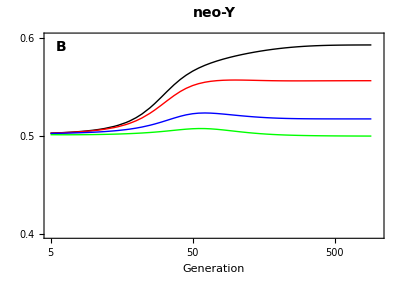

```mathematica
plotB=Show[SRBlack,SRRed,SRBlue,SRGreen,
ImagePadding->Pad,
FrameLabel->{{Style["",FontSize->14],""},{Style["Generation",FontSize->14],""}},
Epilog->{Inset[Show[MODBlack,MODRed,MODBlue,MODGreen,(*ImageSize->150,*)BaseStyle->{TextStyle->Bold,FontFamily->"Helvetica",FontSize->8},
FrameLabel->{{Style["neo-Y frequency",FontSize->8],""},{Style["",FontSize->14],""}}],
Scaled@{1,-0.14},{Right,Bottom},{3,3*Sqrt[2]}],
Text[Style["B",14,Bold],Scaled@letpos],
Text[Style["neo-Y",Bold,14],Scaled@{0.5,1.1}]}
]
```

### All panels

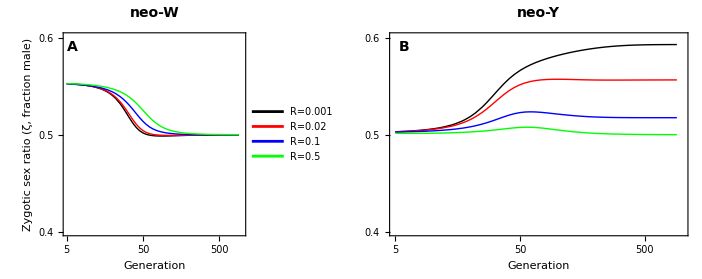

```mathematica
GraphicsRow[{plotA,plotB},Spacings->-15]

Export[plotdir<>"Temporal_SR.eps",%//rasterTrick];
```

## Figure S.1 - neo-W invasion fitness as a function of the position of the selected locus with overdominance in males, no haploid selection

### Plotting parameters

```mathematica
Pad={{40,20},{50,20}};  (*space around plot*)
yplotmin=-0.075;
yplotmax=0.15;
yplotinterval=0.02;
ylabpos={-0.13,0.5};  (*relative location of y axis label position*)
```

### Panel A - loose linkage; overdominance in males and directional selection for a in females

#### Parameters

```mathematica
x=-25;
m=25;

tryt=0;
tryFAA=0.85;
tryFAa=1;
tryFaa=1.05;
tryMAA=0.75;
tryMAa=1;
tryMaa=0.75;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;

xplotmin=-50;
xplotmax=50;
xplotinterval=25;
npoints=32;
```

#### Plot

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 2 of {{0.0283897, 0.0313209, 0.959256, 0.5}} does not exist.

Part::partw: Part 2 of {{0.0213283, 0.0235138, 0.969581, 0.5}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

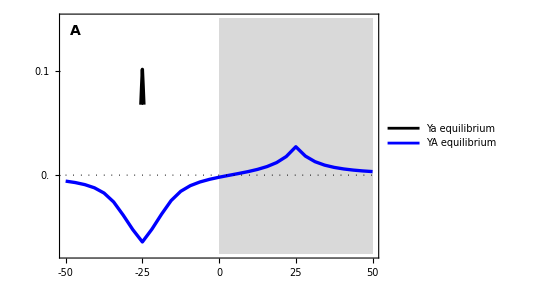

```mathematica
positionplotA=
Legended[
Show[

(*region of tighter linkage*)
RegionPlot[x>0,{x,xplotmin,xplotmax},{y,yplotmin,yplotmax},
PlotStyle->{LightGray},
BoundaryStyle->None,
PlotRange->{yplotmin,yplotmax},
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

(*neo-W into XY*)
ListPlot[Table[{a,invasionplotXY2[{tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryFA,tryFa,tryMA,tryMa,tryFdA,tryMdA,setr[x,a,m],setR[x,a,m],setρ[x,a,m]},sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryFA,tryFa,tryMA,tryMa,tryFdA,tryMdA,setr[x,a,m]][[1]]]},{a,xplotmin,xplotmax,(xplotmax-xplotmin)/npoints}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Blue,Thickness[lwd]],
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],
ListPlot[Table[{a,invasionplotXY2[{tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryFA,tryFa,tryMA,tryMa,tryFdA,tryMdA,setr[x,a,m],setR[x,a,m],setρ[x,a,m]},sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryFA,tryFa,tryMA,tryMa,tryFdA,tryMdA,setr[x,a,m]][[2]]]},{a,-26,-24,0.25}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Black,Thickness[lwd]],
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

Plot[0,{x,xplotmin,xplotmax},PlotStyle->{Black, Dotted}],

PlotRange->{{xplotmin,xplotmax},{yplotmin,yplotmax}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,-0.1,0.1,0.1}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@letpos],
Rotate[Text[Style["Invasion fitness (λ_W'^(XY)-1)""",14],Scaled@ylabpos],90 Degree]
},
PlotRangeClipping->False
],
Placed[
LineLegend[
{Directive[Thickness[0.1],Black],
Directive[Thickness[0.1],Blue]
},
{Style["Ya equilibrium",14],
Style["YA equilibrium",14]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
Scaled@{0.7,0.75}
]
]
```

### Panel B - tight linkage; overdominance in males and directional selection for a in females

#### Parameters

```mathematica
x=-5;
m=5;

tryt=0;
tryFAA=0.85;
tryFAa=1;
tryFaa=1.05;
tryMAA=0.75;
tryMAa=1;
tryMaa=0.75;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;

xplotmin=-10;
xplotmax=10;
xplotinterval=5;
npoints=32;
```

#### Plot

Part::partw: Part 2 of {{0.0283897, 0.0313209, 0.959256, 0.5}} does not exist.

Part::partw: Part 2 of {{0.0213283, 0.0235138, 0.969581, 0.5}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

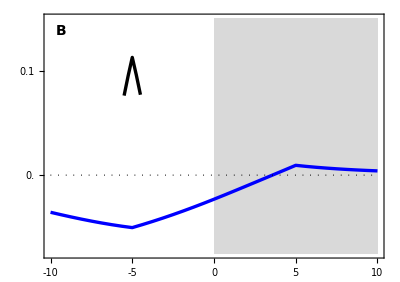

```mathematica
positionplotB=
(*Legended[*)
Show[

(*region of tighter linkage*)
RegionPlot[x>0,{x,xplotmin,xplotmax},{y,yplotmin,yplotmax},
PlotStyle->{LightGray},
BoundaryStyle->None,
PlotRange->{yplotmin,yplotmax},
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

(*neo-W into XY*)
ListPlot[Table[{a,invasionplotXY2[{tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryFA,tryFa,tryMA,tryMa,tryFdA,tryMdA,setr[x,a,m],setR[x,a,m],setρ[x,a,m]},sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryFA,tryFa,tryMA,tryMa,tryFdA,tryMdA,setr[x,a,m]][[1]]]},{a,xplotmin,xplotmax,(xplotmax-xplotmin)/npoints}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Blue,Thickness[lwd]],
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],
ListPlot[Table[{a,invasionplotXY2[{tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryFA,tryFa,tryMA,tryMa,tryFdA,tryMdA,setr[x,a,m],setR[x,a,m],setρ[x,a,m]},sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryFA,tryFa,tryMA,tryMa,tryFdA,tryMdA,setr[x,a,m]][[2]]]},{a,-6,-4,0.25}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Black,Thickness[lwd]],
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

Plot[0,{x,xplotmin,xplotmax},PlotStyle->{Black, Dotted}],

PlotRange->{{xplotmin,xplotmax},{yplotmin,yplotmax}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,-0.1,0.1,0.1}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@letpos]
},
PlotRangeClipping->False
](*,
Placed[
LineLegend[
{Directive[Thickness[0.005],Black],
Directive[Thickness[0.005],Blue]
},
{Style["Ya equilibrium",16],
Style["YA equilibrium",16]
},
(*LegendFunction->"Frame",*)
LegendLayout->"Column"
],
Scaled@{0.72,0.65}
]
]*)
```

### Panel C - loose linkage; overdominance in both sexes

#### Parameters

```mathematica
x=-25;
m=25;

tryt=0;
tryFAA=0.6;
tryFAa=1;
tryFaa=0.6;
tryMAA=0.7;
tryMAa=1;
tryMaa=0.5;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;

xplotmin=-50;
xplotmax=50;
xplotinterval=25;
npoints=36;
```

#### Plot

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Part::partw: Part 2 of {{0.40879, 0.351282, 0.936149, 0.5}} does not exist.

Part::partw: Part 2 of {{0.404106, 0.344002, 0.944328, 0.5}} does not exist.

Part::partw: Part 2 of {{0.399301, 0.336588, 0.952469, 0.5}} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

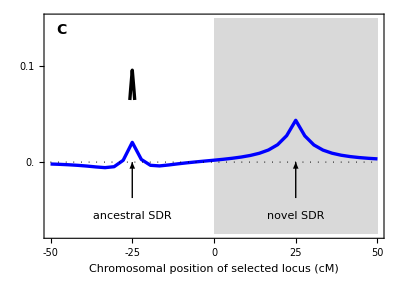

```mathematica
positionplotC=
Show[

(*region of tighter linkage*)
RegionPlot[x>0,{x,xplotmin,xplotmax},{y,yplotmin,yplotmax},
PlotStyle->{LightGray},
BoundaryStyle->None,
PlotRange->{yplotmin,yplotmax},
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

(*neo-W into XY*)
ListPlot[Table[{a,invasionplotXY2[{tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryFA,tryFa,tryMA,tryMa,tryFdA,tryMdA,setr[x,a,m],setR[x,a,m],setρ[x,a,m]},sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryFA,tryFa,tryMA,tryMa,tryFdA,tryMdA,setr[x,a,m]][[1]]]},{a,xplotmin,xplotmax,(xplotmax-xplotmin)/npoints}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Blue,Thickness[lwd]],
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],
ListPlot[Table[{a,invasionplotXY2[{tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryFA,tryFa,tryMA,tryMa,tryFdA,tryMdA,setr[x,a,m],setR[x,a,m],setρ[x,a,m]},sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryFA,tryFa,tryMA,tryMa,tryFdA,tryMdA,setr[x,a,m]][[2]]]},{a,-27,-23,0.25}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Black,Thickness[lwd]],
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

Plot[0,{x,xplotmin,xplotmax},PlotStyle->{Black, Dotted}],

PlotRange->{{xplotmin,xplotmax},{yplotmin,yplotmax}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,-0.1,0.1,0.1}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Chromosomal position of selected locus (cM)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["C",14,Bold],Scaled@letpos],
Rotate[Text[Style["Invasion fitness (λ_W'^(XY)-1)",14],Scaled@ylabpos],90 Degree]
(*,Text[Style["tighter sex-linkage",14],{m,yplotmax*0.9}],*)
,Text["ancestral SDR",{x,yplotmin*0.75}],
Text["novel SDR",{m,yplotmin*0.75}],
Arrow[{{x,yplotmin*0.5},{x,0}}],
Arrow[{{m,yplotmin*0.5},{m,0}}]
},
PlotRangeClipping->False

]
```

### Panel D - tight linkage and overdominance in both sexes

#### Parameters

```mathematica
x=-5;
m=5;

tryt=0;
tryFAA=0.6;
tryFAa=1;
tryFaa=0.6;
tryMAA=0.7;
tryMAa=1;
tryMaa=0.5;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;

xplotmin=-10;
xplotmax=10;
xplotinterval=5;
npoints=36;
```

#### Plot

Part::partw: Part 2 of {{0.389312, 0.321357, 0.968596, 0.5}} does not exist.

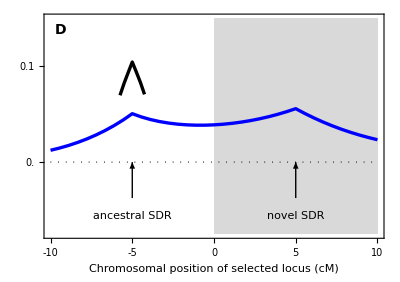

```mathematica
positionplotD=
Show[

(*region of tighter linkage*)
RegionPlot[x>0,{x,xplotmin,xplotmax},{y,yplotmin,yplotmax},
PlotStyle->{LightGray},
BoundaryStyle->None,
PlotRange->{yplotmin,yplotmax},
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

(*neo-W into XY*)
ListPlot[Table[{a,invasionplotXY2[{tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryFA,tryFa,tryMA,tryMa,tryFdA,tryMdA,setr[x,a,m],setR[x,a,m],setρ[x,a,m]},sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryFA,tryFa,tryMA,tryMa,tryFdA,tryMdA,setr[x,a,m]][[1]]]},{a,xplotmin,xplotmax,(xplotmax-xplotmin)/npoints}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Blue,Thickness[lwd]],
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],
ListPlot[Table[{a,invasionplotXY2[{tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryFA,tryFa,tryMA,tryMa,tryFdA,tryMdA,setr[x,a,m],setR[x,a,m],setρ[x,a,m]},sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryFA,tryFa,tryMA,tryMa,tryFdA,tryMdA,setr[x,a,m]][[2]]]},{a,-6,-4,0.25}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Black,Thickness[lwd]],
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

Plot[0,{x,xplotmin,xplotmax},PlotStyle->{Black, Dotted}],

PlotRange->{{xplotmin,xplotmax},{yplotmin,yplotmax}},
ImagePadding->Pad,
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,-0.1,0.1,0.1}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Chromosomal position of selected locus (cM)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
Epilog->{
Text[Style["D",14,Bold],Scaled@letpos],
(*Rotate[Text[Style["Invasion fitness (λ-1)",14],Scaled@ylabpos],90 Degree],
Text[Style["tighter sex-linkage",14],{m,yplotmax*0.9}],*)
Text["ancestral SDR",{x,yplotmin*0.75}],
Text["novel SDR",{m,yplotmin*0.75}],
Arrow[{{x,yplotmin*0.5},{x,0}}],
Arrow[{{m,yplotmin*0.5},{m,0}}]
},
PlotRangeClipping->False

]
```

```mathematica
?ImagePadding
```

ImagePadding is an option for graphics functions that specifies what absolute extra padding should be left for extended objects such as thick lines and annotations such as tick and axis labels.

### Combined

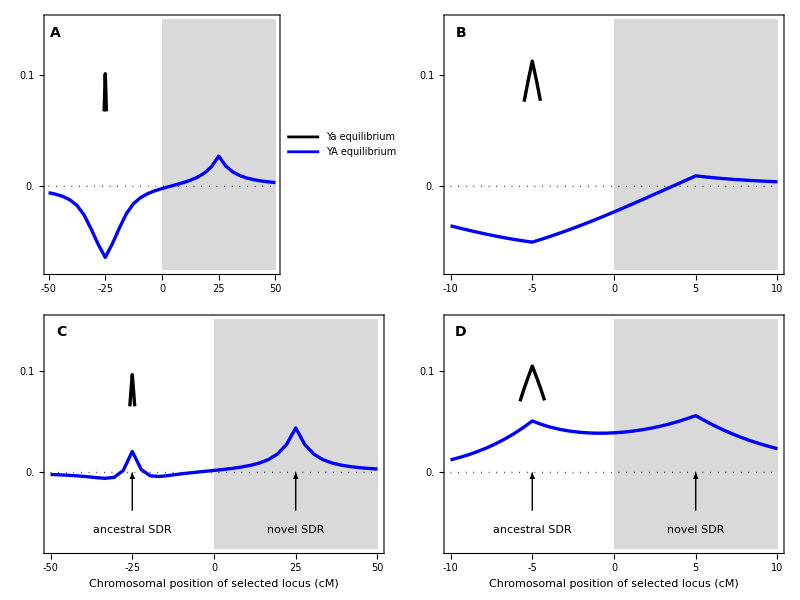

```mathematica
GraphicsGrid[{{positionplotA,positionplotB},{positionplotC,positionplotD}},Spacings->{-40,-20},
Epilog->{
Rotate[Text[Style["overdominance in males",14,Bold,FontFamily->"Helvetica"],Scaled@{1.5,1.05}],-π/2],
Rotate[Text[Style["overdominance in both sexes",14,Bold,FontFamily->"Helvetica"],Scaled@{1.5,0.1}],-π/2],
Rotate[Text[Style["loose linkage",14,Bold,FontFamily->"Helvetica"],Scaled@{0.05,1.475}],0],
Rotate[Text[Style["tight linkage",14,Bold,FontFamily->"Helvetica"],Scaled@{1.05,1.475}],0]
}
]

Export[plotdir<>"PositionPlot_Overdominance.eps",%//rasterTrick];
```

## Figure S.2 - neo-W invasion dynamics for tight linkage (r ~ 0) with overdominance in males, no haploid selection

### Plotting parameters

```mathematica
Pad={{50,20},{50,30}};  (*space around plot*)
yplotmin=-0.075;
yplotmax=0.15;
yplotinterval=0.02;
ylabpos={-0.13,0.5};  (*relative location of y axis label position*)
```

### Parameters

```mathematica
tryFAA2 = 0.85;
tryFAa2 = 1;
tryFaa2 = 1.05;
tryMAA2 = 0.75;
tryMAa2 = 1;
tryMaa2 = 0.75;
trywAf2 = 1;
trywaf2 = 1;
trywAm2 = 1;
trywam2 = 1;
tryαf2 = 0.5;
tryαm2 = 0.5;
tryr2 = 0.005;
tryR2 = 0;
subpar2 = {FAA -> tryFAA2, FAa -> tryFAa2, Faa -> tryFaa2, MAA -> tryMAA2, MAa -> tryMAa2, Maa -> tryMaa2, wAf -> trywAf2, waf -> trywaf2, wAm -> trywAm2, wam -> trywam2, αf -> tryαf2, αm -> tryαm2};

tryFAA3 = 0.6;
tryFAa3 = 1;
tryFaa3 = 0.6;
tryMAA3 = 0.7;
tryMAa3 = 1;
tryMaa3 = 0.5;
trywAf3 = 1;
trywaf3 = 1;
trywAm3 = 1;
trywam3 = 1;
tryαf3 = 0.5;
tryαm3 = 0.5;
tryr3 = 0.005;
tryR3 = 0;
subpar3 = {FAA -> tryFAA3, FAa -> tryFAa3, Faa -> tryFaa3, MAA -> tryMAA3, MAa -> tryMAa3, Maa -> tryMaa3, wAf -> trywAf3, waf -> trywaf3, wAm -> trywAm3, wam -> trywam3, αf -> tryαf3, αm -> tryαm3};
```

### Extra parameters

```mathematica
modvec={0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0};
```

```mathematica
loglinearplotINVoptions={Frame->{{True,False},{True,False}}, 
PlotRangeClipping->False,
ImagePadding->Pad,
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{5,5,{0,0.01}},{10,10,{0,0.01}},{50,50,{0,0.01}},{100,100,{0,0.01}},{500,500,{0,0.01}},{1000,1000,{0,0.01}},{5000,5000,{0,0.01}}},Table[{y,y,ticksize},{y,0,0.5,0.25}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
Axes->True};
```

```mathematica
startplot=5;
endtime=5000;
tryR=0;
trypm=0.01;
tryk=1;
```

### Panel A - a favoured in females, r = 0

```mathematica
tryr2=0;
```

```mathematica
tryR=0.001;
param={tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2,tryR,tryr2 (1-tryR)+tryR (1-tryr2),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Blackr0=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD2Blackr0=ListLogLinearPlot[MODtab2Blackr0,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Black,Thick},loglinearplotINVoptions];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
tryR=0.02;
param={tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2,tryR,tryr2 (1-tryR)+tryR (1-tryr2),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Redr0=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD2Redr0=ListLogLinearPlot[MODtab2Redr0,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Red,Thick},loglinearplotINVoptions];
```

```mathematica
tryR=0.1;
param={tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2,tryR,tryr2 (1-tryR)+tryR (1-tryr2),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Bluer0=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD2Bluer0=ListLogLinearPlot[MODtab2Bluer0,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Blue,Thick},loglinearplotINVoptions];
```

```mathematica
tryR=0.5;
param={tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2,tryR,tryr2 (1-tryR)+tryR (1-tryr2),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Greenr0=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD2Greenr0=ListLogLinearPlot[MODtab2Greenr0,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Green,Thick},loglinearplotINVoptions];
```

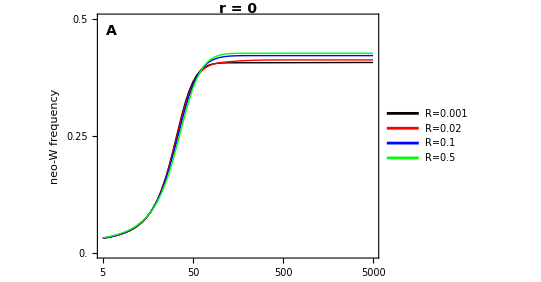

```mathematica
partA=Legended[Show[MOD2Blackr0,MOD2Redr0,MOD2Bluer0,MOD2Greenr0,
FrameLabel->{{Style["neo-W frequency",FontSize->14],""},{Style["",FontSize->14],""}},
Epilog->{
Text[Style["A",14,Bold],Scaled@letpos],
Text[Style["r = 0",14,Bold],Scaled@{0.5,1.02}]
}],
Placed[
LineLegend[
{Directive[Thickness[0.1],Black],
Directive[Thickness[0.1],Red],
Directive[Thickness[0.1],Blue],
Directive[Thickness[0.1],Green]
},
{Style["R=0.001",14],
Style["R=0.02",14],
Style["R=0.1",14],
Style["R=0.5",14]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
Scaled@{0.825,0.4}
]
]
```

### Panel B - a favoured in females, r = 0.005

```mathematica
tryr2=0.005;
```

```mathematica
tryR=0.001;
param={tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2,tryR,tryr2 (1-tryR)+tryR (1-tryr2),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD2Black=ListLogLinearPlot[MODtab2Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Black,Thick},loglinearplotINVoptions];
```

```mathematica
tryR=0.02;
param={tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2,tryR,tryr2 (1-tryR)+tryR (1-tryr2),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Red=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD2Red=ListLogLinearPlot[MODtab2Red,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Red,Thick},loglinearplotINVoptions];
```

```mathematica
tryR=0.1;
param={tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2,tryR,tryr2 (1-tryR)+tryR (1-tryr2),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Blue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD2Blue=ListLogLinearPlot[MODtab2Blue,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Blue,Thick},loglinearplotINVoptions];
```

```mathematica
tryR=0.5;
param={tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2,tryR,tryr2 (1-tryR)+tryR (1-tryr2),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA2,tryFAa2,tryFaa2,tryMAA2,tryMAa2,tryMaa2,trywAf2,trywaf2,trywAm2,trywam2,tryαf2,tryαm2,tryr2][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab2Green=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD2Green=ListLogLinearPlot[MODtab2Green,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Green,Thick},loglinearplotINVoptions];
```

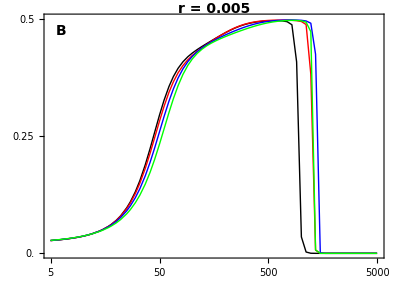

```mathematica
partB=Show[MOD2Black,MOD2Red,MOD2Blue,MOD2Green,
(*FrameLabel->{{Style["neo-W frequency",FontSize->14],""},{Style["Generation",FontSize->14],""}},*)
Epilog->{
Text[Style["B",14,Bold],Scaled@letpos],
Text[Style["r = 0.005",14,Bold],Scaled@{0.5,1.02}]
}]
```

### Panel C - overdominance in females, r = 0

```mathematica
tryr3=0;
```

```mathematica
tryR=0.001;
param={tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3,tryR,tryr3 (1-tryR)+tryR (1-tryr3),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab3Blackr0=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD3Blackr0=ListLogLinearPlot[MODtab3Blackr0,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Black,Thick},loglinearplotINVoptions];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
tryR=0.02;
param={tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3,tryR,tryr3 (1-tryR)+tryR (1-tryr3),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab3Redr0=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD3Redr0=ListLogLinearPlot[MODtab3Redr0,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Red,Thick},loglinearplotINVoptions];
```

```mathematica
tryR=0.1;
param={tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3,tryR,tryr3 (1-tryR)+tryR (1-tryr3),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab3Bluer0=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD3Bluer0=ListLogLinearPlot[MODtab3Bluer0,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Blue,Thick},loglinearplotINVoptions];
```

```mathematica
tryR=0.5;
param={tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3,tryR,tryr3 (1-tryR)+tryR (1-tryr3),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab3Greenr0=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD3Greenr0=ListLogLinearPlot[MODtab3Greenr0,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Green,Thick},loglinearplotINVoptions];
```

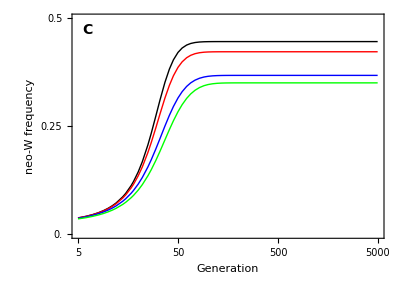

```mathematica
partC=Show[MOD3Blackr0,MOD3Redr0,MOD3Bluer0,MOD3Greenr0,
FrameLabel->{{Style["neo-W frequency",FontSize->14],""},{Style["Generation",FontSize->14],""}},
Epilog->{
Text[Style["C",14,Bold],Scaled@letpos](*,
Text[Style["r=0",14,Bold],Scaled@{0.5,1.02}]*)
}]
```

### Panel D - overdominance in females, r = 0.005

```mathematica
tryr3=0.005;
```

```mathematica
tryR=0.001;
param={tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3,tryR,tryr3 (1-tryR)+tryR (1-tryr3),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab3Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD3Black=ListLogLinearPlot[MODtab3Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Black,Thick},loglinearplotINVoptions];
```

```mathematica
tryR=0.02;
param={tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3,tryR,tryr3 (1-tryR)+tryR (1-tryr3),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab3Red=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD3Red=ListLogLinearPlot[MODtab3Red,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Red,Thick},loglinearplotINVoptions];
```

```mathematica
tryR=0.1;
param={tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3,tryR,tryr3 (1-tryR)+tryR (1-tryr3),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab3Blue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD3Blue=ListLogLinearPlot[MODtab3Blue,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Blue,Thick},loglinearplotINVoptions];
```

```mathematica
tryR=0.5;
param={tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3,tryR,tryr3 (1-tryR)+tryR (1-tryr3),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA3,tryFAa3,tryFaa3,tryMAA3,tryMAa3,tryMaa3,trywAf3,trywaf3,trywAm3,trywam3,tryαf3,tryαm3,tryr3][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab3Green=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD3Green=ListLogLinearPlot[MODtab3Green,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Green,Thick},loglinearplotINVoptions];
```

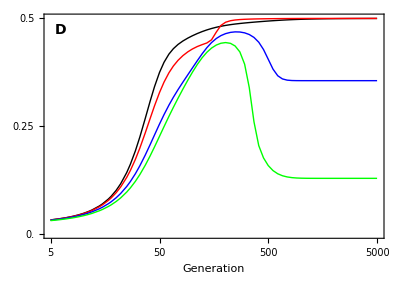

```mathematica
partD=Show[MOD3Black,MOD3Red,MOD3Blue,MOD3Green,
FrameLabel->{{Style["",FontSize->14],""},{Style["Generation",FontSize->14],""}},
Epilog->{
Text[Style["D",14,Bold],Scaled@letpos](*,
Text[Style["r=0.005",14,Bold],Scaled@{0.5,1.02}]*)
}]
```

### All panels

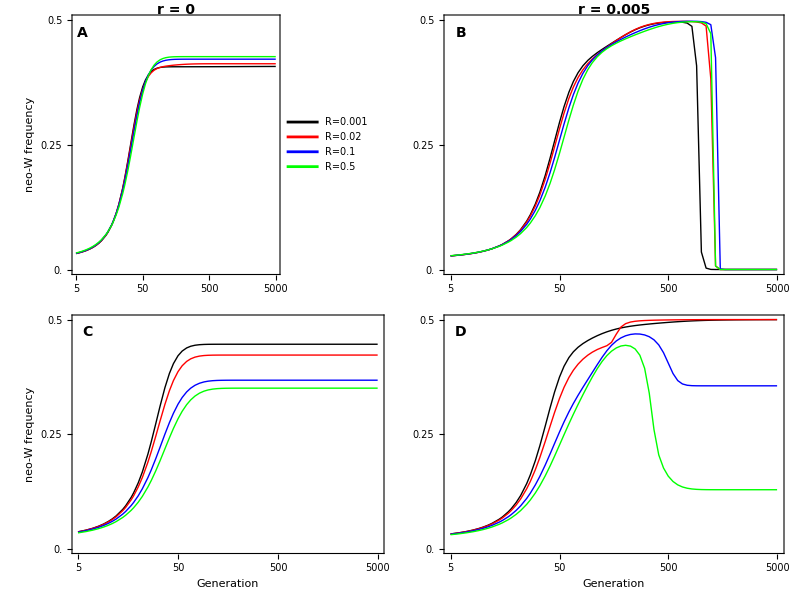

```mathematica
GraphicsGrid[{{partA,partB},{partC,partD}},Spacings->-30]

Export[plotdir<>"Temporal_Overdominance.eps",%//rasterTrick];
```

## Figure S.3 - sexual antagonism and haploid selection allows less closely linked neo-W to invade

### Plotting parameters

```mathematica
Pad={{50,20},{50,30}};  (*space around plot*)
yplotmin=-0.075;
yplotmax=0.15;
yplotinterval=0.02;
ylabpos={-0.14,0.5};  (*relative location of y axis label position*)
```

```mathematica
startplot=5;
endtime=5000;
tryR=0;
trypm=0.01;
tryk=1;
```

```mathematica
loglinearplotINVoptions={Frame->{{True,False},{True,False}}, 
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{5,5,{0,0.01}},{10,10,{0,0.01}},{50,50,{0,0.01}},{100,100,{0,0.01}},(*{500,500,{0,0.01}},*){1000,1000,{0,0.01}}(*,{5000,5000,{0,0.01}}*)},Table[{y,y,ticksize},{y,0,0.5,0.5}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
Axes->True,
FrameLabel->{{Style["neo-W frequency",FontSize->14],""},{Style["Generation",FontSize->14],""}}};
```

```mathematica
loglinearplotRλoptions={Frame->{{True,False},{True,False}}, 
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
PlotRangeClipping->False,
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{0.001,0.001,{0,0.01}},{0.005,"r",{0,0.01}},{0.01,0.01,{0,0.01}},{0.05,0.05,{0,0.01}},{0.5,0.5,{0,0.01}}},Table[{y,y,ticksize},{y,-0.1,0.2,0.1}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
Axes->True,
FrameLabel->{{"",""},{Style["R",FontSize->14],""}}};
```

```mathematica
letposB={0.05,0.95};
```

### Panel A

#### Parameters

```mathematica
x=-5;
m=5;

tryFAA=1+1/20;
tryFAa=1;
tryFaa=1-3/20;
tryMAA=1-3/20;
tryMAa=1;
tryMaa=1+1/20;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=1/2;
tryαm=1/2-8/100;

xplotmin=-10;
xplotmax=10;
xplotinterval=5;
npoints=28;
```

```mathematica
tryr=0.005;
```

#### Plot

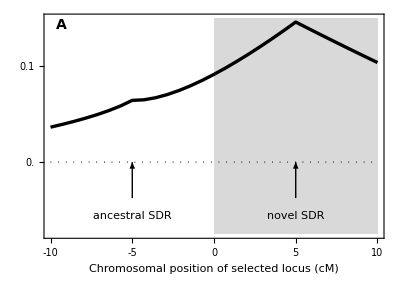

```mathematica
positionplot=
Show[

(*region of tighter linkage*)
RegionPlot[x>0,{x,xplotmin,xplotmax},{y,yplotmin,yplotmax},
PlotStyle->{LightGray},
BoundaryStyle->None,
PlotRange->{yplotmin,yplotmax},
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

(*neo-W into XY*)
ListPlot[Table[{a,invasionplotXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,setr[x,a,m],setR[x,a,m],setρ[x,a,m]]},{a,xplotmin,xplotmax,(xplotmax-xplotmin)/npoints}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Black,Thickness[lwd]],
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

Plot[0,{x,xplotmin,xplotmax},PlotStyle->{Black, Dotted}],

PlotRange->{{xplotmin,xplotmax},{yplotmin,yplotmax}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,-0.1,0.2,0.1}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Chromosomal position of selected locus (cM)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@letposB],
Rotate[Text[Style[(*"Invasion fitness (λ-1)"*)"",14],Scaled@ylabpos],90 Degree],
Rotate[Text[Style["Invasion fitness (λ_W'^(XY)-1)",14],Scaled@ylabpos],90 Degree],
(*Text[Style["tighter sex-linkage",14],{m,yplotmax*0.9}],*)
Text["ancestral SDR",{x,yplotmin*0.75}],
Text["novel SDR",{m,yplotmin*0.75}],
Arrow[{{x,yplotmin*0.5},{x,0}}],
Arrow[{{m,yplotmin*0.5},{m,0}}]
},
PlotRangeClipping->False

]

(*Export[plotdir<>"PositionPlotB.pdf",%];*)
```

### Panel B

#### Plot

```mathematica
subpar1={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

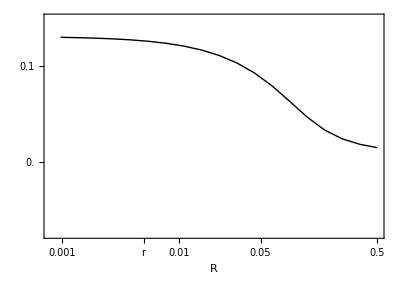

```mathematica
tab=Table[
equil=sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2+(-(λmA1 +λma1)+(χmA1+χma1))λ +(λmA1-χmA1)( λma1-χma1)-χmA1 χma1/.reverse/.pAveM->(1-q)pXm+q pYm/.subpar1/.R->0.5^b/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],q->equil[[4]]})==0,λ],{b,10,1,-1/2}];
eigen1=Transpose[Join[{Table[0.5^b,{b,10,1,-1/2}]},{Transpose[tab][[1]]-1}]];
eigen2=Transpose[Join[{Table[0.5^b,{b,10,1,-1/2}]},{Transpose[tab][[2]]-1}]];
plot1=Show[
ListLogLinearPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->{{0.0008,0.5},{yplotmin,yplotmax}},
loglinearplotRλoptions]
]
```

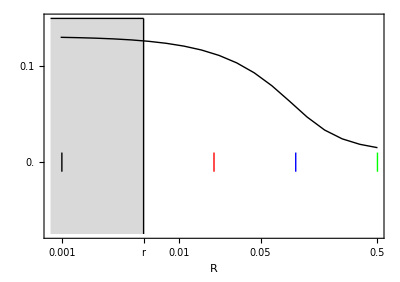

```mathematica
temp=Show[
ListLogLinearPlot[{{0.0008,yplotmax},{tryr,yplotmax}},Joined->True,PlotStyle->{Black,Thin},Filling->yplotmin,FillingStyle->LightGray,loglinearplotRλoptions,PlotRange->{{0.0008,0.5},{yplotmin,yplotmax}}],
plot1,
ListLogLinearPlot[{{tryr,yplotmax},{tryr,yplotmin}},Joined->True,PlotStyle->{Black,Thin}],
ListLogLinearPlot[{{0.001,-0.01},{0.001,0.01}},Joined->True,PlotStyle->{Black,Thick}],
ListLogLinearPlot[{{0.02,-0.01},{0.02,0.01}},Joined->True,PlotStyle->{Red,Thick}],
ListLogLinearPlot[{{0.1,-0.01},{0.1,0.01}},Joined->True,PlotStyle->{Blue,Thick}],
ListLogLinearPlot[{{0.5,-0.01},{0.5,0.01}},Joined->True,PlotStyle->{Green,Thick}],
GridLines->{{0.005},{1}}(*,
GridLinesStyle->Black*)]
```

Ensure this is consistent with the full characteristic polynomial result

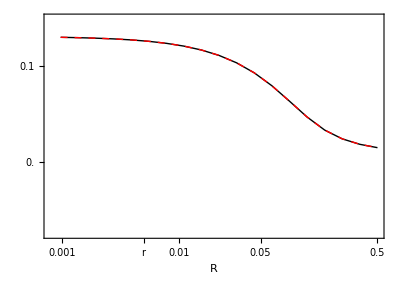

```mathematica
plot2=ListLogLinearPlot[Table[{0.5^b,invasionplotXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,0.5^b,tryr(1-0.5^b)+0.5^b(1-tryr)]},{b,10,1,-1/2}],Joined->True,PlotStyle->{Thick,Red,Dashed},PlotRange->{{0.0008,0.5},{yplotmin,yplotmax}},
loglinearplotRλoptions];
Show[plot1,plot2]
```

### Panel C

```mathematica
modvec={0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0};
```

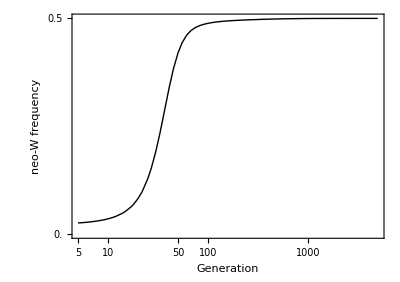

```mathematica
tryR=0.001;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Black=ListLogLinearPlot[MODtab1Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Black,Thick},loglinearplotINVoptions]
```

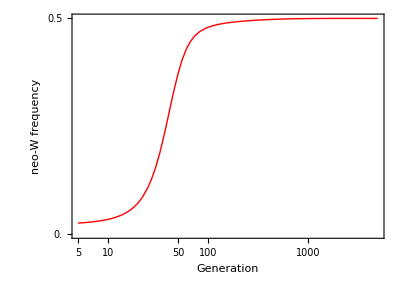

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Red=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Red=ListLogLinearPlot[MODtab1Red,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Red,Thick},loglinearplotINVoptions]
```

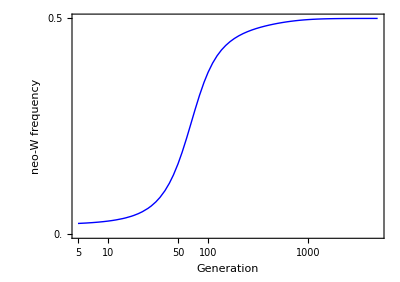

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Blue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Blue=ListLogLinearPlot[MODtab1Blue,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Blue,Thick},loglinearplotINVoptions]
```

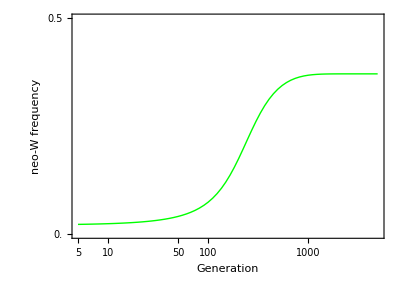

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Green=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Green=ListLogLinearPlot[MODtab1Green,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Green,Thick},loglinearplotINVoptions]
```

### All panels

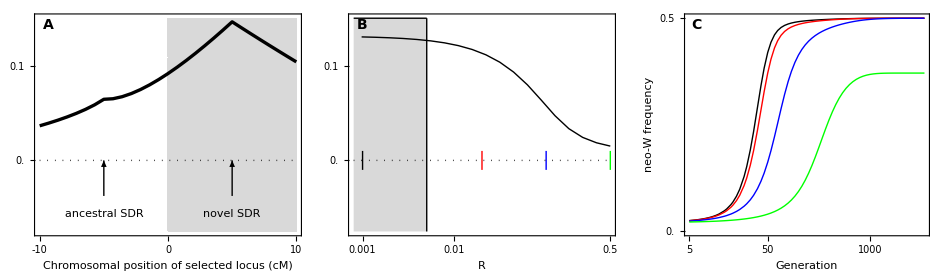

```mathematica
GraphicsRow[{
positionplot,
Show[temp,Graphics[Text[Style["B",14,Bold],Scaled@letposB]],LogLinearPlot[0,{x,0.0008,0.5},PlotStyle->{Black,Dotted}]],Show[MOD1Black,MOD1Red,MOD1Blue,MOD1Green,Graphics[Text[Style["C",14,Bold],Scaled@letposB]],Epilog->Rotate[Text[Style["neo-W frequency",14],Scaled@ylabpos],90 Degree],ImagePadding->Pad]
},
Spacings->-50
]

Export[plotdir<>"PositionPlot_SexAntagTighter_MaleDrive.eps",%//rasterTrick];
```

## Figure S.4 - neo-W haplotype invasion with meiotic drive in males

### Panel A - A favoured in females, a drives in males

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αm->1/2-8/100,
αf->1/2,
MAa->1,FAa->1,
Faa->1-3/20,
FAA->1+1/20
};
```

Making the sex-ratio

```mathematica
freqMale/.equilB0/.params//N
```

0.58

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

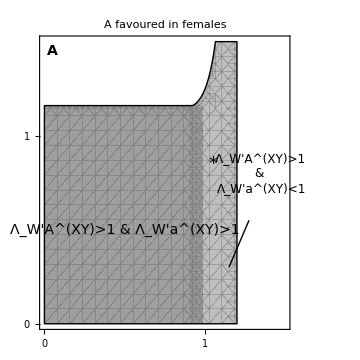

```mathematica
plotA=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

Graphics[{Thick,Black,Line[{{1.15,0.3},{1.275,0.55}}]}],
PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
(*FrameLabel->{"Relative fitness of aa males",""},*)
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)>1 & Λ_W'a^(XY)>1",14],{0.5,0.5}],
Text[Style["Λ_W'A^(XY)>1 
& 
Λ_W'a^(XY)<1",12],{1.355,0.8}],
Text[Style["*",18],{1.05,0.85}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["A favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

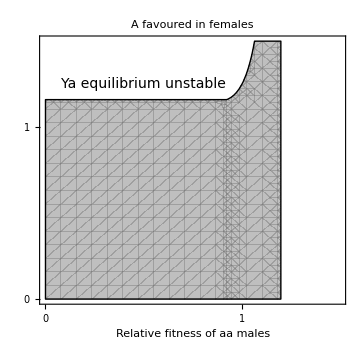

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["A favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel B - a favoured in females, a drives in males

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αm->1/2-8/100,
αf->1/2,
MAa->1,FAa->1,
FAA->1-3/20,
Faa->1+1/20
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

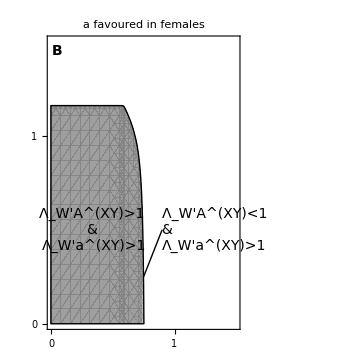

```mathematica
plotB=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

Graphics[{Thick,Black,Line[{{0.9,0.5},{0.75,0.25}}]}],
PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
(*FrameLabel->{"Relative fitness of aa males",""},*)
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)>1 
& 
Λ_W'a^(XY)>1",14],{0.35,0.5}],
Text[Style["Λ_W'A^(XY)<1 
& 
Λ_W'a^(XY)>1",14],{0.9,0.5},{-1.2,0}](*,
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style["a favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

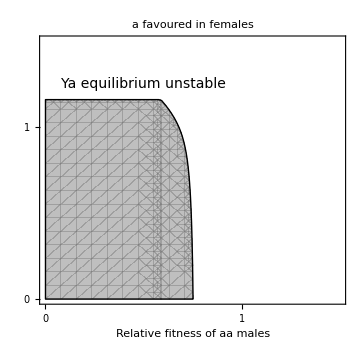

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["a favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel C - overdominance in females, a drives in males

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αm->1/2-8/100,
αf->1/2,
MAa->1,FAa->1,
FAA->1-4/10,
Faa->1-4/10
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

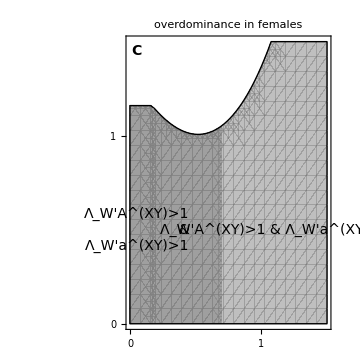

```mathematica
plotC=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
(*FrameLabel->{"Relative fitness of aa males",""},*)
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["C",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)>1
&
Λ_W'a^(XY)>1",14],{0.45,0.5},{1,0}],
Text[Style["Λ_W'A^(XY)>1 & Λ_W'a^(XY)<1",14],{1.1,0.5}](*,
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style["overdominance in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

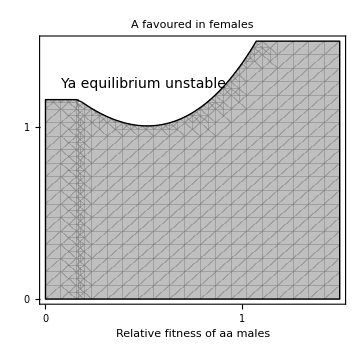

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["A favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel D - A favoured in females, A drives in males

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αm->1/2+8/100,
αf->1/2,
MAa->1,FAa->1,
Faa->1-3/20,
FAA->1+1/20
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

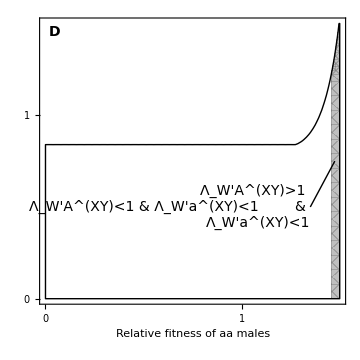

```mathematica
plotD=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

Graphics[{Thick,Black,Line[{{1.35,0.5},{1.475,0.75}}]}],
PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["D",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)<1 & Λ_W'a^(XY)<1",14],{0.5,0.5}],
Text[Style["Λ_W'A^(XY)>1 
& 
Λ_W'a^(XY)<1",14],{1.35,0.5},{1,0}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style[(*"A favoured in females"*)"", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

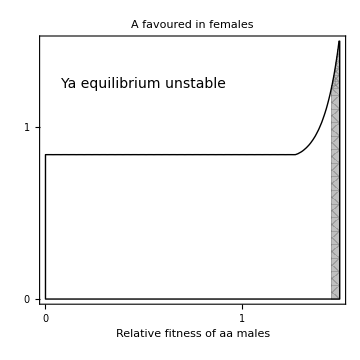

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["A favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel E - a favoured in females, A drives in males

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αm->1/2+8/100,
αf->1/2,
MAa->1,FAa->1,
FAA->1-3/20,
Faa->1+1/20
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

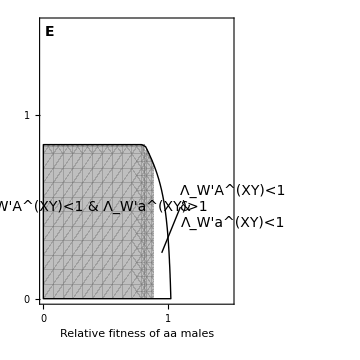

```mathematica
plotE=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

Graphics[{Thick,Black,Line[{{1.1,0.5},{0.95,0.25}}]}],
PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["E",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)<1 & Λ_W'a^(XY)>1",14],{0.4,0.5}],
Text[Style["Λ_W'A^(XY)<1 
& 
Λ_W'a^(XY)<1",14],{1.1,0.5},{-1,0}](*,
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style[(*"a favoured in females"*)"", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

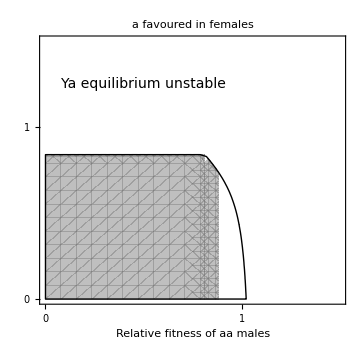

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["a favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel F - overdominance in females, A drives in males

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αm->1/2+8/100,
αf->1/2,
MAa->1,FAa->1,
FAA->1-4/10,
Faa->1-4/10
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

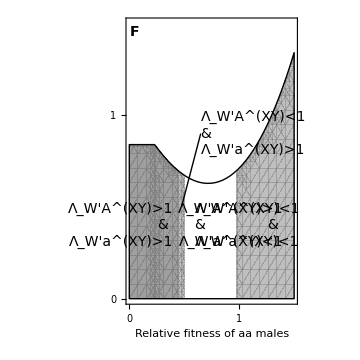

```mathematica
plotF=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

Graphics[{Thick,Black,Line[{{0.65,0.9},{0.475,0.5}}]}],
PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["F",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)>1
& 
Λ_W'a^(XY)>1",14],{0.4,0.4},{1,0}],
Text[Style["Λ_W'A^(XY)>1
& 
Λ_W'a^(XY)<1",14],{1.4,0.4},{1,0}],
Text[Style["Λ_W'A^(XY)<1
& 
Λ_W'a^(XY)<1",14],{0.6,0.4},{-1,0}],
Text[Style["Λ_W'A^(XY)<1
& 
Λ_W'a^(XY)>1",14],{0.65,0.9},{-1,0}](*,
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style[(*"overdominance in females"*)"", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

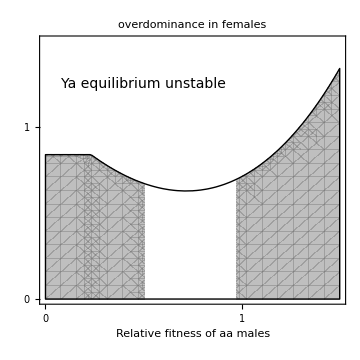

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["overdominance in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### All Panels

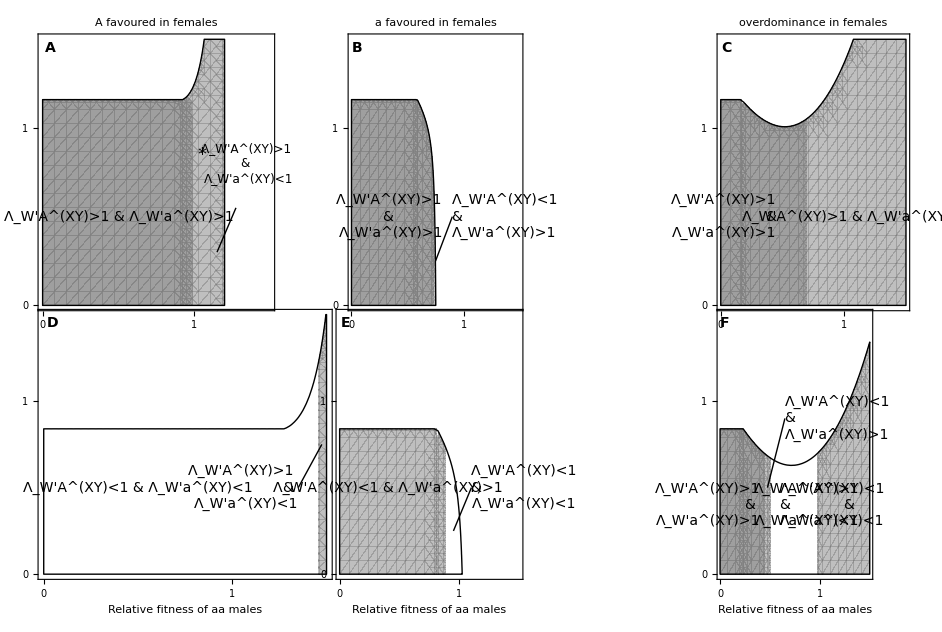

```mathematica
GraphicsGrid[{
{plotA,plotB,plotC},
{plotD,plotE,plotF}
},
Spacings->-50
]

Export[plotdir<>"Region_plot_combined_MaleDrive.eps",%//rasterTrick];
```

## Figure S.5 - neo-W haplotype invasion with haploid competition in males

### Panel A - A favoured in females, haploid competition favours a in males

#### Parameters

```mathematica
params={
wAm->1,wam->1+8/50,wAf->1,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
Faa->1-3/20,
FAA->1+1/20
};
```

Making the sex-ratio

```mathematica
freqMale/.equilB0/.params//N
```

0.537037

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

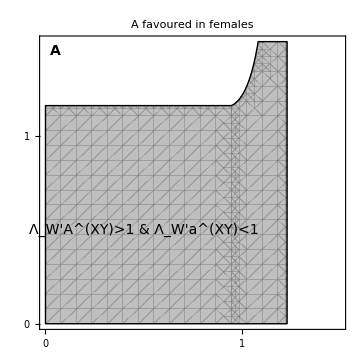

```mathematica
plotA=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
(*FrameLabel->{"Relative fitness of aa males",""},*)
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)>1 & Λ_W'a^(XY)<1",14],{0.5,0.5}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["A favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

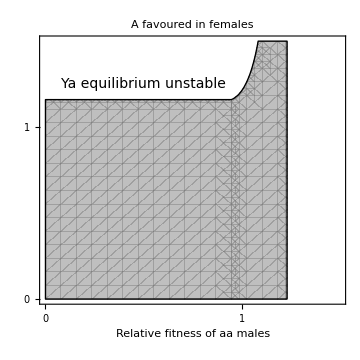

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["A favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel B - a favoured in females, haploid competition favours a in males

#### Parameters

```mathematica
params={
wAm->1,wam->1+8/50,wAf->1,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
FAA->1-3/20,
Faa->1+1/20
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

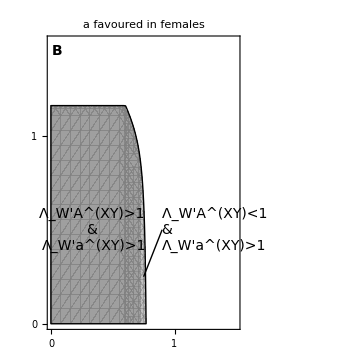

```mathematica
plotB=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

Graphics[{Thick,Black,Line[{{0.9,0.5},{0.75,0.25}}]}],
PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
(*FrameLabel->{"Relative fitness of aa males",""},*)
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)>1 
& 
Λ_W'a^(XY)>1",14],{0.35,0.5}],
Text[Style["Λ_W'A^(XY)<1 
& 
Λ_W'a^(XY)>1",14],{0.9,0.5},{-1.2,0}](*,
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style["a favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

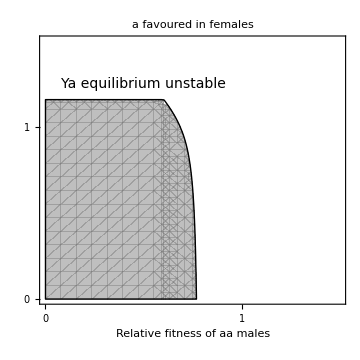

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["a favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel C - overdominance in females, haploid competition favours a in males

#### Parameters

```mathematica
params={
wAm->1,wam->1+8/50,wAf->1,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
FAA->1-4/10,
Faa->1-4/10
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

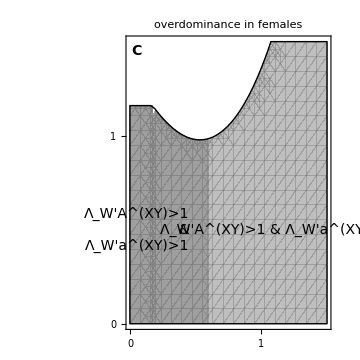

```mathematica
plotC=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
(*FrameLabel->{"Relative fitness of aa males",""},*)
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["C",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)>1
&
Λ_W'a^(XY)>1",14],{0.45,0.5},{1,0}],
Text[Style["Λ_W'A^(XY)>1 & Λ_W'a^(XY)<1",14],{1.1,0.5}](*,
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style["overdominance in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

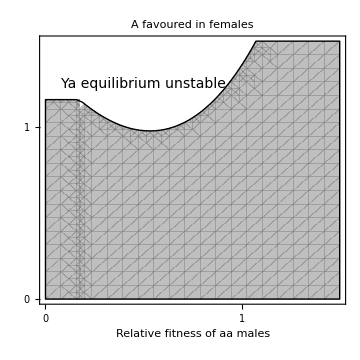

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["A favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel D - A favoured in females, haploid competition favours A in males

#### Parameters

```mathematica
params={
wAm->1+8/50,wam->1,wAf->1,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
Faa->1-3/20,
FAA->1+1/20
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

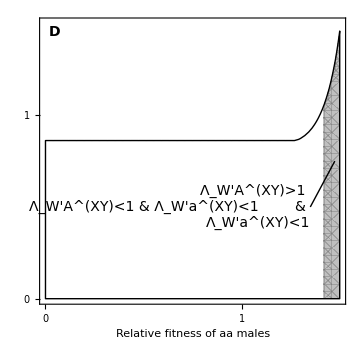

```mathematica
plotD=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

Graphics[{Thick,Black,Line[{{1.35,0.5},{1.475,0.75}}]}],
PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["D",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)<1 & Λ_W'a^(XY)<1",14],{0.5,0.5}],
Text[Style["Λ_W'A^(XY)>1 
& 
Λ_W'a^(XY)<1",14],{1.35,0.5},{1,0}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style[(*"A favoured in females"*)"", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

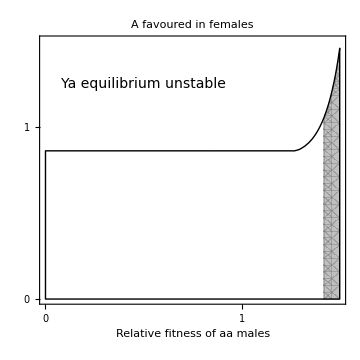

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["A favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel E - a favoured in females, haploid competition favours A in males

#### Parameters

```mathematica
params={
wAm->1+8/50,wam->1,wAf->1,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
FAA->1-3/20,
Faa->1+1/20
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

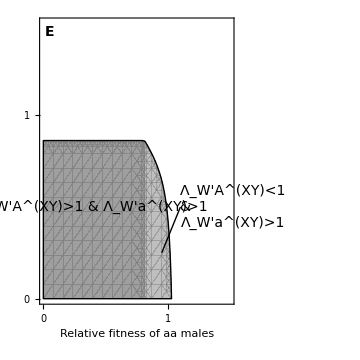

```mathematica
plotE=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

Graphics[{Thick,Black,Line[{{1.1,0.5},{0.95,0.25}}]}],
PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["E",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)>1 & Λ_W'a^(XY)>1",14],{0.4,0.5}],
Text[Style["Λ_W'A^(XY)<1 
& 
Λ_W'a^(XY)>1",14],{1.1,0.5},{-1,0}](*,
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style[(*"a favoured in females"*)"", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

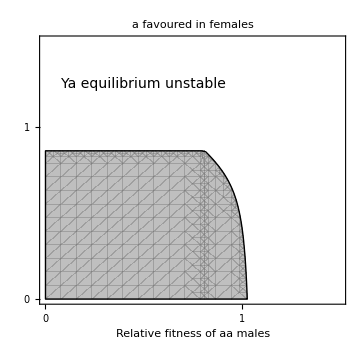

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["a favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel F - overdominance in females, haploid competition favours A in males

#### Parameters

```mathematica
params={
wAm->1+8/50,wam->1,wAf->1,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
FAA->1-4/10,
Faa->1-4/10
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

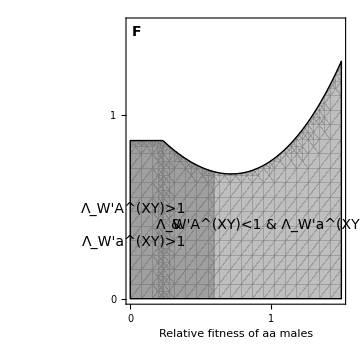

```mathematica
plotF=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["F",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)>1
& 
Λ_W'a^(XY)>1",14],{0.4,0.4},{1,0}],
Text[Style["Λ_W'A^(XY)<1 & Λ_W'a^(XY)>1",14],{1,0.4}](*,
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style[(*"overdominance in females"*)"", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

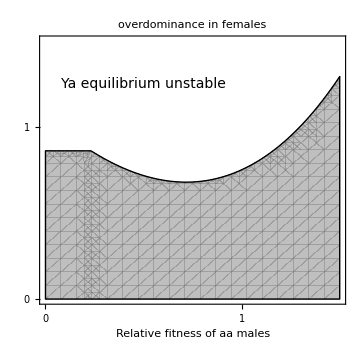

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["overdominance in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### All Panels

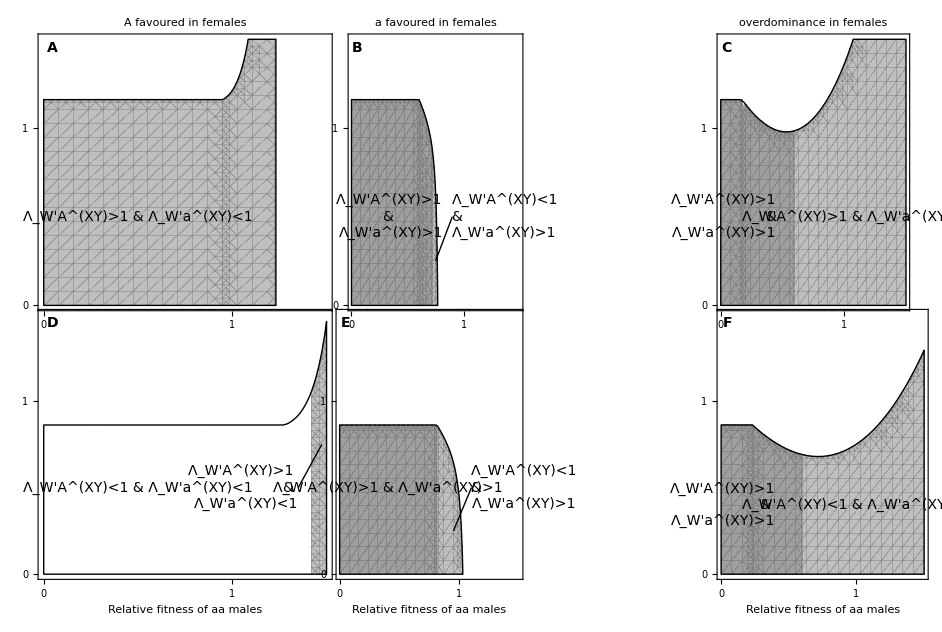

```mathematica
GraphicsGrid[{
{plotA,plotB,plotC},
{plotD,plotE,plotF}
},
Spacings->-50
]

Export[plotdir<>"Region_plot_combined_MaleGS.eps",%//rasterTrick];
```

## Figure S.6 - neo-W haplotype invasion with meiotic drive in females

### Panel A - A favoured in females, a drives in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αf->1/2-8/100,
αm->1/2,
MAa->1,FAa->1,
Faa->1-3/20,
FAA->1+1/20
};
```

Making the sex-ratio

```mathematica
freqMale/.equilB0/.params//N
```

0.5

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

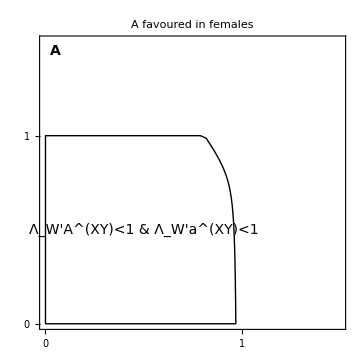

```mathematica
plotA=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
(*FrameLabel->{"Relative fitness of aa males",""},*)
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)<1 & Λ_W'a^(XY)<1",14],{0.5,0.5}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["A favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

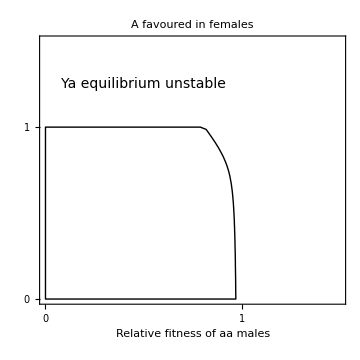

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["A favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel B - a favoured in females, a drives in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αf->1/2-8/100,
αm->1/2,
MAa->1,FAa->1,
FAA->1-3/20,
Faa->1+1/20
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

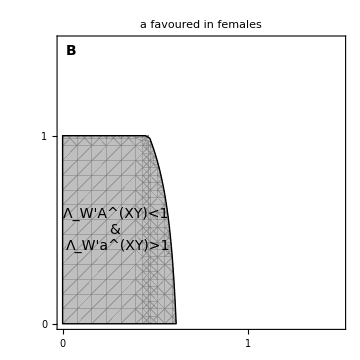

```mathematica
plotB=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
(*FrameLabel->{"Relative fitness of aa males",""},*)
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)<1 
& 
Λ_W'a^(XY)>1",14],{0.3,0.5}](*,
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style["a favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

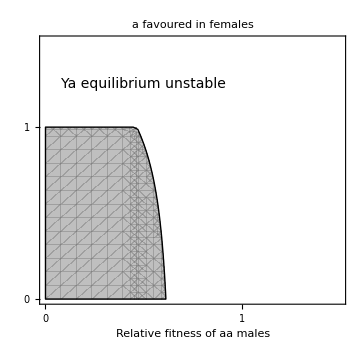

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["a favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel C - overdominance in females, a drives in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αf->1/2-8/100,
αm->1/2,
MAa->1,FAa->1,
FAA->1-4/10,
Faa->1-4/10
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

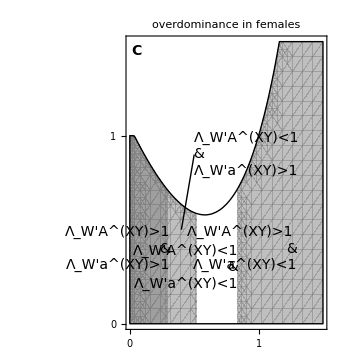

```mathematica
plotC=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

Graphics[{Thick,Black,Line[{{0.5,0.9},{0.4,0.5}}]}],
PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
(*FrameLabel->{"Relative fitness of aa males",""},*)
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["C",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)>1
&
Λ_W'a^(XY)>1",14],{0.31,0.4},{1,0}],
Text[Style["Λ_W'A^(XY)<1
& 
Λ_W'a^(XY)>1",14],{0.5,0.9},{-1,0}],
Text[Style["Λ_W'A^(XY)<1
&
Λ_W'a^(XY)<1",14],{0.84,0.3},{1,0}],
Text[Style["Λ_W'A^(XY)>1 
&
Λ_W'a^(XY)<1",14],{1.3,0.4},{1,0}](*,
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style["overdominance in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

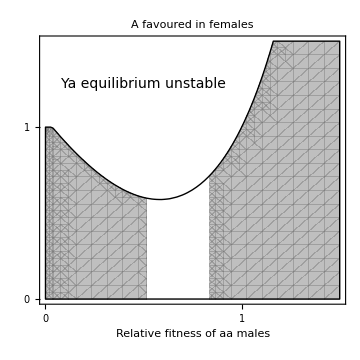

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["A favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel D - A favoured in females, A drives in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αf->1/2+8/100,
αm->1/2,
MAa->1,FAa->1,
Faa->1-3/20,
FAA->1+1/20
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

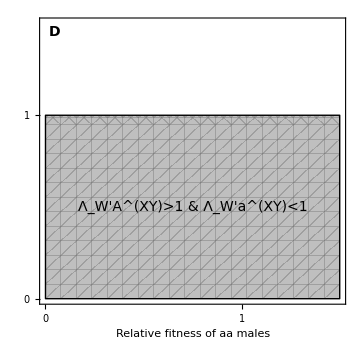

```mathematica
plotD=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["D",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)>1 & Λ_W'a^(XY)<1",14],{0.75,0.5}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style[(*"A favoured in females"*)"", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

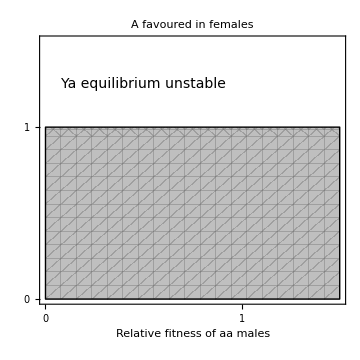

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["A favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel E - a favoured in females, A drives in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αf->1/2+8/100,
αm->1/2,
MAa->1,FAa->1,
FAA->1-3/20,
Faa->1+1/20
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

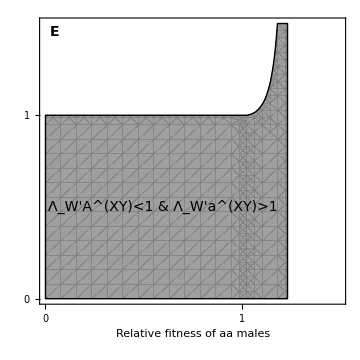

```mathematica
plotE=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["E",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)<1 & Λ_W'a^(XY)>1",14],{0.6,0.5}](*,
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style[(*"a favoured in females"*)"", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

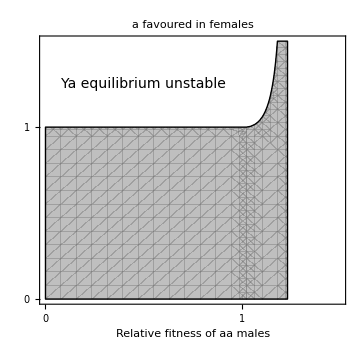

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["a favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel F - overdominance in females, A drives in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αf->1/2+8/100,
αm->1/2,
MAa->1,FAa->1,
FAA->1-4/10,
Faa->1-4/10
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

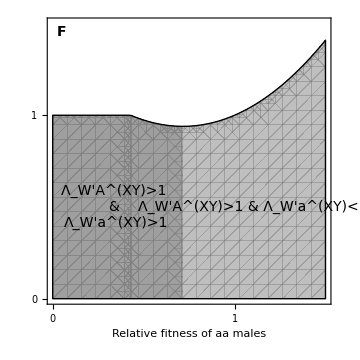

```mathematica
plotF=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["F",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)>1 
& 
Λ_W'a^(XY)>1",14],{0.35,0.5}],
Text[Style["Λ_W'A^(XY)>1 & Λ_W'a^(XY)<1",14],{1.1,0.5}](*,
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style[(*"overdominance in females"*)"", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

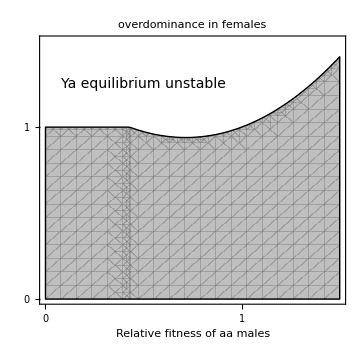

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["overdominance in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### All Panels

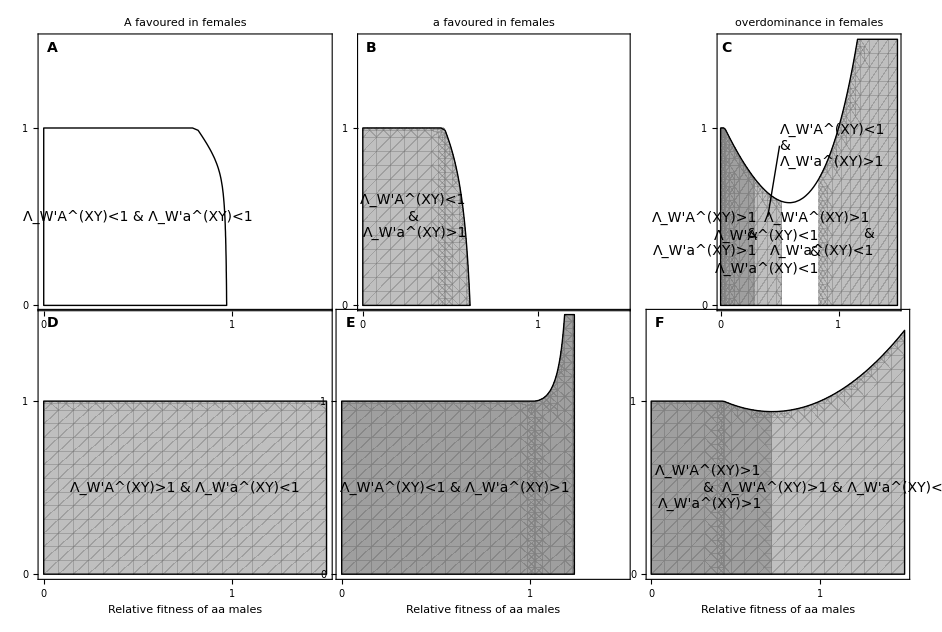

```mathematica
GraphicsGrid[{
{plotA,plotB,plotC},
{plotD,plotE,plotF}
},
Spacings->-50
]

Export[plotdir<>"Region_plot_combined_FemaleDrive.eps",%//rasterTrick];
```

## Figure S.7 - neo-W haplotype invasion with haploid competition in females

### Panel A - A favoured in females, haploid competition favours a in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1+8/50,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
Faa->1-3/20,
FAA->1+1/20
};
```

Making the sex-ratio

```mathematica
freqMale/.equilB0/.params//N
```

0.5

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

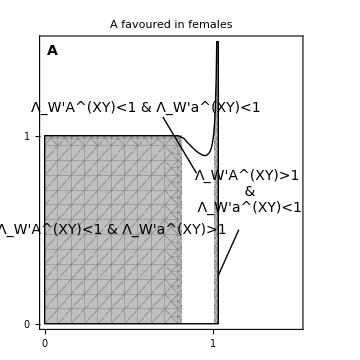

```mathematica
plotA=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

Graphics[{Thick,Black,Line[{{1.15,0.5},{1.025,0.25}}]}],
Graphics[{Thick,Black,Line[{{0.9,0.8},{0.7,1.1}}]}],
PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
(*FrameLabel->{"Relative fitness of aa males",""},*)
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)<1 & Λ_W'a^(XY)>1",14],{0.4,0.5}],
Text[Style["Λ_W'A^(XY)>1
 &
 Λ_W'a^(XY)<1",14],{1.2,0.7}],
Text[Style["Λ_W'A^(XY)<1 & Λ_W'a^(XY)<1",14],{0.6,1.15}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["A favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

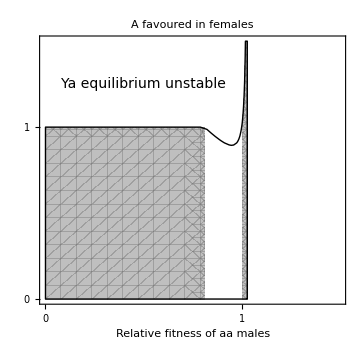

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["A favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel B - a favoured in females, haploid competition favours a in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1+8/50,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
FAA->1-3/20,
Faa->1+1/20
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

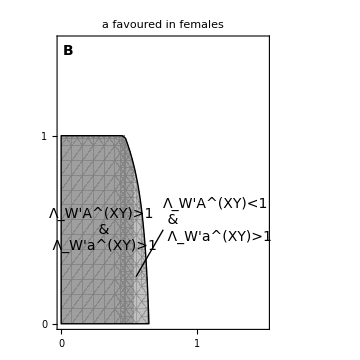

```mathematica
plotB=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

Graphics[{Thick,Black,Line[{{0.75,0.5},{0.55,0.25}}]}],
PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
(*FrameLabel->{"Relative fitness of aa males",""},*)
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)>1
 &
 Λ_W'a^(XY)>1",14],{0.3,0.5}],
Text[Style["Λ_W'A^(XY)<1
 &
 Λ_W'a^(XY)>1",14],{0.75,0.55},{-1.35,0.05}](*,
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style["a favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

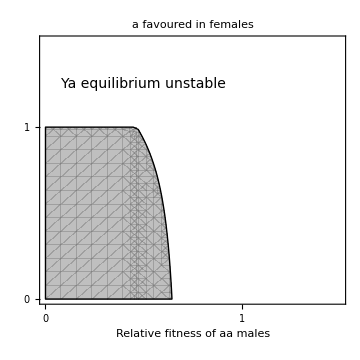

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["a favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel C - overdominance in females, haploid competition favours a in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1+8/50,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
FAA->1-4/10,
Faa->1-4/10
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

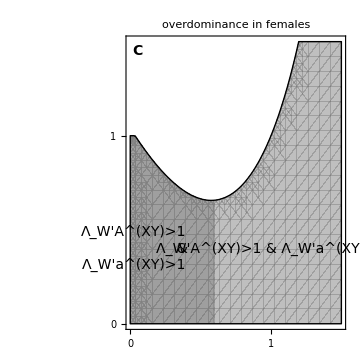

```mathematica
plotC=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
(*FrameLabel->{"Relative fitness of aa males",""},*)
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["C",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)>1
&
Λ_W'a^(XY)>1",14],{0.4,0.4},{1,0}],
Text[Style["Λ_W'A^(XY)>1 & Λ_W'a^(XY)<1",14],{1,0.4}](*,
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style["overdominance in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

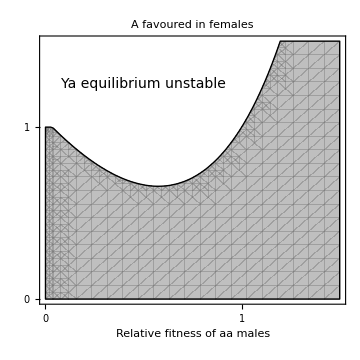

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["A favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel D - A favoured in females, haploid competition favours A in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1+8/50,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
Faa->1-3/20,
FAA->1+1/20
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

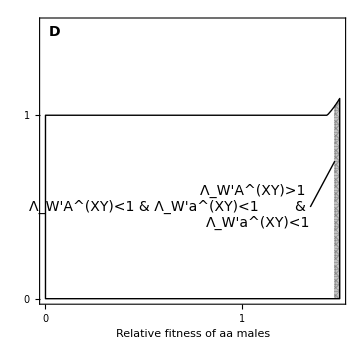

```mathematica
plotD=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

Graphics[{Thick,Black,Line[{{1.35,0.5},{1.475,0.75}}]}],
PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["D",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)<1 & Λ_W'a^(XY)<1",14],{0.5,0.5}],
Text[Style["Λ_W'A^(XY)>1 
& 
Λ_W'a^(XY)<1",14],{1.35,0.5},{1,0}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style[(*"A favoured in females"*)"", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

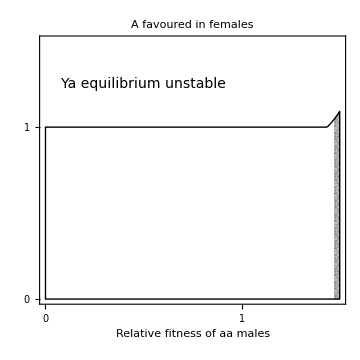

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["A favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel E - a favoured in females, haploid competition favours A in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1+8/50,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
FAA->1-3/20,
Faa->1+1/20
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

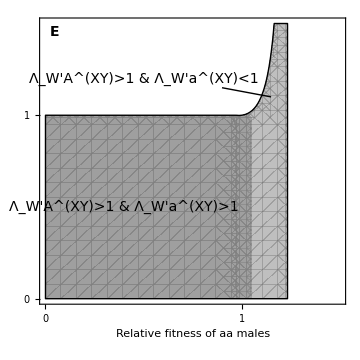

```mathematica
plotE=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

Graphics[{Thick,Black,Line[{{1.15,1.1},{0.9,1.15}}]}],
PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["E",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)>1 & Λ_W'a^(XY)>1",14],{0.4,0.5}],
Text[Style["Λ_W'A^(XY)>1 & Λ_W'a^(XY)<1",14],{0.5,1.2}](*,
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style[(*"a favoured in females"*)"", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

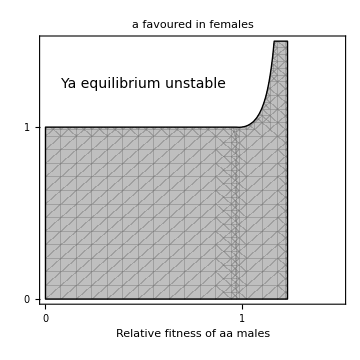

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["a favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel F - overdominance in females, haploid competition favours A in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1+8/50,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
FAA->1-4/10,
Faa->1-4/10
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

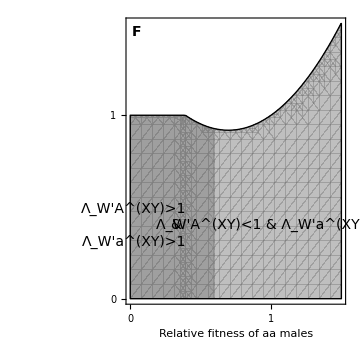

```mathematica
plotF=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["F",14,Bold],Scaled@{0.05,0.95}],
Text[Style["Λ_W'A^(XY)>1
& 
Λ_W'a^(XY)>1",14],{0.4,0.4},{1,0}],
Text[Style["Λ_W'A^(XY)<1 & Λ_W'a^(XY)>1",14],{1,0.4}](*,
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style[(*"overdominance in females"*)"", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

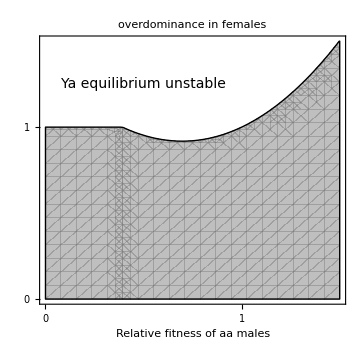

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["overdominance in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### All Panels

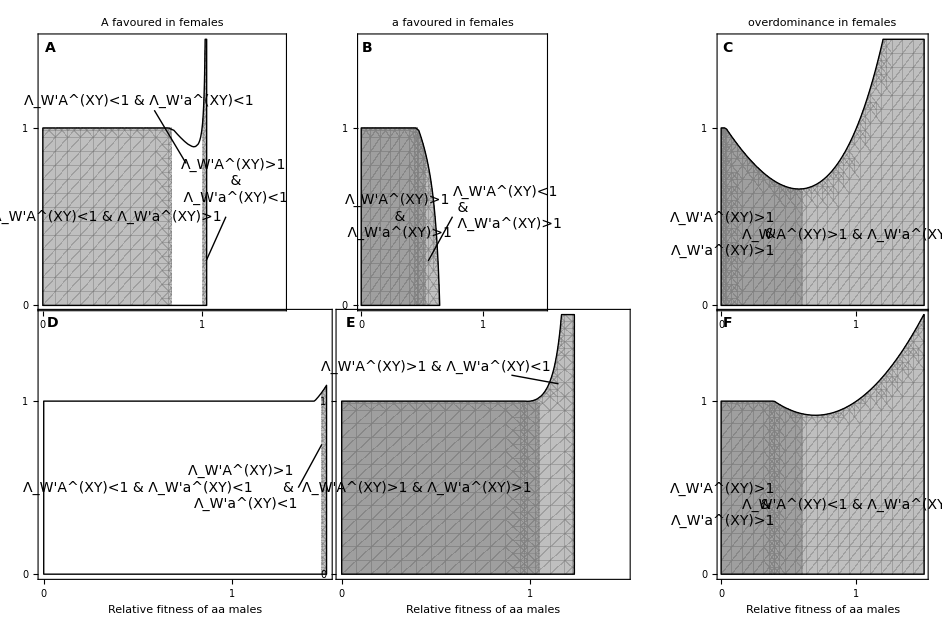

```mathematica
GraphicsGrid[{
{plotA,plotB,plotC},
{plotD,plotE,plotF}
},
Spacings->-50
]

Export[plotdir<>"Region_plot_combined_FemaleGS.eps",%//rasterTrick];
```

## Figure S.8 - neo-W haplotype invasion with ploidally-antagonistic selection

#### extra parameters (move to top)

```mathematica
tryr=1/200;
tryk=1;
trypm=0.01;
```

```mathematica
startplot=5;
endtime=15000;
```

```mathematica
loglinearplotINVoptions={
Frame->{{True,False},{True,False}}, 
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{(*{5,5,{0,0.01}},*){10,10,{0,0.01}},(*{50,50,{0,0.01}},*){100,100,{0,0.01}},(*{500,500,{0,0.01}},*){1000,1000,{0,0.01}}(*,{5000,5000,{0,0.01}}*),{10000,10000,{0,0.01}}},Table[{y,y,ticksize},{y,0,0.5,0.5}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
Axes->True,
FrameLabel->{Style["Generation",FontSize->14],},
ImagePadding->Pad
};
```

```mathematica
modvec={0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0};
```

### Panel A - invasion region with drive in males

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αm->(1+αmd)/2,αf->1/2,
Maa->1,Faa->1,
MAa->1+(3/4)s,FAa->1+(3/4)s,
MAA->1+s,FAA->1+s
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params//Simplify,λ]]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params//Simplify,λ]]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{αmd,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{αmd,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{αmd,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{αmd,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{αmd,-1,1},{s,-1,1},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

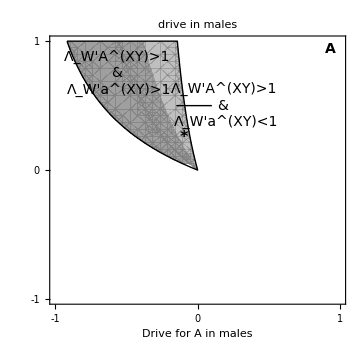

```mathematica
plotA=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

Graphics[{Thick,Black,Line[{{-0.15,0.5},{0.1,0.5}}]}],
PlotRange->{{-1,1},{-1,1}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,-1,1,1}],Table[{y,y,ticksize},{y,-1,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Drive for A in males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@{0.95,0.95}],
Text[Style["Λ_W'A^(XY)>1 
& 
Λ_W'a^(XY)>1",14],{-0.55,0.75}],
Text[Style["Λ_W'A^(XY)>1 
& 
Λ_W'a^(XY)<1",14],{0.2,0.5}],
Text[Style["*",16,Bold],{-0.1,0.25}],
Rotate[Text[Style["Diploid selection for A",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["drive in males", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA(*invasion*)
},
{αmd,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{αmd,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

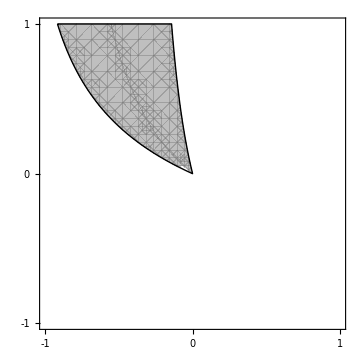

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{-1,1},{-1,1}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,-1,1,1}],Table[{y,y,ticksize},{y,-1,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
PlotRangeClipping->False
]
```

### Panel B - invasion region with haploid competition in males

#### Parameters

```mathematica
params={
wAm->1+t,wam->1,wAf->1,waf->1,
αm->1/2,αf->1/2,
Maa->1,Faa->1,
MAa->1+(3/4)s,FAa->1+(3/4)s,
MAA->1+s,FAA->1+s
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params//Simplify,λ]]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params//Simplify,λ]]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{t,-1,1},{s,-1,1},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

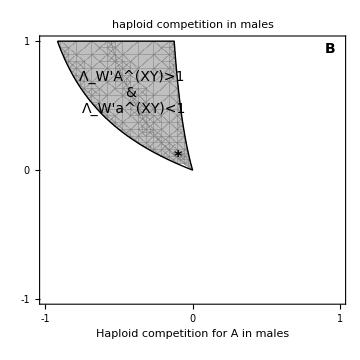

```mathematica
plotB=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

PlotRange->{{-1,1},{-1,1}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,-1,1,1}],Table[{y,y,ticksize},{y,-1,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Haploid competition for A in males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@{0.95,0.95}],
Text[Style["Λ_W'A^(XY)>1 
& 
Λ_W'a^(XY)<1",14],{-0.4,0.6}],
Text[Style["*",16,Bold],{-0.1,0.1}]
},
PlotLabel->Style["haploid competition in males", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA(*invasion*)
},
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

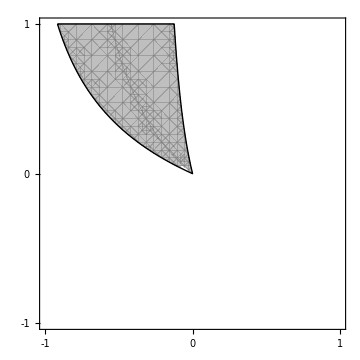

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{-1,1},{-1,1}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,-1,1,1}],Table[{y,y,ticksize},{y,-1,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
PlotRangeClipping->False
]
```

### Panel C - invasion region with drive in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αm->1/2,αf->(1+αmd)/2,
Maa->1,Faa->1,
MAa->1+(3/4)s,FAa->1+(3/4)s,
MAA->1+s,FAA->1+s
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params//Simplify,λ]]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params//Simplify,λ]]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{αmd,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{αmd,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{αmd,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{αmd,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{αmd,-1,1},{s,-1,1},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

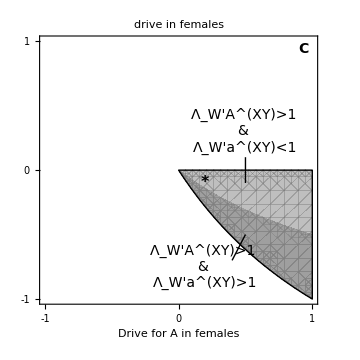

```mathematica
plotC=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

Graphics[{Thick,Black,Line[{{0.5,-0.1},{0.5,0.1}}]}],
Graphics[{Thick,Black,Line[{{0.5,-0.5},{0.4,-0.7}}]}],
PlotRange->{{-1,1},{-1,1}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,-1,1,1}],Table[{y,y,ticksize},{y,-1,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Drive for A in females",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["C",14,Bold],Scaled@{0.95,0.95}],
Text[Style["Λ_W'A^(XY)>1 
& 
Λ_W'a^(XY)<1",14],{0.5,0.3}],
Text[Style["Λ_W'A^(XY)>1 
& 
Λ_W'a^(XY)>1",14],{0.2,-0.75}],
Text[Style["*",16,Bold],{0.2,-0.1}]
},
PlotLabel->Style["drive in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA(*invasion*)
},
{αmd,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{αmd,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

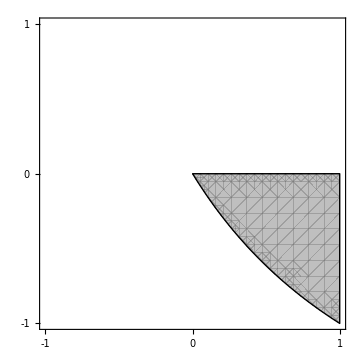

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{-1,1},{-1,1}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,-1,1,1}],Table[{y,y,ticksize},{y,-1,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
PlotRangeClipping->False
]
```

### Panel D - invasion region with haploid competition in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1+t,waf->1,
αm->1/2,αf->1/2,
Maa->1,Faa->1,
MAa->1+(3/4)s,FAa->1+(3/4)s,
MAA->1+s,FAA->1+s
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params//Simplify,λ]]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params//Simplify,λ]]];
```

#### Plot

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WAinvB(*invasion*)
},
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{t,-1,1},{s,-1,1},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

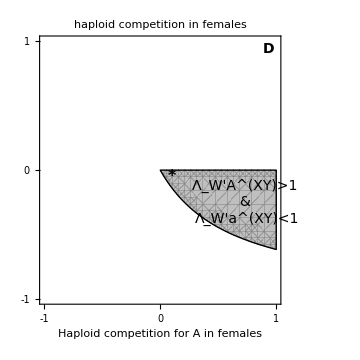

```mathematica
plotD=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

PlotRange->{{-1,1},{-1,1}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,-1,1,1}],Table[{y,y,ticksize},{y,-1,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Haploid competition for A in females",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["D",14,Bold],Scaled@{0.95,0.95}],
Text[Style["Λ_W'A^(XY)>1 
& 
Λ_W'a^(XY)<1",14],{0.75,-0.25}],
Text[Style["*",16,Bold],{0.1,-0.05}]
},
PlotLabel->Style["haploid competition in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA(*invasion*)
},
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{t,-1,1},{s,-1,1},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

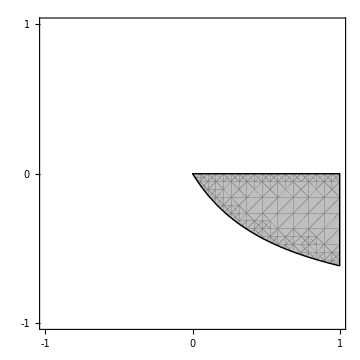

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{-1,1},{-1,1}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,-1,1,1}],Table[{y,y,ticksize},{y,-1,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
PlotRangeClipping->False
]
```

### Panel E - temporal invasion dynamic with meiotic drive in males

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αm->(1+αmd)/2,αf->1/2,
Maa->1,Faa->1,
MAa->1+(3/4)s,FAa->1+(3/4)s,
MAA->1+s,FAA->1+s
};
```

```mathematica
moreparams={
s->1/4,
αmd->-1/10
};
```

```mathematica
tryFAA=FAA/.params/.moreparams;
tryFAa=FAa/.params/.moreparams;
tryFaa=Faa/.params/.moreparams;
tryMAA=MAA/.params/.moreparams;
tryMAa=MAa/.params/.moreparams;
tryMaa=Maa/.params/.moreparams;
trywAf=wAf/.params/.moreparams;
trywaf=waf/.params/.moreparams;
trywAm=wAm/.params/.moreparams;
trywam=wam/.params/.moreparams;
tryαf=αf/.params/.moreparams;
tryαm=αm/.params/.moreparams;
```

#### Plots

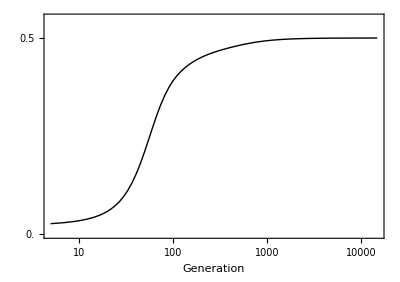

```mathematica
tryR=0.001;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Black=ListLogLinearPlot[MODtab1Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Black,Thick},loglinearplotINVoptions]
```

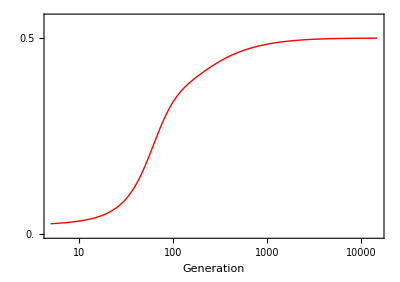

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Red=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Red=ListLogLinearPlot[MODtab1Red,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Red,Thick},loglinearplotINVoptions]
```

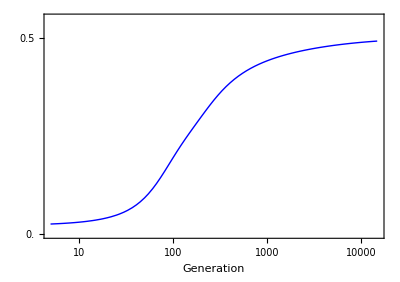

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Blue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Blue=ListLogLinearPlot[MODtab1Blue,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Blue,Thick},loglinearplotINVoptions]
```

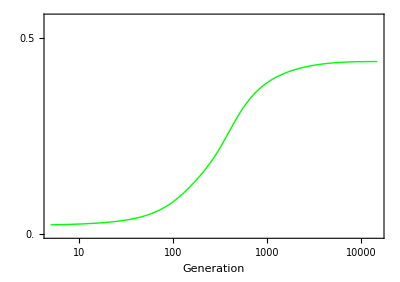

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Green=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Green=ListLogLinearPlot[MODtab1Green,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Green,Thick},loglinearplotINVoptions]
```

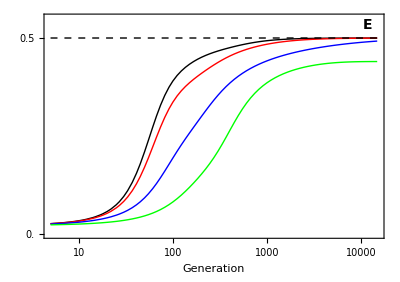

```mathematica
plotE=Show[MOD1Black,MOD1Red,MOD1Blue,MOD1Green,LogLinearPlot[0.5,{x,5,endtime}, PlotStyle->{Black,Dashed}],
Epilog->{
Rotate[Text[Style["neo-W frequency",14],Scaled@ylabpos],90 Degree],
Text[Style["E",14,Bold],Scaled@{0.95,0.95}]
}
,PlotRangeClipping->False]
```

### Panel F - temporal invasion dynamic with haploid competition in males

#### Parameters

```mathematica
params={
wAm->1+t,wam->1,wAf->1,waf->1,
αm->1/2,αf->1/2,
Maa->1,Faa->1,
MAa->1+(3/4)s,FAa->1+(3/4)s,
MAA->1+s,FAA->1+s
};
```

```mathematica
moreparams={
s->1/10,
t->-1/10
};
```

```mathematica
tryFAA=FAA/.params/.moreparams;
tryFAa=FAa/.params/.moreparams;
tryFaa=Faa/.params/.moreparams;
tryMAA=MAA/.params/.moreparams;
tryMAa=MAa/.params/.moreparams;
tryMaa=Maa/.params/.moreparams;
trywAf=wAf/.params/.moreparams;
trywaf=waf/.params/.moreparams;
trywAm=wAm/.params/.moreparams;
trywam=wam/.params/.moreparams;
tryαf=αf/.params/.moreparams;
tryαm=αm/.params/.moreparams;
```

#### Plots

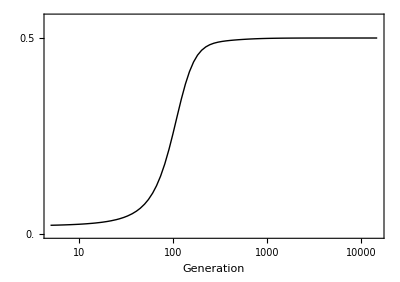

```mathematica
tryR=0.001;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Black=ListLogLinearPlot[MODtab1Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Black,Thick},loglinearplotINVoptions]
```

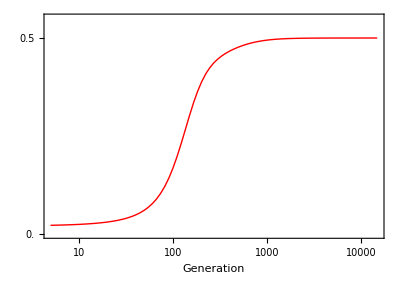

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Red=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Red=ListLogLinearPlot[MODtab1Red,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Red,Thick},loglinearplotINVoptions]
```

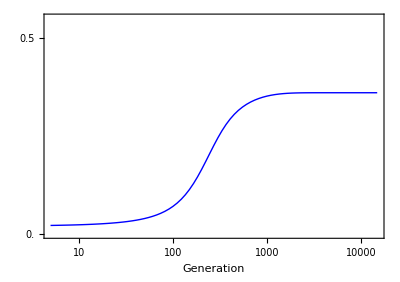

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Blue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Blue=ListLogLinearPlot[MODtab1Blue,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Blue,Thick},loglinearplotINVoptions]
```

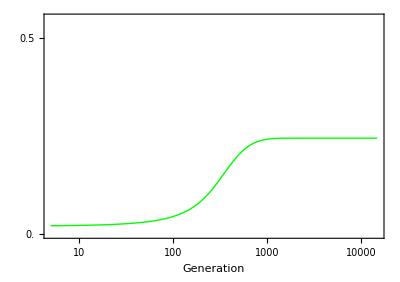

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Green=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Green=ListLogLinearPlot[MODtab1Green,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Green,Thick},loglinearplotINVoptions]
```

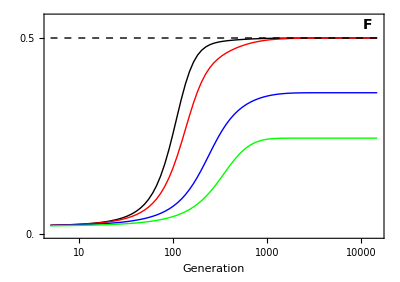

```mathematica
plotF=Show[MOD1Black,MOD1Red,MOD1Blue,MOD1Green,LogLinearPlot[0.5,{x,5,endtime}, PlotStyle->{Black,Dashed}],
Epilog->{
Text[Style["F",14,Bold],Scaled@{0.95,0.95}]
}
,PlotRangeClipping->False]
```

### Panel G - temporal invasion dynamic with meiotic drive in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αm->1/2,αf->(1+αmd)/2,
Maa->1,Faa->1,
MAa->1+(3/4)s,FAa->1+(3/4)s,
MAA->1+s,FAA->1+s
};
```

```mathematica
moreparams={
s->-1/10,
αmd->1/5
};
```

```mathematica
tryFAA=FAA/.params/.moreparams;
tryFAa=FAa/.params/.moreparams;
tryFaa=Faa/.params/.moreparams;
tryMAA=MAA/.params/.moreparams;
tryMAa=MAa/.params/.moreparams;
tryMaa=Maa/.params/.moreparams;
trywAf=wAf/.params/.moreparams;
trywaf=waf/.params/.moreparams;
trywAm=wAm/.params/.moreparams;
trywam=wam/.params/.moreparams;
tryαf=αf/.params/.moreparams;
tryαm=αm/.params/.moreparams;
```

#### Plots

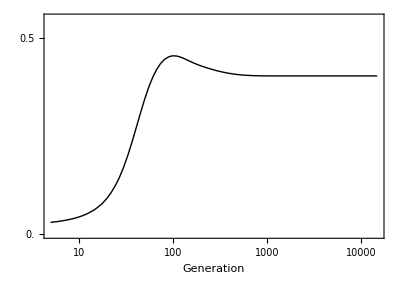

```mathematica
tryR=0.001;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Black=ListLogLinearPlot[MODtab1Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Black,Thick},loglinearplotINVoptions]
```

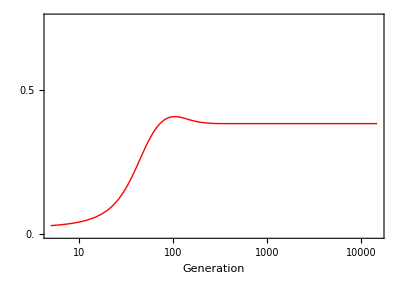

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Red=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Red=ListLogLinearPlot[MODtab1Red,Joined->True,PlotRange->{{startplot,endtime},{0,0.75}},PlotStyle->{Red,Thick},loglinearplotINVoptions]
```

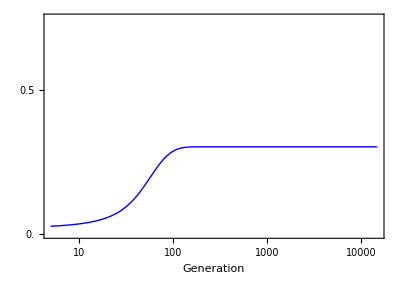

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Blue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Blue=ListLogLinearPlot[MODtab1Blue,Joined->True,PlotRange->{{startplot,endtime},{0,0.75}},PlotStyle->{Blue,Thick},loglinearplotINVoptions]
```

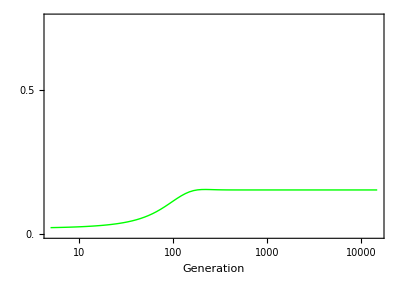

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Green=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Green=ListLogLinearPlot[MODtab1Green,Joined->True,PlotRange->{{startplot,endtime},{0,0.75}},PlotStyle->{Green,Thick},loglinearplotINVoptions]
```

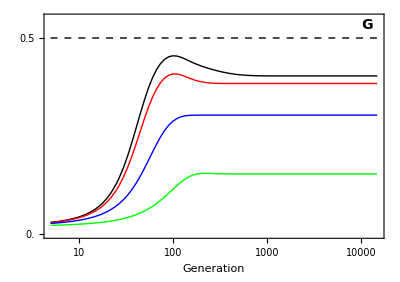

```mathematica
plotG=Show[MOD1Black,MOD1Red,MOD1Blue,MOD1Green,LogLinearPlot[0.5,{x,5,endtime}, PlotStyle->{Black,Dashed}],
Epilog->{
Text[Style["G",14,Bold],Scaled@{0.95,0.95}]
}
,PlotRangeClipping->False]
```

### Panel H - temporal invasion dynamic with haploid competition in females

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1+t,waf->1,
αm->1/2,αf->1/2,
Maa->1,Faa->1,
MAa->1+(3/4)s,FAa->1+(3/4)s,
MAA->1+s,FAA->1+s
};
```

```mathematica
moreparams={
s->-1/20,
t->1/10
};
```

```mathematica
tryFAA=FAA/.params/.moreparams;
tryFAa=FAa/.params/.moreparams;
tryFaa=Faa/.params/.moreparams;
tryMAA=MAA/.params/.moreparams;
tryMAa=MAa/.params/.moreparams;
tryMaa=Maa/.params/.moreparams;
trywAf=wAf/.params/.moreparams;
trywaf=waf/.params/.moreparams;
trywAm=wAm/.params/.moreparams;
trywam=wam/.params/.moreparams;
tryαf=αf/.params/.moreparams;
tryαm=αm/.params/.moreparams;
```

#### Plots

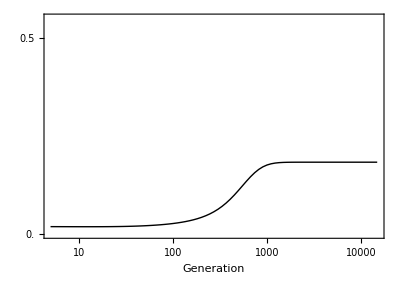

```mathematica
tryR=0.001;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Black=ListLogLinearPlot[MODtab1Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Black,Thick},loglinearplotINVoptions]
```

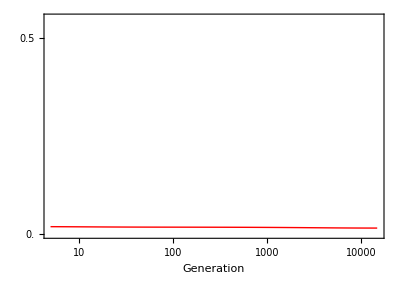

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Red=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Red=ListLogLinearPlot[MODtab1Red,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Red,Thick},loglinearplotINVoptions]
```

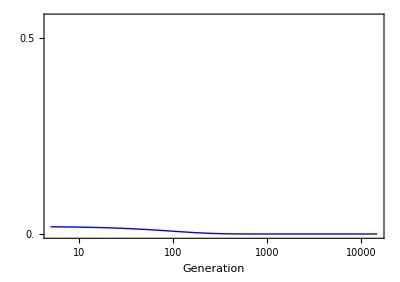

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Blue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Blue=ListLogLinearPlot[MODtab1Blue,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Blue,Thick},loglinearplotINVoptions]
```

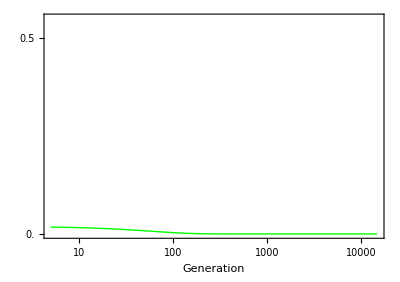

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Green=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Green=ListLogLinearPlot[MODtab1Green,Joined->True,PlotRange->{{startplot,endtime},{0,0.55}},PlotStyle->{Green,Thick},loglinearplotINVoptions]
```

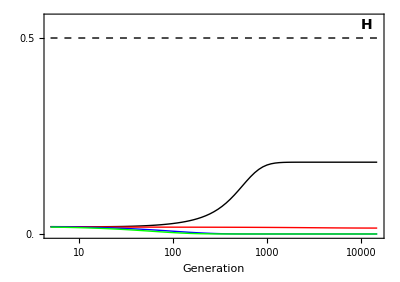

```mathematica
plotH=Show[MOD1Black,MOD1Red,MOD1Blue,MOD1Green,LogLinearPlot[0.5,{x,5,endtime}, PlotStyle->{Black,Dashed}],
Epilog->{
Rotate[Text[Style["",14],Scaled@ylabpos],90 Degree],
Text[Style["H",14,Bold],Scaled@{0.95,0.95}]
}
,PlotRangeClipping->False]
```

### All panels

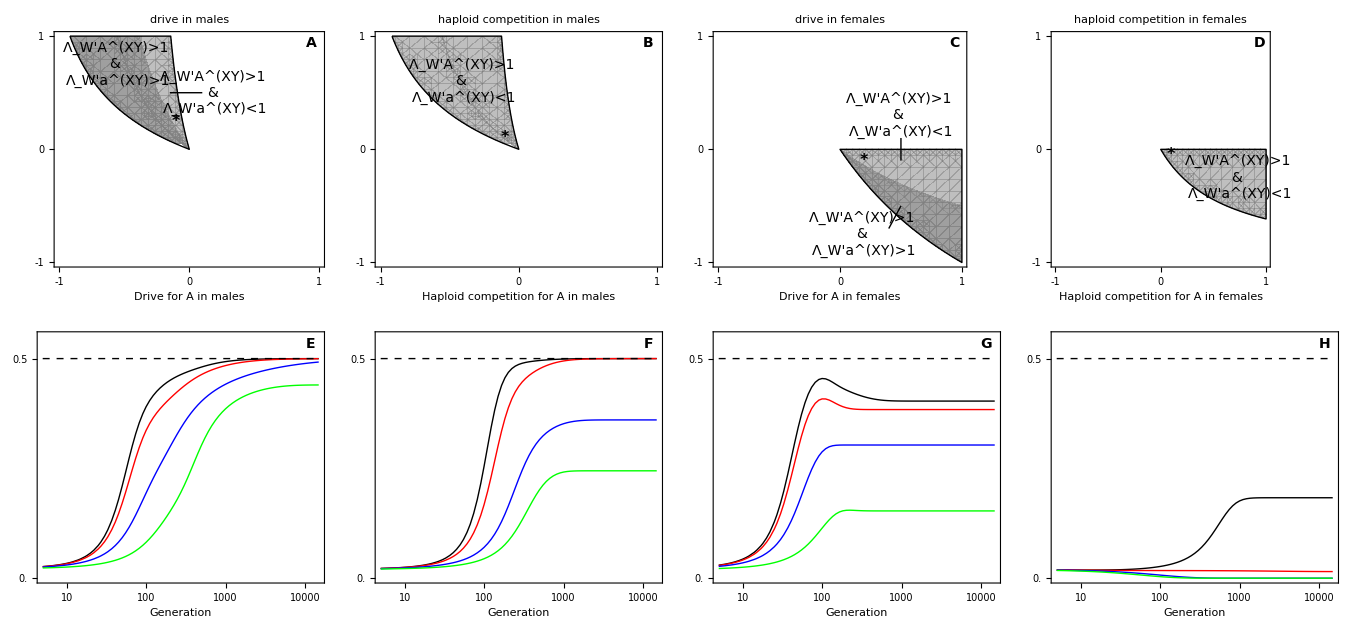

```mathematica
GraphicsGrid[{
{plotA,plotB,plotC,plotD},
{plotE,plotF,plotG,plotH}
},
Spacings->{-25,-50}]

Export[plotdir<>"All_plot_combined_PloidAntag.eps",%//rasterTrick];
```

## Figure S.9 - polymorphic sex determination can be stable

### extra params

```mathematica
startplot=5;
endtime=5000;
trypm=0.01;
tryk=1;
```

```mathematica
Pad={{50,10},{40,30}};
```

```mathematica
loglinearplotINVoptions={
Frame->{{True,False},{True,False}}, 
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{5,5,{0,0.01}},{10,10,{0,0.01}},{50,50,{0,0.01}},{100,100,{0,0.01}},(*{500,500,{0,0.01}},*){1000,1000,{0,0.01}}(*,{5000,5000,{0,0.01}}*)},Table[{y,y,ticksize},{y,0,1,0.5}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
Axes->True,
FrameLabel->{Style["Generation",FontSize->14],},
ImagePadding->Pad
};
```

### Panel A - ploidy-antagonism with male drive (parameters from fig 4B green)

#### Parameters

```mathematica
tryFAA=1+(1/5);
tryFAa=1+(7/10)(1/5);
tryFaa=1;
tryMAA=1+(1/5);
tryMAa=1+(7/10)(1/5);
tryMaa=1;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=1/2;
tryαm=1/2-(1/10);
tryr=1/50;
tryR=1/2;

param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
```

#### Simulation

```mathematica
sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]]
```

{0.65153,0.615375,0.0840379,0.556532}

```mathematica
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]]
```

#### Plot neo-W frequency in females

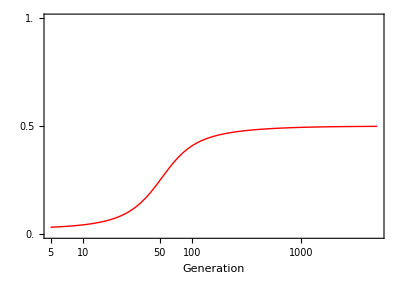

```mathematica
Wfemvec={0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Wfemvec},{exptime,Log[startplot],Log[endtime],0.1}];
Wfem=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Red,Thick},loglinearplotINVoptions]
```

#### Plot Y frequency in females

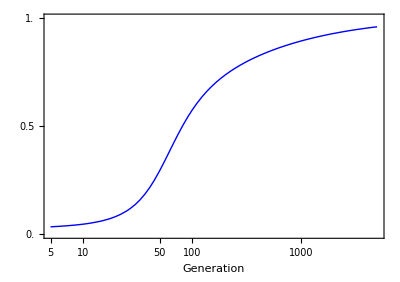

```mathematica
Yfemvec={0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Yfemvec},{exptime,Log[startplot],Log[endtime],0.1}];
Yfem=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Blue,Thick},loglinearplotINVoptions]
```

#### Plot Y frequency in males

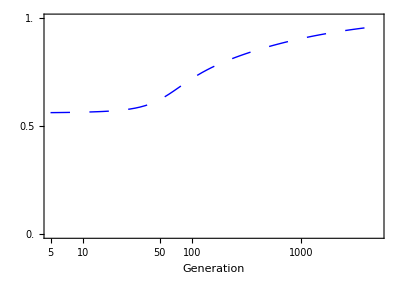

```mathematica
Ymalvec={0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Ymalvec},{exptime,Log[startplot],Log[endtime],0.1}];
Ymal=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Blue,Thick,Dashing[Large]},loglinearplotINVoptions]
```

#### Plot A frequency in females

```mathematica
Afemvec={1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Afemvec/2},{exptime,Log[startplot],Log[endtime],0.1}];
Afem=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1.1}},PlotStyle->{Black,Thick},loglinearplotINVoptions]
```

-Graphics-

#### Plot A frequency in males

```mathematica
Amalvec={0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Amalvec/2},{exptime,Log[startplot],Log[endtime],0.1}];
Amal=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1.1}},PlotStyle->{Black,Thick,Dashing[Large]},loglinearplotINVoptions]
```

-Graphics-

#### Plot all

```mathematica
plotA=Show[Wfem,Yfem,Ymal,Afem,Amal,LogLinearPlot[0.5,{x,5,endtime}, PlotStyle->{Black,Dashed}]]
```

-Graphics-

### Panel B - overdominance in both sexes, no haploid selection (parameters from fig S.2C green)

#### Parameters

```mathematica
tryFAA=0.6;
tryFAa=1;
tryFaa=0.6;
tryMAA=0.7;
tryMAa=1;
tryMaa=0.5;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=1/2;
tryαm=1/2;
tryr=0.005;
tryR=1/2;

param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
```

#### Simulation

```mathematica
sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]]
```

{0.720702,0.82555,0.0461837,0.5}

```mathematica
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]]
```

#### Plot neo-W frequency in females

```mathematica
Wfemvec={0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Wfemvec},{exptime,Log[startplot],Log[endtime],0.1}];
Wfem=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Red,Thick},loglinearplotINVoptions]
```

-Graphics-

#### Plot Y frequency in females

```mathematica
Yfemvec={0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Yfemvec},{exptime,Log[startplot],Log[endtime],0.1}];
Yfem=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Blue,Thick},loglinearplotINVoptions]
```

-Graphics-

#### Plot Y frequency in males

```mathematica
Ymalvec={0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Ymalvec},{exptime,Log[startplot],Log[endtime],0.1}];
Ymal=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Blue,Thick,Dashing[Large]},loglinearplotINVoptions]
```

-Graphics-

#### Plot A frequency in females

```mathematica
Afemvec={1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Afemvec/2},{exptime,Log[startplot],Log[endtime],0.1}];
Afem=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1.1}},PlotStyle->{Black,Thick},loglinearplotINVoptions]
```

-Graphics-

#### Plot A frequency in males

```mathematica
Amalvec={0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Amalvec/2},{exptime,Log[startplot],Log[endtime],0.1}];
Amal=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1.1}},PlotStyle->{Black,Thick,Dashing[Large]},loglinearplotINVoptions]
```

-Graphics-

#### Plot all

```mathematica
plotB=Show[Wfem,Yfem,Ymal,Afem,Amal,LogLinearPlot[0.5,{x,5,endtime}, PlotStyle->{Black,Dashed}]]
```

-Graphics-

### Panel C - sex-antagonism with male drive (parameters from fig S.3C green)

#### Parameters

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.05;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=1/2;
tryαm=1/2-8/100;
tryr=0.005;
tryR=1/2;

param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
```

#### Simulation

```mathematica
sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]]
```

{0.418811,0.363484,0.00693408,0.531719}

```mathematica
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]]
```

#### Plot neo-W frequency in females

```mathematica
Wfemvec={0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Wfemvec},{exptime,Log[startplot],Log[endtime],0.1}];
Wfem=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Red,Thick},loglinearplotINVoptions]
```

-Graphics-

#### Plot Y frequency in females

```mathematica
Yfemvec={0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Yfemvec},{exptime,Log[startplot],Log[endtime],0.1}];
Yfem=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Blue,Thick},loglinearplotINVoptions]
```

-Graphics-

#### Plot Y frequency in males

```mathematica
Ymalvec={0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Ymalvec},{exptime,Log[startplot],Log[endtime],0.1}];
Ymal=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Blue,Thick,Dashing[Large]},loglinearplotINVoptions]
```

-Graphics-

#### Plot A frequency in females

```mathematica
Afemvec={1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Afemvec/2},{exptime,Log[startplot],Log[endtime],0.1}];
Afem=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1.1}},PlotStyle->{Black,Thick},loglinearplotINVoptions]
```

-Graphics-

#### Plot A frequency in males

```mathematica
Amalvec={0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Amalvec/2},{exptime,Log[startplot],Log[endtime],0.1}];
Amal=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1.1}},PlotStyle->{Black,Thick,Dashing[Large]},loglinearplotINVoptions]
```

-Graphics-

#### Plot all

```mathematica
plotC=Show[Wfem,Yfem,Ymal,Afem,Amal,LogLinearPlot[0.5,{x,5,endtime}, PlotStyle->{Black,Dashed}]]
```

-Graphics-

### Panel D - ploidy-antagonism with pollen competition (parameters from fig S.8F green)

#### Parameters

```mathematica
tryFAA=1+(1/10);
tryFAa=1+(3/4)(1/10);
tryFaa=1;
tryMAA=1+(1/10);
tryMAa=1+(3/4)(1/10);
tryMaa=1;
trywAf=1;
trywaf=1;
trywAm=1-1/10;
trywam=1;
tryαf=1/2;
tryαm=1/2;
tryr=1/200;
tryR=1/2;

param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
```

#### Simulation

```mathematica
sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]]
```

{0.819467,0.82566,0.0576155,0.5}

```mathematica
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]]
```

#### Plot neo-W frequency in females

```mathematica
Wfemvec={0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Wfemvec},{exptime,Log[startplot],Log[endtime],0.1}];
Wfem=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Red,Thick},loglinearplotINVoptions]
```

-Graphics-

#### Plot Y frequency in females

```mathematica
Yfemvec={0,0,0,0,1,1,1,1,0,0,0,0,0,0,0,0};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Yfemvec},{exptime,Log[startplot],Log[endtime],0.1}];
Yfem=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Blue,Thick},loglinearplotINVoptions]
```

-Graphics-

#### Plot Y frequency in males

```mathematica
Ymalvec={0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Ymalvec},{exptime,Log[startplot],Log[endtime],0.1}];
Ymal=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Blue,Thick,Dashing[Large]},loglinearplotINVoptions]
```

-Graphics-

#### Plot A frequency in females

```mathematica
Afemvec={1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Afemvec/2},{exptime,Log[startplot],Log[endtime],0.1}];
Afem=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1.1}},PlotStyle->{Black,Thick},loglinearplotINVoptions]
```

-Graphics-

#### Plot A frequency in males

```mathematica
Amalvec={0,0,0,0,0,0,0,0,1,0,1,0,1,0,1,0};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Amalvec/2},{exptime,Log[startplot],Log[endtime],0.1}];
Amal=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1.1}},PlotStyle->{Black,Thick,Dashing[Large]},loglinearplotINVoptions]
```

-Graphics-

#### Plot all

```mathematica
plotD=Show[Wfem,Yfem,Ymal,Afem,Amal,LogLinearPlot[0.5,{x,5,endtime}, PlotStyle->{Black,Dashed}]]
```

-Graphics-

### All panels

```mathematica
GraphicsRow[
{
Show[
plotA,
Epilog->{
Rotate[Text[Style["Frequency",16],Scaled@{-0.15,0.5}],π/2],
Text[Style["A",16,Bold],Scaled@{0.05,0.95}],
Text[Style["ploidy-antagonism",16],Scaled@{0.5,0.95}]
},
PlotRangeClipping->False
],
Show[plotB,
Epilog->{
Text[Style["B",16,Bold],Scaled@{0.05,0.95}],
Text[Style["overdominance",16],Scaled@{0.5,0.95}]
}
],
Show[plotC,
Epilog->{
Text[Style["C",16,Bold],Scaled@{0.05,0.95}],
Text[Style["sex-antagonism",16],Scaled@{0.5,0.95}]
}
](*,
Show[plotD,
Epilog->{
Text[Style["D",16,Bold],Scaled@{0.05,0.95}]
}
]*)
},
Spacings->-50
]

Export[plotdir<>"Freq_plot_combined_PloidAntag.eps",%//rasterTrick];
```

-Graphics-

## Figure S.10 - unlinked neo-W can invade

### extra params

```mathematica
tryr=0;
tryR=0.5;
startplot=5;
endtime=5000;
trypm=0.01;
tryk=1;
```

```mathematica
loglinearplotINVoptions={
Frame->{{True,False},{True,False}}, 
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{Log[10],10,{0,0.01}},{Log[100],100,{0,0.01}},{Log[1000],1000,{0,0.01}}},Table[{y,y,ticksize},{y,0,1,0.5}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->1.25xsize,
Axes->True,
FrameLabel->{Style["Generation",FontSize->14],},
ImagePadding->Pad
};
```

```mathematica
loglinearplotINV2options={
Frame->{{True,False},{True,False}}, 
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{Log[10],10,{0,0.01}},{Log[100],100,{0,0.01}},{Log[1000],1000,{0,0.01}}},Table[{y,y,ticksize},{y,0.4,0.6,0.1}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImageSize->1.25xsize,
Axes->True,
FrameLabel->{Style["Generation",FontSize->14],},
ImagePadding->Pad
};
```

### Ploidally-antagonistic selection

#### Parameters

```mathematica
params={
wAm->0.76,wam->1,wAf->1,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
Faa->0.9,FAA->1.1,
Maa->0.9,MAA->1.1
};
```

#### Invasion fitness plots

Eigenvalues from the quadratic of interest (of the characteristic polynomial) for both polymorphic ancestral equilibria

```mathematica
WinvA=λ/.Solve[0==λ^2+(-(λmA1+λma1)+(χmA1+χma1))λ+((λmA1-χmA1)(λma1-χma1)-χmA1 χma1)/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params,λ];
WinvB=λ/.Solve[0==λ^2+(-(λmA1+λma1)+(χmA1+χma1))λ+((λmA1-χmA1)(λma1-χma1)-χmA1 χma1)/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params,λ];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Plots of invasion fitness vs recombination

```mathematica
plot1A=ListPlot[Table[{R,Max[WinvA]-1},{R,0,1/2,0.01}],Joined->True,PlotStyle->{Thick,Black},PlotRange->All,Axes->False];
plot1B=ListPlot[Table[{R,Max[WinvB]-1},{R,0,1/2,0.01}],Joined->True,PlotStyle->{Thick,Black},PlotRange->All,Axes->False];
```

Max in absolute value eigenvalue from the full characteristic polynomial

```mathematica
WinvAfull=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.ρ->0/.equilA0/.params,λ]]];
WinvBfull=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.ρ->0/.equilB0/.params,λ]]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Plots of invasion fitness vs recombination

```mathematica
plot2=Show[
ListPlot[Table[{R,WinvAfull-1},{R,0,1/2,0.01}],Joined->True,PlotRange->All,PlotStyle->Red],
ListPlot[Table[{R,WinvBfull-1},{R,0,1/2,0.01}],Joined->True,PlotStyle->Red],
PlotRange->All
];
```

Compare with the quadratic of interest results to ensure they are in agreement (make sure both red and black curves have same sign for any R)

```mathematica
Show[plot2,plot1A,plot1B,plot2,PlotRange->{0,All}]
```

-Graphics-

#### Simulation parameters

```mathematica
tryFAA=FAA/.params;
tryFAa=FAa/.params;
tryFaa=Faa/.params;
tryMAA=MAA/.params;
tryMAa=MAa/.params;
tryMaa=Maa/.params;
trywAf=wAf/.params;
trywaf=waf/.params;
trywAm=wAm/.params;
trywam=wam/.params;
tryαf=αf/.params;
tryαm=αm/.params;
```

```mathematica
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
```

#### Simulation

Note that only equil B is stable

```mathematica
sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{1.,1.,0.,0.5}}

Run simulation

```mathematica
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]]
```

#### Plot Y frequency in males

```mathematica
Ymalvec={0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Ymalvec},{exptime,Log[startplot],Log[endtime],0.1}];
(*YmalA=ListLogLinearPlot[%,Joined->True,PlotRange->{{startplot,endtime},{0,1}},PlotStyle->{Green,Thick},loglinearplotINVoptions]*)
YmalA=ListLogLinearPlot[%,Joined->True,PlotStyle->{Black,Thick},PlotRange->{0,1}]
```

-Graphics-

#### Frequency of males

```mathematica
Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
MaleFreqA=ListLogLinearPlot[%,Joined->True,PlotStyle->{Black,Thick},PlotRange->{0,1}]
```

-Graphics-

### Overdominance in males, no haploid selection

#### Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
Faa->1.1,FAA->0.99,
Maa->0.8,MAA->0.8
};
```

#### Invasion plots

Eigenvalues from the quadratic of interest (of the characteristic polynomial)

```mathematica
WinvA=λ/.Solve[0==λ^2+(-(λmA1+λma1)+(χmA1+χma1))λ+((λmA1-χmA1)(λma1-χma1)-χmA1 χma1)/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params,λ];
WinvB=λ/.Solve[0==λ^2+(-(λmA1+λma1)+(χmA1+χma1))λ+((λmA1-χmA1)(λma1-χma1)-χmA1 χma1)/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params,λ];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
plot2A=ListPlot[Table[{R,Max[WinvA]-1},{R,0,1/2,0.01}],Joined->True,PlotStyle->{Thick,Black,Dashing[Large]},PlotRange->All,Axes->False];
plot2B=ListPlot[Table[{R,Max[WinvB]-1},{R,0,1/2,0.01}],Joined->True,PlotStyle->{Thick,Black,Dashing[Large]},PlotRange->All,Axes->False];
```

Max in absolute value eigenvalue from the full characteristic polynomial

```mathematica
WinvAfull=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.ρ->0/.equilA0/.params,λ]]];
WinvBfull=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.ρ->0/.equilB0/.params,λ]]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
plot2=Show[
ListPlot[Table[{R,WinvAfull-1},{R,0,1/2,0.01}],Joined->True,PlotRange->All,PlotStyle->Red],
ListPlot[Table[{R,WinvBfull-1},{R,0,1/2,0.01}],Joined->True,PlotStyle->Red],
PlotRange->All
];
```

Compare with the quadratic of interest results

```mathematica
Show[plot2,plot2A,plot2B,plot2,PlotRange->All]
```

-Graphics-

#### Simulation parameters

```mathematica
tryFAA=FAA/.params;
tryFAa=FAa/.params;
tryFaa=Faa/.params;
tryMAA=MAA/.params;
tryMAa=MAa/.params;
tryMaa=Maa/.params;
trywAf=wAf/.params;
trywaf=waf/.params;
trywAm=wAm/.params;
trywam=wam/.params;
tryαf=αf/.params;
tryαm=αm/.params;
```

```mathematica
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
```

#### Simulation

Note that only equil B (and B’) is stable

```mathematica
sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{0.,0.,1.,0.5},{1.,1.,0.,0.5}}

Run simulation

```mathematica
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[2]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]]
```

#### Plot Y frequency in males

```mathematica
Ymalvec={0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Ymalvec},{exptime,Log[startplot],Log[endtime],0.1}];
YmalB=ListLogLinearPlot[%,Joined->True,PlotRange->{0,1},PlotStyle->{Black,Thick,Dashing[Large]}]
```

-Graphics-

#### Frequency of males

```mathematica
Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
MaleFreqB=ListLogLinearPlot[%,Joined->True,PlotRange->{0,1},PlotStyle->{Black,Thick,Dashing[Large]}]
```

-Graphics-

### Sexual antagonism with haploid competition in males

#### Parameters

```mathematica
params={
wAm->0.85,wam->1,wAf->1,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
Faa->0.98,FAA->1.1,
Maa->1.01,MAA->0.8
};
```

#### Invasion plots

Eigenvalues from the quadratic of interest (of the characteristic polynomial)

```mathematica
WinvA=λ/.Solve[0==λ^2+(-(λmA1+λma1)+(χmA1+χma1))λ+((λmA1-χmA1)(λma1-χma1)-χmA1 χma1)/.reverse/.pAveM->(1-q)pXm+q pYm/.equilA0/.params,λ];
WinvB=λ/.Solve[0==λ^2+(-(λmA1+λma1)+(χmA1+χma1))λ+((λmA1-χmA1)(λma1-χma1)-χmA1 χma1)/.reverse/.pAveM->(1-q)pXm+q pYm/.equilB0/.params,λ];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
plot3A=ListPlot[Table[{R,Max[WinvA]-1},{R,0,1/2,0.01}],Joined->True,PlotStyle->{Thick,Black,Dotted},PlotRange->All,Axes->False];
plot3B=ListPlot[Table[{R,Max[WinvB]-1},{R,0,1/2,0.01}],Joined->True,PlotStyle->{Thick,Black,Dotted},PlotRange->All,Axes->False];
```

Max in absolute value eigenvalue from the full characteristic polynomial

```mathematica
WinvAfull=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.ρ->0/.equilA0/.params,λ]]];
WinvBfull=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.ρ->0/.equilB0/.params,λ]]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
plot2=Show[
ListPlot[Table[{R,WinvAfull-1},{R,0,1/2,0.01}],Joined->True,PlotRange->All,PlotStyle->Red],
ListPlot[Table[{R,WinvBfull-1},{R,0,1/2,0.01}],Joined->True,PlotStyle->Red],
PlotRange->All
];
```

Compare with the quadratic of interest results

```mathematica
Show[plot2,plot3A,plot3B,plot2,PlotRange->All]
```

-Graphics-

#### Simulation parameters

```mathematica
tryFAA=FAA/.params;
tryFAa=FAa/.params;
tryFaa=Faa/.params;
tryMAA=MAA/.params;
tryMAa=MAa/.params;
tryMaa=Maa/.params;
trywAf=wAf/.params;
trywaf=waf/.params;
trywAm=wAm/.params;
trywam=wam/.params;
tryαf=αf/.params;
tryαm=αm/.params;
```

```mathematica
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
```

#### Simulation

Note that only equil B is stable

```mathematica
sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{1.,1.,0.,0.5}}

Run simulation

```mathematica
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]]
```

#### Plot Y frequency in males

```mathematica
Ymalvec={0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1};
Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].Ymalvec},{exptime,Log[startplot],Log[endtime],0.1}];
YmalC=ListLogLinearPlot[%,Joined->True,PlotRange->{0,1},PlotStyle->{Black,Thick,Dotted}]
```

-Graphics-

#### Frequency of males

```mathematica
Table[{Round[Exp[exptime]],sexratio[param,run[Round[Exp[exptime]]]]},{exptime,Log[startplot],Log[endtime],0.1}];
MaleFreqC=ListLogLinearPlot[%,Joined->True,PlotRange->{0,1},PlotStyle->{Black,Thick,Dotted}]
```

-Graphics-

### All

```mathematica
GraphicsRow[{

(*Legended[
Show[

plot1A,(*plot2A,*)plot3A,

PlotRange->{{0,0.5},{0,0.11}},
Frame->{True,True,False,False},
FrameTicks->{Table[{x,x,ticksize},{x,0,1/2,0.1}],Table[{y,y,ticksize},{y,0,0.1,0.1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
Epilog->{
Rotate[Text[Style["Invasion fitness (λ_WA-1)",14],Scaled@{-0.1,0.5}],90 Degree],
Text[Style["Equilibrium A",14,Bold],Scaled@{0.5,0.95}]
},
PlotRangeClipping->False,
ImageSize->1.25xsize,
ImagePadding->{{50,20},{50,20}},
FrameLabel->{"Rate of recombination (R)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14}
],
Placed[
LineLegend[
{Directive[Thickness[0.1],Black],
Directive[Thickness[0.1],Black,Dashing[Medium]],
Directive[Thickness[0.1],Black,Dotted]
},
{Style["ploidy-antagonism",14],
Style["male overdominance",14],
Style["sex-antagonism",14]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
Scaled@{0.7,0.35}
]
],*)

Legended[
Show[

plot1B,plot2B,plot3B,

PlotRange->{{0,0.5},{0,0.11}},
Frame->{True,True,False,False},
FrameTicks->{Table[{x,x,ticksize},{x,0,1/2,0.1}],Table[{y,y,ticksize},{y,0,0.1,0.1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
Epilog->{
Rotate[Text[Style["Invasion fitness (λ_W'^(XY)-1)",14],Scaled@{-0.1,0.5}],90 Degree](*,
Text[Style["Equilibrium B",14,Bold],Scaled@{0.5,0.95}]*)
},
ImageSize->1.25xsize,
PlotRangeClipping->False,
ImagePadding->{{50,20},{50,20}},
FrameLabel->{"Rate of recombination (R)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14}
],
Placed[
LineLegend[
{Directive[Thickness[0.1],Black],
Directive[Thickness[0.1],Black,Dashing[Medium]],
Directive[Thickness[0.1],Black,Dotted]
},
{Style["ploidy-antagonism",14],
Style["male overdominance",14],
Style["sex-antagonism",14]
},
LegendFunction->"Frame",
LegendLayout->"Column"
],
Scaled@{0.7,0.7}
]
],

Show[

YmalA,YmalB,YmalC,
Epilog->{
Rotate[Text[Style["Frequency of Y in males",14],Scaled@{-0.12,0.5}],90 Degree],
Text[Style["R=1/2",14,Bold],Scaled@{0.1,0.1}],
Text[Style["B",14,Bold],Scaled@{0.05,0.95}]
},
PlotRangeClipping->False,
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
loglinearplotINVoptions
],

Show[

MaleFreqA,MaleFreqB,MaleFreqC,
PlotRange->{0.4,0.61},
Epilog->{
Rotate[Text[Style["Frequency of males",14],Scaled@{-0.12,0.5}],90 Degree],
Text[Style["R=1/2",14,Bold],Scaled@{0.1,0.1}],
Text[Style["C",14,Bold],Scaled@{0.05,0.95}]
},
PlotRangeClipping->False,
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
loglinearplotINV2options
]
},

Spacings->{-25,0}
]

Export[plotdir<>"neoW_invades_tight_loose.eps",%//rasterTrick];
```

-Graphics-